# Qulib

## Simple, yet useful, functions for dealing with Quantum Information and Open Quantum Systems. Gabriel T. Landi QT^2 group

Contributors: Jader P. dos Santos, Artur Lacerda, Michael Kewming, Anthony Kiely, Steve Campbell, Giacomo Guarnieri, Marcelo Janovitch.

## General purpose functions

## Silly but useful functions

### mf: visualizing matrices

```mathematica
(* Prints in matrix form but does not alter definition *)
Clear[mf];
mf[A_]:=(Print[MatrixForm@Chop@A];A)
mf::usage = "mf[A] will print the matrix in a pretty way using Mathematica's MatrixForm[] function. The printed version also chops any small numbers.";
```

#### Example usage

```mathematica
(* I normally use it like this *)
A = {{1,2},{3,4}}//mf;
```

(1 | 2
3 | 4)

```mathematica
ψ = 1/(√2){1,1}//mf;
```

(1/(√2)
1/(√2))

```mathematica
(* But one can also use it as *)
A = {{1,2},{3,4}};
mf[A];
```

(1 | 2
3 | 4)

### cf: FullSimplify assuming variables are real and positive

```mathematica
(* FullSimplifty + ComplexExpand (to get rid of "Conjugate"s) *)
Clear[cf];
(*cf[expr_]:=FullSimplify@ComplexExpand@expr;*)
cf[expr_]:=FullSimplify[expr,Thread[DeleteDuplicates@Cases[expr,_Symbol,∞]>0]]

cf::usage = "cf[expr] performs a FullSimplify on the expression, assuming that all symbols are real and positive.";
```

#### Example usage

```mathematica
(* Mathematica doesn't know when a symbol is real *)
x = {Cos[θ],Sin[θ]};
x*.x
FullSimplify[%]
```

Conjugate[Cos[θ]] Cos[θ]+Conjugate[Sin[θ]] Sin[θ]

Cosh[2 Im[θ]]

```mathematica
x*.x//cf
```

1

```mathematica
(* The function does not always works the way it is intended to *)
Clear[x]
√Cos[x]//cf
```

√Cos[x]

### out: Outer products

```mathematica
(* Outer product |v⟩⟨u| between two vectors *)
(* Properly conjugates *)
Clear[out];
out[v_,u_]:=Outer[Times,v,Conjugate[u]];
out::usage = "Outer product: out[v,u] = |v⟩⟨u|";
```

#### Example usage

```mathematica
ψ = 1/(√2){1,ⅈ}//mf;
out[ψ,ψ]//mf;
```

(1/(√2)
ⅈ/(√2))

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

```mathematica
(* The second argument is complex conjugated *)
```

### ℂ: commutator

ℂ[A,B] = [A,B]
ℂ[A,B,-1] = {A,B} (anti-commutator)

```mathematica
(* ℂ writes as esc+dsC+esc *)
Clear[ℂ];
ℂ[A_,B_]:=A.B-B.A;
ℂ[A_,B_,ζ_]:=A.B-ζ B.A

ℂ::usage = "ℂ[A,B] = [A,B] = A.B-B.A. More generally ℂ[A,B,ζ] = A.B + ζ B.A. Use ζ = -1 for anti-commutator";
```

#### Example usage

```mathematica
A = {{1,2},{3,4}};
B = {{5,4},{3,2}};
ℂ[A,B]//mf;
```

(-6 | -18
18 | 6)

```mathematica
ℂ[A,B,-1]//mf;
```

(28 | 34
36 | 34)

### ChopCheck: for checking the results of matrix calculations

```mathematica
(* Quick way of checking what are the distinct entries of a matrix or tensor *)
Clear[ChopCheck];
ChopCheck[A_,tol_:10^-10]:=DeleteDuplicates@Flatten@Chop[A,tol]

ChopCheck::usage = "ChopCheck[A] gives 0 when the matrix is 0, to a tolerance of 10^-10. I usually do ChopCheck[A-B] whenever I want to check numerically that A = B";
```

#### Example usage

Verify that A = SΛS† indeed is the correct diagonalization of a matrix A.

```mathematica
A = ({{2, 1, 0}, {1, 5, -3}, {0, -3, 2.}});
{Λ,S} = Eigsys[A]
```

{{0.,2.,7.},{{-0.267261,0.948683,0.169031},{0.534522,8.426×10^-16,0.845154},{0.801784,0.316228,-0.507093}}}

```mathematica
A-S.DiagonalMatrix[Λ].S†//ChopCheck
```

{0}

### range, linspace and logspace

- range[] you specify the stepsize. 
- linspace[] you specify the number of points . 
- logspace[] is the same, but in logscale (base 10) .

linspace/logspace were copied from python/Matlab
range[] is exactly like the native Range[] function in Mathematica. See below for an explanation.

```mathematica
(* Use just like Range[] function *)
Clear[range];
range[xi_,xf_,df_:1]:=N@Rationalize@Range[xi,xf,df]; 
range::usage = "Same input/output as Range, but avoids a subtle floating point issue of the latter.";

(* Stolen from python/Matlab *)
Clear[linspace]
linspace[dd1_,dd2_,n_:100]:=With[{d1=N@dd1,d2=N@dd2},If[n==1,{d1},d1+(d2-d1)/(n-1) Range[0,n-1]]];
linspace::usage = "linspace[a,b,npts] yields npts linearly interpolated between a (inclusive) and b (inclusive).";

Clear[logspace];
logspace[dd1_,dd2_,n_:100]:=10^linspace[dd1,dd2,n];
logspace::usage = "Same as linspace, but in log scale. logscale[2,5,50] will give 50 pts between 10^2 and 10^5";
```

#### Example usage

```mathematica
range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
range[0,3]
```

{0.,1.,2.,3.}

```mathematica
linspace[0,3,20]
```

{0.,0.157895,0.315789,0.473684,0.631579,0.789474,0.947368,1.10526,1.26316,1.42105,1.57895,1.73684,1.89474,2.05263,2.21053,2.36842,2.52632,2.68421,2.84211,3.}

```mathematica
logspace[0,10,10]
```

{1.,12.9155,166.81,2154.43,27825.6,359381.,4.64159×10^6,5.99484×10^7,7.74264×10^8,1.×10^10}

```mathematica
logspace[2,5,4]
```

{100.,1000.,10000.,100000.}

```mathematica
logspace[2,5,6]
```

{100.,398.107,1584.89,6309.57,25118.9,100000.}

#### Reason for using range instead of Range

Mathematica's  Range[] function looks normal:

```mathematica
Range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

But actually it has weird floating point imprecisions.

```mathematica
Range[0,1,0.1]//InputForm
```

{0., 0.1, 0.2, 0.30000000000000004, 0.4, 0.5, 0.6000000000000001, 
0.7000000000000001, 0.8, 0.9, 1.}

This may lead to weird things such as

```mathematica
Position[Range[0,1,0.1],0.6]
```

{{7}}

```mathematica
Position[Range[0,1,0.1],0.7]
```

{}

It cannot find “0.7” in the list because the actual number is 0.7000000000000001 (although Mathematica is printing 0.7). 
This is super annoying. 

The function range corrects this:

```mathematica
range[0,1,0.1]//InputForm
```

{0., 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.}

### PartitionIn: partition a list into x sublists, with proper paddings at the end

```mathematica
Clear[PartitionIn];
PartitionIn[list_,x_,pad_:""]:=Partition[list,Ceiling[Length[list]/x],Ceiling[Length[list]/x],1,pad]

PartitionIn::usage = "PartitionIn[list,x] partitions list into x sublists, possibly with paddings at the end.";
```

#### Example usage

Mathematica’s Partition[] splits a list into sublists of pre-defined lengths. 
But sometimes we want to partition a list into a pre-defined number of sublists instead, with possible paddings at the end.

```mathematica
list = Range[1,19]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
Partition[list,3,3,1," "]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12},{13,14,15},{16,17,18},{19, , }}

```mathematica
(* This splits the list into exactly 3 sublists *)
PartitionIn[list,3]
```

{{1,2,3,4,5,6,7},{8,9,10,11,12,13,14},{15,16,17,18,19,,}}

### PrettyTiming: Prints time in a pretty way

AbsoluteTiming[] with pretty formatting.

```mathematica
Clear[PrettyTiming];
SetAttributes[PrettyTiming,HoldAll];
PrettyTiming[computation_]:=Module[{t1,t2,output,time,h,m,s},
t1 = UnixTime[];
output=ReleaseHold[computation];
t2 = UnixTime[];
time = t2-t1;
 h = Floor[time/3600];
m = Floor[Mod[time,3600]/60];
s = Round@Mod[time,60];
Print[ToString[h]<>"h : "<>ToString[m]<>"m : "<>ToString[s]<>"s"];
(*Print[PrettyTime[t2-t1]];*)
Return[output]];

PrettyTiming::usage = "PrettyTiming[computation] uses Mathematica's AbsoluteTiming[] to time a computation, but prints the result in a prettier form.";
```

#### Example usage

```mathematica
(* This is how one would time a computation in Mathematica *)
AbsoluteTiming[Do[1,{10^9}]]
```

$Aborted

```mathematica
(* PrettyTiming does the same, but prints the time (instead of outputing it) and does so with a pretty format *)
PrettyTiming[Do[1,{5 10^8}]]
```

0h : 0m : 6s

```mathematica
(* Time a calculation of the variance of random variables *)
```

```mathematica
PrettyTiming[Variance@RandomVariate[BetaDistribution[2,3],10^8]]
```

0h : 0m : 10s

0.0399991

## Linear algebra

### kron: compact Kronecker products which correctly handles vectors

Mathematica’s KroneckerProduct handles vectors in a weird way.

```mathematica
Clear[kron];
kron[mats__?MatrixQ]:=KroneckerProduct[mats];
kron[vecs__?VectorQ]:=Flatten@KroneckerProduct[vecs];

kron::usage ="kron[A,B,C...] = A ⊗ B ⊗ C ⊗ .... For matrices, it is exactly like the native KroneckerProduct[] from Mathematica. For vectors, kron[u,v] produces the proper |u⟩ ⊗ |v⟩."
```

kron[A,B,C...] = A ⊗ B ⊗ C ⊗ .... For matrices, it is exactly like the native KroneckerProduct[] from Mathematica. For vectors, kron[u,v] produces the proper |u⟩ ⊗ |v⟩.

```mathematica
(* 𝕀 ⊗ 𝕀 ⊗ 𝕀 ⊗ 𝕀 ⊗ A ⊗ 𝕀 ⊗ 𝕀 ⊗ 𝕀 ⊗ 𝕀 *)
```

```mathematica
Clear[KronEye];
KronEye[A_,𝒩_,j_]:=kron[Eye[Length[A]^(j-1)],A,Eye[Length[A]^(𝒩-j)]]

KronEye::usage = "KronEye[A,𝒩,j] = (𝕀 ⊗ ... 𝕀 ⊗ A ⊗ 𝕀 ... ⊗ 𝕀, with A at site j and 𝒩 sites in total.";
```

#### Example usage

```mathematica
(* For matrices, kron[A,B] is just a compact notation of KroneckerProduct[A,B] *)
A = {{1,2},{3,4}};
B = {{0,1},{1,0}};
kron[A,B]//mf;
```

(0 | 1 | 0 | 2
1 | 0 | 2 | 0
0 | 3 | 0 | 4
3 | 0 | 4 | 0)

```mathematica
kron[A,A,A]//mf;
```

(1 | 2 | 2 | 4 | 2 | 4 | 4 | 8
3 | 4 | 6 | 8 | 6 | 8 | 12 | 16
3 | 6 | 4 | 8 | 6 | 12 | 8 | 16
9 | 12 | 12 | 16 | 18 | 24 | 24 | 32
3 | 6 | 6 | 12 | 4 | 8 | 8 | 16
9 | 12 | 18 | 24 | 12 | 16 | 24 | 32
9 | 18 | 12 | 24 | 12 | 24 | 16 | 32
27 | 36 | 36 | 48 | 36 | 48 | 48 | 64)

```mathematica
(* For vectors, Mathematica is weirrrd *)
```

```mathematica
v0 = {1,0};
v1 = {0,1};
KroneckerProduct[v0,v1]//mf;
```

(0 | 1
0 | 0)

```mathematica
(* kron[] saves the day *)
kron[v0,v1]//mf;
```

(0
1
0
0)

```mathematica
(* Pauli matrix for site 2 of a spin chain with 4 sites *)
σx = ({{0, 1}, {1, 0}});
KronEye[σx,4,2]//mf;
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

### Proj & Basis: projection matrices and basis elements

```mathematica
Clear[Proj];
Proj[n_,i_]:=SparseArray[{{i,i}->1},{n,n}];
Proj[n_,i_,j_]:=SparseArray[{{i,j}->1},{n,n}];

Proj[{n_,m_},i_]:=SparseArray[{{i,i}->1},{n,m}];
Proj[{n_,m_},i_,j_]:=SparseArray[{{i,j}->1},{n,m}];


Proj::usage = "Proj[n,i,j] yields a n×n matrix with element (i,j) equal 1. Proj[n,i] = Proj[n,i,i].";
```

```mathematica
Clear[Basis];
Basis[n_,i_]:=SparseArray[{i->1},n]
Basis[n_,ilist_?ArrayQ]:=Total@Table[Basis[n,i],{i,ilist}]

Basis::usage = "Basis[n,i] = (0,...,0,1,0,...,0) with 1 at position i. Basis[n,{i1,i2,...}] yields the same, but with 1's at positions i1,i2,...";
```

#### Example usage

```mathematica
Proj[4,1]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Proj[4,2]//mf;
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Proj[4,1,2]//mf;
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Basis[4,1]//mf;
```

(1
0
0
0)

```mathematica
Basis[4,2]//mf;
```

(0
1
0
0)

```mathematica
Basis[4,{1,2}]//mf;
```

(1
1
0
0)

### Useful matrices

Eye  = Identity for symbolics. 
NEye = Identity for numerics. 

toeplitzMatrix = just a toeplitz matrix, with a more flexible syntax than Mathematica’s ToeplitzMatrix[]. 
StiffnessMatrix =hopping matrix of the tight-binding model.
CirculantMatrix = same, but with periodic boundary conditions.

```mathematica
Clear[Eye,NEye];
Eye[n_]:=SparseArray[{{i_,i_}->1},{n,n}];
Eye::usage = "Eye[n] is the n×n identity matrix as a sparse array. Same as NEye, but the 1s in the diagonal are integers";

NEye[n_]:=SparseArray[{{i_,i_}->1.},{n,n},0.];
Eye::usage = "NEye[n] is the n×n identity matrix as a sparse array. Same as Eye, but the 1.0s in the diagonal are in floating point.";
```

```mathematica
Clear[toeplitzMatrix];
toeplitzMatrix[a_,k_,L_]:=If[L==1,If[k==1,{{a}},{{0}}],SparseArray[{Band[{1,k}]->a,Band[{k,1}]->a},{L,L}]]

toeplitzMatrix::usage = "toeplitzMatrix[a,k,L] yields a L×L symmetric matrix with elements a along the kth diagonal (k=1 is the diagonal and k=2 is the first off-diagonal).";
```

```mathematica
Clear[StiffnessMatrix,CirculantMatrix];
StiffnessMatrix[n_]:=toeplitzMatrix[-1,2,n];
CirculantMatrix[n_]:=toeplitzMatrix[-1,2,n]+toeplitzMatrix[-1,-1,n];

StiffnessMatrix::usage = "StiffnessMatrix[n]: hopping matrix of the tight-binding model with open boundary conditions";
CirculantMatrix::usage = "CirculantMatrix[n]: hopping matrix of the tight-binding model with periodic boundary conditions";
```

```mathematica
Clear[FirstDerivative];
FirstDerivative[n_,Δx_:1,boundary_:None]:=
If[boundary===None,
1/(2Δx)SparseArray[{
Band[{1,2}]->1,
Band[{2,1}]->-1
},{n,n}],
1/(2Δx)SparseArray[{
{i_,j_}/;j==i+1&&i!=1->1,
{i_,j_}/;j==i-1&&i!=n->-1,
{1,2}->2,
{1,1}->-2,
{n,n}->2,
{n,n-1}->-2
},{n,n}]];

Clear[SecondDerivative]
SecondDerivative[n_,Δx_:1,boundary_:None]:=
If[boundary===None,
1/Δx^2(2Eye[n]+StiffnessMatrix[n])]
```

#### Example usage:

```mathematica
Eye[3]//mf;
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(* The distinction is silly, but for doing numerics it is useful to use NEye *)
NEye[3]//mf;
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

```mathematica
toeplitzMatrix[a,1,5]//mf;
```

(a | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0
0 | 0 | a | 0 | 0
0 | 0 | 0 | a | 0
0 | 0 | 0 | 0 | a)

```mathematica
toeplitzMatrix[a,2,5]//mf;
```

(0 | a | 0 | 0 | 0
a | 0 | a | 0 | 0
0 | a | 0 | a | 0
0 | 0 | a | 0 | a
0 | 0 | 0 | a | 0)

```mathematica
(* Also works with 1D matrices *)
toeplitzMatrix[a,1,1]
```

{{a}}

```mathematica
StiffnessMatrix[6]//mf;
```

(0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0)

```mathematica
CirculantMatrix[6]//mf;
```

(0 | -1 | 0 | 0 | 0 | -1
-1 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | -1
-1 | 0 | 0 | 0 | -1 | 0)

### Boxcar function

A unit box from a to b:
Width b-a := 2δ, centered at c = (a+b)/2

Boxcar(a,b) = θ(x-a)θ(b-x)
	        = θ(x-a) - θ(x-b)
                  = π(1/(2δ)(x-c)
                  = θ(δ^2-(x-c)^2)

Here θ = HeavisideTheta and π = HeavisidePi

```mathematica
Clear[Boxcar];
Boxcar[a_,b_][x_]:=UnitStep[x-a]-UnitStep[x-b]

Boxcar[a_,b_,smooth_][x_]:=If[Abs[smooth]<10^-14,Boxcar[a,b][x],1/2(Tanh[(x-a)/smooth]-Tanh[(x-b)/smooth] )]

Boxcar::usage = "Boxcar[a,b][x] returns a boxcar function from a to b";
```

#### Example usage

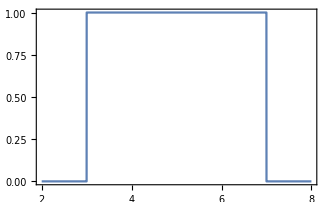

```mathematica
Plot[Boxcar[3,7][x],{x,2,8},Exclusions->None]
```

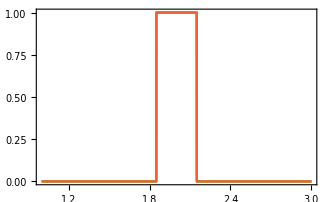

```mathematica
(* Different ways of implementing a boxcar, centered in c, of total width δ *)
c = 2;
δ = 0.15;
a = c-δ;
b = c+δ;
Plot[{
HeavisideTheta[x-a]-HeavisideTheta[x-b],
HeavisideTheta[x-a]HeavisideTheta[b-x],
HeavisidePi[1/(2δ)(x-c)],
HeavisideTheta[δ^2-(x-c)^2]
},{x,1,3},Exclusions->None,PlotStyle->Automatic]
```

```mathematica
Manipulate[Plot[Boxcar[a,b,smooth][x],{x,-2,2}],{{a,0},-1,1},{{b,1},0,2},{{smooth,0.1},0.01,0.2}]
```

### Eigstuff & Ground-state: sorts eigenvalues and correctly orders eigenvectors

This function “fixes” some weird outputs of Mathematica’s eigensystem functions. 
- Order eigenvalues by smaller in number, not magnitude: 1st eigenvalue is ground-state. 
- Output eigenvectors as a matrix, not a list of lists.

```mathematica
Clear[Eigvals,Eigvecs,Eigsys];

(*Eigvals[A_,neigs_:"all",Δ_:10^5]:=Reverse@Eigenvalues[A + Δ NEye@Length@A,If[neigs=="all",Length@A,-neigs]]-Δ;*)
Eigvals[A_,neigs_:"all",Δ_:10^5]:=If[neigs==="all",
Sort@Eigenvalues[N@A],
Reverse@Eigenvalues[A + Δ NEye@Length@A,-neigs]-Δ];

(*Eigvecs[A_,neigs_:"all",Δ_:10^5]:=Transpose[(Reverse@Eigenvectors[A + Δ NEye@Length@A,If[neigs=="all",Length@A,-neigs]])];*)
Eigvecs[A_,neigs_:"all",Δ_:10^5]:=
Module[{tmp,e,v,ord},
If[neigs=="all",(
{e,v}=Eigensystem[A];
ord=Ordering[e];
Transpose[v⟦ord⟧]
),
(
{e,v}=Eigensystem[A + Δ NEye@Length@A,-neigs];
 Transpose@Reverse@v
)
]
]

(*Eigsys[A_, neigs_:"all",Δ_:10^5]:=Module[{tmp},
tmp=Eigensystem[A + Δ NEye@Length@A,If[neigs=="all",Length@A,-neigs]];
 {Reverse@First@tmp-Δ,Transpose@Reverse@Last@tmp}
];*)

Clear[Eigsys];
Eigsys[A_, neigs_:"all",Δ_:10^5]:=Module[{tmp,e,v,ord},

If[neigs=="all",(
{e,v}=Eigensystem[A];
ord=Ordering[e];
{e⟦ord⟧,Transpose[v⟦ord⟧]}
),
(
{e,v}=Eigensystem[A + Δ NEye@Length@A,-neigs];
 {Reverse@e-Δ,Transpose@Reverse@v}
)
]
]
```

```mathematica
Clear[GroundState];
GroundState[H_]:=Eigvecs[H,1]⟦All,1⟧

GroundState[H_,n_]:=Eigvecs[H,n]⟦All,-1⟧;
```

#### Example usage

```mathematica
(* Eigenvalues of a spin 3/2 Hamiltonian *)
LoadArbitrarySpinMatrices[3/2];
H = Sz + 0.3 Sx.Sx//mf;
```

(1.725 | 0 | 0.259808 | 0
0 | 1.025 | 0 | 0.259808
0.259808 | 0 | 0.025 | 0
0 | 0.259808 | 0 | -1.275)

```mathematica
(* Mathematica orders eigenvalues by magnitude. The ground-state in this case is actually -1.30398 *)
Eigenvalues[H]
```

{1.76382,-1.30398,1.05398,-0.0138194}

```mathematica
(* Eigvals order in the natural way *)
Eigvals[H]
```

{-1.30398,-0.0138194,1.05398,1.76382}

```mathematica
(* Suppose one wishes only the first two eigenvalues. Here is what Mathematica yields: *)
Eigenvalues[H,2]
```

{1.76382,-1.30398}

```mathematica
(* The ordering is weird because it is ordered by absolute value. For Eigvals the ordering is consistent with ground states: *)
Eigvals[H,2]
```

{-1.30398,-0.0138194}

```mathematica
(* Diagonalization is traditionally written as H = S.ℰ.S^-1, with eigenvectors being the columns of S. *)
(* Mathematica returns eigenvectors as the rows *)
```

```mathematica
{ℰ,S}=Eigensystem[H];
Sᵀ.DiagonalMatrix[ℰ].Inverse[Sᵀ]//mf;
```

(1.725 | 0 | 0.259808 | 0
0 | 1.025 | 0 | 0.259808
0.259808 | 0 | 0.025 | 0
0 | 0.259808 | 0 | -1.275)

```mathematica
(* Eigsys and Eigvecs return eigenvectors as the columns of S *)
{ℰ,S}=Eigsys[H];
S.DiagonalMatrix[ℰ].S†//mf;
```

(1.725 | 0 | 0.259808 | 0
0 | 1.025 | 0 | 0.259808
0.259808 | 0 | 0.025 | 0
0 | 0.259808 | 0 | -1.275)

```mathematica
S
```

{{0.,0.147776,0.,0.989021},{-0.110866,0.,-0.993835,0.},{0.,-0.989021,0.,0.147776},{0.993835,0.,-0.110866,0.}}

```mathematica
Eigvecs[H]
```

{{0.,0.147776,0.,0.989021},{-0.110866,0.,-0.993835,0.},{0.,-0.989021,0.,0.147776},{0.993835,0.,-0.110866,0.}}

### expect: operator average ⟨O⟩, handling pure and mixed states in equal footing

```mathematica
(* y can be a ket or a density matrix *)
Clear[expect];
expect[A_,y_]:=If[Length@Dimensions@y==2,Tr[A.y],y*.A.y];

expect::usage = "expect[A,y] computes ⟨A⟩ in the state y, which can be either a ket or a density matrix";
```

```mathematica
(* Checks if H commutes with y, and y can be a pure state *)
Clear[checkCommute]
checkCommute[H_,y_]:=Module[{ρ},
ρ = If[Length@Dimensions@y==2,y,Outer[Times,y,Conjugate[y]]];
If[Norm[H.ρ-ρ.H]>10^-10,False,True]
]
```

#### Example usage

```mathematica
ψ = 1/(√2){1,1};
expect[σx,ψ]
```

1

```mathematica
(* Or use a density matrix *)
ρ = out[ψ,ψ];
expect[σx,ρ]
```

1

### DirectSum

```mathematica
Clear[DirectSum]
DirectSum[mats__]:=Module[{m=List@mats,tab, diag,a},
tab= Table[a[i],{i,Length@m}];
diag=DiagonalMatrix[Table[a[i],{i,Length@m}]];
diag/.Thread[tab->m]//ArrayFlatten
]

DirectSum::usage = "DirectSum[A,B,...] yields a diagonal block matrix diag(A,B,...)";
```

#### Example usage

```mathematica
LoadPauliMatrices[]
DirectSum[σx,σz]//mf;
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
DirectSum[σx,σy,σz]//mf;
```

(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1)

#### Alternative implementation from klgr in StackExchange

Based on https://mathematica.stackexchange.com/questions/19778/how-to-form-a-block-diagonal-matrix-from-a-list-of-matrices/19780#19780

```mathematica
DirectSum2=With[{r=MapIndexed[#2[[1]] {1,1}->#&,#,1]},SparseArray`SparseBlockMatrix[r]]&;
```

```mathematica
DirectSum2[{σx,σy,σz}]//mf;
```

(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1)

### KPM: Kernel Polynomial Method

https://journals.aps.org/rmp/abstract/10.1103/RevModPhys.78.275
https://journals.aps.org/prl/pdf/10.1103/PhysRevLett.124.100602


This is an approximate method to compute general spectral functions of the form 

g(E,O)=∑_k δ(E-E_k) ⟨k|O|k⟩

where O is an observable and H|k⟩ = E_k|k⟩ are eigenvalues/eigenvectors of a certain Hamiltonian H.
Examples: 

Global DOS:  g(E) = ∑_k δ(E-E_k).  Simply use O = 1
Local  DOS/work distribution : |ψ(E)|^2 = ∑_k δ(E-E_k) |⟨E_k|ψ⟩|^2 . Use O=|ψ⟩⟨ψ|

The KPM method approximates g(E,O).
We must first rescale the Hamiltonian so that the spectrum lies in [-1,1]

H̃ = 

g(E,O) ≈ 1/(π √(1-E^2))(g_0 μ_0+2 ∑_(m=1)^N g_m μ_m T_m(E))

where T_m(x) are Chebyshev polynomials, 

g_m= ((N-m+1) cos((π m)/(N+1)) + sin((π m)/(N+1)) cot(π/(N+1)))/(N+1)  
is the Jackson smoothing Kernel (Eq. (71) of the RMP above)

and 

μ_m = ∫ dE g(E,O) T_m(E) = 1/ν tr{T_m(H) O}

```mathematica
Solve[{a e1+b==-1,a ed+b==1},{a,b}]//Simplify
```

{{a→-2/(e1-ed),b→(e1+ed)/(e1-ed)}}

```mathematica
Clear[RescaleHamiltonian];
RescaleHamiltonian[H_]:=Module[{e1,ed},
e1 = Eigvals[H,1]⟦1⟧;
ed = Eigvals[H,-1]⟦1⟧;

{e1,ed,(e1+ed)/(e1-ed)Eye[Length@H] + (2 H)/(ed-e1) }
]
```

```mathematica
Clear[KPM,KPMfunc];
KPM[H_,Mcheb_,R_,𝒪_:"1"]:=Module[{h,𝕆,gs,rs,νs,μs,e1,ed,d=Length@H},
{e1,ed,h}=RescaleHamiltonian[H];

gs = Table[1/(Mcheb+1)((Mcheb-m+1)Cos[(π m)/(Mcheb+1.)] + Sin[(π m)/(Mcheb+1)] Cot[π/(Mcheb+1)] ),{m,0,Mcheb}]; 

𝕆 = SparseArray@If[𝒪 ==="1",Eye[d],𝒪];

rs = Normalize/@(RandomVariate[NormalDistribution[0,1],{R,d}]+ⅈ RandomVariate[NormalDistribution[0,1],{R,d}]);
νs = Table[With[{v01= {r,h.r}},NestList[{#⟦2⟧,2 h.#⟦2⟧-#⟦1⟧}&,v01,Mcheb]⟦All,2⟧],{r,rs}] ;
μs = Prepend[Table[d/R Total@Table[rs⟦i⟧*.𝕆.νs⟦i,m⟧,{i,Length@rs}],{m,1,Mcheb}],1]; 

{e1,ed,gs,μs}
]

KPMfunc[{e1_,ed_,gs_,μs_},ℰ_]:=With[{ϵ=(e1+ed)/(e1-ed) + (2 ℰ)/(ed-e1)}, 1/(π √(1-ϵ^2))(gs⟦1⟧ μs⟦1⟧ + 2 Total@Table[gs⟦m+1⟧ μs⟦m+1⟧ ChebyshevT[m,ϵ],{m,1,Length@μs-1}])]
```

#### Example usage

```mathematica
h = TightBindingHamiltonian[1,10];
dos = With[{ϵs = Eigvals[h],σ=0.03},Total@Table[1/(√(2π σ^2))Exp[(-(ϵ-ϵs⟦i⟧)^2)/(2 σ^2)],{i,Length@ϵs}]];
kpm=KPM[h,100,25];
kpm⟦1;;2⟧
```

{-0.918986,2.91899}

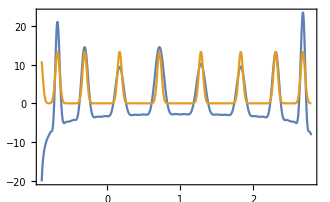

```mathematica
Plot[{Re@KPMfunc[kpm,ϵ],dos},{ϵ,-0.9,2.8}]//Quiet
```

#### Random approximations to the trace

```mathematica
RandomTraceApproximation[R_,H_]:=Module[{rs},
rs = RandomVariate[NormalDistribution[0,1],{R,Length@H}]+ⅈ RandomVariate[NormalDistribution[0,1],{R,Length@H}];

{Tr[H],(Length@H)/R Total@Table[(r*.H.r)/(r*.r),{r,rs}]}//Chop

]
```

```mathematica
h = RandomReal[{-3,3},{7,7}];
h = h + hᵀ;
h = RescaleHamiltonian[h];
RandomTraceApproximation[100,h]
```

{-0.802274,-0.855538}

```mathematica
h = RandomReal[{-3,3},{7,7}];
h = h + hᵀ;
h = RescaleHamiltonian[h];
th = 2 MatrixPower[h,2]-Eye[Length@h];
RandomTraceApproximation[100,th]
```

{-1.73676,-1.75453}

#### Ex: XXZ with staggered field

Based on https://arxiv.org/pdf/2103.16601.pdf

```mathematica
Clear[Δ,h,H,ψ0,XXZstag]
LoadSpinChainMatrices[L=7];
Δ = 0.55;
h = 1.0;
a=2.0;
ω0 = 8.0;
XXZstag[Δ_,h_] :=Module[{H,e0},
H=Sum[sx[i].sx[i+1]+sy[i].sy[i+1] + Δ sz[i].sz[i+1],{i,1,L-1}]+h Sum[sz[i],{i,1,L,2}];
e0 = Eigvals[H,1]⟦1⟧;
H-e0 NEye[Length@H]]
```

```mathematica
H = XXZstag[Δ,h];
ψ0 = Eigvecs[H,1]//Flatten;
f = Function[{t,ψ},-ⅈ (H + a Sin[ω0 t] sz[4]).ψ];
ψ=RK4t[f,ψ0,0.005,100 π/ω0]⟦-1,2⟧;
```

```mathematica
P = Module[{ϵ,v},
{ϵ,v} = Eigsys[H];
Table[{ϵ⟦k⟧,Abs[v⟦All,k⟧*.ψ]^2},{k,Length@ϵ}]]//Quiet//Chop;
```

```mathematica
SeedRandom[1];
PrettyTiming[kpm0=KPM[H,200,1000,out[ψ,ψ]];
kpm⟦1;;2⟧]
PrettyTiming[kpm=KPM[H,220,1000,out[ψ,ψ]];
kpm⟦1;;2⟧]
```

0h : 0m : 8s

{5.82077×10^-11,20.0435}

0h : 0m : 8s

{5.82077×10^-11,20.0435}

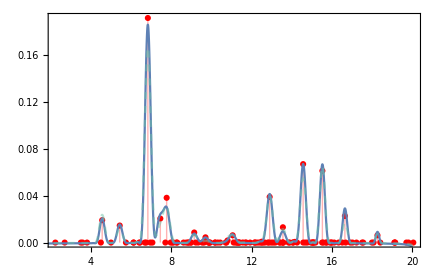

```mathematica
Show[
ListPlot[Rest@P,Filling->Axis,PlotMarkers->Automatic,PlotStyle->Red,PlotRange->All],
Plot[0.03 Re@KPMfunc[kpm,ϵ],{ϵ,0.1,20}],
Plot[0.03 Re@KPMfunc[kpm0,ϵ],{ϵ,0.1,20},PlotStyle->Directive[green,Dashed,Opacity[0.5]]],
ImageSize->600
]
```

## “Load” useful operators (Pauli matrices, fermionic and bosonic operators, &c.)

"Load" functions load into your system a set of matrices related to the problem at hand (qubits, fermions, bosons, etc.). 
Type "LoadedMatrices" to print which matrices are currently loaded.

### LoadPauliMatrices: Pauli matrices for a single qubit

```mathematica
Clear[LoadPauliMatrices];
LoadPauliMatrices[]:=Module[{},
Clear[σ0,σx,σy,σz,σp,σm,nn,GMAT,ϕ,θ];
σ0 = {{1,0},{0,1}};
σx = {{0,1},{1,0}};
σy = {{0,-I},{I,0}};
σz = {{1,0},{0,-1}};
σp = {{0,1},{0,0}}(*(σx + I σy)/2*);
σm = {{0,0},{1,0}}(*(σx - I σy)/2*);
(*nn = σp.σm; *)

GMAT = MatrixExp[-ⅈ ϕ σz/2].MatrixExp[-ⅈ θ σy/2];

LoadedMatrices="Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT";
];
```

```mathematica
LoadPauliMatrices[]
```

#### Example usage

```mathematica
LoadPauliMatrices[]
```

```mathematica
σx//mf;
```

(0 | 1
1 | 0)

```mathematica
(* Matrix diagonalizing an arbitrary direction in Bloch's sphere *)
GMAT//mf;
```

(ⅇ^(-(ⅈ ϕ)/2) Cos[θ/2] | -ⅇ^(-(ⅈ ϕ)/2) Sin[θ/2]
ⅇ^((ⅈ ϕ)/2) Sin[θ/2] | ⅇ^((ⅈ ϕ)/2) Cos[θ/2])

```mathematica
GMAT†.GMAT//cf//mf;
```

(1 | 0
0 | 1)

```mathematica
sigmaN = Sin[θ] Cos[ϕ] σx + Sin[θ] Sin[ϕ] σy + Cos[θ] σz;
G†.sigmaN.G//cf//mf;
```

(1 | 0
0 | -1)

### LoadSpinChainMatrices: Pauli matrices for a spin chain

Use LoadSpinChainMatrices[N,"a"] for symbolics

```mathematica
LoadSpinChainMatrices[𝒩_,type_:"n"]:=Module[{one,σ0,σx,σy,σz,σp,σm},

one = If[type=="n",1.0,1];
σ0 = SparseArray[one{{1,0},{0,1}}];
σx = SparseArray[one{{0,1},{1,0}}];
σy = SparseArray[one{{0,-I},{I,0}}];
σz =SparseArray[ one{{1,0},{0,-1}}];
σp =(σx + I σy)/2;
σm = (σx - I σy)/2;

Clear[eye,sp,sm,sx,sy,sz,c,cd];
eye = one Eye[2^𝒩];

If[𝒩>1,
Do[
eyeL = one Eye[2^(i-1)];
eyeR = one Eye[2^(𝒩-i)];
sx[i] = kron[eyeL,σx,eyeR];
sy[i] = kron[eyeL,σy,eyeR];
sz[i] = kron[eyeL,σz,eyeR];
sp[i] = kron[eyeL,σp,eyeR];
sm[i] = sp[i]ᵀ;
(*nn[i] = (eye+sz[i])/2//Chop;*)
c[i] = kron@@Join[Table[(-σz),{j,1,i-1}],{σm},Table[σ0,{j,i+1,𝒩}]];
cd[i] = c[i]†;

,{i,1,𝒩}],
(
sx[1] = σx;
sy[1] =σy;
sz[1] = σz;
sp[1] = σp;
sm[1] = σm;
c[1] = σm;
cd[1] = σp;)];


LoadedMatrices="Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, eye, sm, sp, sx, sy, sz, c, cd";

];
```

### LoadFermionicOperators: Fermionic operators & majoranas

Majorana definitions: 

Γ_(2n-1) = c_n+c_n^†
Γ_(2n)     = i (c_n^†-c_n)

{Γ_i,Γ_j} = 2 δ_ij

Relation to fermionic operators: 

Γ_1 Γ_2=-Γ_2 Γ_1 = i(cc† - c†c)     →    iΓ_1 Γ_2=2 c†c -1    →    c†c = i/2 Γ_1 Γ_2+1/2

For nearest neighbors: 

Γ_2 Γ_3 = i (c_1^†c_2^†-c_1 c_2) + i (c_1^†c_2+c_2^†c_1)  =  i σ_x^1 σ_x^2

Γ_1 Γ_4 = i (c_1^†c_2^†-c_1 c_2) - i (c_1^†c_2+c_2^†c_1)  = -i σ_y^1 σ_y^2

Thus

σ_x^1 σ_x^2+σ_y^1 σ_y^2 = -i (Γ_2 Γ_3-Γ_1 Γ_4)

```mathematica
Clear[LoadFermionicOperators];
LoadFermionicOperators[𝒩_,ord_:"local",type_:"n"]:=Module[{},

LoadSpinChainMatrices[𝒩,type];
Clear[sp,sm,sx,sy,sz];
Clear[Γ];
If[ord=="local",
Do[
Γ[2n-1] = c[n] + cd[n];
Γ[2n]= ⅈ (cd[n]-c[n]),
{n,1,𝒩}],
Do[
Γ[n] = c[n] + cd[n];
Γ[𝒩+n]= ⅈ (cd[n]-c[n]),
{n,1,𝒩}]
];

Clear[sp,sm,sx,sy,sz];
LoadedMatrices="Matrices loaded: eye, c, cd, Γ";
]
```

#### Example usage

```mathematica
LoadSpinChainMatrices[3]
```

```mathematica
LoadedMatrices
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, eye, sm, sp, sx, sy, sz, nn, c, cd

```mathematica
σx//mf;
```

(0. | 1.
1. | 0.)

```mathematica
sx[1]//mf;
```

(0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.)

```mathematica
sx[2]//mf;
```

(0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.)

```mathematica
(* Fermionic operators *)
c[3]//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0)

```mathematica
(* Now there are no more floating points *)
LoadSpinChainMatrices[3,"a"]
sx[2]//mf;
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

### LoadArbitrarySpinMatrices: Spin S operators

```mathematica
LoadArbitrarySpinMatrices[S_,type_:"n"]:=Module[{it,srange,tmp},

it=If[type=="a",1,1.0];
srange = Range[S,-S,-it];

Clear[Sz,Sp,Sm,Sx,Sy,S0];

Sz= SparseArray@DiagonalMatrix[srange];
Sp = SparseArray@Table[√((S-s)(S+s+1))KroneckerDelta[r,s+1],{r,srange},{s,srange}];
Sm = Spᵀ;
Sx = (Sp+Sm)/2;
Sy = (Sp-Sm)/(2I);

S0 =Eye[2S+1];


LoadedMatrices="Matrices loaded: S0 (=1), Sx, Sy, Sz, Sp, Sm";

];
```

#### Example usage

```mathematica
(* Spin 1 particle *)
LoadArbitrarySpinMatrices[1]
```

```mathematica
LoadedMatrices
```

Matrices loaded: S0 (=1), Sx, Sy, Sz, Sp, Sm

```mathematica
Sx//mf;
```

(0. | 0.707107 | 0.
0.707107 | 0. | 0.707107
0. | 0.707107 | 0.)

```mathematica
(* Spin 5/2 particle; symbolics *)
LoadArbitrarySpinMatrices[5/2,"a"]
```

```mathematica
Sx//mf;
```

(0 | (√5)/2 | 0 | 0 | 0 | 0
(√5)/2 | 0 | √2 | 0 | 0 | 0
0 | √2 | 0 | 3/2 | 0 | 0
0 | 0 | 3/2 | 0 | √2 | 0
0 | 0 | 0 | √2 | 0 | (√5)/2
0 | 0 | 0 | 0 | (√5)/2 | 0)

### LoadBosonicOperators: Bosonic operators

N is the size of the matrix: Fock space goes from |0⟩ to |N-1⟩.

```mathematica
LoadBosonicOperators[𝒩_,type_:"n"]:=Module[{one,tmp,n,m},
one = If[type=="a",1,1.0];
Clear[𝕀,a,X,P(*,CoherentState*)];
𝕀= Eye[𝒩];
a=one DiagonalMatrix[SparseArray[Table[√n,{n,1,𝒩-1}]],1];
𝕏 = 1/(√2)(a†+a);
ℙ = I/(√2)(a†-a);
CoherentState[α_]:=Exp[-Abs[α]^2/2] Table[α^n/(√(n!)),{n,0,𝒩-1}];
ThermalState[n0_]:=DiagonalMatrix@Table[n0^n (1+n0)^(-1-n),{n,0,𝒩-1}];
LoadedMatrices="Matrices loaded: 𝕀 (=1), a, 𝕏, ℙ, CoherentState[α], ThermalState[n0]";
]
```

#### Example usage

```mathematica
LoadBosonicOperators[10,"a"]
LoadedMatrices
```

Matrices loaded: 𝕀 (=1), a, X, P, ℕ

```mathematica
a//mf;
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
LoadBosonicOperators[10]
a†//mf;
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.41421 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.73205 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 2.23607 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 2.44949 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 2.64575 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.82843 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3. | 0.)

## Alternative versions of simple numerics

### Trapz: Cheap & crappy numerical integration

Silly trapezoidal rule for function integration.

```mathematica
Clear[Trapz];
Trapz[fs_,Δx_]:=Δx/2(fs⟦1⟧ + 2 Total[fs⟦2;;-2⟧] + fs⟦-1⟧);

Trapz::usage = "Trapz[fs,Δx] integrates the list fs using the trapezoidal rule, with step Δx";
```

#### Example usage

```mathematica
NIntegrate[Sin[x]^3,{x,0,0.7}]
```

0.0509645

```mathematica
Δx = 0.01;
list = Sin[range[0,0.7,Δx]]^3;
Trapz[list,Δx]
```

0.0509725

```mathematica
Δx = 0.005;
list = Sin[range[0,0.7,Δx]]^3;
Trapz[list,Δx]
```

0.0509665

```mathematica
Δx = 0.001;
list = Sin[range[0,0.7,Δx]]^3;
Trapz[list,Δx]
```

0.0509646

### BracketRoot & FindAllRoots: pre-bracketing roots within a given interval:

Brackets the roots of f(x). 
Very useful function in root finding.

Output is a list of intervals [a_i,b_i], such that f(x) is guaranteed to have a root inside.

```mathematica
Clear[BracketRoot];
BracketRoot[f_,xmin_,xmax_,npts_:1000]:=Module[{xrange,tab,par,roots,pos,xtab,x},
xrange=linspace[xmin,xmax,npts];
tab = f/@xrange;
par = {Range[1,Length@tab-1],Most[tab] Rest[tab]}ᵀ;
pos =Select[par,#⟦2⟧≤ 0.0&]⟦All,1⟧;
Table[{xrange⟦p⟧,xrange⟦p+1⟧},{p,pos}]
]

BracketRoot::usage = "BracketRoot[f,xmin,xmax] tries to bracket all roots of f(x) within the interval [xmin,xmax].";
```

```mathematica
Clear[FindAllRoots];
FindAllRoots[f_,xmin_,xmax_,npts_:1000]:=Module[{x,xtab},
xtab = BracketRoot[f,xmin,xmax,npts];
Table[x/.FindRoot[f[x],{x,xt⟦1⟧,xt⟦2⟧}],{xt,xtab}]
]

FindAllRoots::usage = "FindAllRoots[f,xmin,xmax] finds all roots of f(x) within the interval [xmin,xmax].";
```

#### Example usage

This is a function with roots at x = 0 and x ≈ 0.43. 
Using Mathematica’s FindRoot, one may get one root or the other, depending on where you start.
This is a big pain.

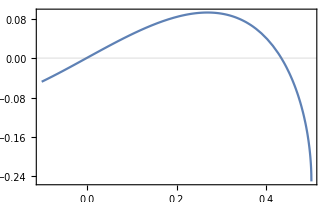

```mathematica
Clear[f];
f[x_] := x √(1-4 x^2)-x/2;
Plot[f[x],{x,-0.1,1/2},GridLines->{None,{0}}]
```

```mathematica
FindRoot[f[x],{x,0.1}]
FindRoot[f[x],{x,0.3}]
```

{x→-2.13961×10^-15}

{x→0.433013}

It is move convenient to bracket the roots before. 
i.e., one first determines intervals [a_i,b_i], inside which there is guaranteed to be a root.

```mathematica
brac=BracketRoot[f,0,1/2,100]
```

{{0.,0.00505051},{0.429293,0.434343}}

The actual position of the roots can now be determined using FindRoot and supplying the intervals as initial guesses.

```mathematica
FindRoot[f[x],{x,brac⟦1,1⟧,brac⟦1,2⟧}]
```

{x→0.}

```mathematica
FindRoot[f[x],{x,brac⟦2,1⟧,brac⟦2,2⟧}]
```

{x→0.433013}

FindAllRoots[] does that automatically: first brackets, then finds roots.

```mathematica
MultipleRoots[f,0,1/2,100]
```

{0.,0.433013}

### LegendreGauss: numerical integration in a sphere

For functions that depend only on θ: 

∫_0^π  f(θ) sin(θ) dθ = ∑_i w_i f(p_i)

For functions of θ,ϕ:

∫_0^(2π) dϕ ∫_0^π sin(θ) dθ f(θ,ϕ) = ∑_i w_i f(θ_i,ϕ_i)

```mathematica
Clear[LegendreGauss];
LegendreGauss[n_,prec_]:=Block[{roots,p,x,w},
roots=Solve[LegendreP[n,x]==0,x];
p=N[π/4(x+1)/.roots,prec];
w=(π/4)N[2(1-x^2)/((n+1)LegendreP[n+1,x])^2/.roots,prec];
{Join[p,p+π/2],Join[w Sin[p],w Sin[p+π/2]]}
];

LegendreGauss[nθ_,nϕ_,prec_]:=Block[{pθ,wθ,pϕ,wϕ,p,w},
{pθ,wθ} = LegendreGauss[nθ,prec];
pϕ = linspace[0,2π,nϕ];
wϕ = ConstantArray[(2π)/(nϕ-1),{nϕ}];  
p = Tuples[{pθ,pϕ}];
w = Times@@#&/@Tuples[{wθ,wϕ}];
{p,w}
]

LegendreGauss::usage = "Generates grid of (points,weights) for numerical integration in a sphere.";
```

#### Example usage

For integration of a function that only depends on θ:

```mathematica
(* Output is a list of (points,weights) *)
{p,w} = LegendreGauss[10,MachinePrecision]
```

{{0.668473,0.902324,0.44501,1.12579,0.251791,1.31901,0.105979,1.46482,0.0204938,1.5503,2.23927,2.47312,2.01581,2.69658,1.82259,2.8898,1.67678,3.03561,1.59129,3.1211},{0.143855,0.182148,0.0910359,0.190885,0.0428694,0.166644,0.0124164,0.11672,0.00107305,0.0523526,0.182148,0.143855,0.190885,0.0910359,0.166644,0.0428694,0.11672,0.0124164,0.0523526,0.00107305}}

```mathematica
(* Weird function *)
f[θ_]:=Cos[θ]^3.3 θ^2;
NIntegrate[f[θ] Sin[θ],{θ,0,π}]
f[p].w
```

-0.820751-1.25768 ⅈ

-0.820751-1.25768 ⅈ

For integration over the sphere (θ,ϕ), the syntax is the same, except that the points are now given as tuples (θ_i,ϕ_i). 
The correspondence is thus 

∫_0^(2π) dϕ ∫_0^π sin(θ) dθ f(θ,ϕ) = ∑_i w_i f(θ_i,ϕ_i)

```mathematica
(* Integration on θ,ϕ *)
{p,w}=ThetaPhiQuadrature[10,10,MachinePrecision];
```

```mathematica
Clear[f]
f[{θ_,ϕ_}]:=Cos[θ]^2 θ^2 Sin[ϕ]^2.2;
NIntegrate[f[{θ,ϕ}] Sin[θ],{θ,0,π},{ϕ,0,2π}]
(f[#]&/@p).w
```

6.16758+2.00397 ⅈ

6.16897+2.00442 ⅈ

Precision can be increased by increasing the number of points. 
Or one can also change MachinePrecision to another number

```mathematica
LegendreGauss[10,30]
```

{{0.668472530984266011469854691672,0.902323795810630607761466999968,0.445010216823424314597124473959,1.12578610997147230463419721768,0.251791136260741321809901259633,1.31900519053415529742142043201,0.105978983977506509750248854852,1.46481734281739010948107283679,0.0204937645792770232280713992446,1.5503025622156195960032502924,2.23926885777916263070117638331,2.47312012260552722699278869161,2.0158065436183209338284461656,2.69658243676636892386551890932,1.82258746305563794104122295127,2.88980151732905191665274212365,1.676775310772403128981570546492,3.03561366961228672871239452843,1.591290091374173642459393090884,3.12109888901051621523457198403},{0.14385538752309044885957303617,0.1821482346882985372549086829,0.091035865820022234120465153258,0.19088460570231520153832453701,0.042869357084832244193330384926,0.16664426881031131875686955118,0.012416414490632614636496831801,0.11672025914509963578847068992,0.0010730511780787534942954697879,0.052352555557319011357265657761,0.1821482346882985372549086829,0.14385538752309044885957303617,0.19088460570231520153832453701,0.091035865820022234120465153258,0.16664426881031131875686955118,0.042869357084832244193330384926,0.11672025914509963578847068992,0.0124164144906326146364968318,0.052352555557319011357265657761,0.001073051178078753494295469788}}

### RK4: manual Runge-Kutta 4, for silly things

Based on: https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta_methods

RK4:   input is a time-independent function f(x). 
RK4t: f(t,x)

```mathematica
Clear[RK4,RK4t];
(* For time-indeendent RHS f(y) *)
RK4[f_,y0_,Δt_,tf_]:=Module[{F},
F[y_]:=Block[{k1,k2,k3,k4},
k1 = f[y];
k2 = f[y + Δt k1/2];
k3 = f[y + Δt k2/2];
k4 = f[y+Δt k3];
y + Δt/6(k1+2k2+2k3+k4)
];
Transpose[{Range[0,tf,Δt],NestList[F,y0,Round[tf/Δt]]}]
]

(* for a time-dependent RHS f(t,y) *)
RK4t[f_,y0_,Δt_,tf_,output_:"full"]:=Module[{F},
F[{t_,y_}]:=Block[{k1,k2,k3,k4},
k1 = f[t,y];
k2 = f[t+Δt/2,y + Δt k1/2];
k3 = f[t+Δt/2,y + Δt k2/2];
k4 = f[t+Δt,y+Δt k3];
{t+Δt,y + Δt/6(k1+2k2+2k3+k4)}
];

If[output==="full",
NestList[F,{0,y0},Round[tf/Δt]],
Nest[F,{0,y0},Round[tf/Δt]]
]
]
```

#### Example usage

Time-independent qubit dynamics

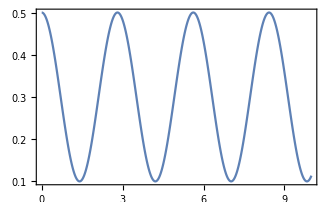

```mathematica
H = 1/2 σz+σx;
ψ0 = 1/(√2){1,1};
ψ=RK4[-ⅈ H.#&,ψ0,0.01,10];
ListLinePlot[{ψ⟦All,1⟧,Abs[ψ⟦All,2,2⟧]^2}ᵀ]
```

Schrodinger equation for a driven qubit

```mathematica
H = 1/2 σz + Cos[t] σx//mf;
```

(1/2 | Cos[t]
Cos[t] | -1/2)

```mathematica
Clear[f];
f[t_,y_]:=-ⅈ ({{1/2, Cos[t]}, {Cos[t], -1/2}}).y
```

```mathematica
ψ0 = 1/(√2){1,1};
ψ=RK4t[f,ψ0,0.01,10];
```

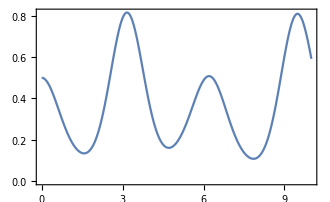

```mathematica
ListLinePlot[{ψ⟦All,1⟧,Abs[ψ⟦All,2,2⟧]^2}ᵀ]
```

Compare with Mathematica’s built in function

```mathematica
sol2 = NDSolveValue[{psi'[t]==-ⅈ  ({{1/2, Cos[t]}, {Cos[t], -1/2}}).psi[t],psi[0]==ψ0},psi,{t,0,10}];
```

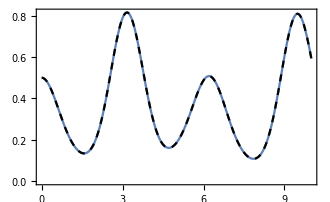

```mathematica
Show[
ListLinePlot[{ψ⟦All,1⟧,Abs[ψ⟦All,2,2⟧]^2}ᵀ],
Plot[Abs[sol2[t]⟦2⟧]^2,{t,0,10},PlotStyle->Directive[Black,Dashed]]]
```

#### RK4 for Schrödinger’s equation

```mathematica
Clear[H];
f[t_,y_]:=-ⅈ H y;
(RK4t[f,y,Δt,Δt]⟦2,2⟧)/y//Expand
```

1-ⅈ H Δt-(H^2 Δt^2)/2+1/6 ⅈ H^3 Δt^3+(H^4 Δt^4)/24

```mathematica
(RK4[-ⅈ H #&,y,Δt,Δt]⟦2⟧)/y//Expand
```

1-ⅈ H Δt-(H^2 Δt^2)/2+1/6 ⅈ H^3 Δt^3+(H^4 Δt^4)/24

### Gram-Chalier-Edgeworth approximation of nearly Gaussian probability distributions

```mathematica
GramChalierEdgeworth[cumulants_]:=Module[{d = Length@cumulants,μ,σ,κlist,Bn},
μ = cumulants⟦1⟧;
σ = √cumulants⟦2⟧;
κlist = Join[{0,0},cumulants⟦3;;-1⟧];
Bn = Table[Sum[BellY[n,k,κlist],{k,1,n}],{n,3,d}];

Function[1/(√(2π σ^2))Exp[-(#-μ)^2/(2 σ^2)] (1 + Sum[1/(n!σ^n)Bn⟦n-2⟧ 2^(-n/2)HermiteH[n,(#-μ)/(σ √2)],{n,3,d}])] 

(*1/(√(2π σ^2))Exp[-(x-μ)^2/(2 σ^2)] (1 + Sum[1/(n!σ^n)Bn⟦n-2⟧ 2^(-n/2)HermiteH[n,(x-μ)/(σ √2)],{n,3,d}])*)
]
```

#### Example

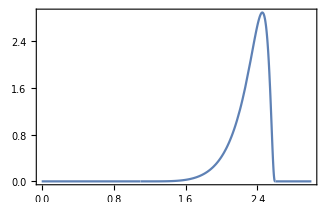

```mathematica
p=JohnsonDistribution["SB", -2,1.2,1.1,1.5];
Plot[PDF[p,x],{x,0,3}]
```

```mathematica
cumulants = Table[Cumulant[p,n],{n,1,30}]
```

{2.31925,0.0325114,-0.00707345,0.00166633,-0.000179148,-0.000219636,0.000250069,-0.000145431,3.02284×10^-6,0.000118885,-0.000171368,0.000111957,0.0000770668,-0.000345977,0.000514536,-0.000228521,-0.000937044,0.00295942,-0.00409383,-0.000980908,0.0209836,-0.0568379,0.0613496,0.139653,-0.865989,2.04755,-0.85214,-13.6282,60.952,-117.656}

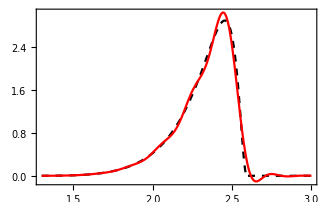

```mathematica
papprox= GramChalierEdgeworth[cumulants⟦1;;30⟧];
Plot[{PDF[p,x],papprox[x]},{x,1.3,3},PlotStyle->{Directive[Black,Dashed],Red,Blue}]
```

### SillySample: sample (inefficiently) from any probability distribution

```mathematica
(* The Ps do not have to be normalised *)
Clear[SillySample];
SillySample[Ps_,xs_,nsamp_:1]:=If[nsamp===1,RandomChoice[Ps->xs],RandomChoice[Ps->xs,nsamp]]
```

#### Example usage

Sample the equilibrium distribution of a classical anharmonic oscillator

```mathematica
m = 1;
ω = 1;
Ω = 1.;
T = 1;
xs = range[-5,5,0.02];
Ps = Table[Exp[-(1/2 m ω^2 x^2+1/4 Ω x^4)],{x,xs}];
```

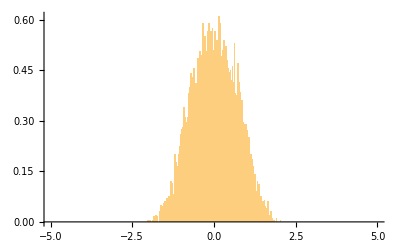

```mathematica
samp = SillySample[Ps,xs,10^4];
Histogram[samp,{-5,5,0.02},"PDF"]
```

Compare with the exact distribution

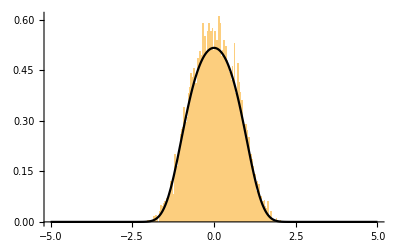

```mathematica
Z = NIntegrate[Exp[-(1/2 m ω^2 x^2+1/4 Ω x^4)],{x,-∞,∞}];

Show[
Histogram[samp,{-5,5,0.02},"PDF"],
Plot[1/Z Exp[-(1/2 m ω^2 x^2+1/4 Ω x^4)],{x,-5,5},PlotStyle->Black]]
```

Multidimensional distributions: Sample both x and p

```mathematica
Clear[prob];
prob[{x_,p_}]:=Exp[-(p^2/(2m)+1/2 m ω^2 x^2+1/4 Ω x^4)];
xs = range[-10,10,0.1];
ps = range[-10,10,0.1];
xps = Tuples[{xs,ps}];
Ps = prob[#]&/@xps;
samp = SillySample[Ps,xps,10^4];
Histogram3D[samp]
```

-Graphics3D-

#### Comparison with built in samplers

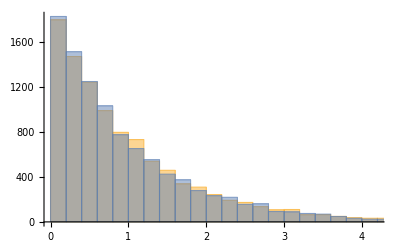

```mathematica
Clear[x,P];

rand1 = RandomVariate[ExponentialDistribution[1],10^4];
xs = range[0,20,0.02];
rand2 = SillySample[Exp[-xs],xs,10^4];
Histogram[{rand2,rand1}]
```

```mathematica
PairedHistogram[rand1,rand2]
```

-Graphics-

### TwoPointCorrelation: computes 1/N∑_(i =1)^(N -h) (x_i-μ)(x_(i+1)-μ)

This is analogous to Mathematica’s CovarianceFunction, but somehow is much faster.

```mathematica
Clear[TwoPointCorrelation];
TwoPointCorrelation[data_,hmax_,dt_:None,steps_:1]:=Module[{𝒩=Length@data,ave = Mean[data],vec1,M,corr},
vec1 = data⟦1;;𝒩-hmax⟧;
M = Table[data⟦1+i;;𝒩-hmax+i⟧,{i,1,hmax,steps}];
corr=1/𝒩(M.vec1-ave^2);
If[dt===None,corr,{dt Range[1, hmax,steps],corr}ᵀ]
]
```

### FourierWithFreqs & Power Spectrum: Computes the FFT and the power spectrum with the actual frequencies in the horizontal axis

```mathematica
Clear[FourierWithFreqs];
FourierWithFreqs[x_,dt_,transform_:Fourier]:=Module[{d,xf,ωs,ωs2,hamm},
d = Length@x;
If[OddQ[d],d=d-1];
hamm = Table[1/2(1.0-Cos[(2π j)/d]),{j,0,d-1}];
xf = transform[x⟦1;;d⟧ hamm];
ωs = Range[0,d/2] (2π)/(d dt);
ωs2 = -Reverse@Drop[Drop[ωs,1],{-1}];
{Join[ωs2,ωs],Join[xf⟦d/2+2;;d⟧,xf⟦1;;d/2+1⟧]}ᵀ
]
```

```mathematica
Clear[PowerSpectrum];
PowerSpectrum[x_,dt_,averaging_:1,overlap_:0.3]:=Module[{d,xf,ωs,hamm,S,k,xs,Ss},
d = Length@x;
If[OddQ[d],d=d-1];

k=If[averaging==1,d,(2d)/(2averaging-1)//Floor]; 
If[OddQ[k],k=k-1];

(*hamm = Table[1/2(1.0-Cos[(2π j)/k]),{j,0,k-1}]; *)

ωs = Range[1,k/2] (2π)/(k dt); 
ωs = Join[-Reverse@Drop[ωs,{-1}],ωs];

xs  = Partition[x,k,Floor[overlap k]];

xf = Table[Fourier[(*hamm*)(xx⟦1;;k⟧-Mean[xx])],{xx,xs}]; 
S = Mean@Table[dt Abs[xxf]^2,{xxf,xf}];      

{ωs,Join[S⟦k/2+2;;k⟧,S⟦2;;k/2+1⟧]}ᵀ  
]
```

#### Example usage

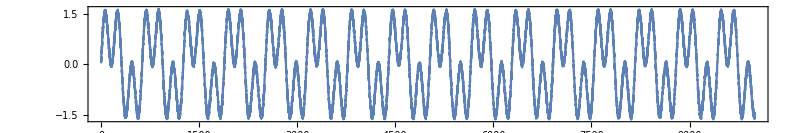

```mathematica
dt = 0.01;
𝒩 = 10000;
data = Table[Sin[n dt] + Sin[3 n dt],{n,1,𝒩}] + RandomReal[{-0.1,0.1},𝒩];
ListLinePlot[data,AspectRatio->1/6,ImageSize->800]
```

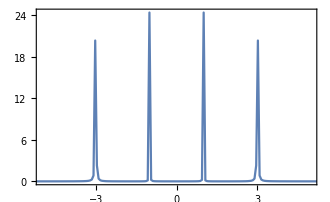

```mathematica
ListLinePlot[PowerSpectrum[data,dt],PlotRange->{{-5,5},All}]
```

#### Comparison with Mathematica’s PowerSpectralDensity

```mathematica
proc=ARMAProcess[1,{.5},{.3},1];
data=RandomFunction[proc,{500}];
```

```mathematica
sd=PowerSpectralDensity[data,w];
sd2 = PowerSpectrum[data["Values"],1,1];
```

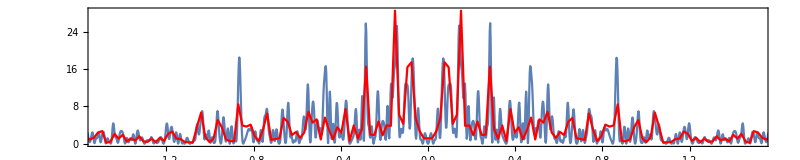

```mathematica
Show[
Plot[{sd},{w,-π,π},PlotRange->All],
ListLinePlot[sd2,PlotStyle->{Red},PlotRange->All],
AspectRatio->1/5,ImageSize->800,
PlotRange->{{-1.5,1.5},All}
]
```

### butter: Butterworth Filter

Based on https://mathematica.stackexchange.com/questions/46500/data-filtering-using-butterworth-filter

```mathematica
Clear[butter];
butter[data_,ωc_,dt_:1,order_:2]:=Module[{f,b},
f=RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass",order,ωc }],dt],data];
b=RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass",order,ωc }],dt],Reverse[data]];
(f+Reverse[b])/2
]
```

#### Example usage

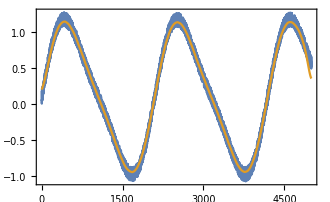

```mathematica
dt = 0.01;
ts = range[0,50,dt];
data = Table[Sin[0.3 t] + 0.2 Sin[0.6 t],{t,ts}]+0.2 RandomReal[{0,1},Length@ts];
filt = butter[data,2,dt];
ListLinePlot[{data,filt}]
```

## Quantum theory, information & thermodynamics

## Important Hamiltonians, unitary dynamics

### Tight-binding Hamiltonian

```mathematica
Clear[TightBindingHamiltonian];
TightBindingHamiltonian[V_,L_,J_]:=J StiffnessMatrix[L] + Which[
ArrayQ[V],DiagonalMatrix@SparseArray[Flatten[Table[V,{Ceiling[L/Length@V]}]]⟦1;;L⟧],
True,toeplitzMatrix[V,1,L]
];

TightBindingHamiltonian[V_,L_]:=TightBindingHamiltonian[V,L,1];
TightBindingHamiltonian[L_]:=TightBindingHamiltonian[1,L];
```

```mathematica
Clear[TightBindingHamiltonianPBC];
TightBindingHamiltonianPBC[V_,L_,J_]:=J CirculantMatrix[L] + Which[
ArrayQ[V],DiagonalMatrix@SparseArray[Flatten[Table[V,{Ceiling[L/Length@V]}]]⟦1;;L⟧],
True,toeplitzMatrix[V,1,L]
]

TightBindingHamiltonianPBC[V_,L_]:=TightBindingHamiltonianPBC[V,L,1];
TightBindingHamiltonianPBC[L_]:=TightBindingHamiltonianPBC[1,L];
```

### Majorana representation of quadratic fermionic models

Majorana operators are defined as 

Γ_n^1 = c_n+c_n^†
Γ_n^2     = i (c_n^†-c_n)

Hamiltonian: 
H = ∑_(n,m) h_nm c_n^†c_m + 1/2(G_nm c_n^†c_m^†+ G_mn^* c_n c_m)  = 1/4 Γ† 𝒯 Γ + 1/2 tr(h)

Ordering the operators as Γ = (Γ_1^1,...,Γ_L^1,Γ_1^2,...,Γ_L^2) yields

 𝒯=σ_z ⊗ (G+G†)/2   -  σ_y⊗ h -σ_x⊗ i((G-G†)/2) =((G+G†)/2 | i h - i/2(G-G†)
-i h - i/2(G-G†) | -((G+G†)/2))  
 
The function below uses instead the “local” ordering  Γ = (Γ_1^1,Γ_1^2,...,Γ_L^1,Γ_L^2), so that  𝒯 becomes 

𝒯= (G+G†)/2 ⊗ σ_z  - h ⊗ σ_y - i((G-G†)/2)⊗σ_x

```mathematica
Clear[MajoranaHamiltonian,MajoranaTightBinding];
MajoranaHamiltonian[h_,G_:0,ord_:"global"]:=
If[ord==="local",If[MatrixQ[h],-kron[h,({{0, -ⅈ}, {ⅈ, 0}})],0] +If[MatrixQ[G],- ⅈ kron[(G-G†)/2,({{0, 1}, {1, 0}})],0] +If[MatrixQ[G], kron[(G+G†)/2,({{1, 0}, {0, -1}})],0] ,
If[MatrixQ[h],-kron[({{0, -ⅈ}, {ⅈ, 0}}),h],0] +If[MatrixQ[G],- ⅈ kron[{{0,1},{1,0}},(G-G†)/2],0] +If[MatrixQ[G], kron[{{1,0},{0,-1}},(G+G†)/2],0]  ] 

MajoranaTightBinding[V_,L_,ord_:"local"]:=MajoranaHamiltonian[TightBindingHamiltonian[V,L,ord],0]

Clear[MajoranaXY];
MajoranaXY[L_,h0_,κ_]:=Module[{Δ},
Δ=h0 Eye[L]+ SparseArray[{Band[{1,2}]->(1-κ)/2(*Jy*),Band[{2,1}]->(1+κ)/2(*Jx*)},{L,L}] ;
ⅈ ArrayFlatten[({{0, -Δ}, {Δ†, 0}})]]
```

#### Example usage

```mathematica
L = 3;
A = RandomReal[{-1,1},{L,L}];
A = A + Aᵀ;
B = RandomReal[{-1,1},{L,L}];
B = B - Bᵀ//mf;
```

(0 | 1.0372 | -0.824736
-1.0372 | 0 | -0.242994
0.824736 | 0.242994 | 0)

```mathematica
LoadFermionicOperators[L,"global"];
H1 = Sum[A⟦n,m⟧ cd[n].c[m] + 1/2 B⟦n,m⟧ (cd[n].cd[m]-c[n].c[m]),{n,L},{m,L}]//mf;
```

(4.13236 | 0 | 0 | -0.242994 | 0 | 0.824736 | 1.0372 | 0
0 | 2.2156 | -0.173855 | 0 | -1.017 | 0 | 0 | 1.0372
0 | -0.173855 | 3.84144 | 0 | 0.513014 | 0 | 0 | -0.824736
-0.242994 | 0 | 0 | 1.92468 | 0 | 0.513014 | 1.017 | 0
0 | -1.017 | 0.513014 | 0 | 2.20768 | 0 | 0 | -0.242994
0.824736 | 0 | 0 | 0.513014 | 0 | 0.290919 | -0.173855 | 0
1.0372 | 0 | 0 | 1.017 | 0 | -0.173855 | 1.91676 | 0
0 | 1.0372 | -0.824736 | 0 | -0.242994 | 0 | 0 | 0)

```mathematica
h2 = MajoranaHamiltonian[A,B,"global"];
H2 =1/2 Tr[A] Eye[8]+ 1/4 Sum[h2⟦k,l⟧ Γ[k].Γ[l],{k,2L},{l,2L}]//mf;
```

(4.13236 | 0 | 0 | -0.242994 | 0 | 0.824736 | 1.0372 | 0
0 | 2.2156 | -0.173855 | 0 | -1.017 | 0 | 0 | 1.0372
0 | -0.173855 | 3.84144 | 0 | 0.513014 | 0 | 0 | -0.824736
-0.242994 | 0 | 0 | 1.92468 | 0 | 0.513014 | 1.017 | 0
0 | -1.017 | 0.513014 | 0 | 2.20768 | 0 | 0 | -0.242994
0.824736 | 0 | 0 | 0.513014 | 0 | 0.290919 | -0.173855 | 0
1.0372 | 0 | 0 | 1.017 | 0 | -0.173855 | 1.91676 | 0
0 | 1.0372 | -0.824736 | 0 | -0.242994 | 0 | 0 | 0)

```mathematica
H1-H2//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
L = 3;
A = RandomReal[{-1,1},{L,L}];
A = A + Aᵀ;
B = RandomReal[{-1,1},{L,L}]+  0.7 ⅈ RandomReal[{-1,1},{L,L}];
(*B = B - Bᵀ//mf;*)
```

```mathematica
LoadFermionicOperators[L];
H1 = Sum[A⟦n,m⟧ cd[n].c[m] + 1/2(B⟦n,m⟧  cd[n].cd[m] +B⟦n,m⟧* c[m].c[n]),{n,L},{m,L}]//mf;
(*H1-H1†//mf;*)
```

(0.578638 | 0 | 0 | -0.211042+0.174333 ⅈ | 0 | 0.0422996-0.454581 ⅈ | -0.412141-0.169111 ⅈ | 0
0 | -0.969544 | -1.0156 | 0 | 1.92143 | 0 | 0 | -0.412141-0.169111 ⅈ
0 | -1.0156 | 1.95088 | 0 | 1.83976 | 0 | 0 | -0.0422996+0.454581 ⅈ
-0.211042-0.174333 ⅈ | 0 | 0 | 0.402697 | 0 | 1.83976 | -1.92143 | 0
0 | 1.92143 | 1.83976 | 0 | 0.175941 | 0 | 0 | -0.211042+0.174333 ⅈ
0.0422996+0.454581 ⅈ | 0 | 0 | 1.83976 | 0 | -1.37224 | -1.0156 | 0
-0.412141+0.169111 ⅈ | 0 | 0 | -1.92143 | 0 | -1.0156 | 1.54818 | 0
0 | -0.412141+0.169111 ⅈ | -0.0422996-0.454581 ⅈ | 0 | -0.211042-0.174333 ⅈ | 0 | 0 | 0)

```mathematica
(*MajoranaHamiltonian2[A_,B_:0]:=If[MatrixQ[A],-kron[A,σy],0] +If[MatrixQ[B],- ⅈ kron[(B-B†)/2,σx],0] +If[MatrixQ[B], kron[(B+B†)/2,σz],0]  *)
h2 = MajoranaHamiltonian[A,B];
H2 =1/2 Tr[A] Eye[8]+1/4 Sum[h2⟦k,l⟧ Γ[k].Γ[l],{k,2L},{l,2L}]//mf;
```

(0.578638 | 0 | 0 | -0.211042+0.174333 ⅈ | 0 | 0.0422996-0.454581 ⅈ | -0.412141-0.169111 ⅈ | 0
0 | -0.969544 | -1.0156 | 0 | 1.92143 | 0 | 0 | -0.412141-0.169111 ⅈ
0 | -1.0156 | 1.95088 | 0 | 1.83976 | 0 | 0 | -0.0422996+0.454581 ⅈ
-0.211042-0.174333 ⅈ | 0 | 0 | 0.402697 | 0 | 1.83976 | -1.92143 | 0
0 | 1.92143 | 1.83976 | 0 | 0.175941 | 0 | 0 | -0.211042+0.174333 ⅈ
0.0422996+0.454581 ⅈ | 0 | 0 | 1.83976 | 0 | -1.37224 | -1.0156 | 0
-0.412141+0.169111 ⅈ | 0 | 0 | -1.92143 | 0 | -1.0156 | 1.54818 | 0
0 | -0.412141+0.169111 ⅈ | -0.0422996-0.454581 ⅈ | 0 | -0.211042-0.174333 ⅈ | 0 | 0 | 0)

```mathematica
H1-H2//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Non-interacting Hamiltonians and quasi-periodic sequences

```mathematica
(* Subscript[λ, c] = 2 *)
Clear[AubryAndreHarper];
AubryAndreHarper[L_,ϕ_:0,α_:0]:=Table[Cos[ 2.0π GoldenRatio n + ϕ]/(1-α Cos[2π GoldenRatio n + ϕ]),{n,1,L}];
```

```mathematica
Clear[FibonacciString];
FibonacciString[L_]:=Table[IntegerPart[(n+1)1/GoldenRatio^2]-IntegerPart[n 1/GoldenRatio^2],{n,1,L}];

FibonacciString[L_,a_,b_]:=FibonacciString[L]/.{0->a,1->b}
```

Based on https://arxiv.org/pdf/1803.03609.pdf

```mathematica
SSHHamiltonian[L_,τ0_,δτ_,ϵ_:1]:= Module[{hop = Table[τ0-(-1)^j δτ,{j,1,L-1}]},
- ϵ DiagonalMatrix[ConstantArray[ϵ,L]]  + DiagonalMatrix[hop,1] + DiagonalMatrix[hop,-1]//SparseArray
]
```

#### Example usage

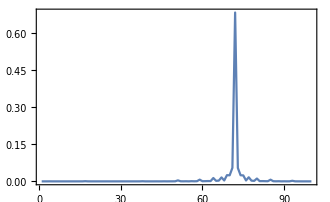

```mathematica
h = TightBindingHamiltonian[2.1AubryAndreHarper[100],100];
ψ = Eigvecs[h,1]⟦All,1⟧;
ListLinePlot[Abs[ψ]^2,PlotRange->All]
```

### ! UnitaryDynamics

```mathematica
Clear[UnitaryDynamics];
UnitaryDynamics[Hs_,fs_,dt_,τ_,y0_:"id",method_:"Trotter",output_:"reduced"]:=Module[{d=Length@fs,F,t,Y0,res,ntrotter},
If[method==="Trotter",
(
ntrotter = Round[τ/dt];
res=If[y0==="id",
If[output==="reduced",
Nest[{#⟦1⟧+dt,MatrixExp[-ⅈ dt Total@Table[fs⟦i⟧[#⟦1⟧+dt/2]Hs⟦i⟧,{i,d}]].#⟦2⟧}&,{0,Eye[Length@Hs⟦1⟧]},ntrotter],
NestList[{#⟦1⟧+dt,MatrixExp[-ⅈ dt Total@Table[fs⟦i⟧[#⟦1⟧+dt/2]Hs⟦i⟧,{i,d}]].#⟦2⟧}&,{0,Eye[Length@Hs⟦1⟧]},ntrotter]
],
If[output==="reduced",
Nest[{#⟦1⟧+dt,MatrixExp[-ⅈ dt Total@Table[fs⟦i⟧[#⟦1⟧+dt/2]Hs⟦i⟧,{i,d}],#⟦2⟧]}&,{0,y0},ntrotter],
NestList[{#⟦1⟧+dt,MatrixExp[-ⅈ dt Total@Table[fs⟦i⟧[#⟦1⟧+dt/2]Hs⟦i⟧,{i,d}],#⟦2⟧]}&,{0,y0},ntrotter]
]]),
(
Y0=If[y0==="id",Eye[Length@Hs⟦1⟧],y0];
F[t_,y_]:=-ⅈ Total@Table[fs⟦i⟧[t]Hs⟦i⟧.y,{i,d}];
res=RK4t[F,Y0,dt,τ,output]
)];
If[output==="reduced",Last@res,res]
]
```

```mathematica
UnitaryDynamicsTroterized[Hlist_,ψ0_,dt_]:=Module[{ψ=ψ0},Table[ψ=MatrixExp[-ⅈ H dt,ψ],{H,Hlist}]]
```

#### Example usage

```mathematica
Hs={σz,σx};
fs={Function[t,1/2],Function[t,Cos[t]]};
UnitaryDynamics[Hs,fs,0.01,10.,"id","RK4"]
UnitaryDynamics[Hs,fs,0.01,10.,"id","Trotter"]
```

{{0.223573+0.234591 ⅈ,-0.848373+0.418624 ⅈ},{0.848373+0.418624 ⅈ,0.223573-0.234591 ⅈ}}

{{0.223564+0.234579 ⅈ,-0.848379+0.418622 ⅈ},{0.848379+0.418622 ⅈ,0.223564-0.234579 ⅈ}}

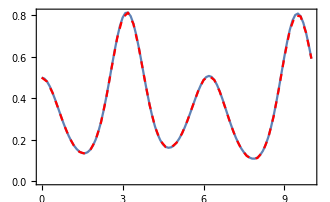

```mathematica
ψ0 = 1/(√2){1.,1.};
ψ=UnitaryDynamics[Hs,fs,0.1,10.,ψ0,"RK4","full"];
ψ2 = UnitaryDynamics[Hs,fs,0.2,10.,ψ0,"Trotter","full"];
Show[
ListLinePlot[{ψ⟦All,1⟧,Abs[ψ⟦All,2,2⟧]^2}ᵀ],
ListLinePlot[{ψ2⟦All,1⟧,Abs[ψ2⟦All,2,2⟧]^2}ᵀ,PlotStyle->Directive[Red,Dashed]]
]
```

### CounterDiabaticHamiltonian

Given a time-dependent Hamiltonian H(t)=∑_n E_n(t) |ψ_n(t)⟩⟨ψ_n(t)|, computes the counter-diabatic Hamiltonian used in shortcuts to adiabaticity:

H_CD(t) = i ∑_n |∂_t ψ_n⟩⟨ψ_n|

Input: 
- H(t) as a function
- final time t_f
- time step dt
Output: 
- {H(t), H_CD} , with each given as a list evaluated at times 0,dt,2dt,...,t_f.

```mathematica
Clear[CounterDiabaticHamiltonian];
CounterDiabaticHamiltonian[Hs_,tf_,dt_]:=Module[{Hbare,T,Vs,HCD,hcd,V},

Hbare = Table[Hs[t],{t,0,tf,dt}];
T = Length@Hbare;

Vs=Normal@Table[
V=Eigvecs[Hbare⟦n⟧];
(Vᵀ Exp[ⅈ Arg[V⟦1⟧]])ᵀ  (* fixes so that eigenvectors always have the same phases *)
,{n,T}];

HCD =  Table[
hcd=ⅈ((Vs⟦n+1⟧-Vs⟦n-1⟧)/(2dt)).Vs⟦n⟧†; 
(hcd+hcd†)/2,{n,2,T-1}];

HCD=Join[{0 Hbare⟦1⟧},HCD,{0 Hbare⟦1⟧}];
{Hbare,HCD}

]
```

#### Example usage: Landau-Zener avoided crossing with a linear ramp

```mathematica
Clear[H];
τQ=10^1;
Δ0=-5.;
Δd=10.;
ω0=0.5;

H[t_] := 1/2(ω0 σx+ (Δ0+Δd t/τQ) σz)
ψ0 = GroundState[H[0]];

(* Generate the Hamiltonians *)
{Hbare,HCD} = CounterDiabaticHamiltonian[H,τQ,dt=1/300];
```

```mathematica
(* Simulate unitary dynamics with the Bare Hamiltonian, and compute fidelity with ground state. *)
ψbare = UnitaryDynamicsTroterized[Hbare,ψ0,dt];
fidBare=Table[Abs[GroundState[H[(n-1) dt]]*.ψbare⟦n⟧]^2,{n,1,Length@ψbare}];
```

```mathematica
(* Include counter-diabatic driving *)

ψCD = UnitaryDynamicsTroterized[Hbare + HCD,ψ0,dt];
fidCD=Table[Abs[GroundState[H[(n-1) dt]]*.ψCD⟦n⟧]^2,{n,1,Length@ψCD}];
```

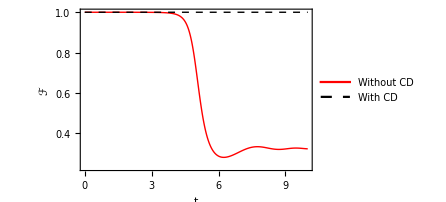

```mathematica
ListLinePlot[{fidBare,fidCD},DataRange->{0,τQ},PlotRangePadding->{None,0.05},PlotStyle->{{Thick,Red},{Thick,Black,Dashed}},FrameLabel->{"t","ℱ"},
PlotLegends->legend[{"Without CD","With CD"},{0.25,0.35}]
]
```

#### Original version of the code

```mathematica
CounterDiabaticHamiltonianOriginal[Hs_,tf_,dt_]:=
Module[
{timeinterval,ℋbares,vectors,e,v,ℋCD,ℋCDUpper,ℋCDLower,d = Length@Normal@Hs[0],vecs,dvecs,T,resultℋCD,orderi,orderedEi,orderedV,normV,val,vec,Eigenvals,Eigenvecs},

(*time interval*)
timeinterval=Table[j,{j,0,tf,dt}];
T=Length@timeinterval;

(*Bare Hamiltonians H0 and their ORDERED and normalized eigenvalues/eigenvectors*)
ℋbares=Table[Normal@Hs[tp],{tp,timeinterval}];
Eigenvecs=Range[T];
Do[Eigenvecs[[i]]=Eigvecs[ℋbares[[i]]]//Chop,{i,T}];

(*The following part removes the global phase fluctuations due to Mathematica Eigensystem*)
Do[
Do[
If[Eigenvecs[[i,j,1]]>0,Eigenvecs[[i,j]]=Eigenvecs[[i,j]],Eigenvecs[[i,j]]=-Eigenvecs[[i,j]]];
,{j,1,d}]
,{i,1,T}];

(*Conctruction of the time interpolated eigenvectors and their derivatives*)
vectors=Table[Interpolation[Table[{timeinterval[[i]],Eigenvecs[[i,j,k]]},{i,T}]],{j,1,d},{k,1,d}];
vecs=Table[Table[vectors[[j,k]][tp],{j,1,d},{k,1,d}],{tp,timeinterval}];
dvecs=Table[Table[vectors[[j,k]]'[tp],{j,1,d},{k,1,d}],{tp,timeinterval}];

(*Counterdiabatic Hamiltonian -- We enforce hermitianity since it is useful for the LMG model at high number of spins, where this property seems to break*)
ℋCD=Table[ⅈ*Sum[KETBRA[dvecs[[i,j]],vecs[[i,j]]]//Chop,{j,d}],{i,T}];
{Table[ℋbares[[i]]+(ℋCD[[i]]+ℋCD[[i]]†)/2,{i,T}],Table[(ℋCD[[i]]+ℋCD[[i]]†)/2,{i,T}]}
];
```

```mathematica
{Hbare2,HCD2}=CounterDiabaticHamiltonian[Function[t,1/2(ω0 PauliMatrix[1]+LinearRamp[t]* PauliMatrix[3])],0.1,dt];
{Hbare,HCD}=Chop@CounterDiabaticHamiltonianOriginal[Function[t,1/2(ω0 PauliMatrix[1]+LinearRamp[t]* PauliMatrix[3])],0.1,dt];
```

```mathematica
Hbare2⟦10⟧//mf;
```

(-2.485 | 0.25+0.0100197 ⅈ
0.25-0.0100197 ⅈ | 2.485)

```mathematica
Hbare⟦10⟧//mf;
```

(-2.485 | 0.25+0.0100197 ⅈ
0.25-0.0100197 ⅈ | 2.485)

## Quantum information

### PTr: partial trace

You list what you want to trace: PTr[ρ,{1,4,5}] traces out subsystems 1, 4  and 5

Syntax: 
- Most general syntax is PTr[ρ,{1,4,5}, {d1,d2,d3,d4,d5}]
  
 -   PTr[ρ,{1,4,5}, d] = PTr[ρ,{1,4,5},{d,d,d,d,d}]

  -  PTr[ρ,{1,4,5}] = PTr[ρ,{1,4,5},{2,2,2,2,2}] (assumes qubits)

```mathematica
Clear[PTr]
PTr[ρ_,list_,locdimlist_]:=Module[{i,eye,v,L,n,tups,tab,𝒩},
n = Length@locdimlist;
Do[eye[l] = Eye[locdimlist⟦l⟧],{l,n}];

Do[v[l,i] = {eye[l]⟦i⟧}ᵀ,{l,n},{i,locdimlist⟦l⟧}];
tups = Tuples@Table[Range[1,l],{l,locdimlist⟦list⟧}];
tab = Table[
kron@@Table[If[MemberQ[list,l],v[l,j⟦Position[list,l]⟦1,1⟧⟧],eye[l]],{l,n}],{j,tups}];
Total@Table[(tab⟦i⟧)ᵀ.ρ.tab⟦i⟧,{i,Length@tab}]
];

PTr[ρ_,list_,locdim_?NumberQ]:= PTr[ρ,list,ConstantArray[locdim,Log[locdim, Length@ρ]]]

PTr[ρ_,list_]:=PTr[ρ,list,2];

PTr::usage = "Computes the partial trace of ρ over a list of subsystems";
```

#### Example usage

```mathematica
(* ρ = |Subscript[ψ, 1]⟩⟨Subscript[ψ, 1]|⊗|Subscript[ψ, 2]⟩⟨Subscript[ψ, 2]| *)
ψ1 = {1,1}//Normalize;
ψ2 = {2,ⅈ}//Normalize;
ρ = kron[out[ψ1,ψ1],out[ψ2,ψ2]]//mf;
```

(2/5 | -ⅈ/5 | 2/5 | -ⅈ/5
ⅈ/5 | 1/10 | ⅈ/5 | 1/10
2/5 | -ⅈ/5 | 2/5 | -ⅈ/5
ⅈ/5 | 1/10 | ⅈ/5 | 1/10)

```mathematica
PTr[ρ,{2}]//mf;
out[ψ1,ψ1]//mf;
```

(1/2 | 1/2
1/2 | 1/2)

(1/2 | 1/2
1/2 | 1/2)

```mathematica
PTr[ρ,{1}]//mf;
out[ψ2,ψ2]//mf;
```

(4/5 | -(2 ⅈ)/5
(2 ⅈ)/5 | 1/5)

(4/5 | -(2 ⅈ)/5
(2 ⅈ)/5 | 1/5)

```mathematica
(* PTr assumes in principle local dimension is d = 2. *)
(* If the dimensions are homogenous, pass out an extra number *)
ψ1 = {1,1,3}//Normalize;
ψ2 = {2,ⅈ,-3ⅈ}//Normalize;
ρ = kron[out[ψ1,ψ1],out[ψ2,ψ2]];
```

```mathematica
PTr[ρ,{2},3]//mf;
out[ψ1,ψ1]//mf;
```

(1/11 | 1/11 | 3/11
1/11 | 1/11 | 3/11
3/11 | 3/11 | 9/11)

(1/11 | 1/11 | 3/11
1/11 | 1/11 | 3/11
3/11 | 3/11 | 9/11)

```mathematica
PTr[ρ,{1},3]//mf;
out[ψ2,ψ2]//mf;
```

(2/7 | -ⅈ/7 | (3 ⅈ)/7
ⅈ/7 | 1/14 | -3/14
-(3 ⅈ)/7 | -3/14 | 9/14)

(2/7 | -ⅈ/7 | (3 ⅈ)/7
ⅈ/7 | 1/14 | -3/14
-(3 ⅈ)/7 | -3/14 | 9/14)

```mathematica
(* If each sub-system has a different dimension, pass out a list of dimensions *)
ψ1 = {1,1}//Normalize;
ψ2 = {1,2,3,4,5}//Normalize;
ρ = kron[out[ψ1,ψ1],out[ψ2,ψ2]];

PTr[ρ,{2},{2,5}]//mf;
out[ψ1,ψ1]//mf;
```

(1/2 | 1/2
1/2 | 1/2)

(1/2 | 1/2
1/2 | 1/2)

```mathematica
PTr[ρ,{1},{2,5}]//mf;
out[ψ2,ψ2]//mf;
```

(1/55 | 2/55 | 3/55 | 4/55 | 1/11
2/55 | 4/55 | 6/55 | 8/55 | 2/11
3/55 | 6/55 | 9/55 | 12/55 | 3/11
4/55 | 8/55 | 12/55 | 16/55 | 4/11
1/11 | 2/11 | 3/11 | 4/11 | 5/11)

(1/55 | 2/55 | 3/55 | 4/55 | 1/11
2/55 | 4/55 | 6/55 | 8/55 | 2/11
3/55 | 6/55 | 9/55 | 12/55 | 3/11
4/55 | 8/55 | 12/55 | 16/55 | 4/11
1/11 | 2/11 | 3/11 | 4/11 | 5/11)

### von Neumann & Rényi entropy

```mathematica
Clear[vonNeumann];
vonNeumann[ρ_,base_:ⅇ]:= Module[{eigs,func},
eigs = Eigenvalues[ρ];
func[x_]:= If[NumberQ[x]&&Re@x<10^-12,0,-x Log[base,x]];
Sum[func[eigs⟦i⟧],{i,1,Length@eigs}]
]

vonNeumann::usage = "von Neumann entropy S(ρ)";
```

```mathematica
Renyi[ρ_,α_,base_:ⅇ]:= Module[{eigs,func},
Which[
α ==1.0,vonNeumann[ρ],
α ==∞,-Log[base,Max@Eigenvalues[ρ]],
True,(eigs = Eigenvalues[ρ];
1/(1-α)Log[base,Sum[(eigs⟦i⟧)^α,{i,1,Length@eigs}]])]
]

Renyi::usage = "Renyi entropy S_α(ρ)";
```

#### Example usage

```mathematica
ρ = ({{0.3, 0.1}, {0.1, 0.7}});
vonNeumann[ρ]
Renyi[ρ,3]
```

0.589514

0.458145

```mathematica
Renyi[ρ,1] (* returns von Neumann *)
```

0.589514

```mathematica
Renyi[ρ,0]
```

0.693147

```mathematica
Renyi[ρ,∞]
```

0.323507

### Kullback-Leibler: Quantum relative entropy

```mathematica
(* D(ρ||σ) *)
KullbackLeibler[ρ_,σ_]:=Module[{S1,S2,λ,Q,log},

S1 = vonNeumann[ρ];
{λ,Q} = Eigensystem[σ];
Q = Qᵀ; 
log = DiagonalMatrix@Log[λ];
S2 = - Tr[Q†.ρ.Q.log];
-S1+S2//Chop
]
```

#### Example usage

```mathematica
ρ = ({{0.3, 0.1}, {0.1, 0.7}});
σ = ({{0.3, 0}, {0, 0.7}});
KullbackLeibler[ρ,σ]
```

0.0213498

```mathematica
ρ = ({{0.3, 0}, {0, 0.7}});
σ = ({{0.7, 0}, {0, 0.3}});
KullbackLeibler[ρ,σ]
```

0.338919

```mathematica
KullbackLeibler[ρ,ρ]
```

0.

### Mutual Information

Usage is similar to partial trace function.

```mathematica
Clear[MutualInformation];
MutualInformation[ρ_,{A_,B_},locdimlist_]:=Module[{ρA,ρB,ρAB,n},
n= Length@locdimlist;(* Number of sub-systems in this case *)
ρA = PTr[ρ,Complement[Range[n],Flatten@{A}],locdimlist];
ρB = PTr[ρ,Complement[Range[n],Flatten@{B}],locdimlist];
ρAB = PTr[ρ,Complement[Range[n],Flatten@Join[Flatten@{A},Flatten@{B}]],locdimlist];
Chop[vonNeumann[ρA]+vonNeumann[ρB]-vonNeumann[ρAB],10^-12]
];

(* When all subsystems have different dimensions *)
MutualInformation[ρ_,{A_,B_},locdim_?NumberQ]:= MutualInformation[ρ,{A,B},ConstantArray[locdim,Log[locdim, Length@ρ]]]

(* When all subsystems are qubits *)
MutualInformation[ρ_,{A_,B_}]:= MutualInformation[ρ,{A,B},ConstantArray[2,Log[2, Length@ρ]]]
```

#### Example usage

Usage is similar to partial trace function.

```mathematica
ψ = 1/(√2){1,0,0,1};
ρ = out[ψ,ψ];
MutualInformation[ρ,{1,2}]
MutualInformation[ρ,{1,2},2]
MutualInformation[ρ,{1,2},{2,2}]
```

2 Log[2]

2 Log[2]

2 Log[2]

```mathematica
(* 3 qubits *)
ψ = 1/(√2){1,0,0,1,0,0,1,0};
ρ = out[ψ,ψ];
MutualInformation[ρ,{1,2},2]
MutualInformation[ρ,{1,2},{2,2,2}]
```

Log[2]/2

Log[2]/2

### Concurrence & Entanglement of Formation

R = √(√ρ(σ_y⊗σ_y)ρ^*(σ_y⊗σ_y)√ρ)

```mathematica
Concurrence[ρ_]:=Module[{σy,ρt,ρsq,R,eigs},
σy = {{0,-ⅈ},{ⅈ,0}};
ρt = kron[σy,σy].ρ*.kron[σy,σy];
ρsq = MatrixPower[ρ,1/2];
R = MatrixPower[ρsq.ρt.ρsq,1/2];
eigs = Chop@Reverse@Sort@Eigenvalues[R];
Max[0,Re[eigs⟦1⟧-eigs⟦2⟧-eigs⟦3⟧-eigs⟦4⟧]]
];
```

```mathematica
EntanglementOfFormation[ρ_,b_:2]:=Module[{c,h},
h[x_]:=If[(x==0)||(x==1),0,-x Log[b,x]-(1-x)Log[b,1-x]];
c = Concurrence[ρ];
h[(1+√(1-c^2))/2]
]
```

#### Example usage

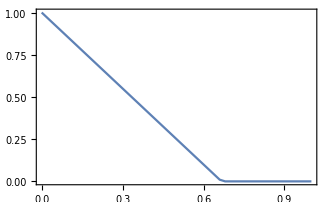
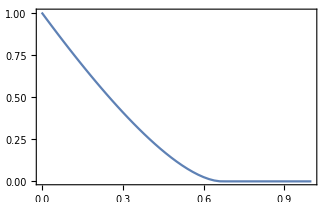

```mathematica
ψ = 1/(√2){0,1,1,0};
ρ = (1-p) out[ψ,ψ]+p Eye[4]/4;
{ListLinePlot[Table[{p,Concurrence[ρ]},{p,0,1,0.02}]],
ListLinePlot[Table[{p,EntanglementOfFormation[ρ]},{p,0,1,0.02}]]}
```

### Quantum Fidelity

```mathematica
Clear[QuantumFidelity];
QuantumFidelity[ρ_,σ_]:=Tr[MatrixPower[MatrixPower[ρ,1/2].σ.MatrixPower[ρ,1/2],1/2]]^2
```

#### Example usage

```mathematica
ρ = ({{0.3, 0}, {0, 0.7}});
σ = ({{0.7, 0}, {0, 0.3}});
QuantumFidelity[ρ,σ]
```

0.84

### Relative Entropy of Coherence with respect to the eigenbasis of an operator X

Computes the relative entropy of coherence of a state ρ in the basis of an observable X

C_X(ρ) = S(Δ_X(ρ)) - S(ρ)

where Δ_X is the maximally dephasing operation.

```mathematica
Clear[RelativeEntropyofCoherence];
RelativeEntropyofCoherence[ρ_,X_]:=Module[{v,V,Δρ},
V = Normalize/@Eigenvectors[X];
Δρ = Total@Table[out[v,v].ρ.out[v,v],{v,V}];
Chop[vonNeumann[Δρ]-vonNeumann[ρ],10^-12]
];
```

#### Example usage

```mathematica
ρ = ({{0.3, 0.1}, {0.1, 0.7}});
A = ({{1, 0}, {0, -1}});
FullDephasing[ρ,A]//mf;
```

(0.3 | 0.
0. | 0.7)

```mathematica
ρ = ({{0.3, 0.03+ⅈ 0.01}, {0.03-ⅈ 0.01, 0.7}});
```

```mathematica
RelativeEntropyofCoherence[ρ,σz]
```

0.00211989

```mathematica
(* Is the same as *)
KullbackLeibler[ρ,FullDephasingMap[ρ,σz]]
```

0.00211989

```mathematica
RelativeEntropyofCoherence[ρ,σx]
```

0.0834972

```mathematica
FullDephasingMap[ρ,σx]//mf;
```

(0.5 | 0.1
0.1 | 0.5)

### y-covariance (maybe buggy)

The y-covariance is defined as 

(cov_y(A,B))_ρ = tr(A ρ^y B ρ^(1-y))-tr(Aρ) tr(Bρ)

Very often, it appears integrated over y, in the form 

1/2∫_0^1 dy (cov_y(A,B))_ρ 

To compute this, it is easier to diagonalize ρ before hand, and compute the integral by hand.

```mathematica
Integrate[p^y q^(1-y),{y,0,1}]
Integrate[p^y p^(1-y),{y,0,1}]
```

(p-q)/(Log[p]-Log[q])

p

```mathematica
Clear[IntegratedCOVy];
IntegratedCOVy[A_,B_,ρ_,tol_:10^-11]:=Module[{f,d=Length@ρ,ps,𝒪,At,Bt},
{ps,𝒪} = Eigensystem[N@ρ];
𝒪 = 𝒪ᵀ;
(*ps = Abs[ps];*)

f=(DiagonalMatrix[ps]+Outer[Subtract,(1+tol)ps,ps])/(Eye[d]+tol+Outer[Subtract,Log[ps],Log[ps]]); 

At = 𝒪†.A.𝒪;
Bt = 𝒪†.B.𝒪;
1/2(Total@Flatten[f Bt Atᵀ]- Tr[A.ρ]Tr[B.ρ])//Chop
]
```

#### Example usage

```mathematica
ρ = ({{0.3, 0.1-0.05ⅈ}, {0.1+0.05ⅈ, 0.7}});
A = σx+0.3 σz;
B = 0.1 σy - 0.4 σx;
```

```mathematica
IntegratedCOVy[A,B,ρ]
```

-0.183308

#### Sanity check

```mathematica
ρ = ({{0.3, 0.1-0.05ⅈ}, {0.1+0.05ⅈ, 0.7}});
A = σx+0.3 σz;
B = 0.1 σy - 0.4 σx;
```

```mathematica
covy = Tr[A.MatrixPower[ρ,y].B.MatrixPower[ρ,1-y]]-Tr[A.ρ] Tr[B.ρ]//Simplify
```

(-0.0210667-7.80626×10^-18 ⅈ)-(0.272208+0.0922832 ⅈ) ⅇ^(-0.990207 y)-(0.101125-0.0342832 ⅈ) ⅇ^(0.990207 y)

```mathematica
1/2 Integrate[covy,{y,0,1}]//Chop
```

-0.183308

```mathematica
IntegratedCOVy[A,B,ρ]
```

-0.183308

```mathematica
LoadArbitrarySpinMatrices[1,"a"];
ρ = MatrixExp[-Sx.Sx];
ρ = ρ/Tr[ρ];
A = Sx+1/3 Sz;
B = 1/10 Sy - 9/10 Sx;
```

```mathematica
covy = Tr[A.MatrixPower[ρ,y].B.MatrixPower[ρ,1-y]]-Tr[A.ρ] Tr[B.ρ]//Simplify
N[1/2 Integrate[covy,{y,0,1}],20]
```

-9/(5 (2+ⅇ))

-0.19074740185537690056

```mathematica
Table[InputForm[IntegratedCOVy[A,B,ρ,tol]],{tol,logspace[-15,-5,10]}]//TableForm
```

-0.1985353357449922
-0.1895325004878372
-0.19063331085840698
-0.19075595939078738
-0.1907472060357457
-0.19074740995903772
-0.19074740530263645
-0.19074740221676056
-0.19074740185994632
-0.19074740185615058

#### Other (slower implementations)

```mathematica
IntegratedCOVy2[A_,B_,ρ_]:=Module[{f,d=Length@ρ,ps,vecs},
{ps,vecs} = Eigsys[ρ];
vecs=vecsᵀ;
f = Table[
If[Abs[ps⟦α⟧-ps⟦β⟧]<=10^-12,
ps⟦α⟧,
(ps⟦α⟧-ps⟦β⟧)/(Log[ps⟦α⟧]-Log[ps⟦β⟧])],{α,d},{β,d}];

1/2(Sum[f⟦α,β⟧ vecs⟦α⟧*.B.vecs⟦β⟧ vecs⟦β⟧*.A.vecs⟦α⟧,{α,d},{β,d}]-Sum[ps⟦α⟧ vecs⟦α⟧*.A.vecs⟦α⟧,{α,d}] Sum[ps⟦α⟧ vecs⟦α⟧*.B.vecs⟦α⟧,{α,d}])//Chop

]
```

```mathematica
(* Terrible: slow and imprecise *)
IntegratedCOVy3[A_,B_,ρ_,nys_:200]:=Module[{ave = Tr[A.ρ] Tr[B.ρ]},

1/2 Trapz[Table[Tr[A.MatrixPower[ρ,y].B.MatrixPower[ρ,1-y]]-ave,{y,linspace[0,1,nys]}],1./nys]//Chop
]
```

```mathematica
ps = {a,b,b};
```

```mathematica
mat1=(DiagonalMatrix[ps]+Outer[Subtract,(1+ϵ)ps,ps] )/(Eye[3]+ϵ+Outer[Subtract,Log[ps],Log[ps]])//Simplify//mf;
```

(a | (a-b+a ϵ)/(ϵ+Log[a]-Log[b]) | (a-b+a ϵ)/(ϵ+Log[a]-Log[b])
(-a+b+b ϵ)/(ϵ-Log[a]+Log[b]) | b | b
(-a+b+b ϵ)/(ϵ-Log[a]+Log[b]) | b | b)

```mathematica
mat1/.ϵ->0//mf;
```

(a | (a-b)/(Log[a]-Log[b]) | (a-b)/(Log[a]-Log[b])
(-a+b)/(-Log[a]+Log[b]) | b | b
(-a+b)/(-Log[a]+Log[b]) | b | b)

```mathematica
mat2=Table[
If[ps⟦α⟧===ps⟦β⟧,
ps⟦α⟧,
(ps⟦α⟧-ps⟦β⟧)/(Log[ps⟦α⟧]-Log[ps⟦β⟧])],{α,3},{β,3}]//mf;
```

(a | (a-b)/(Log[a]-Log[b]) | (a-b)/(Log[a]-Log[b])
(-a+b)/(-Log[a]+Log[b]) | b | b
(-a+b)/(-Log[a]+Log[b]) | b | b)

```mathematica
mat1-mat2/.ϵ->0//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

### Wigner-Yanase-Dyson skew information (maybe buggy as well)

Computes 1/2∫_0^1 dy I_y(A,ρ)

where I_y(A,ρ) = -1/2tr([ρ^y,A] [ρ^(1-y)A])

```mathematica
Clear[WignerYanaseDyson];
(*WignerYanaseDyson[A_,ρ_,tol_:10^-11]:=1/2(Tr[A.A.ρ]-Tr[A.ρ]^2)-IntegratedCOVy[A,A,ρ,tol]//Chop*)

WignerYanaseDyson[A_,ρ_,tol_:10^-11]:=Module[{f,d=Length@ρ,ps,𝒪,At},
{ps,𝒪} = Eigensystem[N@ρ];
𝒪 = 𝒪ᵀ;

f=(DiagonalMatrix[ps]+Outer[Subtract,(1+tol)ps,ps])/(Eye[d]+tol+Outer[Subtract,Log[ps],Log[ps]]); 
At = 𝒪†.A.𝒪;
1/2(Tr[A.A.ρ]-Total@Flatten[(f At) Atᵀ])//Chop]
```

#### Example usage

```mathematica
ρ = ({{0.3, 0}, {0, 0.7}});
A = σx+0.3 σz;
```

```mathematica
WignerYanaseDyson[σz,ρ]
```

0

```mathematica
WignerYanaseDyson[σx,ρ]
```

0.027911

### Quantum State Tomography

Silly simulations of a Quantum State Tomography process.

Optional input: list of orthogonal (not necessarily orthonormal) operators, in the sense that tr(A_i^†A_j) ∝ δ_(i,j)
If this is omitted, program assumes the canonical basis |n⟩⟨n|, (|n⟩⟨m| + |m⟩⟨n|) and i(|n⟩⟨m| - i |m⟩⟨n|).

```mathematica
Clear[QuantumStateTomography];
QuantumStateTomography[ρ_,nexperiments_,listOfObservables_]:=Module[{d=Length@ρ,λ,V,p,r,ρest},
ρest=Total@Table[

{λ,V} = Eigsys[A];
V = Vᵀ;
p = Table[v*.ρ.v,{v,V}]//Chop;
r=SillySample[p,λ,nexperiments]//Mean//N;
r/Tr[A†.A] A

,{A,listOfObservables}];

ρest = 1/d(1-Tr[ρest])Eye[d] + ρest
]

QuantumStateTomography[ρ_,nexperiments_]:=Module[{d=Length@ρ,listOfObservables},

listOfObservables = Join[
Table[Proj[d,i,i],{i,d}],
Flatten[Table[Proj[d,i,j]+Proj[d,j,i],{i,d},{j,i+1,d}],1],
Flatten[Table[ⅈ(Proj[d,i,j]-Proj[d,j,i]),{i,d},{j,i+1,d}],1]
];
QuantumStateTomography[ρ,nexperiments,listOfObservables]]
```

#### Example usage

```mathematica
(* Generate a random state *)
ψ = RandomReal[{0,1},2] + ⅈ RandomReal[{0,1},2]//Normalize
```

{0.554735+0.343922 ⅈ,0.653428+0.38343 ⅈ}

```mathematica
(* Simulate a tomography process *)
ρ = out[ψ,ψ]//mf;
QuantumStateTomography[ρ,10^5,{σx,σy,σz}]//mf;
```

(0.426013 | 0.494349+0.0120261 ⅈ
0.494349-0.0120261 ⅈ | 0.573987)

(0.42665 | 0.49442+0.01321 ⅈ
0.49442-0.01321 ⅈ | 0.57335)

```mathematica
ρ = out[ψ,ψ]//mf;
QuantumStateTomography[ρ,10^5]//mf;
```

(0.426013 | 0.494349+0.0120261 ⅈ
0.494349-0.0120261 ⅈ | 0.573987)

(0.42483 | 0.49459+0.0099 ⅈ
0.49459-0.0099 ⅈ | 0.57517)

### Quantum Process Tomography

Based on Sec. 8.4.2 of Nielsen & Chuang.
Input: channel ℰ[ρ], dimension d. 

- QuantumProcessTomography[ℰ,d] will return the χ matrix, the Ẽ operators and the reconstructed channel (which in this case matches exactly the original one). 

- QuantumProcessTomography[ℰ,d, nexperiments] will do actual state tomography in the output states. 

- - QuantumProcessTomography[ℰ,d, nexperiments, obs] also includes a generic list of observables.

```mathematica
Clear[QuantumProcessTomography];
QuantumProcessTomography[ℰ_,d_,nexperiments_,obs_]:=Module[{λ,β,χ,ℰreconstructed,ρs},
ρs =  Join[
Table[Proj[d,i,i],{i,d}],
Flatten[Table[out[(Basis[d,i]+Basis[d,j])/(√2),(Basis[d,i]+Basis[d,j])/(√2)],{i,d},{j,i+1,d}],1],
Flatten[Table[out[(Basis[d,i]+ⅈ Basis[d,j])/(√2),(Basis[d,i]+ⅈ Basis[d,j])/(√2)],{i,d},{j,i+1,d}],1]
];

β = ArrayReshape[N@Table[Tr[ρk†.Em.ρj.En†]/Tr[ρk†.ρk],{ρj,ρs},{ρk,ρs},{Em,obs},{En,obs}],{d^4,d^4}];

λ = If[nexperiments==0,
Table[Tr[ρk†.ℰ[ρj]]/Tr[ρk†.ρk],{ρj,ρs},{ρk,ρs}],
Table[Tr[ρk†.QuantumStateTomography[ℰ[ρj],nexperiments]]/Tr[ρk†.ρk],{ρj,ρs},{ρk,ρs}]
];
χ = Unvec@LinearSolve[β,Vec[λ]];

ℰreconstructed = Function[ρ,Sum[χ⟦m,n⟧obs⟦m⟧.ρ.obs⟦n⟧†,{m,Length@obs},{n,Length@obs}]];
{obs,χ,ℰreconstructed}
];

QuantumProcessTomography[ℰ_,d_]:=QuantumProcessTomography[ℰ,d,0]

QuantumProcessTomography[ℰ_,d_,nexperiments_]:=Module[{obs},
obs = Join[
Table[Proj[d,i,i],{i,d}],
Flatten[Table[Proj[d,i,j]+Proj[d,j,i],{i,d},{j,i+1,d}],1],
Flatten[Table[ⅈ(Proj[d,i,j]-Proj[d,j,i]),{i,d},{j,i+1,d}],1]
];
QuantumProcessTomography[ℰ,d,nexperiments,obs]]
```

#### Example usage

```mathematica
ℰp=QuantumProcessTomography[AmplitudeDamping[0.3,0.5],2];
ρtest = 1/2({{1, 1}, {1, 1}});
AmplitudeDamping[0.3,0.5][ρtest]//mf;
Last[ℰp][ρtest]//mf;
```

(0.4 | 0.353553
0.353553 | 0.6)

(0.4 | 0.353553
0.353553 | 0.6)

```mathematica
ℰp=QuantumProcessTomography[AmplitudeDamping[0.3,0.2],2,10^6];
ρtest = 1/2({{1, 1}, {1, 1}});
AmplitudeDamping[0.3,0.2][ρtest]//mf;
Last[ℰp][ρtest]//mf;
```

(0.46 | 0.447214
0.447214 | 0.54)

(0.460627 | 0.446415-0.0011305 ⅈ
0.446415+0.0011305 ⅈ | 0.539748)

```mathematica
ℰp=QuantumProcessTomography[AmplitudeDamping[0.3,0.2],2,10^6,{σ0,σx,σy,σz}];
ρtest = 1/2({{1, 1}, {1, 1}});
AmplitudeDamping[0.3,0.2][ρtest]//mf;
Last[ℰp][ρtest]//mf;
```

(0.46 | 0.447214
0.447214 | 0.54)

(0.459382 | 0.44747-0.00010175 ⅈ
0.44747+0.00010175 ⅈ | 0.539921)

## Quantum thermodynamics

### Work distribution & moments

The work distribution reads

P(W)=∑_(n,m) p_n|⟨m|U|n⟩|^2 δ(W - (E_m^f-E_n^i)) 

The characteristic function is 

G(k)=⟨e^(i k W)⟩ =tr(U^†e^(i k H_f) U e^(-i k H_i)ρ_d )

where ρ_d is the initial state, but diagonal in the basis of H_0.

The n-th moment can be computed as ⟨W^n⟩ = i^-n G^(n)(0). Carrying out the derivatives, we then find

⟨W^n⟩ = ∑_(k = 0)^n (-1)^(n-k) (n
k) ⟨(H̃)_1^k H_0^(n-k)⟩_i    where (H̃)_1 = U†H_1 U

#### Usage

WorkMoments[n_,y_,Hi_,Hf_]
Moments of the work distribution for a sudden quench, U = 𝕀. 
This function is fairly fast to be evaluated.
Input: 
- n: moment 
- y: initial state. Can be either pure, y = ψ, or mixed, y = ρ. 
      For the purpose of speed, the function does not test if [H_i,ρ] = 0 or not. 
      If this is not true, the resulting distribution becomes a quasi-probability. 
- Hi: initial Hamiltonian 
- Hf: final Hamiltonian 

WorkMoments[n_,y_,Hi_,Hf_,U_]
Same, but for a generic work protocol with unitary U. 
User has to supply U, computed by some other mean. 

WorkDistribution[Hi_,Hf_,ρ0type_,y_]
WorkDistribution[Hi_,Hf_,ρ0type_,y_,U_]
Full work distribution P(W) for a quench or for a finite-time work protocol (when U is provided).

ρ0type: type of initial state.  
y: auxiliary numerical quantity, which changes depending on ρ0type. 
- ρ0type == “GS”: ground-state. In this case the value of y is irrelevant. 
- ρ0type == “thermal”: thermal state. In this case y = β = 1/T
- ρ0type == “eigenstate”: a specific eigenstate of the Hamiltonian. In this case y = 1,2,...,d labels the eigenstate, with y = 1 being the GS. 
- ρ0type == “identity”: infinite temperature state. Value of y is irrelevant. 
-ρ0type == “generic”: in this case y = ρ  is a generic initial state; the initial probabilities are computed as p_n= ⟨n|ρ|n⟩.

#### Functions

```mathematica
ProbMerger[x_,P_,tol_:10^-11]:=List@@@Normal[GroupBy[Table[{N[Round[x⟦i⟧,tol]],P⟦i⟧},{i,1,Length[x]}],First-> Last,Total]]
```

```mathematica
(* MatrixPower but with A^0=identity, even if A is singular *)
matrixpower[A_,n_]:=If[n==0,Eye[Length@A],MatrixPower[A,n]]
matrixpower[A_,n_,y_]:=If[n==0,y,MatrixPower[A,n,y]]
```

```mathematica
Clear[WorkMoments];
WorkMoments[nn_,y_,Hi_,Hf_]:=Module[{n,Y,result},
(*If[checkCommute[Hi,y]==False,Print["Initial state does not commute with Hi"]];*)
result=Which[
y⟦1⟧==="thermal",
Y = MatrixExp[-y⟦2⟧ Hi];
Y = Y/Tr[Y];

Table[Sum[(-1)^(n-k)Binomial[n,k] Tr[matrixpower[Hf,k].matrixpower[Hi,n-k].Y],{k,0,n}],{n,Flatten[{nn}]}],

y⟦1⟧=="GS",
Y = GroundState[Hi];
Re@Table[Sum[(-1)^(n-k)Binomial[n,k] Conjugate[matrixpower[Hf,k,Y]].matrixpower[Hi,n-k,Y],{k,0,n}],{n,Flatten[{nn}]}],

y⟦1⟧=="eigenstate",
Y = GroundState[Hi,y⟦2⟧];
Re@Table[Sum[(-1)^(n-k)Binomial[n,k] Conjugate[matrixpower[Hf,k,Y]].matrixpower[Hi,n-k,Y],{k,0,n}],{n,Flatten[{nn}]}],

Length@Dimensions@y==2,
Table[
Sum[(-1)^(n-k)Binomial[n,k] Tr[matrixpower[Hf,k].matrixpower[Hi,n-k].y],{k,0,n}],{n,Flatten[{nn}]}],

True,Table[Sum[(-1)^(n-k)Binomial[n,k] Conjugate[matrixpower[Hf,k,y]].matrixpower[Hi,n-k,y],{k,0,n}],{n,Flatten[{nn}]}]
]//Chop;
If[Head[nn]===List,result,First@result]
]
WorkMoments[n_,y_,Hi_,Hf_,U_]:=WorkMoments[n,y,Hi,U†.Hf.U]
```

```mathematica
getCumulants[moms_]:=Module[{nmoms = Length@moms,rep,n},
rep = Thread[Table[Moment[j],{j,nmoms}]->moms];
Table[MomentConvert[Cumulant[n],Moment]/.rep,{n,1,nmoms}]]
```

```mathematica
(* Full work distribution *)
Clear[WorkDistribution];
WorkDistribution[Hi_,Hf_,ρ0type_,y_]:=Module[{ord,i,Ei,Vi,Ef,Vf,ℳ,𝒬,d = Length@Hi,pi,works,probs},
{Ei,Vi} =Eigsys[Hi]; 
{Ef,Vf} =Eigsys[Hf];
𝒬 = Abs[Vf†.Vi]^2 (* The matrix |⟨j|U|i⟩|^2 *);

(* Initial probabilities *)
Which[
(* ground-state *)
ρ0type =="GS",
pi=IdentityMatrix[d]⟦1⟧,

(* Thermal: in this case y = β = 1/T *)
ρ0type=="thermal",
(pi = Table[Exp[-y(Ei⟦i⟧-Ei⟦1⟧)],{i,1,d}];
pi = pi/Total@pi;
),

(* Eigenstate of Subscript[H, i]. In this case y labels the eigenstate, with y = 1 being the GS *)
ρ0type =="eigenstate",
pi = IdentityMatrix[d]⟦y⟧,

(* Infinite temperature state *)
ρ0type =="identity",
pi = ConstantArray[1/d,{d}],

(* Generic. In this case y is the initial density matrix *)
ρ0type=="generic",
pi = Table[Vi⟦All,i⟧*.y.Vi⟦All,i⟧,{i,d}]
];

works = Flatten@Table[ef-ei,{ei,Ei},{ef,Ef}];
probs = Flatten@Table[𝒬⟦j,i⟧ pi⟦i⟧,{i,d},{j,d}];
ord = Ordering[works];

Select[ProbMerger[works⟦ord⟧,probs⟦ord⟧],Abs[#⟦2⟧]>10^-10&]
]

WorkDistribution[Hi_,Hf_,ρ0type_,y_,U_]:=WorkDistribution[Hi,U†.Hf.U,ρ0type,y]
```

#### Example usage

```mathematica
(* Build two tight-binding Hamiltonians with different on-site potentials *)
Hi = TightBindingModel[{1,-1},30];
Hf = TightBindingModel[{1,0,1},30];
```

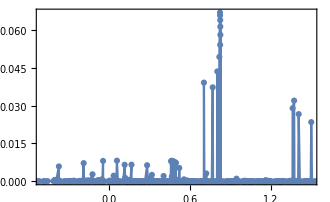

```mathematica
(* Work distribution starting from a thermal state at β = 0.5 *)
P=WorkDistribution[Hi,Hf,"thermal",0.5];
ListLinePlot[P,PlotMarkers->Automatic,PlotRange->{{-.5,1.5},All}]
```

```mathematica
(* First few moments *)
P⟦All,1⟧.P⟦All,2⟧
(P⟦All,1⟧^2).P⟦All,2⟧
(P⟦All,1⟧^3).P⟦All,2⟧
```

1.06874

2.20279

5.77457

```mathematica
(* Instead, the moments can be computed directly with the WorkMoments function, which is faster *)
y = MatrixExp[-0.5 Hi];
y = y/Tr[y];
WorkMoments[1,y,Hi,Hf]
WorkMoments[2,y,Hi,Hf]
WorkMoments[3,y,Hi,Hf]
```

1.06874

2.20279

5.77457

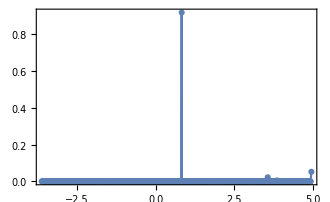

```mathematica
(* Starting from the GS. Last entry "0" is irrelevant *)
P=WorkDistribution[Hi,Hf,"GS",0];
ListLinePlot[P,PlotMarkers->Automatic(*,PlotRange->{{-.5,1.5},All}*)]
```

```mathematica
(* First few moments *)
P⟦All,1⟧.P⟦All,2⟧
(P⟦All,1⟧^2).P⟦All,2⟧
(P⟦All,1⟧^3).P⟦All,2⟧
```

1.11557

2.26513

8.16159

```mathematica
y = Eigvecs[Hi,1]//Flatten;
WorkMoments[1,y,Hi,Hf]
WorkMoments[2,y,Hi,Hf]
WorkMoments[3,y,Hi,Hf]
```

1.11557

2.26513

8.16159

#### Example: macrospin model with a finite unitary

```mathematica
LoadArbitrarySpinMatrices[S = 50];
Hi = Sz;
Hf = Sz;
U = MatrixExp[-ⅈ (Sz - 0.5 Sx) ];
P = WorkDistribution[Hi,Hf,"thermal",0.1,U]//Quiet;
```

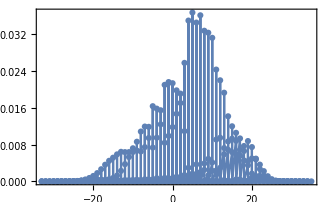

```mathematica
ListLinePlot[P,PlotMarkers->Automatic,PlotRange->All]
```

```mathematica
WorkMoments[2,{"thermal",1},Hi,Hf,U]
```

42.2801

```mathematica
WorkMoments[2,{"GS"},Hi,Hf,U]
```

36.9552

```mathematica
ψ = GroundState[Hi];
WorkMoments[2,ψ,Hi,Hf,U]
```

36.9552-2.8581×10^-6 ⅈ

```mathematica
WorkMoments[2,{"eigenstate",2},Hi,Hf,U]
```

46.2138

#### Example: LMG model with a finite ramp

```mathematica
LoadArbitrarySpinMatrices[S=49/2];
𝒩 = 2S+1;
ℋ[h_]:=-2/𝒩 Sx.Sx-2 h Sz;
Hi= ℋ[hi=0.5];
Hf=ℋ[hf=1.5];
τ = 2.0;
(*U = UnitaryDynamics[{-2/𝒩 Sx.Sx,-2 Sz},{Function[t,1],Function[t,hi+(hf-hi) t/τ]},0.005,τ];*)
P1 = WorkDistribution[Hi,Hf,"GS",1]//Quiet;

Hf=ℋ[1.0];
P2 = WorkDistribution[Hi,Hf,"GS",1]//Quiet;

P1b = {#⟦1⟧+Egs,#⟦2⟧}&/@P1;
P2b = {#⟦1⟧+Egs,#⟦2⟧}&/@P2;
Egs=Eigvals[Hi,1]⟦1⟧;
```

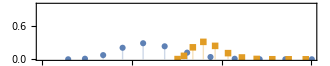

```mathematica
ListPlot[{P1b,P2b},PlotMarkers->Automatic,PlotRange->{{-80,-20},{0,1}},Filling->Axis,AspectRatio->1/5]
```

```mathematica
LoadArbitrarySpinMatrices[S=49/2];
𝒩 = 2S+1;
ℋ[h_]:=-2/𝒩 Sx.Sx-2 h Sz;
Hi= ℋ[hi=0.5];
Hf=ℋ[hf=1.5];
τ = 10.5;
PrettyTiming[U = UnitaryDynamics[{-2/𝒩 Sx.Sx,-2 Sz},{Function[t,1],Function[t,hi+(hf-hi) t/τ]},0.002,τ,"id","RK4"];]
P = WorkDistribution[Hi,Hf,"GS",1,U]//Quiet;

PrettyTiming[U = UnitaryDynamics[{-2/𝒩 Sx.Sx,-2 Sz},{Function[t,1],Function[t,hi+(hf-hi) t/τ]},0.1,τ,"id","Trotter"];]
P2 = WorkDistribution[Hi,Hf,"GS",1,U]//Quiet;
```

0h : 0m : 4s

0h : 0m : 0s

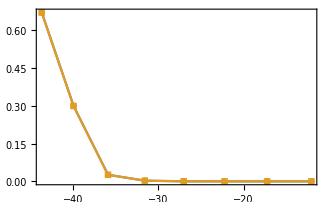

```mathematica
ListLinePlot[{P,P2},PlotMarkers->Automatic,PlotRange->All]
```

### Thermo-Majorization curve

```mathematica
(* Given probabilities and energies, yields the points (x,y) of a thermo-majorization curve *)
ThermoMajorizationCurve[pps_,Es_,β_]:=Module[{ord,x,y,ps},
ps = pps/Total[pps];
ord=Reverse@Ordering[ps Exp[β Es]];
y=Prepend[Accumulate[ps⟦ord⟧],0];
x = Prepend[Accumulate[Exp[-β Es]⟦ord⟧],0]//N;
Transpose[{x,y}]
]
```

#### Example usage

```mathematica
β = 1.0;
Es = {1.4,2,3.,2.5} (* energies *);
probs = {5,4,3,5} (* probs; don't have to be normalized *);
thermocurve = ThermoMajorizationCurve[probs,Es,β]
```

{{0.,0},{0.082085,5/17},{0.131872,8/17},{0.267207,12/17},{0.513804,1}}

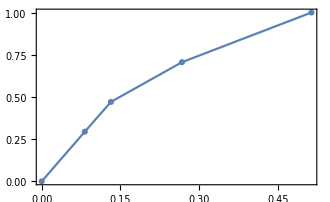

```mathematica
ListLinePlot[thermocurve,PlotMarkers->Automatic,PlotRange->All]
```

### Ergotropy

```mathematica
Ergotropy[H_,ρ_]:=Module[{P,ℰ,psiRho,psiH},
{P,psiRho}=Eigensystem[N@ρ];
{ℰ,psiH}=Eigensystem[1000 NEye[Length@H]-H];
ℰ = 1000 - ℰ;
Sum[P⟦i⟧ ℰ⟦j⟧(Abs[psiH⟦j⟧*.psiRho⟦i⟧]^2-KroneckerDelta[i,j]),{i,Length@ρ},{j,Length@H}]
]
```

## Metrology

### Quantum Fisher Information

```mathematica
QuantumFisherInformation[ρ_,dρ_]:=2Vec[dρᵀ].LinearSolve[kron[ρᵀ,Eye[Length@ρ]]+kron[Eye[Length@ρ],ρ],Vec[dρ]]//Chop(*2Vec[dρᵀ].PseudoInverse[kron[ρᵀ,NEye[Length@ρ]]+kron[NEye[Length@ρ],ρ]].Vec[dρ]*)
```

```mathematica
SymmetricLogarithmicDerivative[ρ_,dρ_]:=Module[{n,A,b},
n = Length@ρ;
A = kron[ρᵀ,Eye[n]] + kron[Eye[n],ρ];
b = 2 Vec[dρ];
LinearSolve[A,b]//Unvec
]
```

### QFI and SLD for a qubit (analytical expressions)

```mathematica
(* Solution of Λρ + ρΛ = 2 ∂ρ/∂θ *)
QubitSLD[ρ_,dρ_]:=Module[{p = ρ⟦1,1⟧,q=ρ⟦1,2⟧,dp=dρ⟦1,1⟧,dq=dρ⟦1,2⟧},
({{(-(-1+p) (dq* q + dq q*)+dp (-1+p + 2 q q*))/(-p+p^2+q q*), (q (dp-2 dp p-dq* q)+dq (-2 p+2 p^2+q q*))/(-p+p^2+q q*)}, {(q* (dp-2 dp p-dq q*)+dq* (-2 p+2 p^2+q q*))/(-p+p^2+q q*), (dp p+dq* p q+dq p q*-2 dp q q*)/(-p+p^2+q q*)}})   
];
(* QFI ℱ = tr(ρΛ^2) *)
QubitQFI[ρ_,dρ_]:=Module[{Λ = QubitSLD[ρ,dρ]},Tr[ρ.Λ.Λ]]

(* QFI for multiparameter estimation, Subscript[ℱ, ij]=1/2 tr(ρ{Subscript[Λ, i],Subscript[Λ, j]}) *)
QubitQFI[ρ_,dρ1_,dρ2_]:=Module[{Λ1 = QubitSLD[ρ,dρ1],Λ2 = QubitSLD[ρ,dρ2]},1/2 Tr[ρ.(Λ1.Λ2+Λ2.Λ1)]]
```

#### Example usage

A qubit thermal state. The QFI in this case is related to the specific heat

```mathematica
ρ = ({{f, 0}, {0, 1-f}})/.f->1/(ⅇ^(ω/T)+1);
dρ = D[ρ,T];
QubitQFI[ρ,dρ]//Simplify
```

(ⅇ^(ω/T) ω^2)/((1+ⅇ^(ω/T))^2 T^4)

```mathematica
(* The SLD in this case is diagonal *)
QubitSLD[ρ,dρ]//Simplify//mf;
```

((ⅇ^(ω/T) ω)/((1+ⅇ^(ω/T)) T^2) | 0
0 | -ω/((1+ⅇ^(ω/T)) T^2))

#### Explicit calculation of the SLD

```mathematica
ρ = ({{p, q}, {qs, 1-p}});
dρ = ({{dp, dq}, {dqs, -dp}});
Λ = ({{λ11, λ12}, {λ21, λ22}});
First@Solve[Thread[Flatten[Λ.ρ+ρ.Λ-2 dρ]==0],Flatten@Λ]//Simplify
ΛΛ=Λ/.%//mf;
```

{λ11→(-(-1+p) (dqs q+dq qs)+dp (-1+p+2 q qs))/(-p+p^2+q qs),λ12→(q (dp-2 dp p-dqs q)+dq (-2 p+2 p^2+q qs))/(-p+p^2+q qs),λ21→(qs (dp-2 dp p-dq qs)+dqs (-2 p+2 p^2+q qs))/(-p+p^2+q qs),λ22→(dp p+dqs p q+dq p qs-2 dp q qs)/(-p+p^2+q qs)}

((-(-1+p) (dqs q+dq qs)+dp (-1+p+2 q qs))/(-p+p^2+q qs) | (q (dp-2 dp p-dqs q)+dq (-2 p+2 p^2+q qs))/(-p+p^2+q qs)
(qs (dp-2 dp p-dq qs)+dqs (-2 p+2 p^2+q qs))/(-p+p^2+q qs) | (dp p+dqs p q+dq p qs-2 dp q qs)/(-p+p^2+q qs))

### QFI and SLD for Gaussian states (applicable to very large systems)

Based on 1303.3682, but adapted slightly. 

The function GaussianQFI has been highly optimized and is now extremely efficient. 
An older, more “pedagogical” version, is kept below.

```mathematica
(* This is only a part of the SLD actually. It is the part called L^(2) in 1303.3682 *)
Clear[GaussianSLD]
GaussianSLD[σ_,dσ_]:=Module[{Ω},
Ω = SymplecticForm[Length[σ]/2];
Unvec@LinearSolve[2 kron[σᵀ,σ] + 1/2 kron[Ωᵀ,Ω],Vec[dσ]]
]
```

```mathematica
GaussianQFI[σ_,dσ_]:=Module[{W,S,w,errors,Ω,M,vec,𝒟},
{W,S,errors}=Williamson[2*σ];
Ω = SymplecticForm[Length[W]/2];
M = Ω.Sᵀ.Ω;
vec = Vec[M.dσ.Transpose[M]];

w = SparseArray[W];
𝒟 = 1/2(kron[w,w]-kron[Ω,Ω]);
vec*.LinearSolve[𝒟,vec]
]

GaussianQFI[σ_,dσ_,dμ_]:=dμ.LinearSolve[σ,dμ] + GaussianQFI[σ,dσ]
```

#### Example usage

```mathematica
σana = ({{1/2+n+nth, 0, Cos[θ] √(n (1+n)), 0}, {0, 1/2+n+nth, 0, -Sin[θ] √(n (1+n))}, {Cos[θ] √(n (1+n)), 0, 1/2+n, 0}, {0, -Sin[θ] √(n (1+n)), 0, 1/2+n}});
```

```mathematica
σ = σana/.{nth->0.96,n->1.1,θ->0.3}//mf;
dσ = D[σana,θ]/.{nth->0.66,n->1.1,θ->0.3}//mf;
```

(2.56 | 0 | 1.45199 | 0
0 | 2.56 | 0 | -0.449152
1.45199 | 0 | 1.6 | 0
0 | -0.449152 | 0 | 1.6)

(0 | 0 | -0.449152 | 0
0 | 0 | 0 | -1.45199
-0.449152 | 0 | 0 | 0
0 | -1.45199 | 0 | 0)

```mathematica
GaussianSLD[σ,dσ]//mf;
```

(0.309441 | 0. | -0.413519 | 0.
0. | -0.0639195 | 0. | -0.22211
-0.413519 | 0. | 0.488668 | 0.
0. | -0.22211 | 0. | -0.0719429)

```mathematica
GaussianQFI[σ,dσ]
```

1.01647

#### Old version (pedagogical)

```mathematica
(* Pedagogical, but much slower *)
Clear[GaussianQFIpegagogical]
GaussianQFIpegagogical[σ_,dσ_]:=Module[{Ω,L},
Ω = SymplecticForm[Length[σ]/2];
L = GaussianSLD[σ,dσ];
Tr[L.dσ]
]

GaussianQFIpegagogical[σ,dσ]
```

1.01647

### Gammelmark-Mølmer Quantum Fisher information for continuous measurements

Based on https://link.aps.org/doi/10.1103/PhysRevLett.112.170401
(Eq. 21 of the Supplemental Material)

(This is the starting point for the Hasegawa bound https://link.aps.org/doi/10.1103/PhysRevLett.125.050601)

I focus here on the estimation of a single parameter for simplicity. 
Input: 
- Steady-state ρ
- Liouvillian ℒ 
- Hamiltonian H
- Derivative of H wrt to θ, H’
- List of jump operators {L_k}
- List of derivatives of the jump operators {L'_k}.

Note: formula only makes sense if ρ is the steady-state.

```mathematica
Clear[GammelmarkMolmerMFisher];
GammelmarkMolmerMFisher[ρ_,ℒ_, H_,Hp_,cops_,copsprime_]:=Module[{op1,𝕀,op2,ℒL,ℒR,ℒinv,outie},
op1 = -ⅈ Hp - 1/2 Sum[copsprime⟦k⟧†.cops⟦k⟧ + cops⟦k⟧†.copsprime⟦k⟧,{k,Length@cops}];
op2 = ⅈ Hp - 1/2 Sum[copsprime⟦k⟧†.cops⟦k⟧ + cops⟦k⟧†.copsprime⟦k⟧,{k,Length@cops}];
𝕀 = Eye[Length@H];
ℒL=kron[𝕀, op1] + Sum[kron[cops⟦k⟧*,copsprime⟦k⟧],{k,Length@cops}];
ℒR=kron[op2ᵀ,𝕀] + Sum[kron[copsprime⟦k⟧*,cops⟦k⟧],{k,Length@cops}];


(*outie = Eye[Length@ℒ]  - out[Vec[ρ], Vec[Eye[Length@ρ]]];
ℒinv = outie.PseudoInverse[ℒ].outie;
4Re@(Sum[Tr[c.ρ.c†],{c,copsprime}]- UnTr[ℒL.ℒinv.ℒR.Vec[ρ]]-UnTr[ℒR.ℒinv.ℒL.Vec[ρ]])*)
4Re@(Sum[Tr[c.ρ.c†],{c,copsprime}]- UnTr[ℒL.DrazinApply2[ℒ,Vec[ρ],ℒR.Vec[ρ]]]-UnTr[ℒR.DrazinApply2[ℒ,Vec[ρ],ℒL.Vec[ρ]]])
]
```

#### Example usage: non-resonant qubit

Reproducing Fig. 1 of the paper (1310.5802)

```mathematica
Clear[Δ,Ω,κ];
H = Δ/2 σz + Ω/2 σx;
cops = {√κ σm};
ℒ = Liouvillian[H,cops]//cf;
ρ = AnalyticalSteadyState[ℒ]//Simplify//mf;
```

(Ω^2/(4 Δ^2+κ^2+2 Ω^2) | -((2 Δ+ⅈ κ) Ω)/(4 Δ^2+κ^2+2 Ω^2)
(ⅈ (2 ⅈ Δ+κ) Ω)/(4 Δ^2+κ^2+2 Ω^2) | (4 Δ^2+κ^2+Ω^2)/(4 Δ^2+κ^2+2 Ω^2))

```mathematica
FΔ=GammelmarkMolmerMFisher[ρ,ℒ,H,Evaluate@D[H,Δ],cops,Evaluate@D[cops,Δ]]//cf
FΩ=GammelmarkMolmerMFisher[ρ,ℒ,H,Evaluate@D[H,Ω],cops,Evaluate@D[cops,Ω]]//cf
Fκ=GammelmarkMolmerMFisher[ρ,ℒ,H,Evaluate@D[H,κ],cops,Evaluate@D[cops,κ]]//cf
```

(8 (4 Δ^2+κ^2) Ω^2 (2 κ^2+Ω^2))/(κ (4 Δ^2+κ^2+2 Ω^2)^3)

(4 (16 Δ^4 κ^2+8 Δ^2 κ^2 (κ-Ω) (κ+Ω)+(κ^2+2 Ω^2)^3))/(κ (4 Δ^2+κ^2+2 Ω^2)^3)

Ω^2/(4 Δ^2 κ+κ^3+2 κ Ω^2)

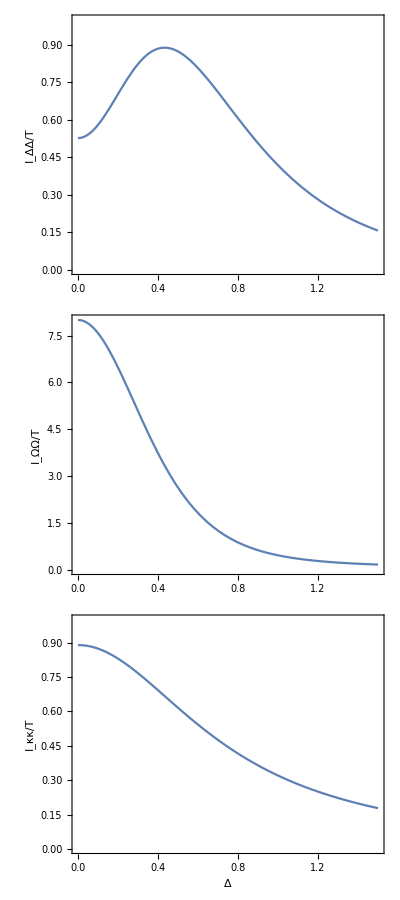

```mathematica
Grid[{{
Plot[FΔ/.{κ->1/2,Ω->1},{Δ,0,1.5},AspectRatio->1/3,PlotRange->{0,1},FrameLabel->{None,"I_ΔΔ/T"}],
Plot[FΩ/.{κ->1/2,Ω->1},{Δ,0,1.5},AspectRatio->1/3,PlotRange->{0,8},FrameLabel->{None,"I_ΩΩ/T"}],
Plot[Fκ/.{κ->1/2,Ω->1},{Δ,0,1.5},AspectRatio->1/3,PlotRange->{0,1},FrameLabel->{"Δ","I_κκ/T"}]}}ᵀ]
```

#### Kiilerich-Mølmer result: Fisher information from 2-point functions of a homodyne signal

Based on 1605.00902
The contribution of the sample mean to the Fisher information is 

ℐ^(1) = τ (∂_θ J)^2

The contribution from the two-point function is 

ℐ^(2) = τ ∫_0^∞ (dτ [∂_θ F(τ)])^2 = τ/(4π) ∫_(-∞)^∞ (dω [∂_θ S(ω)])^2

The actual Fisher information of the homodyne signal, ℐ^(hom) will be bounded by 

ℐ^Quantum ≥ ℐ^(hom) ≥ ℐ^(1)+ ℐ^(2)

Reproducing Fig. 3(b) of the paper (1605.00902)

```mathematica
Clear[Δ,Ω,κ];
H =  Ω/2 σx;
c = √κ σm;
ℒ = Liouvillian[H,{c}]//cf;
ρ = AnalyticalSteadyState[ℒ]//Simplify//mf;
```

(Ω^2/(κ^2+2 Ω^2) | -(ⅈ κ Ω)/(κ^2+2 Ω^2)
(ⅈ κ Ω)/(κ^2+2 Ω^2) | (κ^2+Ω^2)/(κ^2+2 Ω^2))

```mathematica
Clear[κ];
J = FCSAverage[ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Homodyne"]//cf
S = FCSPowerSpectrumLinearSys[{ω},ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Homodyne"]⟦1,2⟧//cf
G2 = FCSG2MEXP[{τ},ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Homodyne"]⟦1,2⟧//cf
F = G2 - J^2//cf
```

-(2 κ^(3/2) Ω)/(κ^2+2 Ω^2)

(κ^6+κ^4 (5 ω^2-2 Ω^2)+8 (-ω^2 Ω+Ω^3)^2+κ^2 (4 ω^4-6 ω^2 Ω^2+44 Ω^4))/((κ^2+2 Ω^2) (κ^4+4 (ω^2-Ω^2)^2+κ^2 (5 ω^2+4 Ω^2)))

1/((κ^2-16 Ω^2) (κ^2+2 Ω^2)^2)ⅇ^(-1/4 τ (3 κ+√(κ^2-16 Ω^2))) κ Ω^2 (4 ⅇ^(1/4 τ (3 κ+√(κ^2-16 Ω^2))) κ^2 (κ-4 Ω) (κ+4 Ω)+κ^3 √(κ^2-16 Ω^2)-ⅇ^(1/2 τ √(κ^2-16 Ω^2)) κ^3 √(κ^2-16 Ω^2)-10 κ Ω^2 √(κ^2-16 Ω^2)+10 ⅇ^(1/2 τ √(κ^2-16 Ω^2)) κ Ω^2 √(κ^2-16 Ω^2)-(1+ⅇ^(1/2 τ √(κ^2-16 Ω^2))) (κ^4-18 κ^2 Ω^2+32 Ω^4))

-((2 ⅇ^(-(3 κ τ)/4) κ Ω^2 ((κ^4-18 κ^2 Ω^2+32 Ω^4) Cosh[1/4 τ √(κ^2-16 Ω^2)]+κ √(κ^2-16 Ω^2) (κ^2-10 Ω^2) Sinh[1/4 τ √(κ^2-16 Ω^2)]))/((κ^2-16 Ω^2) (κ^2+2 Ω^2)^2))

```mathematica
ℐ1 = D[J,Ω]^2//cf
```

(4 κ^3 (κ^2-2 Ω^2)^2)/((κ^2+2 Ω^2)^4)

```mathematica
dF=D[F,Ω]//cf;
dS = D[S,Ω];
```

```mathematica
κ = 1;
ℐ2 = Table[{Ω,NIntegrate[dF^2,{τ,0,∞}]},{Ω,0.01,2,0.041}]//Quiet;
```

```mathematica
ℐ22 = Table[{Ω,1/(4π)NIntegrate[dS^2,{ω,-∞,∞}]},{Ω,0.01,2,0.041}]//Quiet;
```

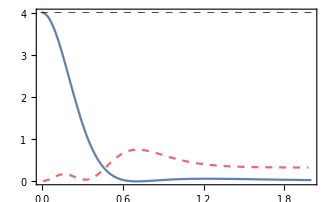

```mathematica
Show[
Plot[ℐ1,{Ω,0,2},PlotStyle->blue],
ListLinePlot[ℐ22,PlotStyle->Directive[red,Dashed]],
GridLines->{None,{4}},
GridLinesStyle->Directive[Black, Dashed]
]
```

```mathematica
int = dS^2//cf
```

(256 ((1+ω^2)^2 (1+4 ω^2) Ω-8 (1+5 ω^2+4 ω^4) Ω^3-4 (9+ω^2+4 ω^4) Ω^5-16 (1+ω^2) Ω^7+32 Ω^9)^2)/((1+2 Ω^2)^4 (4 ω^4+ω^2 (5-8 Ω^2)+(1+2 Ω^2)^2)^4)

```mathematica
int2=Integrate[int,{ω,0,∞},Assumptions->Ω>1]
```

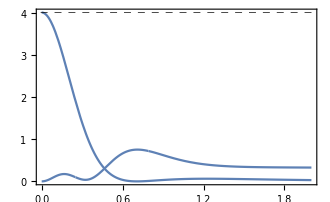

```mathematica
Show[
Plot[{ℐ1,1/(2π)Re@int2},{Ω,0,2},PlotStyle->blue],
GridLines->{None,{4}},
GridLinesStyle->Directive[Black, Dashed]
]
```

### Sequential Max-likelihood

```mathematica
Clear[SequentialMaxLikelihood];
SequentialMaxLikelihood[loglike_,outcomes_,θgrid_,outputstep_:1]:=Module[{ll,posML,Lmax,θmax},
ll = Accumulate@Table[loglike[x,θ],{x,outcomes},{θ,θgrid}];
posML = First@Ordering[#,-1]&/@ll;
(*Lmax=Max/@ll;*)
θmax = θgrid⟦posML⟧;
θmax⟦1;;-1;;outputstep⟧
]
```

```mathematica
Clear[MeanSquaredError];
MeanSquaredError[θest_?MatrixQ,θreal_]:=Mean/@Transpose[(θest-θreal)^2]
MeanSquaredError[θest_?VectorQ,θreal_]:=MeanSquaredError[{θest},θreal]
```

#### Example usage

```mathematica
Log[PDF[ExponentialDistribution[θ],x]]
```

Log[Piecewise[{{ⅇ^(-x θ) θ, x≥0}, {0, True}}]]

```mathematica
r = RandomVariate[ExponentialDistribution[1.5],5000];
θs = linspace[0.01,3,1000];
```

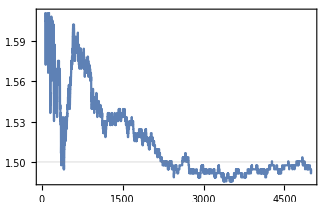

```mathematica
ListLinePlot[SequentialMaxLikelihood[Function[{x,θ},-x θ + Log[θ]],r,θs],GridLines->{None,{1.5}}]
```

## Channels and gates

All channels and gates are applicable to act on states of L qubits.
- For instance, one may apply an Amplitude Damping channel to qubit 5, in an entangled state of 8 qubits. 
- Or one may apply a SWAP between qubits 3 and 6.

### Amplitude damping

γ ∈ [0,1] gives the strength of the interaction, with γ = 0 being the identity map and γ  = 1 being full thermalization

If γ = 1 the system will thermalize to (f | 0
0 | 1-f)

```mathematica
Clear[AmplitudeDampingKrausOperators];
AmplitudeDampingKrausOperators[f_,γ_]:=Module[{M},
M[0] = √f({{1, 0}, {0, √(1-γ)}});
M[1] = √f({{0, √γ}, {0, 0}});
M[2] = √(1-f)({{√(1-γ), 0}, {0, 1}});
M[3] = √(1-f)({{0, 0}, {√γ, 0}});
{M[0],M[1],M[2],M[3]}

]
```

```mathematica
Clear[AmplitudeDamping];
AmplitudeDamping[f_,γ_][ρ_]:=Module[{M = AmplitudeDampingKrausOperators[f,γ]},Total@Table[M⟦i⟧.ρ.M⟦i⟧ᵀ,{i,Length@M}]]

AmplitudeDamping[f_,γ_,qubit_][ρ_]:=Module[{M = AmplitudeDampingKrausOperators[f,γ]},
Total@Table[KronEye[M⟦i⟧,Log2[Length@ρ],qubit].ρ.KronEye[M⟦i⟧,Log2[Length@ρ],qubit]ᵀ,{i,Length@M}]

]
```

#### Example usage

AmplitudeDampingKrausOperators just gives a list of the 4 Kraus operators for the finite temperature amplitude damping:

```mathematica
mf/@AmplitudeDampingKrausOperators[f,γ];
```

(√f | 0
0 | √f √(1-γ))

(0 | √f √γ
0 | 0)

(√(1-f) √(1-γ) | 0
0 | √(1-f))

(0 | 0
√(1-f) √γ | 0)

To apply the map use AmplitudeDamping[f,γ][ρ]

```mathematica
ρ = ({{p, q}, {qs, 1-p}});
```

```mathematica
AmplitudeDamping[f,1][ρ]//Simplify//mf;
```

(f | 0
0 | 1-f)

```mathematica
nn = 1/(ⅇ^x-1);
nn/(2nn+1)//Simplify
```

1/(1+ⅇ^x)

You can also enter a density matrix living in a higher dimensional Hilbert space and apply the map only in one qubit. 
To do that, use AmplitudeDamping[f, γ, i][ρ] where i is the position of the qubit you wish to apply.

```mathematica
ρAB = kron[({{p, q}, {qs, 1-p}}),({{1, 0}, {0, 0}})];
```

This will apply the map on qubit 1

```mathematica
ρABprime=AmplitudeDamping[f,γ,1][ρAB]//Simplify//mf;
```

(p+f γ-p γ | 0 | q √(1-γ) | 0
0 | 0 | 0 | 0
qs √(1-γ) | 0 | 1+p (-1+γ)-f γ | 0
0 | 0 | 0 | 0)

One can check that indeed only qubit 1 was affected

```mathematica
PTr[ρABprime,{2}]//Simplify//mf;
PTr[ρABprime,{1}]//Simplify//mf;
```

(p+f γ-p γ | q √(1-γ)
qs √(1-γ) | 1+p (-1+γ)-f γ)

(1 | 0
0 | 0)

Similarly, we can apply it in 2

```mathematica
ρABprime2=AmplitudeDamping[f,γ,2][ρAB]//Simplify//mf;
```

(p+(-1+f) p γ | 0 | q+(-1+f) q γ | 0
0 | -(-1+f) p γ | 0 | -(-1+f) q γ
qs+(-1+f) qs γ | 0 | -(-1+p) (1+(-1+f) γ) | 0
0 | -(-1+f) qs γ | 0 | (-1+f) (-1+p) γ)

Now the reduced density matrices become:

```mathematica
PTr[ρABprime2,{2}]//Simplify//mf;
PTr[ρABprime2,{1}]//Simplify//mf;
```

(p | q
qs | 1-p)

(1+(-1+f) γ | 0
0 | γ-f γ)

### SWAP and partial SWAP

SWAPs qubits a and b in a system with L qubits.
Default is for two qubits, and can be called as SWAP[]

```mathematica
Clear[SWAP]
SWAP[a_,b_,L_]:=Module[{𝕀,σx,σy,σz},

𝕀 = Eye[2^L];
σx = {{0,1},{1,0}};
σy = {{0,-ⅈ},{ⅈ,0}};
σz = {{1,0},{0,-1}};

1/2(𝕀 + KronEye[σx,L,a].KronEye[σx,L,b]+ KronEye[σy,L,a].KronEye[σy,L,b]+ KronEye[σz,L,a].KronEye[σz,L,b])
]

SWAP[]:=SWAP[1,2,2];
```

Partial swap with s ∈ [0,1]. 
s = 1 is full swap

```mathematica
Clear[PartialSWAP]
PartialSWAP[s_,a_,b_,L_]:=( -ⅈ √(1-s^2) Eye[2^L] +s SWAP[a,b,L])
```

A variation of the partial SWAP in which the operator is real.

```mathematica
Clear[RealPartialSWAP];
RealPartialSWAP[s_,a_,b_,L_]:=Module[{𝒳,σp,σm},
σp = {{0,1},{0,0}};
σm = {{0,0},{1,0}};
𝒳 = KronEye[σp,L,a].KronEye[σm,L,b]-KronEye[σm,L,a].KronEye[σp,L,b];
Eye[2^L] + s 𝒳 +(1-√(1-s^2))𝒳.𝒳
]
```

#### Example usage

```mathematica
(* SWAP 1 and 2 in a system with 2 qubits *)
SWAP[]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(* This is equivalent to *)
SWAP[1,2,2]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(* SWAP 1 and 2 in a system with 3 qubits *)
SWAP[1,2,3]//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* SWAP 1 and 3 in a system with 3 qubits *)
SWAP[1,3,3]//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* Qubit 1 prepared in ψ. Qubits 2 and 3 prepared in |0> *)
ψ = {Cos[θ/2],Sin[θ/2]};
Ψ = kronV[ψ,{1,0},{1,0}]//mf;
```

(Cos[θ/2]
0
0
0
Sin[θ/2]
0
0
0)

```mathematica
Ψprime = SWAP[1,3,3].Ψ//mf;
```

(Cos[θ/2]
Sin[θ/2]
0
0
0
0
0
0)

```mathematica
(* Trace over 2 and 3, we get |0> for qubit 1 and ψ for qubit 3*)
PTr[out[Ψprime,Ψprime],{2,3}]//cf//mf;
PTr[out[Ψprime,Ψprime],{1,3}]//cf//mf;
PTr[out[Ψprime,Ψprime],{1,2}]//cf//mf;
```

(1 | 0
0 | 0)

(1 | 0
0 | 0)

(Cos[θ/2]^2 | Sin[θ]/2
Sin[θ]/2 | Sin[θ/2]^2)

```mathematica
PartialSWAP[s,1,2,3]//mf;
```

(s-ⅈ √(1-s^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | s-ⅈ √(1-s^2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ √(1-s^2) | 0 | s | 0 | 0 | 0
0 | 0 | 0 | -ⅈ √(1-s^2) | 0 | s | 0 | 0
0 | 0 | s | 0 | -ⅈ √(1-s^2) | 0 | 0 | 0
0 | 0 | 0 | s | 0 | -ⅈ √(1-s^2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | s-ⅈ √(1-s^2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | s-ⅈ √(1-s^2))

```mathematica
PartialSWAP[s,1,2,3].Ψ//mf;
```

((s-ⅈ √(1-s^2)) Cos[θ/2]
0
s Sin[θ/2]
0
-ⅈ √(1-s^2) Sin[θ/2]
0
0
0)

### CNOT

CNOT between control qubit a and target qubit b in a system with L qubits.

```mathematica
Clear[CNOT]
CNOT[a_,b_,L_]:=Module[{σ0,σx,σp,σm},

σ0 = {{1,0},{0,1}};
σx = {{0,1},{1,0}};
σp = {{0,1},{0,0}};
σm = {{0,0},{1,0}};

(* Partial SWAP *)
KronEye[σp.σm,L,a].KronEye[σ0,L,b]+ KronEye[σm.σp,L,a].KronEye[σx,L,b]
]

(*CNOT[] := Normal@CNOT[1,2,2];*)
CNOT[]:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});

CNOT::usage = "CNOT[] calls the standard 4x4 CNOT gate. 

CNOT[a,b,L] loads a CNOT gate in a space of L qubits, with a (=1,...,L) being the control qubit and b (=1,...,L) the target qubit. 

CNOT[1,2,2] is equivalent to CNOT[].";
```

#### Example usage

```mathematica
CNOT[1,2,2]//mf;
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
(* One can construct the Bell basis by applying a Hadamard followed by a CNOT *)
H = kron[1/(√2)({{1, 1}, {1, -1}}),Eye[2]];
v0 = {1,0};
v1 = {0,1};
CNOT[1,2,2].H.kronV[v0,v0]
CNOT[1,2,2].H.kronV[v0,v1]
CNOT[1,2,2].H.kronV[v1,v0]
CNOT[1,2,2].H.kronV[v1,v1]
```

{1/(√2),0,0,1/(√2)}

{0,1/(√2),1/(√2),0}

{1/(√2),0,0,-1/(√2)}

{0,1/(√2),-1/(√2),0}

Two CNOTs

```mathematica
CNOT[1,2,2].CNOT[2,1,2]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

Three CNOTs become a SWAP

```mathematica
CNOT[1,2,2].CNOT[2,1,2].CNOT[1,2,2]//mf;
SWAP[1,2,2]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

CNOT applied between 1 and 3 in a 3-qubit system

```mathematica
CNOT[1,3,3]//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

### Hadamard & Toffoli gate

```mathematica
Clear[Hadamard]
Hadamard[]:=1/(√2)({{1, 1}, {1, -1}});
Hadamard[i_,𝒩_]:=kron[Eye[2^(i-1)],({{1/(√2), 1/(√2)}, {1/(√2), -1/(√2)}}),Eye[2^(𝒩-i)]]
Hadamard::usage = "Hadamard[] calls the 2x2 Hadamard matrix. 

Hadamard[i,𝒩] is a Hadamard gate on qubit i, in a space of 𝒩 qubits";
```

```mathematica
Clear[Toffoli]
Toffoli[a_,b_,c_,L_]:=Module[{σ0,σx,σp,σm},

σ0 = {{1,0},{0,1}};
σx = {{0,1},{1,0}};
σp = {{0,1},{0,0}};
σm = {{0,0},{1,0}};

(* Partial SWAP *)
KronEye[σp.σm,L,a].KronEye[σm.σp,L,b].KronEye[σ0,L,c]+KronEye[σm.σp,L,a].KronEye[σp.σm,L,b].KronEye[σ0,L,c]+KronEye[σp.σm,L,a].KronEye[σp.σm,L,b].KronEye[σ0,L,c]+ KronEye[σm.σp,L,a].KronEye[σm.σp,L,b].KronEye[σx,L,c]
]
```

#### Example usage

```mathematica
tmp=Toffoli[1,2,3,3]//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
tmp†.tmp//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Toffoli[2,3,1,3]-Toffoli[3,2,1,3]//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Full dephasing map

```mathematica
(* Dephases ρ in the eigenbasis of X *)
Clear[FullDephasingMap]
FullDephasingMap[ρ_,X_]:=Module[{vecs},
vecs=Normalize/@Eigenvectors[X];
Total@Table[(v*.ρ.v) out[v,v],{v,vecs}]
]
```

## Open quantum systems

## Vectorization-based routines

### Vectorization

```mathematica
(* Not vectorized *)
Clear[LindbladDissipator]
LindbladDissipator[A_,ρ_]:=A.ρ.A†-1/2(A†.A.ρ+ρ.A†.A);
LindbladDissipator[A_,B_,ρ_]:=A.ρ.B-1/2(B.A.ρ+ρ.B.A);
```

```mathematica
Vec[X_]:=Flatten[Xᵀ];
Unvec[x_]:=With[{d = √(Length@x)},Partition[x,d]ᵀ];
UnTr[X_]:=Tr@Unvec@X
```

```mathematica
LindbladToVec[L_]:=With[{ℐ = Eye[Length@L]},kron[Conjugate[L],L]-1/2 kron[(L†.L)ᵀ,ℐ]-1/2 kron[ℐ,L†.L]]
UnitaryToVec[H_]:=With[{ℐ = Eye[Length@H]},-ⅈ (kron[ℐ,H]- kron[Hᵀ,ℐ])]

Liouvillian[H_,cops_]:=Module[{c},
(*UnitaryToVec[H]*) If[Length[H]!=Length[cops⟦1⟧],0,UnitaryToVec[H]]+ Sum[LindbladToVec[c],{c,cops}]]

Liouvillian[H_,cops_,rates_]:=Module[{c},
(*UnitaryToVec[H]*)If[Length[H]!=Length[cops⟦1⟧],0,UnitaryToVec[H]] + Sum[rates⟦i⟧ LindbladToVec[cops⟦i⟧],{i,Length@cops}]]
```

```mathematica
Clear[JumpOp];
(*JumpOp[c_,type_:"PD"]:=If[type==="PD",
kron[c*,c],
kron[Eye[Length@c],c]+kron[c*,Eye[Length@c]]
]*)

JumpOp[c_,type_:"PD"]:=
Which[
matchString["PD",type],kron[c*,c],
matchString["Homodyne",type],kron[Eye[Length@c],c]+kron[c*,Eye[Length@c]],
True,kron[Eye[Length@c],c]+kron[c*,Eye[Length@c]]
]
```

```mathematica
Clear[EffectiveNonHermitianHamiltonian];
EffectiveNonHermitianHamiltonian[H_,cops_]:=Module[{c},
H -ⅈ/2 Sum[c†.c,{c,cops}]]

EffectiveNonHermitianHamiltonian[H_,cops_,rates_]:=Module[{c},
H -ⅈ/2 Sum[rates⟦i⟧ cops⟦i⟧†.cops⟦i⟧,{i,Length@cops}]]
```

### Channel Representations

Based on https://cs.uwaterloo.ca/~watrous/TQI/ §2.2.2

```mathematica
KrausToVec[X_]:=With[{XH=Conjugate[X]},kron[X,XH]]
```

```mathematica
VecToDyn[X_]:=Module[{dim,Ε,DynMatrix},
dim=√Length[X];Ε[i_,j_]:=SparseArray[{i,j}->1,{dim,dim}];
DynMatrix=Sum[
kron[
Unvec[X.Vec[Ε[i,j]]],
Ε[i,j]
]
,{j,dim},{i,dim}]
]
```

```mathematica
DynToKraus[X_]:=Module[{dim,DynValues,DynVectors,KrausVecs,KrausList},
dim=Length[X];
{DynValues,DynVectors}=Eigensystem[X];
DynVectors=Transpose[Normalize/@DynVectors];
KrausVecs=Table[√DynValues[[i]] DynVectors[[All,i]],{i,dim}]ᵀ;
KrausList=Map[ConjugateTranspose,Map[Unvec[#]&,KrausVecsᵀ]];
DeleteCases[KrausList,ConstantArray[0,{√dim,√dim}]]
]
```

Example on amplitude-damping Kraus operators

```mathematica
$Assumptions={f>0,1>γ>0};
AmplitudeDampingKrausOperators[f,γ][[1]]//mf;
KrausToVec[%]//Simplify//mf;
VecToDyn[%]//mf;
DynToKraus[%][[1]]//Simplify//mf;
$Assumptions=True;
```

(√f | 0
0 | √f √(1-γ))

(f | 0 | 0 | 0
0 | f √(1-γ) | 0 | 0
0 | 0 | f √(1-γ) | 0
0 | 0 | 0 | f-f γ)

(f | 0 | 0 | f √(1-γ)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
f √(1-γ) | 0 | 0 | f-f γ)

(√f | 0
0 | √(f-f γ))

```mathematica
DynAction[X_,ρ_]:=PTr[X.kron[Eye[Length[ρ]],ρᵀ],{2}]
```

Example

```mathematica
$Assumptions={f>0,1>γ>0};
AmplitudeDampingKrausOperators[f,γ][[1]];
KrausToVec[%]//Simplify;
VecToDyn[%];
DynAction[%,Array[ρ,{2,2}]]-Unvec[%%.Vec[Array[ρ,{2,2}]]]//mf;
$Assumptions=True;
```

(0 | 0
0 | 0)

### ! Basis-dependent vectorization & Kamiya’s effective Liouvillian

```mathematica
Clear[VecDiagsOrdering];
VecDiagsOrdering[d_]:=Module[{diags=Table[(d+1)i - d,{i,1,d}]},
Join[diags,Complement[Range[1,d^2],diags]]];

Clear[VecDiags];
VecDiags[X_]:=Vec[X]⟦VecDiagsOrdering[Length@X]⟧
VecDiags[X_,S_]:=Chop@VecDiags[S†.X.S]

Clear[UnvecDiags];
UnvecDiags[X_]:=X⟦Ordering@VecDiagsOrdering[√(Length@X)]⟧//Unvec;
UnvecDiags[X_,S_]:=S.UnvecDiags[X].S†//Chop;

Clear[LindbladToVecDiags]
LindbladToVecDiags[L_]:=Module[{ord = VecDiagsOrdering[Length@L]},LindbladToVec[L]⟦ord,ord⟧];
LindbladToVecDiags[L_,S_]:=Module[{ord = VecDiagsOrdering[Length@L]},LindbladToVec[S†.L.S]⟦ord,ord⟧];

Clear[UnitaryToVecDiags];
UnitaryToVecDiags[H_]:=Module[{ord = VecDiagsOrdering[Length@H]},UnitaryToVec[H]⟦ord,ord⟧];
UnitaryToVecDiags[H_,S_]:=Module[{ord = VecDiagsOrdering[Length@H]},UnitaryToVec[S†.H.S]⟦ord,ord⟧];

Clear[LiouvillianDiags];
LiouvillianDiags[H_,cops_,rates_]:=Module[{ord = VecDiagsOrdering[Length@H]},Liouvillian[H,cops,rates]⟦ord,ord⟧]
LiouvillianDiags[H_,cops_,rates_,S_]:=Module[{ord = VecDiagsOrdering[Length@H]},Liouvillian[S†.H.S,S†.#.S&/@cops,rates]⟦ord,ord⟧]
```

```mathematica
AnalyticalSteadyStateDiags[ℒ_]:=Module[{ℒ2,d,ρ},d=Length@ℒ;
(*ℒ2=Join[ℒ,{ConstantArray[1,d]}];*)ℒ2=Normal@Join[ℒ,{Vec@Eye[Sqrt[d]]}];
ρ=UnvecDiags@LinearSolve[ℒ2,Eye[d+1][[-1]]];
ρ]
(*Specify the vectorized identity matrix 𝕀.Output in this case is not unvectorized.*)
AnalyticalSteadyStateDiags[ℒ_,𝕀_]:=Module[{ℒ2,d},d=Length@ℒ;
ℒ2=Normal@Join[ℒ,Normal@{𝕀}];
LinearSolve[ℒ2,Eye[d+1][[-1]]]]
```

```mathematica
(* Based on Norikazu Kamiya, Prog. Theor. Exp. Phys. 2015, 043A02 *)
(* Assumes ℒ was built using LiouvillianDiags[H_,cops_,rates_,S_] *)
KamiyaEffectiveLiouvillian[ℒ_]:=Module[{d,ℒpp,ℒcp,ℒpc,ℒcc},
d = √(Length@ℒ);
ℒpp = ℒ⟦1;;d,1;;d⟧;
ℒpc = ℒ⟦1;;d,d+1;;d^2⟧;
ℒcp = ℒ⟦d+1;;d^2,1;;d⟧;
ℒcc = ℒ⟦d+1;;d^2,d+1;;d^2⟧;
ℒpp - ℒpc.Inverse[ℒcc].ℒcp
]

KamiyaTransformedObservable[ℒ_,A_]:=Module[{d,ℒcp,ℒcc},
d = √(Length@ℒ);
ℒcp = ℒ⟦d+1;;d^2,1;;d⟧;
ℒcc = ℒ⟦d+1;;d^2,d+1;;d^2⟧;
({{Eye[d], -ℒcp†.Inverse[ℒcc]}, {0, Eye[d]}}).A

]
```

#### Example usage: VecDiags & UnvecDiags

These functions vectorise using a specific basis choice. 
In the simplest case, VecDiags[X] will vectorize X ordering the diagonals first, and then the off-diagonals. 
For example

VecDiags[(a | b
c | d)] = (a
d
b
c)

```mathematica
Vec[Eye[2]]//mf;
```

(1
0
0
1)

```mathematica
VecDiags[Eye[2]]//mf;
```

(1
1
0
0)

VecDiags[X] and UnvecDiags[X] vectorizes/unvectorizes by listing the diagonals first

```mathematica
X = Table[Subscript[x, i,j],{i,3},{j,3}]//mf;
```

(x_(1,1) | x_(1,2) | x_(1,3)
x_(2,1) | x_(2,2) | x_(2,3)
x_(3,1) | x_(3,2) | x_(3,3))

```mathematica
VecDiags[X]//mf;
```

(x_(1,1)
x_(2,2)
x_(3,3)
x_(2,1)
x_(3,1)
x_(1,2)
x_(3,2)
x_(1,3)
x_(2,3))

```mathematica
(* Compare with: *) Vec[X]//mf;
```

(x_(1,1)
x_(2,1)
x_(3,1)
x_(1,2)
x_(2,2)
x_(3,2)
x_(1,3)
x_(2,3)
x_(3,3))

If we want to use some other basis ordering, we can call VecDiags[X,S] and UnvecDiags[X,S].
Here S is a unitary matrix, whose columns are the eigenvectors of the basis we want to change.

Example:

```mathematica
S = ({{1/(√2), 0, 1/(√2)}, {0, 1, 0}, {1/(√2), 0, -1/(√2)}});
S.S†//cf//mf;
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
VecDiags[X,S]//mf;
```

(((x_(1,1))/(√2)+(x_(3,1))/(√2))/(√2)+((x_(1,3))/(√2)+(x_(3,3))/(√2))/(√2)
x_(2,2)
((x_(1,1))/(√2)-(x_(3,1))/(√2))/(√2)-((x_(1,3))/(√2)-(x_(3,3))/(√2))/(√2)
(x_(2,1))/(√2)+(x_(2,3))/(√2)
((x_(1,1))/(√2)-(x_(3,1))/(√2))/(√2)+((x_(1,3))/(√2)-(x_(3,3))/(√2))/(√2)
(x_(1,2))/(√2)+(x_(3,2))/(√2)
(x_(1,2))/(√2)-(x_(3,2))/(√2)
((x_(1,1))/(√2)+(x_(3,1))/(√2))/(√2)-((x_(1,3))/(√2)+(x_(3,3))/(√2))/(√2)
(x_(2,1))/(√2)-(x_(2,3))/(√2))

#### Example usage: Liouvillian

The same logic above also applies to the construction of the Liouvillian. 
The syntax is now LiouvillianDiags[H, cops, rates] or LiouvillianDiags[H, cops, rates, S].

The result is of the form 

LiouvillianDiags[H, cops, rates] = (ℒ_pp | ℒ_pc
ℒ_cp | ℒ_cc) where “p” stands for populations and “c” for coherences.

Qubit example:

```mathematica
LoadPauliMatrices[]
H = ω/2 σz + Ω/2 σx;
(* original vectorization *)ℒ = Liouvillian[H,{σm,σp},{γ (1-f),γ f}]//cf//mf;
```

((-1+f) γ | -(ⅈ Ω)/2 | (ⅈ Ω)/2 | f γ
-(ⅈ Ω)/2 | -γ/2+ⅈ ω | 0 | (ⅈ Ω)/2
(ⅈ Ω)/2 | 0 | -γ/2-ⅈ ω | -(ⅈ Ω)/2
γ-f γ | (ⅈ Ω)/2 | -(ⅈ Ω)/2 | -f γ)

```mathematica
(* ℒ listing the diagonals first *)
ℒdiags = LiouvillianDiags[H,{σm,σp},{γ (1-f),γ f}]//cf//mf;
(* This shows more clearly how Ω acts only on the block off-diagonals *)
```

((-1+f) γ | f γ | -(ⅈ Ω)/2 | (ⅈ Ω)/2
γ-f γ | -f γ | (ⅈ Ω)/2 | -(ⅈ Ω)/2
-(ⅈ Ω)/2 | (ⅈ Ω)/2 | -γ/2+ⅈ ω | 0
(ⅈ Ω)/2 | -(ⅈ Ω)/2 | 0 | -γ/2-ⅈ ω)

We can also write ℒ in the basis that diagonalizes H, for example.
For simplicity I will assume ω =0, so H ∝ σ_x

```mathematica
S=Eigenvectors[H/.ω->0];
S = FullSimplify[(Normalize/@S)ᵀ,{ω>0,Ω>0}]//mf;
```

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

```mathematica
ℒEnergyDiags =LiouvillianDiags[H/.ω->0,{σm,σp},{γ (1-f),γ f},S]//Simplify//mf;
```

(-γ/4 | γ/4 | 0 | 0
γ/4 | -γ/4 | 0 | 0
1/2 (γ-2 f γ) | 1/2 (γ-2 f γ) | -(3 γ)/4-ⅈ Ω | -γ/4
1/2 (γ-2 f γ) | 1/2 (γ-2 f γ) | -γ/4 | -(3 γ)/4+ⅈ Ω)

#### Example usage: Kamiya Effecive Liouvillian

Will be a good approximation when ω >> γ. 
That is, when the coherent component oscillates very quickly compared with the populations.

```mathematica
LoadPauliMatrices[]
H = ω/2 σz + Ω/2 σx;
ℒ = LiouvillianDiags[H,{σm,σp},{γ (1-f),γ f}]//cf//mf;
```

((-1+f) γ | f γ | -(ⅈ Ω)/2 | (ⅈ Ω)/2
γ-f γ | -f γ | (ⅈ Ω)/2 | -(ⅈ Ω)/2
-(ⅈ Ω)/2 | (ⅈ Ω)/2 | -γ/2+ⅈ ω | 0
(ⅈ Ω)/2 | -(ⅈ Ω)/2 | 0 | -γ/2-ⅈ ω)

```mathematica
ρ = AnalyticalSteadyStateDiags@Liouvillian[H,{σm,σp},{γ (1-f),γ f}]//cf//mf;
```

((f γ^2+4 f ω^2+Ω^2)/(γ^2+4 ω^2+2 Ω^2) | (-((-1+f) (γ^2+4 ω^2))+Ω^2)/(γ^2+4 ω^2+2 Ω^2)
((-1+2 f) (ⅈ γ+2 ω) Ω)/(γ^2+4 ω^2+2 Ω^2) | ((-1+2 f) (-ⅈ γ+2 ω) Ω)/(γ^2+4 ω^2+2 Ω^2))

```mathematica
ℒeff = KamiyaEffectiveLiouvillian[ℒ]//Simplify//mf;
```

((γ ((-1+f) γ^2+4 (-1+f) ω^2-Ω^2))/(γ^2+4 ω^2) | γ (f+Ω^2/(γ^2+4 ω^2))
(γ (-((-1+f) γ^2)-4 (-1+f) ω^2+Ω^2))/(γ^2+4 ω^2) | -f γ-(γ Ω^2)/(γ^2+4 ω^2))

```mathematica
(* Reproduces the diagonals exactly (?) *)
AnalyticalSteadyStateDiags[ℒeff,{1,1}]//Simplify
```

{(f γ^2+4 f ω^2+Ω^2)/(γ^2+4 ω^2+2 Ω^2),(-((-1+f) γ^2)-4 (-1+f) ω^2+Ω^2)/(γ^2+4 ω^2+2 Ω^2)}

### Steady-states of a master equation

```mathematica
(* Only meant for numerics *)
Clear[SteadyState];
SteadyState[A_]:=Module[{ρ,x},
x=SparseArray@First@Eigenvectors[A,-1];
ρ = Unvec[x] ;
ρ = (ρ+ρ†);
ρ = ρ/Tr[ρ]//Chop
];
```

```mathematica
Clear[AnalyticalSteadyState];
AnalyticalSteadyState[ℒ_]:=Module[{ℒ2,d,ρ},
d = Length@ℒ;
(*ℒ2 = Join[ℒ,{ConstantArray[1,d]}];*)
ℒ2 = Normal@Join[ℒ,{Vec@Eye[√d]}];
ρ = Unvec@LinearSolve[ℒ2,Eye[d+1]⟦-1⟧];
ρ
]

(* Specify the vectorized identity matrix 𝕀. Output in this case is not unvectorized. *)
AnalyticalSteadyState[ℒ_,𝕀_]:=Module[{ℒ2,d},
d = Length@ℒ;
ℒ2 = Normal@Join[ℒ,Normal@{𝕀}];
LinearSolve[ℒ2,Eye[d+1]⟦-1⟧]
]
```

```mathematica
(* Kind of buggy: use with care *)
Clear[AnalyticalSteadyStateOld]
AnalyticalSteadyStateOld[ℒ_]:=Module[{B,nn,x,i,p,ph,phh,ρ,tr},
Clear[B];
B = Normal@ℒ;
nn=Length@ℒ;
Do[
Do[
B⟦i⟧ = Together[B⟦i⟧-B⟦j⟧B⟦i,j⟧/B⟦j,j⟧]
,{i,j+1,nn}];
PrintTemporary[j];
(*Print[Normal@B⟦j+1⟧];*)
,{j,1,nn}];
x=ConstantArray[0,nn];
x⟦nn⟧=1;
Do[
x⟦i⟧=-Together@Total@Table[B⟦i,j⟧x⟦j⟧,{j,i+1,nn}]/B⟦i,i⟧;
(*Print[x⟦i⟧];*)
PrintTemporary[i]
,{i,nn-1,1,-1}];

Do[x⟦i⟧ = Simplify[x⟦i⟧];PrintTemporary[i];PrintTemporary[x⟦i⟧];,{i,Length@x}];
p = Unvec[x];
ph = ConstantArray[0,{Length@p,Length@p}];
phh = p†;
Do[
ph⟦i,j⟧=cf[phh⟦i,j⟧];
PrintTemporary[{i,j}];
PrintTemporary[ph⟦i,j⟧];
,{i,Length@p},{j,Length@p}];
ρ = p + ph;
tr = Tr[ρ]//Simplify;
ρ = ρ/tr;
Simplify@ρ
]
```

#### Crash course on vectorization

"Vec" means stacking columns

vec(a | b
c | d) = (a
c
b
d);

The fundamental identity from vectorization is 

vec(AρB ) = (Bᵀ⊗ A) vec(ρ)

This allows us to convert Lindblad equations into vector equations. 
For instance

Hρ = (𝕀 ⊗ H)vec(ρ)
ρH = (Hᵀ ⊗ 𝕀) vec(ρ)

∴   -i[H,ρ] = -i(𝕀 ⊗ H - Hᵀ ⊗ 𝕀)vec(ρ)

(This is what UnitaryToVec does)

Similarly:

vec(LρL^†-1/2{L†L,ρ}) = (L*⊗L - 1/2 𝕀 ⊗ L†L - 1/2 L†L ⊗ 𝕀) vec(ρ)

(This is what LindbladToVec does)

#### Example usage

```mathematica
ρ = ({{p, q}, {q*, 1-p}});
```

```mathematica
Vec[ρ]//mf;
```

(p
Conjugate[q]
q
1-p)

```mathematica
Unvec@Vec[ρ]//mf;
```

(p | q
Conjugate[q] | 1-p)

```mathematica
LoadPauliMatrices[]
```

```mathematica
H= Ω/2 σz;
𝒟 = γ (1-f) LindbladToVec[σm]+γ f LindbladToVec[σp];
Liouvillian = UnitaryToVec[H] + 𝒟//mf;
```

(-(1-f) γ | 0 | 0 | f γ
0 | -1/2 (1-f) γ-(f γ)/2+ⅈ Ω | 0 | 0
0 | 0 | -1/2 (1-f) γ-(f γ)/2-ⅈ Ω | 0
(1-f) γ | 0 | 0 | -f γ)

```mathematica
(* Steady-state should be a thermal state *)
ρth = ({{f, 0}, {0, 1-f}});
Liouvillian.Vec[ρth]//cf//mf;
```

(0
0
0
0)

```mathematica
(* Or we can check this without vectorization *)
γ (1-f) Lindbladian[σm][ρth] + γ f Lindbladian[σp][ρth]//cf//mf;
```

(0 | 0
0 | 0)

```mathematica
Clear[γ,Ω,f];
H= Ω/2 σx;
𝒟 = γ (1-f) LindbladToVec[σm]+γ f LindbladToVec[σp];
ℒ = UnitaryToVec[H] + 𝒟//mf;
```

(-((1-f) γ) | -(ⅈ Ω)/2 | (ⅈ Ω)/2 | f γ
-(ⅈ Ω)/2 | -1/2 (1-f) γ-(f γ)/2 | 0 | (ⅈ Ω)/2
(ⅈ Ω)/2 | 0 | -1/2 (1-f) γ-(f γ)/2 | -(ⅈ Ω)/2
(1-f) γ | (ⅈ Ω)/2 | -(ⅈ Ω)/2 | -f γ)

```mathematica
AnalyticalSteadyState[ℒ]
```

{{(f γ^2+Ω^2)/(γ^2+2 Ω^2),(ⅈ (-1+2 f) γ Ω)/(γ^2+2 Ω^2)},{-(ⅈ (-1+2 f) γ Ω)/(γ^2+2 Ω^2),(γ^2-f γ^2+Ω^2)/(γ^2+2 Ω^2)}}

```mathematica
AnalyticalSteadyState2[ℒ]
```

{{(f γ^2+Ω^2)/(γ^2+2 Ω^2),(ⅈ (-1+2 f) γ Ω)/(γ^2+2 Ω^2)},{-(ⅈ (-1+2 f) γ Ω)/(γ^2+2 Ω^2),(γ^2-f γ^2+Ω^2)/(γ^2+2 Ω^2)}}

{0.008868,Null}

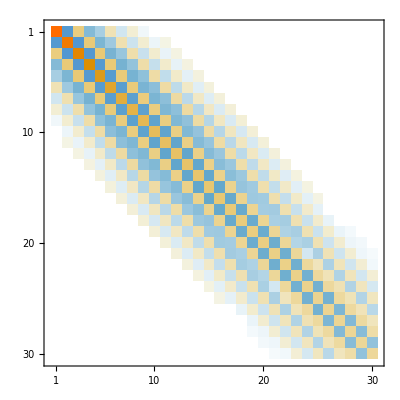

```mathematica
LoadBosonicOperators[nmax = 30];
ϵ = 0.8;
γ = 1.0;
nb = 3.0;
H = a†.a +ϵ (a + a†);
𝒟 = γ(nb+1)LindbladToVec[a] + γ nb LindbladToVec[a†];
ℒ = UnitaryToVec[H] + 𝒟;
AbsoluteTiming[(ρ = SteadyState[ℒ])//Chop;]
ρ//MatrixPlot
```

{0.187309,Null}

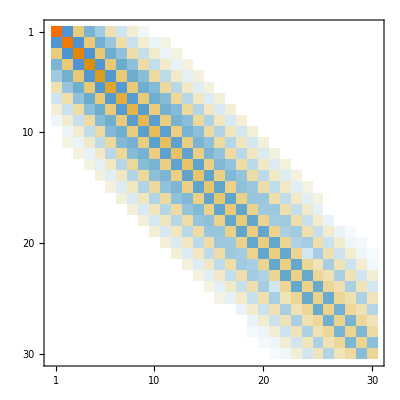

```mathematica
AbsoluteTiming[ρ2 = AnalyticalSteadyState2[ℒ]//Chop;]
ρ2//MatrixPlot
```

```mathematica
Tr[ρ]
```

1.

```mathematica
Tr[ρ2]
```

1.

```mathematica
ρ-ρ2//ChopCheck
```

{0}

```mathematica
(* Analytical Steady steate of an XXZ chain with 4 spins *)
LoadSpinChainMatrices[L=4,"a"] (* "a" makes the operators suitable for analytical calculations *) 
H = Sum[sx[i].sx[i+1] + sy[i].sy[i+1] + Δ sz[i].sz[i+1],{i,1,L-1}] + Sum[h sz[i],{i,1,L}];
ℒ = UnitaryToVec[H] + γ LindbladToVec[sp[1]] + γ LindbladToVec[sm[L]];
```

```mathematica
ρ = AnalyticalSteadyState[ℒ]
```

$Aborted

### Waiting time distributions (WTDs)

Waiting Time Distribution
Computes the general waiting time distribution between an initial jump 𝒥_i and a final jump 𝒥_f, with no jump Liouvillian ℒ_0

P_(f|i)(t) = (tr (𝒥_f e^(ℒ_0 t)𝒥_i ρ))/(tr(𝒥_i ρ))

The jump operators usually have the form 𝒥_k= L_k ρ L_k^†.
If no initial state ρ is input, it is assumed that ρ  = identity (maximally mixed state). This is convenient in the case of renewal processes, where ρ does not matter. 

For a Liouvillian decomposed as ℒ = ℒ_0 + ∑_k 𝒥_k, the WTD will be normalized as 

∑_f ∫ dt P_(f|i)(t) = 1 - P_no(∞), 

where P_no(∞) = lim_(t→ ∞) tr(e^(ℒ_0 t)ρ) is the no jump distribution. 
If after an infinite time, a jump definitely occurs, then P_no(∞)=0 and one gets the usual normalization. 

Moments of the waiting time
The moments are only implement for the case where the Liouvillian is split as ℒ = ℒ_0+ℒ_1 and the WTD is 

 P(t)=(tr (ℒ_1 e^(ℒ_0 t)ℒ_1 ρ))/(tr(ℒ_1 ρ))
 
The moments then read 

E(T^n) = ∫ dt P(t) t^n. 

For the general WTDs implemented above, it becomes a bit awkward to speak of moments since the distribution is not necessarily normalized. 
It also assumes that ℒ_0 has no zero eigenvalues (which means a jump must eventually occur). 

Implementation: 
Assuming that ℒ_0 has no dark subspaces, we get 

∫_0^∞ dt e^(ℒ_0 t)t^n = (-1)^(n+1)n! ℒ_0^(-(n+1))

Thus 

E(T^n) = (-1)^(n+1)n! (tr(ℒ_1 ℒ_0^(-(n+1))ℒ_1 ρ))/(tr(ℒ_1 ρ)).

But since ℒ_1=ℒ-ℒ_0 and ℒ is traceless, we can also write this as 

E(T^n) = (-1)^n n!  (tr(ℒ_0^-n ℒ_1 ρ))/(tr(ℒ_1 ρ))

The first moment, for instance, reads 

E(T) = -(tr(ℒ_0^-1 ℒ_1 ρ))/(tr(ℒ_1 ρ))

```mathematica
Clear[WaitingTimeDistribution];
WaitingTimeDistribution[t_,ℒ0_,𝒥i_,𝒥f_,ρ0_:None]:=Module[{ρ,d=√(Length@ℒ0)},
ρ=If[ρ0===None,Eye[d]/d,ρ0];
UnTr[𝒥f.MatrixExp[ℒ0 t,𝒥i.Vec[ρ]]]/UnTr[𝒥i.Vec[ρ]]]
```

```mathematica
Clear[WaitingTimeDistributionClassical]
WaitingTimeDistributionClassical[t_,ℒ0_,𝒥i_,𝒥f_,ρ0_:None]:=Module[{ρ,d=Length@ℒ0},
ρ=If[ρ0===None,ConstantArray[1,d]/d,ρ0];
Total[𝒥f.MatrixExp[ℒ0 t,𝒥i.ρ]]/Total[𝒥i.ρ]]
```

```mathematica
Clear[WaitingTimeMoments];
WaitingTimeMoments[ρ_?MatrixQ,ℒ_,ℒ1_,n_,reset_:True]:=Module[{f,α,ρ0},
f = LinearSolve[ℒ-ℒ1];
ρ0 = If[reset==True,(ℒ1.Vec[ρ])/UnTr[ℒ1.Vec[ρ]],Vec[ρ]];
α = Nest[f,ρ0,n];
(-1)^n n! UnTr[α]  
];

WaitingTimeMoments[ρ_?VectorQ,ℒ_,ℒ1_,n_,reset_:True]:=Module[{f,α,ρ0},
f = LinearSolve[ℒ-ℒ1];
ρ0 = If[reset==True,(ℒ1.ρ)/Total[ℒ1.ρ],ρ];
α = Nest[f,ρ0,n];
(-1)^n n! Total[α]  
]
```

#### Quantum model with a single jump

```mathematica
(* A quantum model *)
H = σz + σx;
c = √(1/2)σm;
ℒ = Liouvillian[H,{c}];
ℒ1 = JumpOp[c];
ℒ0 = ℒ-ℒ1;
```

```mathematica
P=WaitingTimeDistribution[t,ℒ0,ℒ1,ℒ1]
```

8 RootSum[64+258 #1+133 #1^2+4 #1^3+#1^4&,ⅇ^((t #1)/4)/(129+4 #1+2 #1^2)&]

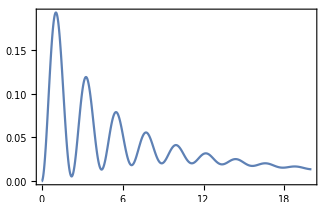

```mathematica
Plot[P,{t,0,20}]
```

```mathematica
NIntegrate[P,{t,0,∞}]
```

1.

```mathematica
WaitingTimeMoments[ρ,ℒ,ℒ1,1]//N
WaitingTimeMoments[ρ,ℒ,ℒ1,2]//N
WaitingTimeMoments[ρ,ℒ,ℒ1,3]//N
```

12.125

324.531

13304.3

```mathematica
NIntegrate[P t,{t,0,∞}]
NIntegrate[P t^2,{t,0,∞}]//Quiet
NIntegrate[P t^3,{t,0,∞}]//Quiet
```

12.125

324.531

13304.3

#### Quantum model with multiple jumps

```mathematica
(* A quantum model with 3 jump operators, but only two of them being monitored *)
H = σz + σx;
cdn = √(1/2)σm; (* emission *)
cup = √(1/3)σp;  (* absorption *)
cdeph = √(1/10)σz ;(* dephasing *)
ℒ = Liouvillian[H,{cdn,cup,cdeph}];
Jdn = JumpOp[cdn];
Jup = JumpOp[cup];
ℒ0 = ℒ-Jdn-Jup;
```

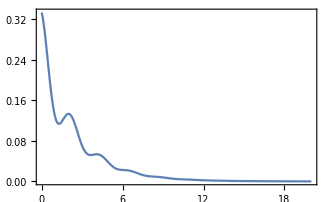

```mathematica
(* Waiting time distribution between an emission & an absorption *)
Pea=WaitingTimeDistribution[t,ℒ0,Jdn,Jup];
Plot[Pea,{t,0,20}]
```

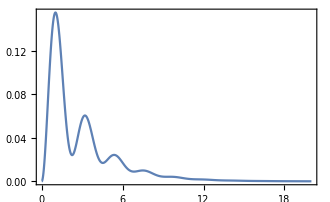

```mathematica
(* Waiting time distribution between two emissions (assuming that we still monitor the absorptions) *)
Pee=WaitingTimeDistribution[t,ℒ0,Jdn,Jdn];
Plot[Pee,{t,0,20}]
```

```mathematica
(* Normalization *)
NIntegrate[Pea,{t,0,∞}]+NIntegrate[Pee,{t,0,∞}]
```

1.

#### Autonomous Quantum Clock: classical version

Based on http://link.aps.org/doi/10.1103/PhysRevX.7.031022

Effective model as a Pauli (classical) Master equation

```mathematica
𝒲[d_,pup_,pdw_,Γ_]:=Module[{W},
W=DiagonalMatrix[ConstantArray[pup,{d-1}],-1] + DiagonalMatrix[ConstantArray[pdw,{d-1}],1] +DiagonalMatrix[ConstantArray[-pup-pdw,d]];
W⟦1,d⟧ = Γ;
W⟦d,d⟧ = W⟦d,d⟧-Γ+pup;
W⟦1,1⟧ = - pup;
W
]
𝒲1[d_,Γ_] := SparseArray[{{1,d}->Γ},{d,d}]
```

```mathematica
W=𝒲[5,Subscript[p, up],Subscript[p, dw],Γ]//mf;
W1 = 𝒲1[5,Γ]//mf;
```

(-p_up | p_dw | 0 | 0 | Γ
p_up | -p_dw-p_up | p_dw | 0 | 0
0 | p_up | -p_dw-p_up | p_dw | 0
0 | 0 | p_up | -p_dw-p_up | p_dw
0 | 0 | 0 | p_up | -Γ-p_dw)

(0 | 0 | 0 | 0 | Γ
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

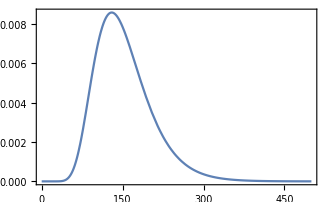

```mathematica
d = 20;
pup = 0.2;
pdw = 0.08;
Γ = 20;
P = WaitingTimeDistributionClassical[t,𝒲[d,pup,pdw,Γ]-𝒲1[d,Γ],𝒲1[d,Γ],𝒲1[d,Γ]];
Plot[P,{t,0,500}]
```

#### Autonomous Quantum Clock: full quantum version

Full quantum model, involving a d-level system + two qubits coupled to a hot & a cold bath

```mathematica
AutonomousClockWaitingTime[d_,ts_,{g_,γ_,Γ_},{Ec_,Ew_},{Tc_,Th_}]:=Module[{Eh,𝕀,σ,K,H0,Hint,cops,ℒ,ℒ1,ρ},
Eh = Ec + Ew;
𝕀 = Eye[d];
σ=({{0, 1}, {0, 0}});
Do[K[k] = Basis[d,k],{k,d}];

H0 = Ec kron[σ†.σ,σ0,𝕀] + Eh kron[σ0,σ†.σ,𝕀] + Sum[(k-1) Ew kron[σ0,σ0,out[K[k],K[k]]],{k,d}];

Hint = g Sum[kron[σ†,σ,out[K[k+1],K[k]]],{k,1,d-1}];
Hint = Hint + Hint†;
cops = {
√γ kron[σ,σ0,𝕀],
√(γ ⅇ^(-Ec/Tc))kron[σ†,σ0,𝕀],
√γ kron[σ0,σ,𝕀],
√(γ ⅇ^(-Eh/Th))kron[σ0,σ†,𝕀],
√Γ kron[σ0,σ0,out[K[1],K[d]]]};
ℒ = Liouvillian[H0+Hint ,cops];
ℒ1 = cf@JumpOp[cops⟦-1⟧];
ρ = kron[({{1/(1+Exp[-Ec/Tc]), 0}, {0, 1/(1+Exp[Ec/Tc])}}),({{1/(1+Exp[-Eh/Th]), 0}, {0, 1/(1+Exp[Eh/Th])}}),Proj[d,1,1]];  
Table[{t,WaitingTimeDistribution[t,ℒ-ℒ1,ℒ1,ℒ1]//Chop},{t,ts}]

]
```

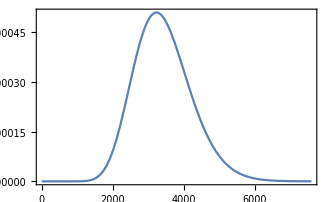

```mathematica
Pfull=AutonomousClockWaitingTime[
d = 18,
ts=linspace[0,7600,80],
{g=0.05,γ=0.3,Γ=0.05},
{Ec=20,Ew=1.0},
{Tc = 1.0,Th = 100}];
ListLinePlot[Pfull,PlotRange->All]
```

Comparison with the effective model

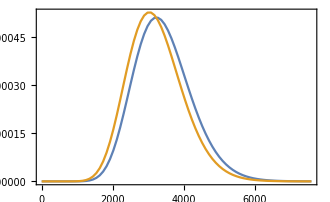

```mathematica
Zc = 1+ ⅇ^(-Ec/Tc);
Zh = 1+ ⅇ^(-Eh/Th);
Eh = Ec + Ew;
pdw = (4 g^2 Exp[-Ec/Tc])/(Zh Zc  γ (Zh+Zc));
pup = (4 g^2 Exp[-Eh/Th])/(Zh Zc  γ (Zh+Zc));

Peff =Table[{t, WaitingTimeDistributionClassical[t,SetPrecision[𝒲[d,pup,pdw,Γ]-𝒲1[d,Γ],20],SetPrecision[𝒲1[d,Γ],20],SetPrecision[𝒲1[d,Γ],20]]},{t,ts}];
ListLinePlot[{Pfull,Peff}]
```

### No-jump distribution

```mathematica
(* The actual no-jump distribution is computed as Subscript[P, no]=tr(ρf), where f is the output of "NoJumpDistributionFactor" *)
(* This is what the function NoJumpDistribution does *)

Clear[NoJumpDistributionFactor];
NoJumpDistributionFactor[ts_,ℒ0_]:=Module[{d = (Length[ℒ0])^(1/2)},
Table[UnTr@MatrixExp[ℒ0 t, kronV[Basis[d,j],Basis[d,i]]],{j,d},{i,d},{t,ts}]]

NoJumpDistributionFactor[ts_,H_,cops_]:=Module[{d = H,He,ℰ},
He = H - ⅈ/2 Total@Table[c†.c,{c,cops}];
Transpose[Table[
ℰ = MatrixExp[-ⅈ He t];
ℰ†.ℰ,{t,ts}],{3,1,2}]
]
```

```mathematica
Clear[NoJumpDistribution];
NoJumpDistribution[ρ_,f_]:=Vec[ρ].Flatten[f,1]//Chop

NoJumpDistribution[ρ_,ts_,ℒ0_]:=With[{f = NoJumpDistributionFactor[ts,ℒ0]},NoJumpDistribution[ρ,f]];

NoJumpDistribution[ρ_,ts_,H_,cops_]:=With[{f = NoJumpDistributionFactor[ts,H,cops]},NoJumpDistribution[ρ,f]];
```

#### Example usage and sanity checks

```mathematica
H = 0.5 σx/2;
c1 = √0.1 σm;
c2 = √0.3 σp;
ℒ = Liouvillian[H,{c1,c2}];
ℒ1 = JumpOp[c1]+JumpOp[c2];
ℒ0 = ℒ-ℒ1;
ρ = ({{0.3, 0.1ⅈ}, {-0.1ⅈ, 0.7}});
He = H - ⅈ/2(c1†.c1+c2†.c2);
ts=range[0,2,0.1];
```

```mathematica
f=NoJumpDistributionFactor[ts,ℒ0]
f2=NoJumpDistributionFactor[ts,H,{c1,c2}]
```

{{{1.,0.990046,0.980167,0.970339,0.960541,0.950754,0.940958,0.931137,0.921276,0.911361,0.90138,0.891324,0.881182,0.870947,0.860612,0.850172,0.839624,0.828965,0.818193,0.807307,0.796308},{0,0.-0.000245001 ⅈ,0.-0.000960021 ⅈ,0.-0.00211516 ⅈ,0.-0.00368066 ⅈ,0.-0.00562701 ⅈ,0.-0.00792498 ⅈ,0.-0.0105457 ⅈ,0.-0.0134607 ⅈ,0.-0.016642 ⅈ,0.-0.0200622 ⅈ,0.-0.0236944 ⅈ,0.-0.0275124 ⅈ,0.-0.0314906 ⅈ,0.-0.0356043 ⅈ,0.-0.0398293 ⅈ,0.-0.0441423 ⅈ,0.-0.0485209 ⅈ,0.-0.0529434 ⅈ,0.-0.0573891 ⅈ,0.-0.0618381 ⅈ}},{{0,0.+0.000245001 ⅈ,0.+0.000960021 ⅈ,0.+0.00211516 ⅈ,0.+0.00368066 ⅈ,0.+0.00562701 ⅈ,0.+0.00792498 ⅈ,0.+0.0105457 ⅈ,0.+0.0134607 ⅈ,0.+0.016642 ⅈ,0.+0.0200622 ⅈ,0.+0.0236944 ⅈ,0.+0.0275124 ⅈ,0.+0.0314906 ⅈ,0.+0.0356043 ⅈ,0.+0.0398293 ⅈ,0.+0.0441423 ⅈ,0.+0.0485209 ⅈ,0.+0.0529434 ⅈ,0.+0.0573891 ⅈ,0.+0.0618381 ⅈ},{1.,0.97045,0.941796,0.914036,0.887164,0.861172,0.836053,0.811798,0.788396,0.765836,0.744106,0.723192,0.703079,0.683753,0.665197,0.647396,0.630331,0.613984,0.598337,0.583372,0.569068}}}

{{{1.,0.990046,0.980167,0.970339,0.960541,0.950754,0.940958,0.931137,0.921276,0.911361,0.90138,0.891324,0.881182,0.870947,0.860612,0.850172,0.839624,0.828965,0.818193,0.807307,0.796308},{0,0.-0.000245001 ⅈ,0.-0.000960021 ⅈ,0.-0.00211516 ⅈ,0.-0.00368066 ⅈ,0.-0.00562701 ⅈ,0.-0.00792498 ⅈ,0.-0.0105457 ⅈ,0.-0.0134607 ⅈ,0.-0.016642 ⅈ,0.-0.0200622 ⅈ,0.-0.0236944 ⅈ,0.-0.0275124 ⅈ,0.-0.0314906 ⅈ,0.-0.0356043 ⅈ,0.-0.0398293 ⅈ,0.-0.0441423 ⅈ,0.-0.0485209 ⅈ,0.-0.0529434 ⅈ,0.-0.0573891 ⅈ,0.-0.0618381 ⅈ}},{{0,0.+0.000245001 ⅈ,0.+0.000960021 ⅈ,0.+0.00211516 ⅈ,0.+0.00368066 ⅈ,0.+0.00562701 ⅈ,0.+0.00792498 ⅈ,0.+0.0105457 ⅈ,0.+0.0134607 ⅈ,0.+0.016642 ⅈ,0.+0.0200622 ⅈ,0.+0.0236944 ⅈ,0.+0.0275124 ⅈ,0.+0.0314906 ⅈ,0.+0.0356043 ⅈ,0.+0.0398293 ⅈ,0.+0.0441423 ⅈ,0.+0.0485209 ⅈ,0.+0.0529434 ⅈ,0.+0.0573891 ⅈ,0.+0.0618381 ⅈ},{1.,0.97045,0.941796,0.914036,0.887164,0.861172,0.836053,0.811798,0.788396,0.765836,0.744106,0.723192,0.703079,0.683753,0.665197,0.647396,0.630331,0.613984,0.598337,0.583372,0.569068}}}

```mathematica
Table[Chop@UnTr@MatrixExp[ℒ0 t,Vec[ρ]],{t,ts}]
Table[Chop@Tr[MatrixExp[-ⅈ He t].ρ.MatrixExp[ⅈ He† t]],{t,ts}]
NoJumpDistribution[ρ,f]
NoJumpDistribution[ρ,f2]
```

{1.,0.976279,0.953115,0.930504,0.908441,0.886921,0.86594,0.845491,0.825568,0.806165,0.787276,0.768892,0.751007,0.733613,0.716701,0.700263,0.68429,0.668774,0.653705,0.639074,0.624872}

{1.,0.976279,0.953115,0.930504,0.908441,0.886921,0.86594,0.845491,0.825568,0.806165,0.787276,0.768892,0.751007,0.733613,0.716701,0.700263,0.68429,0.668774,0.653705,0.639074,0.624872}

{1.,0.976279,0.953115,0.930504,0.908441,0.886921,0.86594,0.845491,0.825568,0.806165,0.787276,0.768892,0.751007,0.733613,0.716701,0.700263,0.68429,0.668774,0.653705,0.639074,0.624872}

«1 more identical outputs»

### Emission & absorption spectra

The steady-state emission spectra of a system, with jump operator c, is defined as 

ℰ(ω) = ∫ dτ e^(-ⅈ ω τ) ⟨c†(τ)c(0)⟩ = ⟨b_out^†(ω)b_out(ω)⟩

The absorption spectra, on the other hand, is given by 

𝒜(ω) = ∫ dτ e^(-ⅈ ω τ) ⟨c(0)c†(τ)⟩

The 2-time correlation functions can be computed using the quantum regression theorem: 

⟨A(t+τ)B(t)⟩ = tr(A e^(ℒ τ)(Bρ_t)) 
or
⟨A(t)B(t+τ)⟩ = tr(B e^(ℒ τ)(ρ_t A)) 

with τ > 0. 

We thus get 

ℰ(ω) = - tr(c† 1/(ℒ-ⅈ ω)(c ρ)) - tr(c 1/(ℒ+ⅈ ω)(ρ c†))
and
𝒜(ω) = -tr(c† 1/(ℒ-ⅈ ω)(ρ c)) - tr(c 1/(ℒ+ⅈ ω)(c†ρ ))

For Quantum white noise, the output field correlation function is given by 

⟨b_out^†(t) b_out(t')⟩ = γ N δ(t-t') + γ (N+1) ⟨c†(t)c(t’)⟩ - γ N ⟨c(t’) c†(t)⟩

Hence, the power spectrum of the measured output field is actually (in the steady-state)

𝒮(ω) = ∫ dτ e^(-ι ω τ) ⟨b_out^†(τ)b_out(0)⟩ = γ N + γ (N+1) ℰ(ω) - γ N 𝒜(ω)

That is, it can be readily determined from the emission and absorption spectra.

```mathematica
Clear[EmissionSpectrum];
EmissionSpectrum[ρ_,ωs_,L_,c_]:=Module[{one,J,α,β,tab,tmp},

tab = Table[
α = LinearSolve[L-ⅈ ω Eye[Length@L], Vec[c.ρ]];
(*β = LinearSolve[L+ⅈ ω Eye[Length@L], Vec[ρ.c†]];*)
tmp= -Tr[c†.Unvec[α]](*-Tr[c.Unvec[β]]*);
tmp+tmp*
,{ω,ωs}];

tab//Chop
]
```

```mathematica
Clear[AbsorptionSpectrum];
AbsorptionSpectrum[ρ_,ωs_,L_,c_]:=Module[{one,J,α,β,tab,tmp},

tab = Table[
α = LinearSolve[L-ⅈ ω Eye[Length@L], Vec[ρ.c]];
(*β = LinearSolve[L+ⅈ ω Eye[Length@L], Vec[c†.ρ]];*)
tmp= -Tr[c†.Unvec[α]](*-Tr[c.Unvec[β]]*);
tmp+tmp*
,{ω,ωs}];

tab//Chop
]
```

#### Checking the symmetry of the 2 terms

Verifying that 

tr(c 1/(ℒ+ⅈ ω)(ρ c†)) = conjugate of tr(c† 1/(ℒ-ⅈ ω)(c ρ))

```mathematica
H = 0.8 σz + 0.7 σx + 0.6 σy + 0.1 σ0;
ℒ=Liouvillian[H,{σm,σp,σz},{0.3,0.8,0.1}];
ρ = SteadyState[ℒ]//mf;
ωs = linspace[-10,10,100];
```

(0.630436 | 0.131167-0.0363424 ⅈ
0.131167+0.0363424 ⅈ | 0.369564)

```mathematica
S = EmissionSpectrum[ρ,ωs,ℒ,σm]
```

{0.00785336,0.00814129,0.00844567,0.00876781,0.00910915,0.00947129,0.00985599,0.0102652,0.0107012,0.0111664,0.0116636,0.0121958,0.0127666,0.01338,0.0140405,0.0147533,0.0155244,0.0163607,0.0172701,0.0182621,0.0193478,0.0205401,0.0218548,0.0233107,0.0249307,0.0267431,0.0287829,0.0310941,0.0337322,0.036768,0.0402913,0.0444138,0.0492665,0.0549788,0.0616123,0.0690098,0.0765912,0.0834256,0.0890678,0.094482,0.101537,0.111851,0.12656,0.146709,0.173564,0.208569,0.252721,0.304856,0.358825,0.402374,0.423658,0.422771,0.412578,0.407921,0.418755,0.450964,0.509177,0.59811,0.721009,0.873104,1.02881,1.13371,1.13153,1.01951,0.851442,0.682951,0.540831,0.429673,0.345098,0.281006,0.232088,0.194301,0.164708,0.141207,0.122292,0.106876,0.0941662,0.0835753,0.0746642,0.0670997,0.060626,0.0550448,0.0502002,0.0459686,0.0422512,0.0389682,0.0360545,0.0334569,0.0311311,0.0290407,0.0271548,0.0254475,0.0238971,0.0224848,0.0211946,0.0200129,0.0189278,0.017929,0.0170076,0.0161558}

```mathematica
S2 = EmissionSpectrum2[ρ,ωs,ℒ,σm]
```

{0.00785336,0.00814129,0.00844567,0.00876781,0.00910915,0.00947129,0.00985599,0.0102652,0.0107012,0.0111664,0.0116636,0.0121958,0.0127666,0.01338,0.0140405,0.0147533,0.0155244,0.0163607,0.0172701,0.0182621,0.0193478,0.0205401,0.0218548,0.0233107,0.0249307,0.0267431,0.0287829,0.0310941,0.0337322,0.036768,0.0402913,0.0444138,0.0492665,0.0549788,0.0616123,0.0690098,0.0765912,0.0834256,0.0890678,0.094482,0.101537,0.111851,0.12656,0.146709,0.173564,0.208569,0.252721,0.304856,0.358825,0.402374,0.423658,0.422771,0.412578,0.407921,0.418755,0.450964,0.509177,0.59811,0.721009,0.873104,1.02881,1.13371,1.13153,1.01951,0.851442,0.682951,0.540831,0.429673,0.345098,0.281006,0.232088,0.194301,0.164708,0.141207,0.122292,0.106876,0.0941662,0.0835753,0.0746642,0.0670997,0.060626,0.0550448,0.0502002,0.0459686,0.0422512,0.0389682,0.0360545,0.0334569,0.0311311,0.0290407,0.0271548,0.0254475,0.0238971,0.0224848,0.0211946,0.0200129,0.0189278,0.017929,0.0170076,0.0161558}

```mathematica
S-S2//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Clear[EmissionSpectrum2];
EmissionSpectrum2[ρ_,ωs_,L_,c_]:=Module[{one,J,α,β,tab,tmp},

tab = Table[
α = LinearSolve[L-ⅈ ω Eye[Length@L], Vec[c.ρ]];
β = LinearSolve[L+ⅈ ω Eye[Length@L], Vec[ρ.c†]];
tmp= -Tr[c†.Unvec[α]]-Tr[c.Unvec[β]];
(*tmp+tmp**)
tmp
,{ω,ωs}];

tab//Chop
]
```

#### Example: Mollow Triplet in the fluorescence spectrum of a qubit

```mathematica
ℒ = Liouvillian[Ω/2 σx,{σm},{γ}];
ρ = AnalyticalSteadyState[ℒ]//mf;
```

(Ω^2/(γ^2+2 Ω^2) | -(ⅈ γ Ω)/(γ^2+2 Ω^2)
(ⅈ γ Ω)/(γ^2+2 Ω^2) | (γ^2+Ω^2)/(γ^2+2 Ω^2))

```mathematica
S=FCSEmissionSpectrum[ρ,{ω},ℒ,σm]//First//cf
```

(8 γ Ω^4 (2 (γ^2+ω^2)+Ω^2))/((γ^2+4 ω^2) (γ^2+2 Ω^2) (γ^4+4 (ω^2-Ω^2)^2+γ^2 (5 ω^2+4 Ω^2)))

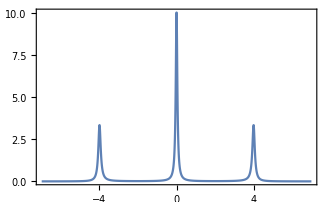

```mathematica
Plot[S/.{γ->0.1,Ω->4},{ω,-7,7}]
```

#### Emission spectrum of the tight-binding model

```mathematica
Clear[h,H,γ,ℒ,ρ];
h = TightBindingHamiltonian[4];
LoadFermionicOperators[4];
H = Sum[h⟦i,j⟧ cd[i].c[j],{i,4},{j,4}];
γ =0.01;
ℒ = N@Liouvillian[H,{cd[1],c[4]},{γ,γ}];
ρ = SteadyState[ℒ];
ωs = linspace[-2,4,100];
ee=EmissionSpectrum[ρ, ωs,ℒ,c[4]];
```

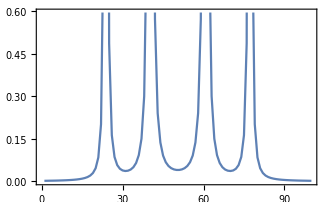

```mathematica
ListLinePlot[ee]
```

### Examples

#### Minimal 2-qubit engine

Based on https://arxiv.org/pdf/1010.6029.pdf and http://arxiv.org/abs/2106.13817

```mathematica
LoadSpinChainMatrices[2,"a"];
H0 = ϵ1 sp[1].sm[1] + ϵ2 sp[2].sm[2];
V = g(sp[1].sm[2]+sp[2].sm[1]);

cops = {
√γ1m sm[1],
√γ1p sp[1],
√γ2m sm[2],
√γ2p sp[2]
};
ℒ = Liouvillian[V,{sm[1],sp[1],sm[2],sp[2]},{γ1m,γ1p,γ2m,γ2p}]//cf;
```

```mathematica
ρ = AnalyticalSteadyState[ℒ]//Simplify//mf;
```

((4 g^2 (γ1p+γ2p)^2+γ1p γ2p (γ1m+γ1p+γ2m+γ2p)^2)/((γ1m+γ1p+γ2m+γ2p)^2 (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | 0 | 0 | 0
0 | (4 g^2 (γ1m+γ2m) (γ1p+γ2p)+γ1p γ2m (γ1m+γ1p+γ2m+γ2p)^2)/((γ1m+γ1p+γ2m+γ2p)^2 (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | (2 ⅈ g (γ1p γ2m-γ1m γ2p))/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | 0
0 | (2 ⅈ g (-γ1p γ2m+γ1m γ2p))/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | (4 g^2 (γ1m+γ2m) (γ1p+γ2p)+γ1m γ2p (γ1m+γ1p+γ2m+γ2p)^2)/((γ1m+γ1p+γ2m+γ2p)^2 (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | 0
0 | 0 | 0 | (4 g^2 (γ1m+γ2m)^2+γ1m γ2m (γ1m+γ1p+γ2m+γ2p)^2)/((γ1m+γ1p+γ2m+γ2p)^2 (4 g^2+(γ1m+γ1p) (γ2m+γ2p))))

```mathematica
𝒟1 = γ1m LindbladToVec[sm[1]] + γ1p LindbladToVec[sp[1]];
𝒟2 = γ2m LindbladToVec[sm[2]] + γ2p LindbladToVec[sp[2]];
Tr[V.Unvec[𝒟1.Vec[ρ]]]//Simplify
Tr[V.Unvec[𝒟2.Vec[ρ]]]//Simplify
```

0

0

```mathematica
W = ⅈ g (ϵ2-ϵ1) Tr[(sp[1].sm[2]-sp[2].sm[1]).ρ]//cf
```

(4 g^2 (-γ1p γ2m+γ1m γ2p) (ϵ1-ϵ2))/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p)))

```mathematica
Q1 = Tr[H0.Unvec[𝒟1.Vec[ρ]]]//Simplify
Q1 = ϵ1 (γ1p Tr[sm[1].sp[1].ρ]- γ1m Tr[sp[1].sm[1].ρ])//cf
```

(4 g^2 (γ1p γ2m-γ1m γ2p) ϵ1)/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p)))

(4 g^2 (γ1p γ2m-γ1m γ2p) ϵ1)/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p)))

```mathematica
Q2 = Tr[H0.Unvec[𝒟2.Vec[ρ]]]//Simplify
```

(4 g^2 (-γ1p γ2m+γ1m γ2p) ϵ2)/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p)))

```mathematica
W+Q1+Q2//cf
```

0

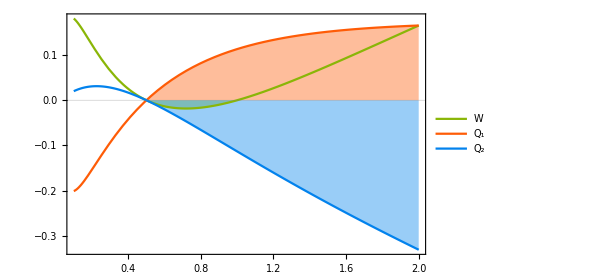

```mathematica
n1 = 1/(Exp[β1 ϵ1]-1);
n2 = 1/(Exp[β2 ϵ2]-1);
{c1,c2,c3} ={RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]};
rep = {γ1m->(n1+1),γ1p->n1,γ2m->n2+1,γ2p->n2,g->3};
(*Manipulate[Plot[Evaluate[{W,Q1,Q2}/.rep/.{ϵ1->1,β1->1/T1,β2->1/T2}],{ϵ2,0.1,2},
GridLines->{None,{0}},
PlotStyle->{c1,c2,c3},
ImageSize->450,
PlotLegends->legend[{"W","Q_1","Q_2"},{0.3,0.1},LegendLayout->Row],
Filling->{
1->{Axis,{Directive[c1,Opacity[0.4]],Opacity[0]}},
2->{Axis,{Opacity[0],Directive[c2,Opacity[0.4]]}},
3->{Axis,{Directive[c3,Opacity[0.4]],Opacity[0]}}}

],
{{T1,1},0.1,3},
{{T2,1/2},0.1,3}]*)

Plot[Evaluate[{W,Q1,Q2}/.rep/.{ϵ1->1,β1->1,β2->2}],{ϵ2,0.1,2},
GridLines->{None,{0}},
PlotStyle->{c1,c2,c3},
ImageSize->450,
PlotLegends->legend[{"W","Q_1","Q_2"},{0.3,0.1},LegendLayout->"Row"],
Filling->{
1->{Axis,{Directive[c1,Opacity[0.4]],Opacity[0]}},
2->{Axis,{Opacity[0],Directive[c2,Opacity[0.4]]}},
3->{Axis,{Directive[c3,Opacity[0.4]],Opacity[0]}}}
]
```

## Collision models

### Collision Map

```mathematica
Clear[CollisionMap];
CollisionMap[ρs0_,U_,ρa_,n_,output_:"system"]:=Module[{ds=Length@ρs0,da=Length@ρa},

Which[
output=="system",
NestList[PTr[U.kron[#,ρa].U†,{2},{ds,da}]&,ρs0,n],
output=="all",
NestList[
With[{ρsa=U.kron[#⟦1⟧,ρa].U†} , 
{PTr[ρsa,{2},{ds,da}],PTr[ρsa,{1},{ds,da}]}]&,{ρs0,ρa},n]
]
]
```

#### Example usage

```mathematica
ρs0 = ({{1, 0}, {0, 0}});
ρa = ({{0.4, 0}, {0, 0.6}});
U = PartialSWAP[0.5,1,2,2]//mf;
```

(0.5-0.866025 ⅈ | 0 | 0 | 0
0 | 0.-0.866025 ⅈ | 0.5 | 0
0 | 0.5 | 0.-0.866025 ⅈ | 0
0 | 0 | 0 | 0.5-0.866025 ⅈ)

```mathematica
mf/@CollisionMap[ρs0,U,ρa,10];
```

(1 | 0
0 | 0)

(0.85 | 0
0 | 0.15)

(0.7375 | 0
0 | 0.2625)

(0.653125 | 0
0 | 0.346875)

(0.589844 | 0
0 | 0.410156)

(0.542383 | 0
0 | 0.457617)

(0.506787 | 0
0 | 0.493213)

(0.48009 | 0
0 | 0.51991)

(0.460068 | 0
0 | 0.539932)

(0.445051 | 0
0 | 0.554949)

(0.433788 | 0
0 | 0.566212)

```mathematica
results=CollisionMap[ρs0,U,ρa,10,"all"]//Chop;
TableForm[Table[
{MatrixForm[results⟦i,1⟧],MatrixForm[results⟦i,2⟧]},
{i,10}],TableHeadings->{None,{"S","A"}}]
```

S | A
(1 | 0
0 | 0) | (0.4 | 0
0 | 0.6)
(0.85 | 0
0 | 0.15) | (0.55 | 0
0 | 0.45)
(0.7375 | 0
0 | 0.2625) | (0.5125 | 0
0 | 0.4875)
(0.653125 | 0
0 | 0.346875) | (0.484375 | 0
0 | 0.515625)
(0.589844 | 0
0 | 0.410156) | (0.463281 | 0
0 | 0.536719)
(0.542383 | 0
0 | 0.457617) | (0.447461 | 0
0 | 0.552539)
(0.506787 | 0
0 | 0.493213) | (0.435596 | 0
0 | 0.564404)
(0.48009 | 0
0 | 0.51991) | (0.426697 | 0
0 | 0.573303)
(0.460068 | 0
0 | 0.539932) | (0.420023 | 0
0 | 0.579977)
(0.445051 | 0
0 | 0.554949) | (0.415017 | 0
0 | 0.584983)

### Collision Model Steady-state

```mathematica
Clear[CollisionModelSteadyState]
CollisionModelSteadyState[U_,ρa_]:=Module[{da=Length@ρa,ds,ρ,𝒯,p},
ds = Length[U]/da;
ρ = Table[p[i,j],{i,ds},{j,ds}];
𝒯=Last@CoefficientArrays[Vec[PTr[U.kron[ρ,ρa].U†,{2},{ds,da}]],Vec[ρ]];
(*SteadyState[𝒯-Eye[ds^2]]*)
AnalyticalSteadyState[𝒯-Eye[ds^2]] (* "AnalyticalSteadyState handles multiple steady-states, by selecting one that is guaranteed physical *)
]
```

#### Example usage

```mathematica
ρa = ({{0.4, 0}, {0, 0.6}});
U = PartialSWAP[0.5,1,2,2];
CollisionModelSteadyState[U,ρa]//mf;
```

(0.4 | 0
0 | 0.6)

```mathematica
χ = {√0.3,√(1-0.3)};
LoadSpinChainMatrices[2];
U = MatrixExp[-ⅈ sx[1].sx[2]];
𝒯=CollisionModelSteadyState[U,out[χ,χ]]//mf;
```

(0.5 | 0
0 | 0.5)

### Coherent quantum absorber

```mathematica
Clear[CoherentQuantumAbsorber];
CoherentQuantumAbsorber[U_,χ_]:=Module[{da=Length@χ,ds,ρa,ρss,λ,f,g,V,ψt,ϕ,support,i,fχ,error},
ds = Length[U]/da;
ρa = out[χ,χ];
ρss = CollisionModelSteadyState[U,ρa];
{λ,f} = Eigsys[ρss];
ψt = Sum[√λ⟦i⟧kron[f⟦i⟧,f⟦i⟧],{i,ds}];

ϕ = kron[U,Eye[ds]].Sum[√λ⟦i⟧kron[f⟦i⟧,χ,f⟦i⟧],{i,ds}];

support = Select[{Range[1,ds],λ}ᵀ,Abs[#⟦2⟧]>10^-12&]⟦All,1⟧;
g=Table[1/(√λ⟦i⟧)kron[{f⟦i⟧*},Eye[ds da]].ϕ,{i,support}];
g = Join[g,NullSpace[g*]];

f = Join[Table[f⟦i⟧,{i,support}],Table[f⟦i⟧,{i,Complement[Range[1,ds],support]}]];

fχ = Table[kron[χ,f⟦i⟧],{i,support}];
fχ = Join[fχ,NullSpace[fχ*]];

V = Sum[kron[Eye[ds],out[fχ⟦i⟧,g⟦i⟧]],{i,ds^2}];

error=V.kron[U,Eye[ds]].Sum[√λ⟦i⟧kron[f⟦i⟧,χ,f⟦i⟧],{i,ds}]-Sum[√λ⟦i⟧kron[f⟦i⟧,χ,f⟦i⟧],{i,ds}]//Chop;
If[Total@Abs[error]>10^-12,Print["Apparently it did not work. The error was " <>ToString[error]]];
{V,ψt}
]
```

#### Example usage

```mathematica
χ = {√0.3,√(1-0.3)};
(*U = PartialSWAP[0.5,1,2,2];*)
LoadSpinChainMatrices[2];
U = MatrixExp[-ⅈ sx[1].sx[2]];

{V,ψt}=CoherentQuantumAbsorber[U,χ];
```

```mathematica
V†.V//mf;
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
PTr[out[ψt,ψt],{2}]//mf;
```

(0.5 | 0
0 | 0.5)

```mathematica
ψt
```

{0.707099+0.00241568 ⅈ,-8.25278×10^-6+0.00241568 ⅈ,-8.25278×10^-6+0.00241568 ⅈ,0.707099+0.00241568 ⅈ}

## Full counting statistics

### DrazinApply: Applies the Drazi inverse of an operator

```mathematica
(* Not yet sure which approach is more efficient. Found 1 example where DrazinApply does not work, but DrazinApply2 does. *)
```

```mathematica
DrazinInverse[ℒ_,ρ_]:=Module[{outie},
outie = Eye[Length@ℒ]  - out[Vec[ρ], Vec[Eye[Length@ρ]]];
outie.PseudoInverse[ℒ].outie
]
```

SetDelayed::write: Tag DrazinInverse in DrazinInverse[ℒ_,ρ_] is Protected.

$Failed

```mathematica
DrazinApply[ℒ_,y_]:=LinearSolve[Join[ℒ,{Vec@Eye[√(Length@ℒ)]}], Join[y ,{0}]]

DrazinApply2[ℒ_,ρv_,y_]:=Module[{z},
z = LinearSolve[ℒ, y-ρv UnTr[y]];
z - ρv UnTr[z]
]
```

#### Example usage

```mathematica
ℒ = Liouvillian[σz,{√γm σm,√γp σp}]//cf;
ρ = AnalyticalSteadyState[ℒ];
ℒD=DrazinInverse[ℒ,ρ]//cf//mf;
```

(-γm/(γm+γp)^2 | 0 | 0 | γp/(γm+γp)^2
0 | -2/(-4 ⅈ+γm+γp) | 0 | 0
0 | 0 | -2/(4 ⅈ+γm+γp) | 0
γm/(γm+γp)^2 | 0 | 0 | -γp/(γm+γp)^2)

ℒ^+ℒ= 1 - |ρ⟩⟨1|:

```mathematica
P0 = out[Vec[ρ],Vec[Eye[2]]];
P = Eye[4]-P0;
```

```mathematica
ℒD.ℒ-P//cf//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ℒD.P0//cf//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ℒD.P-ℒD//cf//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Comparison with the Moore-Penrose pseudo-inverse: it does not match. 
I have no idea what Mathematica does here. I think it is using SVD.

```mathematica
ℒMP=PseudoInverse[ℒ]//cf//mf;
```

(-γm/(2 (γm^2+γp^2)) | 0 | 0 | γm/(2 (γm^2+γp^2))
0 | -2/(-4 ⅈ+γm+γp) | 0 | 0
0 | 0 | -2/(4 ⅈ+γm+γp) | 0
γp/(2 (γm^2+γp^2)) | 0 | 0 | -γp/(2 (γm^2+γp^2)))

```mathematica
ℒD-P.ℒMP.P//cf//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Comparing with the integral formula

```mathematica
-Integrate[MatrixExp[ℒ t].(Eye[4]-out[Vec[ρ],Vec[Eye[2]]]),{t,0,∞},Assumptions->{γm>0,γp>0}]//mf;
```

(-γm/(γm+γp)^2 | 0 | 0 | γp/(γm+γp)^2
0 | -2/(-4 ⅈ+γm+γp) | 0 | 0
0 | 0 | -2/(4 ⅈ+γm+γp) | 0
γm/(γm+γp)^2 | 0 | 0 | -γp/(γm+γp)^2)

### Average current

```mathematica
Clear[FCSAverage];
FCSAverage[ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,res},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ];
ρv = Vec[ρ];
res=Table[Total@Table[μ⟦α,i⟧ UnTr[L⟦i⟧.ρv],{i,d}],{α,Length@μ}]//Chop;
If[Length@res==1,res⟦1⟧,res]
]
```

### Diffusion matrix

```mathematica
Clear[FCSDiffusionMatrix];
FCSDiffusionMatrix[ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
Jk = Table[UnTr[lop.ρv],{lop,L}];

M = Which[
type=="PD",μ.DiagonalMatrix[Jk].μᵀ,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

ℒα = μ.L;
Jα = UnTr[#.ρv]&/@ℒα//Chop;
ℒbig =Join[ℒ,{Vec@Eye[√(Length@ℒ)]}];
ws = Table[LinearSolve[ℒbig, Join[ℒα⟦i⟧.ρv-Jα⟦i⟧ ρv ,{0}]],{i,R}];
𝒟 = -Table[UnTr[ℒα⟦i⟧.ws⟦j⟧],{i,R},{j,R}];
𝒟=𝒟 + 𝒟ᵀ + M//Chop;
If[R===1,𝒟⟦1,1⟧,𝒟]
]
```

### Power spectrum

```mathematica
Clear[FCSPowerSpectrumEigen]
FCSPowerSpectrumEigen[ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
Jk = Table[UnTr[lop.ρv],{lop,L}];

M = Which[
type=="PD",μ.DiagonalMatrix[Jk].μᵀ,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

ℒα = μ.L;
Jα = UnTr[#.ρv]&/@ℒα//Chop;
{λ,Q} = Eigsys[ℒ];
λ = Drop[λ,-1];
x = (Qᵀ)⟦1;;-2⟧;
y=Inverse[Q]⟦1;;-2⟧;
(*Defined so that ℒ = Sum[λ⟦i⟧ out[x⟦i⟧,y⟦i⟧*],{i,Length[ℒ]-1}] *)

Υ = Table[UnTr[ℒα⟦α⟧.out[x⟦j⟧,y⟦j⟧*].ℒα⟦β⟧.ρv],{α,R},{β,R},{j,Length[λ]}];

If[R===1,
Function[M⟦1,1⟧ - Chop@Total@Table[1/(λ⟦j⟧-ⅈ #)Υ⟦1,1,j⟧+1/(λ⟦j⟧+ⅈ #)Υ⟦1,1,j⟧,{j,Length[λ]}] ],
Function[M -Table[Chop@Total@Table[1/(λ⟦j⟧-ⅈ #)Υ⟦β,α,j⟧+1/(λ⟦j⟧+ⅈ #)Υ⟦α,β,j⟧,{j,Length[λ]}] ,{α,R},{β,R}]]
]

]
```

```mathematica
Clear[FCSPowerSpectrumLinearSys]
FCSPowerSpectrumLinearSys[ωs_,ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮,v1,v2,𝕀},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
Jk = Table[UnTr[lop.ρv],{lop,L}];

M = Which[
type=="PD",μ.DiagonalMatrix[Jk].μᵀ,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

ℒα = μ.L;
(*Jα = UnTr[#.ρv]&/@ℒα//Chop;*)

𝕀 = Eye[Length@ℒ];
Table[
v1=Table[LinearSolve[ℒ - ⅈ ω 𝕀, ℒα⟦i⟧.ρv],{i,R}];
v2=Table[LinearSolve[ℒ + ⅈ ω 𝕀, ℒα⟦i⟧.ρv],{i,R}];
𝒮=M - Table[UnTr[ℒα⟦β⟧.v1⟦α⟧] + UnTr[ℒα⟦α⟧.v2⟦β⟧],{α,R},{β,R}];
{ω,If[R===1,𝒮⟦1,1⟧,𝒮]}
,{ω,ωs}]//Chop
]
```

```mathematica
Clear[FCSCoherence];
FCSCoherence[𝒮_,ω_]:=Abs[𝒮[ω]⟦1,2⟧]^2/(𝒮[ω]⟦1,1⟧ 𝒮[ω]⟦2,2⟧)
```

### g^(2) function

The general g^(2) function is related to the current two-point function as

F_αβ(τ) = E(δI_α(0) δI_β(τ))= M δ(τ) + J_α J_β  [g_αβ^(2)(τ) - 1]

Thus

g_αβ^(2)(τ) = ⟨1|ℒ_β e^ℒτ ℒ_α|ρ⟩/(J_α J_β) := (G_αβ^(2)(τ))/(J_α J_β)

where ℒ_α = ∑_k μ_k^α L_k ρ L_k^†

Notice that for homodyne detection, g^(2) is actually g^(1) (which is unnecessarily confusing, I know).

```mathematica
(* Without dividing by J^2 *)
Clear[FCSG2MEXP]
FCSG2MEXP[ts_,ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
ℒα = μ.L;
Jα = UnTr[#.ρv]&/@ℒα//Chop;

If[R===1,
Table[{t,(*1/Jα⟦1⟧^2*) UnTr[ℒα⟦1⟧.MatrixExp[ℒ t,ℒα⟦1⟧.ρv]]},{t,ts}],
Table[{t,Table[(*1/(Jα⟦α⟧Jα⟦β⟧)*) UnTr[ℒα⟦β⟧.MatrixExp[ℒ t,ℒα⟦α⟧.ρv]],{α,R},{β,R}]},{t,ts}]
]//Re
]
```

```mathematica
Clear[FCSg2Eigen]
FCSg2Eigen[ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];

ℒα = μ.L;
Jα = UnTr[#.ρv]&/@ℒα;
{λ,Q} = Eigsys[ℒ];
λ = Drop[λ,-1];
x = (Qᵀ)⟦1;;-2⟧;
y=Inverse[Q]⟦1;;-2⟧;
(*Defined so that ℒ = Sum[λ⟦i⟧ out[x⟦i⟧,y⟦i⟧*],{i,Length[ℒ]-1}] *)

Υ = Table[UnTr[ℒα⟦β⟧.out[x⟦j⟧,y⟦j⟧*].ℒα⟦α⟧.ρv],{α,R},{β,R},{j,Length[λ]}];

If[R===1,
Function[1+1/Jα⟦1⟧^2 Total@Table[Exp[λ⟦j⟧ #] Υ⟦1,1,j⟧,{j,Length[λ]}] ],
Function[Table[1+1/(Jα⟦α⟧Jα⟦β⟧)Total@Table[Exp[λ⟦j⟧ #]Υ⟦β,α,j⟧,{j,Length[λ]}] ,{α,R},{β,R}]]
]//Chop
]
```

```mathematica
Clear[FCSg2MEXP]
FCSg2MEXP[ts_,ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
ℒα = μ.L;
Jα = UnTr[#.ρv]&/@ℒα;

If[R===1,
Table[{t,1/Jα⟦1⟧^2 Tr[ℒα⟦1⟧.MatrixExp[ℒ t,ℒα⟦1⟧.ρv]]},{t,ts}], 
Table[{t,Table[1/(Jα⟦α⟧Jα⟦β⟧) UnTr[ℒα⟦β⟧.MatrixExp[ℒ t,ℒα⟦α⟧.ρv]],{α,R},{β,R}]},{t,ts}]
]//Re

]
```

#### Example usage

```mathematica
(* Resonantly driven qubit *)
Clear[γ,Ω,Δ];
H = 1/2 σx;
c = √γ σm;
ℒ = Liouvillian[H,{c}];
ρ = AnalyticalSteadyState[ℒ];
```

```mathematica
g2=FullSimplify[FCSg2MEXP[{τ},ρ,ℒ,{c}]⟦1,2⟧,{γ>0}]
```

1/(2 (-16+γ^2))ⅇ^(-1/4 (3 γ+√(-16+γ^2)) τ) (16-γ^2+3 γ √(-16+γ^2)+2 ⅇ^(1/4 (3 γ+√(-16+γ^2)) τ) (-16+γ^2)-ⅇ^(1/2 √(-16+γ^2) τ) (-16+γ^2+3 γ √(-16+γ^2)))

```mathematica
Integrate[g2-1,{τ,0,∞},Assumptions->γ>0]
```

-(3 γ)/(2+γ^2)

```mathematica
(* This formula can actually be written in a prettier way, in terms of the Rabi frequency Subscript[Ω, R]=√(1-γ^2/4) *)
g2pretty = 1 - ⅇ^(-3 γ τ/4)(Cos[ΩR τ]+ (3 √(1-ΩR^2))/ΩR Sin[ΩR τ]);
g2 - g2pretty/.ΩR->√(1-γ^2/16)/.{γ->0.3,τ->1.}//Chop
```

0

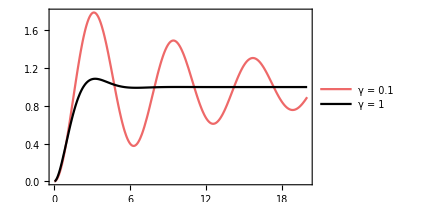

```mathematica
Plot[Evaluate@Table[g2,{γ,{0.1,1}}],{τ,0,20},
PlotStyle->{red,Black},
PlotLegends->legend[{"γ = 0.1", "γ = 1"},{0.7,0.2}]
]
```

```mathematica
(* Alternative way of computing g2 *)
γ = 0.3;
g2/.τ->0.3//Chop
FCSg2Eigen[ρ,ℒ,{c}][0.3]
```

0.0446302

0.0446302

### Two-point function F_αβ= M_αβ δ(τ)+J_α J_β(g_αβ^(2)-1)

```mathematica
Clear[FCSTwoPointFunctionEigen]
FCSTwoPointFunctionEigen[ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
(*Jk = Table[UnTr[lop.ρv],{lop,L}];*)
(*M = Which[
type=="PD",μ.DiagonalMatrix[Jk].μᵀ,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

*)
ℒα = μ.L;
Jα = UnTr[#.ρv]&/@ℒα//Chop;
{λ,Q} = Eigsys[ℒ];
λ = Drop[λ,-1];
x = (Qᵀ)⟦1;;-2⟧;
y=Inverse[Q]⟦1;;-2⟧;
(*Defined so that ℒ = Sum[λ⟦i⟧ out[x⟦i⟧,y⟦i⟧*],{i,Length[ℒ]-1}] *)

Υ = Table[UnTr[ℒα⟦β⟧.out[x⟦j⟧,y⟦j⟧*].ℒα⟦α⟧.ρv],{α,R},{β,R},{j,Length[λ]}];

If[R===1,
Function[ Chop@Total@Table[Exp[λ⟦j⟧ #] Υ⟦1,1,j⟧,{j,Length[λ]}] ],
Function[Table[Chop@Total@Table[Exp[λ⟦j⟧ #]Υ⟦β,α,j⟧,{j,Length[λ]}] ,{α,R},{β,R}]]
]
]
```

```mathematica
Clear[FCSTwoPointFunctionMEXP]
FCSTwoPointFunctionMEXP[ts_,ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
(*Jk = Table[UnTr[lop.ρv],{lop,L}];*)
(*M = Which[
type=="PD",μ.DiagonalMatrix[Jk].μᵀ,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

*)
ℒα = μ.L;
Jα = UnTr[#.ρv]&/@ℒα//Chop;
(*{λ,Q} = Eigsys[ℒ];
λ = Drop[λ,-1];
x = (Qᵀ)⟦1;;-2⟧;
y=Inverse[Q]⟦1;;-2⟧;
*)(*Defined so that ℒ = Sum[λ⟦i⟧ out[x⟦i⟧,y⟦i⟧*],{i,Length[ℒ]-1}] *)

(*Υ = Table[UnTr[ℒα⟦β⟧.out[x⟦j⟧,y⟦j⟧*].ℒα⟦α⟧.ρv],{α,R},{β,R},{j,Length[λ]}];*)

If[R===1,
Chop@Table[{t,UnTr[ℒα⟦1⟧.MatrixExp[ℒ t,ℒα⟦1⟧.ρv]]-Jα⟦1⟧^2},{t,ts}],
Chop@Table[{t,Table[UnTr[ℒα⟦β⟧.MatrixExp[ℒ t,ℒα⟦α⟧.ρv]]-Jα⟦α⟧Jα⟦β⟧,{α,R},{β,R}]},{t,ts}]
]
]
```

### Examples

#### Example usage

Single qubit model coupled to a bath, and with a coherent drive.

```mathematica
H = σz+0.8 σx;
c1 = √0.3 σm;
c2 = √0.65 σp;
ℒ = Liouvillian[H,{c1,c2}];
ρ = SteadyState[ℒ]//mf;
```

(0.641384 | 0.107068+0.0254285 ⅈ
0.107068-0.0254285 ⅈ | 0.358616)

Average
Average current of emission and absorptions

```mathematica
{FCSAverage[ρ,ℒ,c1],FCSAverage[ρ,ℒ,c2]}
```

{0.192415,0.233101}

Net current (absorptions - emissions)

```mathematica
FCSAverage[ρ,ℒ,{c1,c2},{-1,1}]
```

0.0406857

The syntax also accepts multiple current choices at a time (here, all 3 results above)

```mathematica
FCSAverage[ρ,ℒ,{c1,c2},{{1,0},{0,1},{-1,1}}]
```

{0.192415,0.233101,0.0406857}

Choices of μ are not restricted to 0,1,-1. Any value can be provided (used in e.g. defining energy currents)

Diffusion matrix
The syntax is identical to that of the average

```mathematica
{FCSDiffusionMatrix[ρ,ℒ,c1],FCSDiffusionMatrix[ρ,ℒ,c2]}
```

{0.125456,0.164035}

```mathematica
(* But if we input multiple currents together, this also yields the covariance between them *)
FCSDiffusionMatrix[ρ,ℒ,{c1,c2},{{1,0},{0,1}}]//mf;
```

(0.125456 | 0.0884773
0.0884773 | 0.164035)

Homodyne detection
Add “Homodyne” to convert results to that of homodyning. 
To add angle, redefine c1 c2

```mathematica
FCSAverage[ρ,ℒ,c1,1,"Homodyne"] (* factor of 1 is the optional choice of μ *)
FCSAverage[ρ,ℒ,c1 ⅇ^(ⅈ π/4),1,"Homodyne"]
```

0.117287

0.0632373

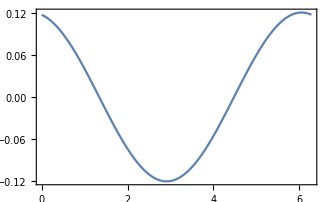

```mathematica
(* Homodyning the entire Bloch sphere *)
ListLinePlot[Table[{ϕ,FCSAverage[ρ,ℒ,c1 ⅇ^(ⅈ ϕ),1,"Homodyne"]},{ϕ,0,2π,0.01}]]
```

Same for the diffusion matrix

```mathematica
FCSDiffusionMatrix[ρ,ℒ,{c1,c2},{{1,0},{0,1}},"Homodyne"]//mf;
```

(1.32407 | 0.448941
0.448941 | 1.6195)

Power Spectrum also has the same syntax. 
But there are two options: 
- FCSPowerSpectrumEigen[] diagonalizes ℒ and returns a function of ω, which is then quick to evaluate. 
-  FCSPowerSpectrumLinearSys[] requires a specific list of frequencies “ωs” and operates by solving linear systems.

```mathematica
𝒮=FCSPowerSpectrumEigen[ρ,ℒ,{c1,c2},{{1,0},{0,1}}]
```

M$114261-Table[Total[Table[Υ$114261⟦β,α,j⟧/(λ$114261⟦j⟧-ⅈ #1)+Υ$114261⟦α,β,j⟧/(λ$114261⟦j⟧+ⅈ #1),{j,Length[λ$114261]}]],{α,R$114261},{β,R$114261}]&

```mathematica
(* Evaluate at specific frequencies *)
𝒮[5.0]//mf;
```

(0.18864 | 0.00532234-0.0111098 ⅈ
0.00532234+0.0111098 ⅈ | 0.227761)

```mathematica
FCSPowerSpectrumLinearSys[{5.0},ρ,ℒ,{c1,c2},{{1,0},{0,1}}]
%⟦1,2⟧//mf;
```

{{5.,{{0.18864-1.0842×10^-19 ⅈ,0.00532234-0.0111098 ⅈ},{0.00532234+0.0111098 ⅈ,0.227761-4.33681×10^-19 ⅈ}}}}

(0.18864 | 0.00532234-0.0111098 ⅈ
0.00532234+0.0111098 ⅈ | 0.227761)

```mathematica
𝒮[3.]⟦1,1⟧
```

0.17337-4.89412×10^-13 ⅈ

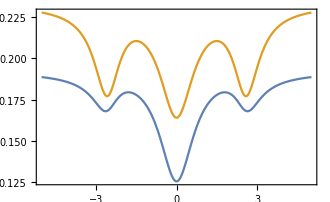

```mathematica
Plot[{
Evaluate@Re[𝒮[ω]⟦1,1⟧],
Evaluate@Re[𝒮[ω]⟦2,2⟧]
},{ω,-5,5}]
```

The “coherence” in the language of signal processing is 𝒞_xy(ω) = (|𝒮_xy(ω)|^2)/(𝒮_xx(ω)𝒮_yy(ω))
https://en.wikipedia.org/wiki/Coherence_(signal_processing)

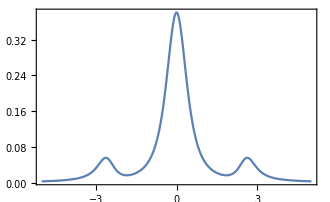

```mathematica
Plot[{
Evaluate@Re[Abs[𝒮[ω]⟦1,2⟧]^2/(𝒮[ω]⟦1,1⟧ 𝒮[ω]⟦2,2⟧)]
},{ω,-5,5},PlotRange->All]
```

#### Example: Reproducing Fig. 2(a) of arXiv 2103.07791

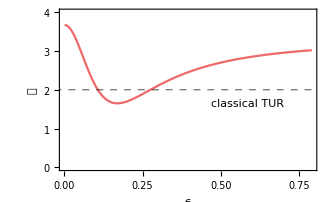

```mathematica
Clear[γu,γl,nu,nl,Δ,ϵ,σ];
γu = 2.0;
γl = 0.1;
nl = 5.0;
nu = 0.027; 
Δ = 0.0;

Do[σ[i,j] = Proj[3,i+1,j+1],{i,0,2},{j,0,2}];
H =  -Δ σ[1,1] + ϵ(σ[1,0] + σ[0,1]);
cops = {√(γl (nl+1))σ[0,2],√(γl nl)σ[2,0],√(γu(nu+1))σ[1,2],√(γu nu)σ[2,1]};
ℒ = Liouvillian[H,cops];
ρ = AnalyticalSteadyState[ℒ];
𝒬=Table[
ave = FCSAverage[ρ,ℒ,cops,{-1,1,0,0}];
var=FCSDiffusionMatrix[ρ,ℒ,cops,{-1,1,0,0}];
{ϵ,Log[(nl(nu+1))/(nu(nl+1))] var/ave},{ϵ,0.001,0.8,0.01}];
ListLinePlot[𝒬,PlotRange->{0,4},
GridLines->{None,{2}},
GridLinesStyle->Directive[Black, Dashed],
PlotStyle->red,
FrameLabel->{"ϵ","𝒬"},
Epilog->Text["classical TUR",Scaled[{0.73,0.42}]]
]
```

#### Example: “Mollow Triplet”; comparison with the emission & absorption spectra

I’m actually not sure this is really the Mollow triplet, since that refers to the emission spectrum and here I am plotting the coherence (in the signal processing sense)

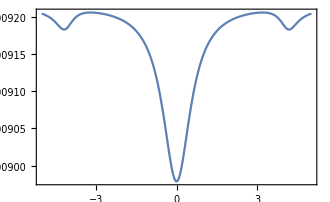
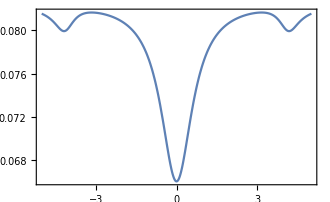
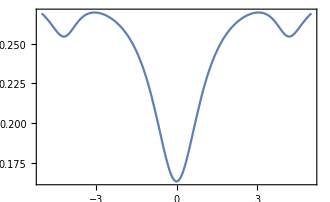
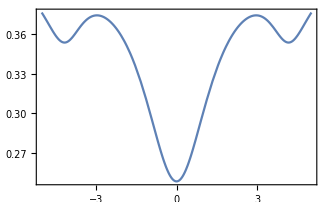

```mathematica
γs = {0.01,0.1,0.5,1.};
f = 0.7;
Clear[𝒮,ℰ,𝒮h,𝒜];
Do[
H =(*σz+*) 1.8 σz+σx;
c1 = √γ σm;

ℒ = Liouvillian[H,{c1,c2}];
ρ = SteadyState[ℒ];
𝒮[γ]=FCSPowerSpectrumEigen[ρ,ℒ,{c1,c2},{{1,0},{0,1}}(*,"Homodyne"*)];
𝒮h[γ]=FCSPowerSpectrumEigen[ρ,ℒ,{c1,c2},{{1,0},{0,1}},"Homodyne"];
ℰ[γ]=EmissionSpectrum[ρ,{ω},ℒ,√γ σm];
𝒜[γ]=AbsorptionSpectrum[ρ,{ω},ℒ,√γ σm];
,{γ,γs}]
Table[Plot[{
Re@𝒮[γ][ω]⟦1,1⟧
},{ω,-5,5},PlotRange->All],{γ,γs}]
```

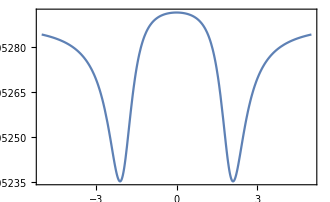

```mathematica
γ = 0.01;
Plot[{
Re@𝒮[γ][ω]⟦1,1⟧
},{ω,-5,5},PlotRange->All]
```

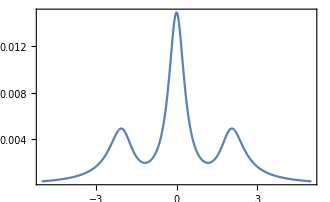
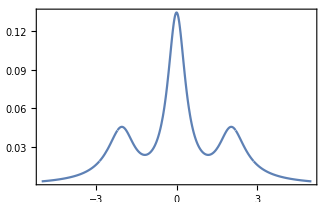
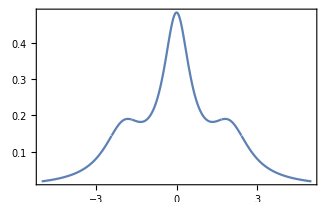
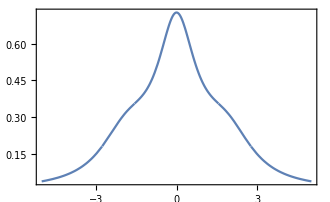

```mathematica
Table[Plot[ℰ[γ],{ω,-5,5}],{γ,γs}]
```

```mathematica
Plot[S/.{γ->0.1,Ω->4},{ω,-7,7}]
```

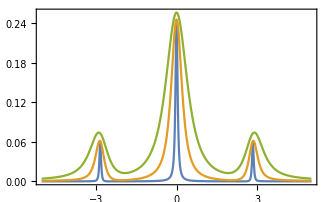

```mathematica
γs = {0.1,0.5,1.};
f = 0.7;
Clear[𝒮];
Do[
H =σz+ σx;
c1 = √(γ (1-f))σm;
c2 = √(γ f)σp;

ℒ = Liouvillian[H,{c1,c2}];
ρ = SteadyState[ℒ];
𝒮[γ]=FCSPowerSpectrumEigen[ρ,ℒ,{c1,c2},{{1,0},{0,1}}];
,{γ,γs}]
Plot[{
Evaluate@Table[Re[Abs[𝒮[γ][ω]⟦1,2⟧]^2/(𝒮[γ][ω]⟦1,1⟧ 𝒮[γ][ω]⟦2,2⟧)],{γ,γs}]
},{ω,-5,5},PlotRange->All]
```

Part::partd: Part specification 𝒮[1][-4.9998]⟦1,1⟧ is longer than depth of object.

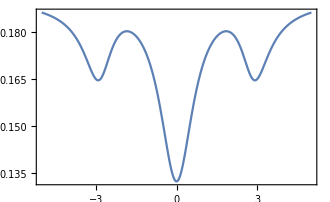

```mathematica
Plot[{
Evaluate@Table[Re@𝒮[γ][ω]⟦1,1⟧ ,{γ,γs⟦3⟧}]
},{ω,-5,5},PlotRange->All]
```

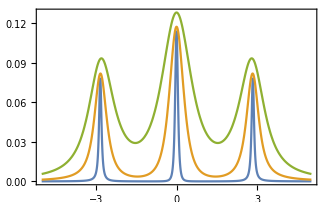

```mathematica
γs = {0.1,0.5,1.};
f = 0.7;
Clear[𝒮];
Do[
H =σz+ σx;
c1 = √(γ (1-f))σm;
c2 = √(γ f)σp;

ℒ = Liouvillian[H,{c1,c2}];
ρ = SteadyState[ℒ];
𝒮[γ]=FCSPowerSpectrumEigen[ρ,ℒ,{c1,c2},{{1,0},{0,1}},"Homodyne"];
,{γ,γs}]
Plot[{
Evaluate@Table[Re[Abs[𝒮[γ][ω]⟦1,2⟧]^2/(𝒮[γ][ω]⟦1,1⟧ 𝒮[γ][ω]⟦2,2⟧)],{γ,γs}]
},{ω,-5,5},PlotRange->All]
```

#### Ex: Mollow Triplet

```mathematica
Clear[γ,Ω,Δ];
H = Δ/2 σz+σx;
c = √γ σm;
ℒ = Liouvillian[H,{σm},{γ}];
ρ = AnalyticalSteadyState[ℒ]//mf;
```

(4/(8+γ^2+4 Δ^2) | -(2 ⅈ (γ-2 ⅈ Δ))/(8+γ^2+4 Δ^2)
(2 ⅈ (γ+2 ⅈ Δ))/(8+γ^2+4 Δ^2) | (4+γ^2+4 Δ^2)/(8+γ^2+4 Δ^2))

```mathematica
J=cf@FCSAverage[ρ,ℒ,{c}]
```

(4 γ)/(8+γ^2+4 Δ^2)

```mathematica
S = FullSimplify[FCSPowerSpectrumLinearSys[{ω},ρ,ℒ,{c}]⟦1,2⟧,γ>0]
```

(4 γ (γ^6+16 ω^2 (4+Δ^2-ω^2)^2+γ^4 (-8+8 Δ^2+9 ω^2)+8 γ^2 (8+2 Δ^4-8 ω^2+3 ω^4-3 Δ^2 (-4+ω^2))))/((8+γ^2+4 Δ^2) (γ^3+5 ⅈ γ^2 ω+4 γ (2+Δ^2-2 ω^2)+4 ⅈ ω (4+Δ^2-ω^2)) (γ^3-5 ⅈ γ^2 ω+4 γ (2+Δ^2-2 ω^2)+4 ⅈ ω (-4-Δ^2+ω^2)))

```mathematica
g2=FCSG2MEXP[{τ},ρ,ℒ,{c}]⟦1,2⟧;
```

```mathematica
Fτ = FCSTwoPointFunctionMEXP[{τ},ρ,ℒ,{c}]⟦1,2⟧;
```

```mathematica
𝒲=FullSimplify[ToRadicals@FullSimplify[WaitingTimeDistribution[ρ,ℒ,JumpOp@c,t],{γ>0}],{γ>0,t>0,Δ>0}]
```

(8 ⅇ^(-(t γ)/2) γ (-Cos[(t √(16-γ^2+4 Δ^2+√(γ^4+8 γ^2 (-4+Δ^2)+16 (4+Δ^2)^2)))/(2 √2)]+Cosh[(t √(γ^2-4 (4+Δ^2)+√(γ^4+8 γ^2 (-4+Δ^2)+16 (4+Δ^2)^2)))/(2 √2)]))/(√(γ^4+8 γ^2 (-4+Δ^2)+16 (4+Δ^2)^2))

```mathematica
Clear[γ,Δ];
Manipulate[
Grid[{{
Plot[Evaluate[Re@Fτ/.{γ->γγ,Δ->ΔΔ}],{τ,0,15/ γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","F(τ)"},ImageSize->300],
Plot[S/.{γ->γγ,Δ->ΔΔ},{ω,-20 γγ,20γγ},GridLines->Evaluate[{{-√(4+Δ^2),√(4+Δ^2)},{(4 γ)/(8+γ^2+4 Δ^2)}}/.{γ->γγ,Δ->ΔΔ}],GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"ω/γ","S(ω)"},ImageSize->300],
Plot[𝒲/.{γ->γγ,Δ->ΔΔ},{t,0,15 /γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","𝒲"},ImageSize->300]
}}],{{γγ,1},0.1,5},{{ΔΔ,0},0.,5}]
```

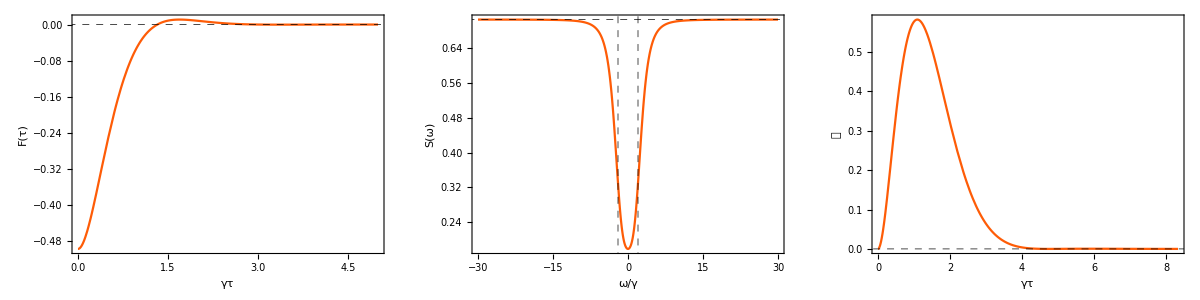
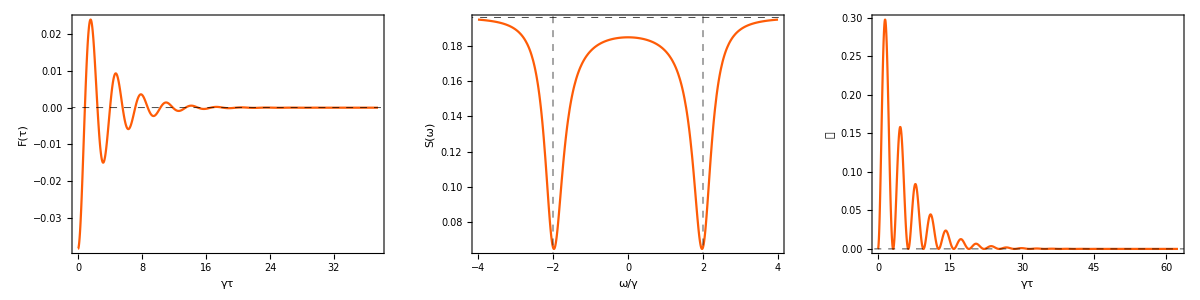
-Graphics-γ/Ω=3


-Graphics-γ/Ω=0.4

```mathematica
γγ = 3.0;
ΔΔ = 0.0;
plt1=Grid[{{
Plot[Evaluate[Re@Fτ/.{γ->γγ,Δ->ΔΔ}],{τ,0,15/ γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","F(τ)"},ImageSize->300],
Plot[S/.{γ->γγ,Δ->ΔΔ},{ω,-10 γγ,10γγ},GridLines->Evaluate[{{-√(4+Δ^2),√(4+Δ^2)},{(4 γ)/(8+γ^2+4 Δ^2)}}/.{γ->γγ,Δ->ΔΔ}],GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"ω/γ","S(ω)"},ImageSize->300],
Plot[𝒲/.{γ->γγ,Δ->ΔΔ},{t,0,25 /γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","𝒲"},ImageSize->300]
}}];
γγ = 0.4;
ΔΔ = 0.0;
plt2=Grid[{{
Plot[Evaluate[Re@Fτ/.{γ->γγ,Δ->ΔΔ}],{τ,0,15/ γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","F(τ)"},ImageSize->300],
Plot[S/.{γ->γγ,Δ->ΔΔ},{ω,-10 γγ,10γγ},GridLines->Evaluate[{{-√(4+Δ^2),√(4+Δ^2)},{(4 γ)/(8+γ^2+4 Δ^2)}}/.{γ->γγ,Δ->ΔΔ}],GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"ω/γ","S(ω)"},ImageSize->300],
Plot[𝒲/.{γ->γγ,Δ->ΔΔ},{t,0,25 /γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","𝒲"},ImageSize->300]
}}];
Grid[{{Labeled[plt1,Style["γ/Ω=3",22,FontFamily->"Times"],Top]},{},{},{Labeled[plt2,Style["γ/Ω=0.4",22,FontFamily->"Times"],Top]}}]
```

```mathematica
ρt=Unvec@MatrixExp[ℒ t,Vec[Proj[2,2]]];
{sx,sy,sz} = {Tr[σx.ρt],Tr[σy.ρt],Tr[σz.ρt]};
Show[BlochSphere[],
ParametricPlot3D[{sx,sy,sz},{t,0,20},PlotStyle->Black,PlotRange->All],PlotRange->All]
```

-Graphics3D-

#### Example: homodyne spectrum of squeezing in a parametric amplifier

Based on chapter 7 of Walls & Milburn. 
Computes equations 7.61 & 7.62.

(there is a factor of 2 different, which I believe is related to the way they define the quadratures)

```mathematica
LoadBosonicOperators[nmax = 40];
ωs = range[-5,5,0.1]+0.02;
ϵ = 0.4;
γ = 2;
H = (ⅈ ϵ)/2 (a†.a†-a.a);
cop = √γ a;
ℒ = Liouvillian[H,{cop}];
ρ = SteadyState[ℒ];
```

```mathematica
Sx = FCSPowerSpectrumLinearSys[ωs,ρ,ℒ,{a},1,"Homodyne"];
Sy = FCSPowerSpectrumLinearSys[ωs,ρ,ℒ,{ⅈ a},1,"Homodyne"];
```

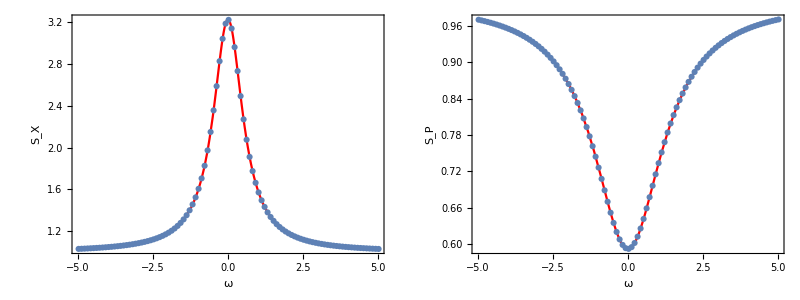

```mathematica
Grid@{{Show[
Plot[1+ (γ ϵ)/((γ/2-ϵ)^2+ω^2),{ω,-5,5},PlotStyle->Red],
ListLinePlot[Sx,Joined->False,PlotMarkers->Automatic],
FrameLabel->{"ω","S_X"}
],
Show[
Plot[1- (γ ϵ)/((γ/2+ϵ)^2+ω^2),{ω,-5,5},PlotStyle->Red],
ListLinePlot[Sy,Joined->False,PlotMarkers->Automatic],
FrameLabel->{"ω","S_P"}
]}}
```

#### Algebraic method in Gernot’s notes

ℒp = ℒ’(χ=0)
ℒpp = ℒ’’(χ=0)

```mathematica
GernotDiffusionCoefficient[ρ_,ℒ_,ℒp_,ℒpp_]:=Module[{ℐ,d,ℒ2,b,σ,S1,S2},
ℐ = -ⅈ Tr[Unvec[ℒp.Vec[ρ]]];
d = Length@ℒ;
ℒ2 =Join[ℒ,{Vec@Eye[√d]}];
b = Join[ⅈ ℐ Vec[ρ] - ℒp.Vec[ρ],{0}];
σ = LinearSolve[ℒ2,b];
S1 = -Tr[Unvec[ℒpp.Vec[ρ]]];
S2 =-2Tr[Unvec[ℒp.σ]];
S1+S2//Chop
]
```

```mathematica
Clear[γu,γl,nu,nl,Δ,ϵ,σ];
γu = 2.0;
γl = 0.1;
nl = 5.0;
nu = 0.027; 
Δ = 0.0;
ϵ = 0.3;

Do[σ[i,j] = Proj[3,i+1,j+1],{i,0,2},{j,0,2}];
H =  -Δ σ[1,1] + ϵ(σ[1,0] + σ[0,1]);
cops = {√(γl (nl+1))σ[0,2],√(γl nl)σ[2,0],√(γu(nu+1))σ[1,2],√(γu nu)σ[2,1]};
ℒ = Liouvillian[H,cops];
ρ = AnalyticalSteadyState[ℒ];
```

```mathematica
FCSDiffusionMatrix[ρ,ℒ,cops,{-1,1,0,0}]
```

0.080599

```mathematica
FCSPowerSpectrumEigen[ρ,ℒ,cops,{-1,1,0,0}][0]
```

0.080599

```mathematica
ℒp = -ⅈ JumpOp[cops⟦1⟧]+ⅈ JumpOp[cops⟦2⟧];
ℒpp = - JumpOp[cops⟦1⟧]- JumpOp[cops⟦2⟧];
GernotDiffusionCoefficient[ρ,ℒ,ℒp,ℒpp]
```

0.080599

#### Resonant qubit: g^(2) and S(ω)

Reproducing FIg. 1 of Mølmer’sSx =  Phys. Rev. A. 94 032103 (2016)

```mathematica
Clear[γ,Ω,Δ];
H = Ω/2 σx;
c = √γ σm;
ℒ = Liouvillian[H,{σm},{γ}];
ρ = AnalyticalSteadyState[ℒ]//mf;
```

(Ω^2/(γ^2+2 Ω^2) | -(ⅈ γ Ω)/(γ^2+2 Ω^2)
(ⅈ γ Ω)/(γ^2+2 Ω^2) | (γ^2+Ω^2)/(γ^2+2 Ω^2))

```mathematica
FCSAverage[ρ,ℒ,{c},1,"Homodyne"]//cf
FCSAverage[ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Homodyne"]//cf
```

0

-(2 γ^(3/2) Ω)/(γ^2+2 Ω^2)

```mathematica
G2x=FCSG2MEXP[{τ},ρ,ℒ,{c},1,"Homodyne"]⟦1,2⟧//cf
```

(2 ⅇ^(-(γ τ)/2) γ Ω^2)/(γ^2+2 Ω^2)

```mathematica
G2y=FCSG2MEXP[{τ},ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Homodyne"]⟦1,2⟧//cf
```

1/((γ^2-16 Ω^2) (γ^2+2 Ω^2)^2)ⅇ^(-1/4 τ (3 γ+√(γ^2-16 Ω^2))) γ Ω^2 (4 ⅇ^(1/4 τ (3 γ+√(γ^2-16 Ω^2))) γ^2 (γ-4 Ω) (γ+4 Ω)+γ^3 √(γ^2-16 Ω^2)-ⅇ^(1/2 τ √(γ^2-16 Ω^2)) γ^3 √(γ^2-16 Ω^2)-10 γ Ω^2 √(γ^2-16 Ω^2)+10 ⅇ^(1/2 τ √(γ^2-16 Ω^2)) γ Ω^2 √(γ^2-16 Ω^2)-(1+ⅇ^(1/2 τ √(γ^2-16 Ω^2))) (γ^4-18 γ^2 Ω^2+32 Ω^4))

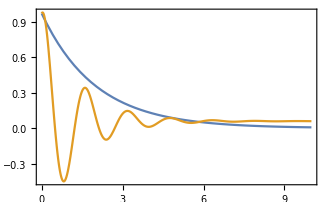

```mathematica
Plot[Evaluate[{G2x,G2y}/.{γ->1,Ω->4}],{τ,0,10}]
```

```mathematica
Sx = FullSimplify[FCSPowerSpectrumLinearSys[{ω},ρ,ℒ,{c},1,"Homodyne"]⟦1,2⟧,γ>0]
Sy = FullSimplify[FCSPowerSpectrumLinearSys[{ω},ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Homodyne"]⟦1,2⟧,γ>0]
```

(γ^4+8 ω^2 Ω^2+2 γ^2 (2 ω^2+5 Ω^2))/((γ^2+4 ω^2) (γ^2+2 Ω^2))

(γ^6+γ^4 (5 ω^2-2 Ω^2)+8 (-ω^2 Ω+Ω^3)^2+γ^2 (4 ω^4-6 ω^2 Ω^2+44 Ω^4))/((γ^2+2 Ω^2) (γ^4+4 (ω^2-Ω^2)^2+γ^2 (5 ω^2+4 Ω^2)))

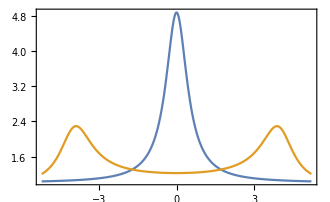

```mathematica
Plot[Evaluate[{Sx,Sy} /.{γ->1,Ω->4}],{ω,-5.2 ,5.2},PlotRange->{0.8,All}]
```

#### g^(2) function for a single qubit in a bad cavity

Based on Rice & Carmichael, IEEE JOURNAL OF QUANTUM ELECTRONICS, VOL . 24. NO . 7, JULY 1988

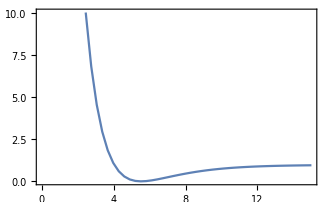

```mathematica
LoadBosonicOperators[nmax = 6];
ϵ = 0.01;
g = 3;
κ = 25 ;
γ = 1/5 ;
H = ϵ kron[a+a†,σ0] + g (kron[a†,σm] + kron[a,σp]);
cops = {√(2κ)kron[a,σ0],√γ kron[𝕀,σm]};
ℒ=Liouvillian[H,cops];
ρ =AnalyticalSteadyState[ℒ];

ts = linspace[0,15,50];
g2=FCSg2MEXP[ts,ρ,ℒ,√(2κ)kron[a,σ0]];
ListLinePlot[g2,PlotRange->{0,10}]
```

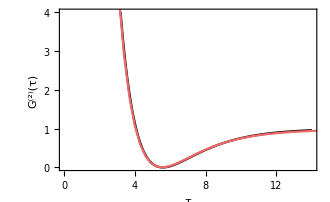

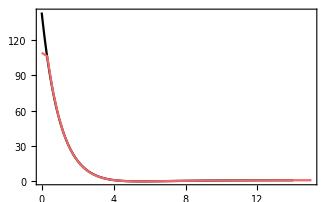

```mathematica
(* Comparison with Eq. (41) of Rice & Carmichael *)
g2RiceCarmichael[ϵ_,g_,κ_,γ_]:=Module[{𝒞 = g^2/(κ γ),ns = γ^2/(8 g^2),μ = 2κ/γ,Y = ϵ/(κ √ns),Ω,τp},
Ω = 1/4(1-(8 Y^2)/(1+2𝒞)^2)^(1/2);
τp = γ (1+2𝒞) τ;

(1-4 𝒞^2 ⅇ^(-τp/2))^2]

Show[
Plot[g2RiceCarmichael[ϵ,g,κ,γ],{τ,0,14},PlotRange->{0,4},PlotStyle->Black],
ListLinePlot[g2,PlotStyle->red],
FrameLabel->{"τ","G^(2)(τ)"}
]

Show[
Plot[g2RiceCarmichael[ϵ,g,κ,γ],{τ,0,14},PlotRange->All,PlotStyle->Black],
ListLinePlot[g2,PlotStyle->red,PlotRange->All]]
```

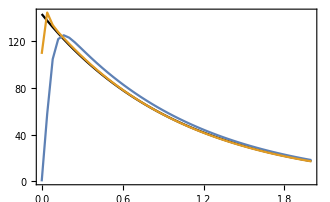

```mathematica
(* What happens if we approximate the bosonic mode by a qubit *)
(* Only differs at very short times *)
ϵ = 1/100.;
g = 3;
κ = 25 ;
γ = 1/5 ;
H = ϵ kron[σx,σ0] + g (kron[σp,σm] + kron[σm,σp]);
cops = {√(2κ)kron[σm,σ0],√γ kron[σ0,σm]};
ℒ=Liouvillian[H,cops];
(*ℒ=SetPrecision[ℒ,pres=30];*)
ρ =AnalyticalSteadyState[ℒ];
ts = linspace[0,2,50]//Rationalize;
g2q=FCSg2MEXP[ts,ρ,ℒ,√(2κ)kron[σm,σ0]];

H = ϵ kron[a+a†,σ0] + g (kron[a†,σm] + kron[a,σp]);
cops = {√(2κ)kron[a,σ0],√γ kron[𝕀,σm]};
ℒ=Liouvillian[H,cops];
ρ =AnalyticalSteadyState[ℒ];
g2b=FCSg2MEXP[ts,ρ,ℒ,√(2κ)kron[a,σ0]];

Show[
Plot[g2RiceCarmichael[ϵ,g,κ,γ],{τ,0,2},PlotRange->All,PlotStyle->Black],
ListLinePlot[{g2q,g2b}]
]
```

#### Homodyne spectrum for dephasing of a qubit

```mathematica
Clear[γ,Ω];
H = Ω/2 σx;
c = √γ σz;
ℒ = Liouvillian[H,{c}]//cf;
ρ = AnalyticalSteadyState[ℒ]//mf;

(* Average homodyne current is zero *)
FCSAverage[ρ,ℒ,{c},1,"Homodyne"]//cf
```

(1/2 | 0
0 | 1/2)

0

```mathematica
(* But the spectrum is not *)
S = FCSPowerSpectrumLinearSys[{ω},ρ,ℒ,{c},1,"Homodyne"]⟦1,2⟧//cf
G2 = FCSG2MEXP[{t},ρ,ℒ,{c},1,"Homodyne"]⟦1,2⟧//cf
```

1+(16 γ^2 Ω^2)/(4 γ^2 ω^2+(ω^2-Ω^2)^2)

4 ⅇ^(-t γ) γ Re[Cosh[t √(γ^2-Ω^2)]+(γ Sinh[t √(γ^2-Ω^2)])/(√(γ^2-Ω^2))]

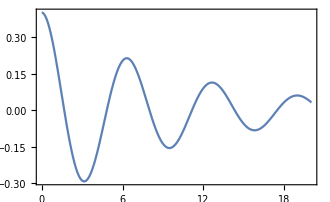
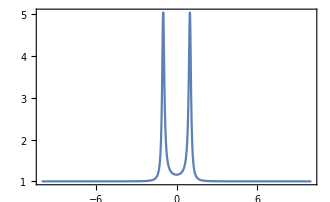

```mathematica
Row[
{Plot[G2/.{Ω->1,γ->0.1},{t,0.01,20}],
Plot[S/.{Ω->1,γ->0.1},{ω,-10,10}]}
]
```

Compute the spectrum numerically using Homodyne solver

```mathematica
dt = 0.01;
tf = 1000;
Ω = 1.0;
γ = 0.1;
sim = HomodyneSimulatePureState[{1,0},H,c,dt,tf]["J"];
```

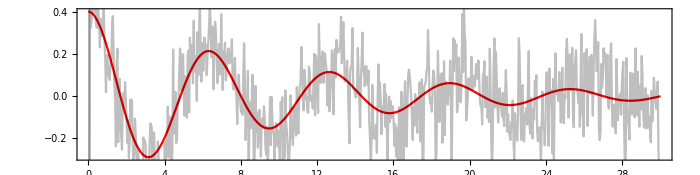

```mathematica
F=TwoPointCorrelation[butter[sim,150,dt],Round[30/dt],dt,4];
Show[
Plot[G2/.{Ω->1,γ->0.1},{t,0.01,30},PlotStyle->Red],
ListLinePlot[F,PlotStyle->Directive[Black,Opacity[0.25]]],
AspectRatio->1/4,
ImageSize->700
]
```

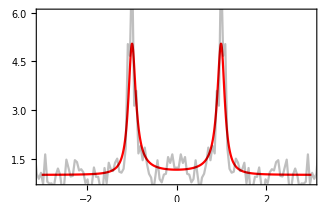

```mathematica
Show[
Plot[S/.{Ω->1,γ->0.1},{ω,-3,3},PlotStyle->Red,PlotRange->{{-3,3},{0.8,6}}],
ListLinePlot[PowerSpectrum[sim,dt,8],PlotStyle->Directive[Black,Opacity[0.25]],PlotRange->{{-3,3},All}]
]
```

## Non-interacting systems (Lyapunov etc.)

### Lyapunov solver using eigen-decomposition

This function solves WC + CW†=F using eigendecomposition of W. 
Apparently this turns out to be faster than “LyapunovSolve[W,F]”. 
I believe this is related to the fact that in Lindblad dynamics, F is usually quite sparse.

```mathematica
Clear[LyapunovEigen]
LyapunovEigen[W_,F_]:=Module[{ℐ,Λ,S,Sinv},
{Λ,S}=Quiet@Eigensystem[W];
S = Sᵀ;
Sinv = Inverse[S];

ℐ = 1/Outer[Plus,Λ,Λ*] Sinv.F.Sinv†;
S.ℐ.S†//Chop
];
```

#### Example usage

NESS of an Aubry-Andre quantum spin chain. 
Localization transition occurs at λ = 1

```mathematica
Clear[h,H,Γ,W,F];
λ = 0.5;
γ = 1;
f1 = 0.9;
fL = 0.1;
L = 5;

h[n_]:=λ Cos[ 2π GoldenRatio n ];

Γ = SparseArray[{{1,1}->γ,{L,L}->γ},{L,L}];
H = SparseArray[{{i_,i_}->2h[i],{i_,j_}/;j==i+1->-1,{i_,j_}/;j==i-1->-1},{L,L}];
W = ⅈ H-Γ;

F= SparseArray[{{1,1}->γ f1,{L,L}->γ fL},{L,L}];
```

```mathematica
LyapunovEigen[W,F]//Chop//mf;
```

(0.403979 | 0.0310366+0.046021 ⅈ | -0.0216419+0.00692131 ⅈ | -0.00605492+0.0309566 ⅈ | 0.00112528+0.0223755 ⅈ
0.0310366-0.046021 ⅈ | 0.310717 | 0.0471862+0.046021 ⅈ | -0.0529709+0.0308989 ⅈ | -0.0525851-0.00217123 ⅈ
-0.0216419-0.00692131 ⅈ | 0.0471862-0.046021 ⅈ | 0.254804 | -0.0561362+0.046021 ⅈ | -0.0121533-0.0424196 ⅈ
-0.00605492-0.0309566 ⅈ | -0.0529709-0.0308989 ⅈ | -0.0561362-0.046021 ⅈ | 0.206188 | 0.0417284+0.046021 ⅈ
0.00112528-0.0223755 ⅈ | -0.0525851+0.00217123 ⅈ | -0.0121533+0.0424196 ⅈ | 0.0417284-0.046021 ⅈ | 0.096021)

### BD: Boundary-driven chains (fermions & bosons)

```mathematica
Clear[BDMatrices]
BDMatrices[h_,γ_,f_]:=Module[{L=Length@h,Γ,F0},
Γ =If[Length@γ===Length@h, SparseArray@DiagonalMatrix@γ,SparseArray[{{1,1}->γ,{L,L}->γ},{L,L}]];
F0 =Which[
Length@f===Length@h, SparseArray@DiagonalMatrix@f ,
Length@f === 2,SparseArray[{{1,1}-> f⟦1⟧,{L,L}-> f⟦2⟧},{L,L}],
True,f Eye[L]
];
{ⅈ h + Γ/2, Γ F0}
]

BDMatrices[V_,L_,γ_,f_]:=Module[{Γ,A,W,F,g,h,i}, 
BDMatrices[TightBindingHamiltonian[V,L], γ,f]
];
```

```mathematica
Clear[BDCovMat];
BDCovMat[W_,F_]:=LyapunovEigen[W,F]
BDCovMat[h_,γ_,{f1_,fL_}]:=LyapunovEigen@@BDMatrices[h,γ,{f1,fL}];
BDCovMat[V_,L_,γ_,{f1_,fL_}]:=LyapunovEigen@@BDMatrices[V,L,γ,{f1,fL}]
```

```mathematica
(* Only holds for nearest-neighbor tight-binding models *)
Clear[BDCurrent];
BDCurrent[𝒞_]:=(*Im@𝒞⟦2,1⟧*) -ⅈ (𝒞⟦2,1⟧-𝒞⟦1,2⟧)//Chop;
BDCurrent[W_,F_]:=BDCurrent[LyapunovEigen[W,F]]
BDCurrent[h_,γ_,{f1_,fL_}]:=BDCurrent[LyapunovEigen@@BDMatrices[h,γ,{f1,fL}]];
BDCurrent[V_,L_,γ_,{f1_,fL_}]:=BDCurrent[LyapunovEigen@@BDMatrices[V,L,γ,{f1,fL}]];
```

#### Example usage

```mathematica
h = TightBindingHamiltonian[1,4]//mf;
```

(1 | -1 | 0 | 0
-1 | 1 | -1 | 0
0 | -1 | 1 | -1
0 | 0 | -1 | 1)

```mathematica
MatrixForm/@BDMatrices[h,{γ1,γ2,γ3,γ4},{f1,f2,f3,f4}]
```

{(ⅈ+γ1/2 | -ⅈ | 0 | 0
-ⅈ | ⅈ+γ2/2 | -ⅈ | 0
0 | -ⅈ | ⅈ+γ3/2 | -ⅈ
0 | 0 | -ⅈ | ⅈ+γ4/2),(f1 γ1 | 0 | 0 | 0
0 | f2 γ2 | 0 | 0
0 | 0 | f3 γ3 | 0
0 | 0 | 0 | f4 γ4)}

```mathematica
MatrixForm/@BDMatrices[h,γ1,{f1,f2,f3,f4}]
```

{(ⅈ+γ1/2 | -ⅈ | 0 | 0
-ⅈ | ⅈ | -ⅈ | 0
0 | -ⅈ | ⅈ | -ⅈ
0 | 0 | -ⅈ | ⅈ+γ1/2),(f1 γ1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | f4 γ1)}

```mathematica
MatrixForm/@BDMatrices[h,γ1,{f1,f4}]
```

{(ⅈ+γ1/2 | -ⅈ | 0 | 0
-ⅈ | ⅈ | -ⅈ | 0
0 | -ⅈ | ⅈ | -ⅈ
0 | 0 | -ⅈ | ⅈ+γ1/2),(f1 γ1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | f4 γ1)}

```mathematica
MatrixForm/@BDMatrices[1,5,γ1,{f1,f5}]
```

{(ⅈ+γ1/2 | -ⅈ | 0 | 0 | 0
-ⅈ | ⅈ | -ⅈ | 0 | 0
0 | -ⅈ | ⅈ | -ⅈ | 0
0 | 0 | -ⅈ | ⅈ | -ⅈ
0 | 0 | 0 | -ⅈ | ⅈ+γ1/2),(f1 γ1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | f5 γ1)}

```mathematica
{W,F}=BDMatrices[ϵ,4,γ,{f1,fL}];
mf@W;
mf@F;
```

(γ/2+ⅈ ϵ | -ⅈ | 0 | 0
-ⅈ | ⅈ ϵ | -ⅈ | 0
0 | -ⅈ | ⅈ ϵ | -ⅈ
0 | 0 | -ⅈ | γ/2+ⅈ ϵ)

(f1 γ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | fL γ)

```mathematica
{W,F}=BDMatrices[1,4,0.1,{0.3,0.7}];
mf@W;
mf@F;
```

(0.05+1. ⅈ | -ⅈ | 0 | 0
-ⅈ | ⅈ | -ⅈ | 0
0 | -ⅈ | ⅈ | -ⅈ
0 | 0 | -ⅈ | 0.05+1. ⅈ)

(0.03 | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.07)

```mathematica
BDMatrices[1,7,1,{1/2,0.3}]
```

{SparseArray[…],SparseArray[…]}

```mathematica
LyapunovEigen@@BDMatrices[1.,7,1,{1/2,0.3}]
```

{{0.42,0.-0.04 ⅈ,0,0,0,0,0},{0.+0.04 ⅈ,0.4,0.-0.04 ⅈ,0,0,0,0},{0,0.+0.04 ⅈ,0.4,0.-0.04 ⅈ,0,0,0},{0,0,0.+0.04 ⅈ,0.4,0.-0.04 ⅈ,0,0},{0,0,0,0.+0.04 ⅈ,0.4,0.-0.04 ⅈ,0},{0,0,0,0,0.+0.04 ⅈ,0.4,0.-0.04 ⅈ},{0,0,0,0,0,0.+0.04 ⅈ,0.38}}

```mathematica
LyapunovEigen@@{W,F}
```

{{0.499501,0.+0.00997506 ⅈ,0,0},{0.-0.00997506 ⅈ,0.5,0.+0.00997506 ⅈ,0},{0,0.-0.00997506 ⅈ,0.5,0.+0.00997506 ⅈ},{0,0,0.-0.00997506 ⅈ,0.500499}}

```mathematica
LyapunovEigen[W,F]//mf;
```

(0.499501 | 0.+0.00997506 ⅈ | 0 | 0
0.-0.00997506 ⅈ | 0.5 | 0.+0.00997506 ⅈ | 0
0 | 0.-0.00997506 ⅈ | 0.5 | 0.+0.00997506 ⅈ
0 | 0 | 0.-0.00997506 ⅈ | 0.500499)

```mathematica
CovMatCurrent[W,F]
```

-0.00997506

```mathematica
{W,F}=BDMatrices[{ϵ1,ϵ2,ϵ3,ϵ4},4,γ,{f1,fL}];
mf@W;
mf@F;
```

(γ/2+ⅈ ϵ1 | -ⅈ | 0 | 0
-ⅈ | ⅈ ϵ2 | -ⅈ | 0
0 | -ⅈ | ⅈ ϵ3 | -ⅈ
0 | 0 | -ⅈ | γ/2+ⅈ ϵ4)

(f1 γ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | fL γ)

```mathematica
{W,F}=BDMatrices[RandomReal[{0,1},{4,4}],γ,{f1,fL}];
mf@W;
mf@F;
```

((0.+0.493385 ⅈ)+γ/2 | 0.+0.963652 ⅈ | 0.+0.571679 ⅈ | 0.+0.527462 ⅈ
0.+0.744496 ⅈ | 0.+0.656838 ⅈ | 0.+0.317111 ⅈ | 0.+0.151104 ⅈ
0.+0.619738 ⅈ | 0.+0.67314 ⅈ | 0.+0.231151 ⅈ | 0.+0.831389 ⅈ
0.+0.131986 ⅈ | 0.+0.616602 ⅈ | 0.+0.907259 ⅈ | (0.+0.284962 ⅈ)+γ/2)

(f1 γ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | fL γ)

```mathematica
CovMatCurrent[1.,87,1,{0.2,0.3}]
```

-0.02

```mathematica
BDCovMat[1.0,10,1,{0.2,0.3}]//mf;
```

(0.24 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.26)

```mathematica
(* Aubry-André model *)
```

```mathematica
g = GoldenRatio;
V[n_]:=λ Cos[ 2π g n + ϕ]/(1-α Cos[2π g n + ϕ]);
```

#### Example: quantum transport in the Fibonnacci model (based arXiv 2106.11406)

The Fibonnacci model is quite incredible because, even though it is a non-interacting chain, it can show any kind of transport coefficient.

```mathematica
(* Takes a couple of minutes to run *)
Clear[L,λ];
λrange = range[0,7,0.1];
Lrange ={8,13,21,34,55,89,144,233,377,610,987};
sims = Association[];
```

```mathematica
Monitor[Do[
Clear[V];
V = N@Table[IntegerPart[(i+1)/GoldenRatio^2]-IntegerPart[i/GoldenRatio^2],{i,1,L}];
sims[{λ,L}]=BDCurrent[λ V,L,1,{1,0}];
,{λ,λrange},{L,Lrange}],{λ,L}]

fits = Association[];
Do[
fits[λ] = Fit[Table[{Log10@L,Log10@sims[{λ,L}]},{L,Lrange}],{1,x},x];
,{λ,λrange}]
```

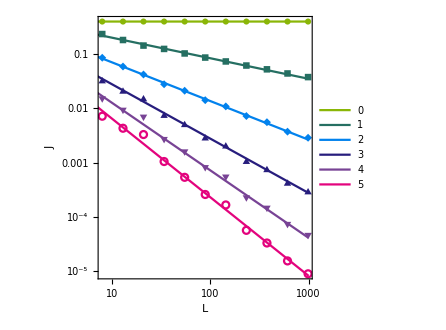

```mathematica
Show[
ListLogLogPlot[Table[{L,sims[{λ,L}]},{λ,range[0,5,1.]},{L,Lrange}],Joined->False,PlotMarkers->Automatic,
AspectRatio->1,
PlotStyle->Drop[ColorData[3,"ColorList"],3]
],
LogLogPlot[Evaluate@Table[10^(fits[λ]/.x->Log10[y]),{λ,range[0,5,1.]}],{y,0.1,10^3},
PlotStyle->Drop[ColorData[3,"ColorList"],3],
PlotLegends->legend[Round@range[0,5,1.],{0.29,0.12},LegendLayout->{"Row",2}]],
FrameLabel->{"L","J"}
]
```

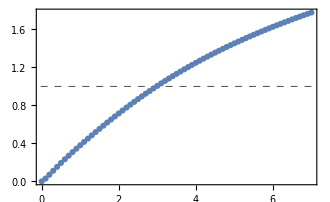

```mathematica
ListLinePlot[Table[{λ,-fits[λ]⟦2,1⟧},{λ,λrange}],PlotMarkers->Automatic,
GridLines->{None,{1}},
GridLinesStyle->Directive[Black, Dashed]]
```

### Fermionic chains with pairing terms

Implements the master equation 

dρ/dt = -i [H,ρ] + ∑_i γ_i^- D[c_i] + γ_i^+D[c_i^†]

with 

H = ∑_(n,m) h_nm c_n^†c_m + 1/2(G_nm c_n^†c_m^†+ G_mn^* c_n c_m)  = 1/4 Γ† 𝒯 Γ + 1/2 tr(h)

where Γ_i= c_i^†+c_i and Γ_(L+i) = i(c_i^†-c_i) are majorana operators and 

𝒯=σ_z ⊗ (G+G†)/2   -  σ_y⊗ h -σ_x⊗ i((G-G†)/2) =((G+G†)/2 | i h - i/2(G-G†)
-i h - i/2(G-G†) | -((G+G†)/2))  

The covariance matrix Θ = 1/2⟨[Γ_(i,)Γ_j]⟩ satisfies the Lyapunov equation 

dΘ/dt = -(𝒲Θ+Θ𝒲†) +ℱ

where 

𝒲 = i 𝒯 + Υ + Υᵀ   and  ℱ = - 2(Υ-Υᵀ)   and   Υ = 1/4(γ_++γ_- | i(γ_+-γ_-)
-i(γ_+-γ_-) | γ_++γ_-)

```mathematica
Clear[BDPairingMatrices];
BDPairingMatrices[𝒯_,γ_,f_]:=Module[{L,W,γm,γp,Υ,𝒲,ℱ},

L=Length[𝒯]/2;
{W,γp} = BDMatrices[Eye[L],γ,f];
γm = W+W†-γp;

Υ = 1/4 ArrayFlatten[({{γp+γm, ⅈ(γp-γm)}, {-ⅈ (γp-γm), γp+γm}})];
𝒲 = ⅈ 𝒯 + Υ+Υᵀ;
ℱ = - 2(Υ-Υᵀ);
{𝒲,ℱ}
]

BDPairingMatrices[h_,G_,γ_,f_]:=BDPairingMatrices[MajoranaHamiltonian[h,G],γ,f]

(* XY chain, with z-field h0 and anisotropy κ *)
BDPairingMatrices[L_,h0_,κ_,γ_,f_]:=Module[{Δ},
Δ=h0 Eye[L]+ SparseArray[{Band[{1,2}]->(1-κ)/2(*Jy*),Band[{2,1}]->(1+κ)/2(*Jx*)},{L,L}] ;
 BDPairingMatrices[ⅈ ArrayFlatten[({{0, -Δ}, {Δ†, 0}})],γ,f]
]
```

```mathematica
Clear[BDPairingCovMat];
BDPairingCovMat[𝒲_,ℱ_]:=LyapunovEigen[𝒲,ℱ]
BDPairingCovMat[𝒯_,γ_,f_]:=LyapunovEigen@@BDPairingMatrices[𝒯,γ,f];
BDPairingCovMat[h_,G_,γ_,f_]:=LyapunovEigen@@BDPairingMatrices[h,G,γ,f];
BDPairingCovMat[L_,h0_,κ_,γ_,f_]:=LyapunovEigen@@BDPairingMatrices[L,h0,κ,γ,f];
```

```mathematica
BDPairingCurrent[Θ_,γ_,f_]:=Module[{γγ = First@Flatten@{γ},ff=First@Flatten@{f}},
{First@Flatten@{γ} (First@Flatten@{f}-FermionsReducedC[Θ]⟦1,1⟧),
Last@Flatten@{γ} (Last@Flatten@{f}-FermionsReducedC[Θ]⟦-1,-1⟧)}//Chop
]
```

#### Sanity check: no-pairing case

```mathematica
{𝒲,ℱ} = BDPairingMatrices[TightBindingHamiltonian[10],0.0,0.1,{0.3,0.4}];
Θ =BDPairingCovMat[𝒲,ℱ];
FermionsReducedC@Θ//mf;
```

(0.349875 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.350125)

```mathematica
Θ = BDPairingCovMat[TightBindingHamiltonian[10],0.0,0.1,{0.3,0.4}];
FermionsReducedC@Θ//mf;
BDPairingCurrent[Θ,0.1,{0.3,0.4}]
BDPairingCurrent2[Θ,0.1,{0.3,0.4}]
```

(0.349875 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.350125)

-0.00498753

0.00498753+0. ⅈ

```mathematica
BDCovMat[TightBindingHamiltonian[10],0.1,{0.3,0.4}]//mf;
BDCurrent[TightBindingHamiltonian[10],0.1,{0.3,0.4}]
```

(0.349875 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.350125)

-0.00498753

#### Ex: Non-equilibrium transition in the XY chain

Based on arXiv 0805.2878. 
The boundary-driven XY chain has a transition at h_c=1-κ^2

Below we plot the reduced covariance matrix C_ij=⟨c_j^†c_i⟩ for L = 100, below and above the transition.

```mathematica
Row@{rasta@MatrixPlot@Re@FermionsReducedC@BDPairingCovMat[100,0.7,κ = 0.5,γ = 1.0,{f1 = 0.3,fL = 0.4}],rasta@MatrixPlot@Re@FermionsReducedC@BDPairingCovMat[100,0.8,κ,γ,{f1,fL}]}
```

-Graphics--Graphics-

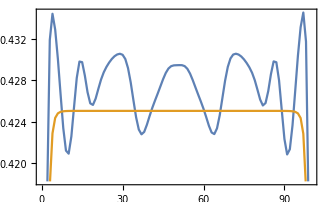

```mathematica
(* The transition is more strongly present in the coherences. The populations don't differ that much from one phase to another *)
ListLinePlot[
{Diagonal@FermionsReducedC@BDPairingCovMat[100,0.7,κ = 0.5,γ = 1.0,{f1 = 0.3,fL = 0.4}],
Diagonal@FermionsReducedC@BDPairingCovMat[100,0.8,κ,γ,{f1,fL}]}]
```

### Bosonic chains with squeezing terms (to-do)

### Dephasing

```mathematica
Clear[DephasingSolve];
DephasingSolve[W_,F_,Γ_]:=Module[{L = Length@W,vecW,vecRemoveDiag,vecF},
vecW = kron[W*,NEye[L]]+kron[NEye[L],W];
vecRemoveDiag = SparseArray[{i_,i_}/;Last@QuotientRemainder[i,L+1]≠1->1,{L^2,L^2}];

LinearSolve[vecW + Γ vecRemoveDiag, Vec[F]]//Unvec//Chop
]
```

```mathematica
Clear[BDCovMatDephasing];
BDCovMatDephasing[W_,F_,Γ_]:=DephasingSolve[W,F,Γ];
BDCovMatDephasing[h_,γ_,{f1_,fL_},Γ_]:=Module[{W,F} ,
{W,F} = BDMatrices[h,γ,{f1,fL}];
DephasingSolve[W,F,Γ]
];
BDCovMatDephasing[V_,L_,γ_,{f1_,fL_},Γ_]:=Module[{W,F} ,
{W,F} = BDMatrices[V,L,γ,{f1,fL}];
DephasingSolve[W,F,Γ]
];
```

```mathematica
(* Only holds for nearest-neighbor tight-binding models *)
Clear[BDCurrentDephasing];
BDCurrentDephasing[𝒞_]:=(*Im@𝒞⟦2,1⟧*) -ⅈ (𝒞⟦2,1⟧-𝒞⟦1,2⟧)//Chop;
BDCurrentDephasing[W_,F_,Γ_]:=BDCurrentDephasing[BDCovMatDephasing[W,F,Γ]]
BDCurrentDephasing[h_,γ_,{f1_,fL_},Γ_]:=BDCurrentDephasing[BDCovMatDephasing[h,γ,{f1,fL},Γ]];
BDCurrentDephasing[V_,L_,γ_,{f1_,fL_},Γ_]:=BDCurrentDephasing[BDCovMatDephasing[V,L,γ,{f1,fL},Γ]];
```

#### QuotientRemainder logic

This vectorized superoperator removes the diagonal of a matrix

```mathematica
L=4;
tmp=SparseArray[{i_,i_}/;Last@QuotientRemainder[i,L+1]≠1->1,{L^2,L^2}]/.L->10//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
tmp.Vec@Table[Subscript[a, i,j],{i,L},{j,L}]//Unvec//mf;
```

(0 | a_(1,2) | a_(1,3) | a_(1,4)
a_(2,1) | 0 | a_(2,3) | a_(2,4)
a_(3,1) | a_(3,2) | 0 | a_(3,4)
a_(4,1) | a_(4,2) | a_(4,3) | 0)

#### Example: noise-assisted transport in a Fibonnacci subdiffusive chain (arXiv 2106.11406)

Define a tight-binding model with Fibonnacci on-site potentials

```mathematica
L = 100;
V = N@Table[IntegerPart[(i+1)/GoldenRatio^2]-IntegerPart[i/GoldenRatio^2],{i,1,L}];
BDCurrent[V,L,1,{1,0}]
```

0.0770395

```mathematica
BDCurrentDephasing[V,L,1,{1,0},0.0]
```

0.0770395

```mathematica
Γrange = logspace[-3,2,30];
L = 500;
V = N@Table[IntegerPart[(i+1)/GoldenRatio^2]-IntegerPart[i/GoldenRatio^2],{i,1,L}];
results = Table[{Γ,BDCurrentDephasing[4 V,L,1,{1,0},Γ]},{Γ,Γrange}]
```

{{0.001,0.00033293},{0.00148735,0.000351493},{0.00221222,0.000371302},{0.00329034,0.000391671},{0.0048939,0.000411741},{0.00727895,0.000430803},{0.0108264,0.000447989},{0.0161026,0.00046374},{0.0239503,0.000479437},{0.0356225,0.000496692},{0.0529832,0.000516324},{0.0788046,0.000536324},{0.11721,0.000554202},{0.174333,0.000569738},{0.259294,0.000586251},{0.385662,0.00060827},{0.573615,0.000632935},{0.853168,0.000652367},{1.26896,0.000664039},{1.88739,0.000667492},{2.80722,0.000652044},{4.17532,0.000596975},{6.21017,0.000498174},{9.23671,0.000380927},{13.7382,0.000274105},{20.4336,0.000190525},{30.392,0.00013012},{45.2035,0.0000881205},{67.2336,0.0000594439},{100.,0.0000400273}}

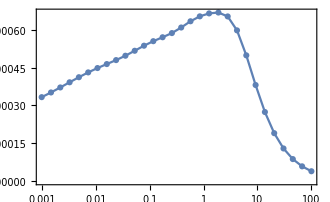

```mathematica
ListLogLinearPlot[results,Joined->True,PlotMarkers->Automatic]
```

### Emission & absorption spectra in terms of Lyapunov dynamics

The system satisfies the Lyapunov equation 

dC/dt = -(W C + C W†) + F

The emission and absorption spectra are given by 

ℰ_ij(ω) = ∫dτ e^(-i ω τ)⟨c_j^†(τ)c_i(0)⟩

and 

𝒜_ij(ω) = ∫ dτ e^(-i ω τ)⟨c_i(0) c_j^†(τ)⟩ 

For Gaussian dynamics, using the quantum regression theorem we can write 

⟨c_j^†(t') c_i(t) ⟩ = (θ(t'-t) [C_t e^(-W†(t'-t))])_ij + (θ(t-t') [e^(-W(t-t'))C_t'])_ij

and

⟨c_i(t) c_j^†(t') ⟩ = (θ(t'-t) [(C̄)_t e^(-W†(t'-t))])_ij + (θ(t-t') [e^(-W(t-t'))(C̄)_t'])_ij

where C̄ = 1 ± C (with + for bosons and - for fermions).

Computing the Fourier transforms, we therefore get 

ℰ_ij(ω) = [C 1/(W†+ i ω)+ 1/(W-i ω)C]_ij

𝒜_ij(ω) = [C̄ 1/(W†+i ω)- 1/(W-iω)C̄]_ij 

Thus, 

𝒜(ω)= [1/(W†+i ω)- 1/(W-i ω)]  ± ℰ(ω)  

The spectrum of the output field is then 

𝒮_ii (ω) = γ_i^++ γ_i^- ℰ_ii(ω) - γ_i^+𝒜_ii(ω) 

One can probably compute an analogous formula for 𝒮_ij. To be done.

```mathematica
Clear[w,wd]
```

```mathematica
Integrate[Exp[(-wd-ⅈ ω)τ],τ]
```

ⅇ^(-τ (wd+ⅈ ω))/(-wd-ⅈ ω)

```mathematica
Integrate[Exp[(w-ⅈ ω)τ],τ]
```

ⅇ^(τ (w-ⅈ ω))/(w-ⅈ ω)

```mathematica
Clear[BDEmissionSpectra];
BDEmissionSpectra[W_,F_,ωs_]:=Module[{𝒞,𝕀,inv1,inv2},
𝒞 = BDCovMat[W,F];
𝕀 = Eye[Length@W];
Table[
inv1 = Inverse[W†+ⅈ ω 𝕀 ];
inv2 = Inverse[W-ⅈ ω 𝕀];
𝒞.inv1+inv2.𝒞,{ω,ωs}]//Chop
]
```

```mathematica
(* Fermions *) 
Clear[BDAbsorptionSpectra];
BDAbsorptionSpectra[W_,F_,ωs_]:=Module[{𝒞,𝕀,inv1,inv2,𝒞b},
𝕀 = Eye[Length@W];
𝒞 = BDCovMat[W,F];
𝒞b = 𝕀-𝒞;

Table[
inv1 = Inverse[W†+ⅈ ω 𝕀 ];
inv2 = Inverse[W-ⅈ ω 𝕀];
𝒞b.inv1+inv2.𝒞b,{ω,ωs}]//Chop
]
```

#### Example usage

Emission = absorption for infinite temperature input/output

```mathematica
{W,F} = BDMatrices[1,6,0.1,{0.5,0.5}];
ωs = linspace[-2,4,2500];
ℰ=BDEmissionSpectra[W,F,ωs];
```

```mathematica
h=(W - W†)/(2ⅈ);
eigs=Eigvals[h]
```

{-0.801938,-0.24698,0.554958,1.44504,2.24698,2.80194}

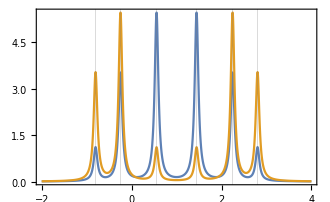

```mathematica
ListLinePlot[{
{ωs,ℰ⟦All,1,1⟧}ᵀ,
{ωs,ℰ⟦All,5,5⟧}ᵀ},PlotRange->All,GridLines->{eigs,None}]
```

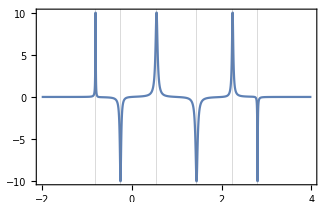

```mathematica
ListLinePlot[{
{ωs,ℰ⟦All,1,6⟧}ᵀ},PlotRange->All,GridLines->{eigs,None}]
```

Example 2: dissipators acting on all sites

```mathematica
{W,F} = BDMatrices[1,L=12,ConstantArray[0.1,L],ConstantArray[0.5,L]];
ωs = linspace[-2,4,2500];
ℰ=BDEmissionSpectra[W,F,ωs];
```

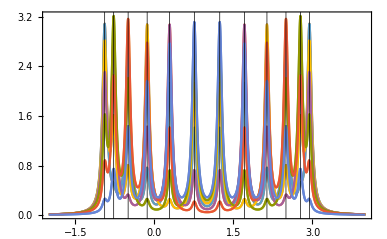

```mathematica
h=(W - W†)/(2ⅈ);
eigs=Eigvals[h];
ListLinePlot[Evaluate@Table[{ωs,ℰ⟦All,i,i⟧}ᵀ,{i,1,L}]
,PlotRange->All,GridLines->{eigs,None},ImageSize->900,GridLinesStyle->Black]
```

Example 3: absorption spectra at zero temperature & bath only at a single site.

```mathematica
Clear[𝒜];
Do[
{W,F} = BDMatrices[1,L=12,0.3Basis[L,k],0 Basis[L,1]];
ωs = linspace[-2,4,2500];
𝒜[k]=BDAbsorptionSpectra[W,F,ωs];
h=(W - W†)/(2ⅈ);
eigs=Eigvals[h];
,{k,L}]
```

```mathematica
Table[ListLinePlot[Evaluate@Table[{ωs,𝒜[k]⟦All,k,k⟧}ᵀ,{i,1,L}]
,PlotRange->All,GridLines->{eigs,None},ImageSize->250,GridLinesStyle->Black],{k,1,12,1}]
```

```mathematica
Clear[𝒜];
{W,F} = BDMatrices[1,L=25,0.3Basis[L,13],0 Basis[L,1]];
(*ωs = linspace[-2,4,2500];*)
𝒜=BDAbsorptionSpectra[W,F,{1.0}];
h=(W - W†)/(2ⅈ);
eigs=Eigvals[h];
```

Now the bath acting on all sites

```mathematica
{W,F} = BDMatrices[J,2,γ,{f1,fL}];
mf@W;
mf@F;
```

(ⅈ J+γ/2 | -ⅈ
-ⅈ | ⅈ J+γ/2)

(f1 γ | 0
0 | fL γ)

```mathematica
{mats,ℰ}=LyapunovEmissionSpectra[W,F,{ω}]⟦1⟧;
```

```mathematica
ℰ//cf//mf;
```

((2 (-(γ (6 fL+f1 (-2+γ^2)))/(16+γ^2)-(γ (fL (2-4 ω)+f1 (2+γ^2+4 ω)))/(γ^2+16 ω^2)))/(4+γ^2) | (4 γ (2 ⅈ (2 ⅈ (f1+fL)+(f1-fL) γ) (4+γ^2)-ⅈ (f1-fL) γ (16+γ^2) ω+4 (fL (4+γ (-6 ⅈ+γ))+f1 (4+γ (6 ⅈ+γ))) ω^2))/((4+γ^2) (16+γ^2) (γ^2+16 ω^2))
(4 γ (-2 ⅈ (-2 ⅈ (f1+fL)+(f1-fL) γ) (4+γ^2)+ⅈ (f1-fL) γ (16+γ^2) ω+4 (f1 (4+γ (-6 ⅈ+γ))+fL (4+γ (6 ⅈ+γ))) ω^2))/((4+γ^2) (16+γ^2) (γ^2+16 ω^2)) | (2 (-(γ (6 f1+fL (-2+γ^2)))/(16+γ^2)-(γ (f1 (2-4 ω)+fL (2+γ^2+4 ω)))/(γ^2+16 ω^2)))/(4+γ^2))

```mathematica
Manipulate[Plot[(2 (-(γ (6 fL+f1 (-2+γ^2)))/(16+γ^2)-(γ (fL (2-4 ω)+f1 (2+γ^2+4 ω)))/(γ^2+16 ω^2)))/(4+γ^2)/.{f1->1,fL->0},{ω,-10,10}],{{γ,0.1},0,10}]
```

### BDFCS: Full counting statistics for non-interacting fermions

```mathematica
BDFCSAverage[W_,F_,{μμp_,μμm_}]:=Module[{γp,γm,𝕀 = Eye[Length@W],𝒞,μm,μp},
γp = F;
γm = W+W†-γp;
μm = DiagonalMatrix[μμm];
μp = DiagonalMatrix[μμp];
𝒞 = BDCovMat[W,F];

Tr[μm.γm.𝒞 + μp.γp.(𝕀-𝒞)]//Chop
]
```

```mathematica
BDFCSDiffusionMatrix[W_,F_,{μμp_,μμm_}]:=Module[{γp,γm,𝕀 = Eye[Length@W],𝒞,Ω,𝒞t,Υ,μm,μp},
γp = F;
γm = W+W†-γp;
μm = DiagonalMatrix[μμm];
μp = DiagonalMatrix[μμp];
𝒞 = BDCovMat[W,F];
𝒞t = BDCovMat[W, -(*ⅈ*) 𝒞.μm.γm.𝒞+(*ⅈ*) (𝕀-𝒞).μp.γp.(𝕀-𝒞)];
Tr[(μm.μm.γm - μp.μp.γp).𝒞+μp.μp.γp]+- 2 (*ⅈ*)(-1) Tr[(μm.γm-μp.γp).𝒞t]//Chop
]
```

#### Example usage

```mathematica
h = TightBindingHamiltonian[1,L=4];
{W,F} = BDMatrices[h,γ=0.5,{f1=0.3,fL=0.15}];
μm = {-2,0,0,0};
μp = {1,0,0,3};

BDFCSAverage[W,F,{μp,μm}]
BDFCSDiffusionMatrix[W,F,{μp,μm}]
```

0.130368

0.397007

Comparison with FCS function (using full Hilbert space)

```mathematica
LoadFermionicOperators[L];
H = Sum[h⟦i,j⟧ cd[i].c[j],{i,L},{j,L}];
cops = {√(γ(1-f1))c[1],√(γ f1)cd[1],√(γ(1-fL))c[L],√(γ fL)cd[L]};
ℒ = Liouvillian[H,cops];
ρ = SteadyState[ℒ];
FCSAverage[ρ,ℒ,cops,{μm⟦1⟧,μp⟦1⟧,μm⟦-1⟧,μp⟦-1⟧}]
FCSDiffusionMatrix[ρ,ℒ,cops,{μm⟦1⟧,μp⟦1⟧,μm⟦-1⟧,μp⟦-1⟧}]
```

0.130368

0.397007

## Mesoscopic leads

### Reaction coordinates & star-to-chain mapping

```mathematica
Clear[ReactionCoordinateMappingNumerics];
ReactionCoordinateMappingNumerics[Js_,ωs_]:=Module[{Λ1,Ω1,P,ω,ωmin,ωmax,dω,Jnew},

ωmin = First@ωs;
ωmax = Last@ωs;
dω = ωs⟦2⟧-ωs⟦1⟧;

Λ1 = √(1/(2π)Trapz[Js,dω]);
Ω1 = 1/(2π Λ1^2)Trapz[ωs Js,dω];

P = 1/π Table[Trapz[Drop[Js,{i}]/Drop[ωs-ωs⟦i⟧,{i}],dω],{i,Length@ωs}]; 
Jnew = (4 Λ1^2 Js)/(P^2+Js^2);
{Λ1,Ω1,Jnew}
]
```

```mathematica
StarToChainMapping[𝒥s_,ωs_,Lb_]:=Module[{Λ1,Ω1,P,ω,ωmin,ωmax,dω,Jnew,Js},

ωmin = First@ωs;
ωmax = Last@ωs;
dω = ωs⟦2⟧-ωs⟦1⟧;
Js=𝒥s;
Table[
Λ1 = √(1/(2π)Trapz[Js,dω]);
Ω1 = 1/(2π Λ1^2)Trapz[ωs Js,dω];

P = 1/π Table[Trapz[Drop[Js,{i}]/Drop[ωs-ωs⟦i⟧,{i}],dω],{i,Length@ωs}]; 
Js = (4 Λ1^2 Js)/(P^2+Js^2);
{Λ1^2,Ω1}
,{Lb}]
]
```

#### Example usage

```mathematica
(* Boxcar *)
γ = 0.3;
δ =1.0;
ϵ = 0.3;
ωs = linspace[ϵ-δ,ϵ+δ,999];
Js = Table[γ Boxcar[ϵ-δ,ϵ+δ][ω],{ω,ωs}];

{Λ1,Ω1,Jnew}=ReactionCoordinateMappingNumerics[Js,ωs];

{Λ1^2,Ω1}
{(γ δ)/π,ϵ}
```

{0.095493,0.3}

{0.095493,0.3}

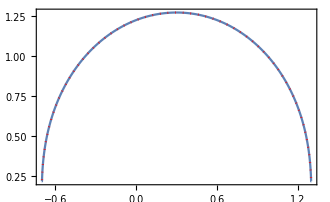

{0.074996,0.199968}

{0.075,0.2}

```mathematica
Show[
ListLinePlot[{ωs,Jnew}ᵀ,PlotRange->All],
Plot[(4 π δ)/(π^2+4 ArcTanh[(ϵ-ω)/δ]^2),{ω,ϵ-δ,ϵ+δ},PlotStyle->Directive[Red,Dotted]]
]
```

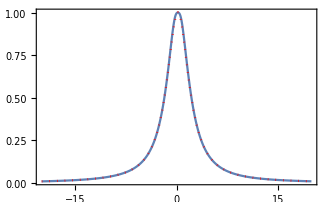

```mathematica
Show[
ListLinePlot[{ωs,Jnew}ᵀ,PlotRange->All],
Plot[(δ(2δ)^2)/((ω-ϵ)^2+(2δ)^2),{ω,-20,20},PlotStyle->Directive[Red,Dotted]]
]
```

```mathematica
(* Quadratic Lorentzian. Bit weird *)
γ = 0.3;
δ =1.0;
ϵ = 0.2;
ωs = linspace[-20,20,1000];
Js = Table[(γ δ^2)/((ω-ϵ)^2+δ^2),{ω,ωs}];

{Λ1,Ω1,Jnew}=ReactionCoordinateMappingNumerics[Js,ωs];

{Λ1^2,Ω1}
{(γ δ)/2,ϵ}
```

{0.145229,0.193441}

{0.15,0.2}

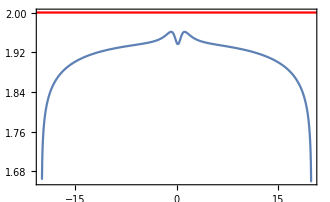

```mathematica
Show[
ListLinePlot[{ωs,Jnew}ᵀ,PlotRange->All],
Plot[2δ,{ω,-30,30},PlotStyle->Red],
PlotRange->{{-20,20},All}
]
```

#### Star-to-chain

```mathematica
(* Quartic Lorentzian *)
γ = 0.3;
δ =1.0;
ϵ = 0.2;
ωs = linspace[-4,4,1000];
Js = Table[(γ δ^4)/(((ω-ϵ)^2+δ^2)^2),{ω,ωs}];

StarToChainMapping[Js,ωs,50]
```

{{0.0745313,0.196439},{0.699475,0.125942},{3.20508,-0.0154157},{4.70386,-0.00229059},{4.18537,-0.000573852},{4.09302,-0.000609534},{4.06204,0.000232555},{4.04339,-0.000513866},{4.03714,0.00035079},{4.0301,-0.000393887},{4.02836,0.000278304},{4.02535,-0.000256235},{4.02471,0.000178137},{4.02348,-0.000147772},{4.02324,0.000101511},{4.02283,-0.0000774687},{4.0228,0.000053977},{4.02279,-0.000037022},{4.0229,0.0000278337},{4.02307,-0.0000156261},{4.02328,0.0000146065},{4.02353,-5.04961×10^-6},{4.02379,8.30661×10^-6},{4.02408,-1.60047×10^-7},{4.02436,5.40235×10^-6},{4.02466,1.89955×10^-6},{4.02494,4.03158×10^-6},{4.02522,2.60535×10^-6},{4.02549,3.29531×10^-6},{4.02575,2.68278×10^-6},{4.02599,2.79582×10^-6},{4.02622,2.47845×10^-6},{4.02644,2.37615×10^-6},{4.02664,2.1576×10^-6},{4.02682,1.98619×10^-6},{4.02698,1.8011×10^-6},{4.02713,1.61857×10^-6},{4.02726,1.45057×10^-6},{4.02738,1.27973×10^-6},{4.02749,1.12821×10^-6},{4.02758,9.77935×10^-7},{4.02766,8.45603×10^-7},{4.02772,7.18869×10^-7},{4.02778,6.07663×10^-7},{4.02783,5.04608×10^-7},{4.02787,4.14793×10^-7},{4.0279,3.33965×10^-7},{4.02792,2.64318×10^-7},{4.02794,2.03322×10^-7},{4.02796,1.51611×10^-7}}

### Mesoscopic leads for non-interacting dynamics

Based on https://journals.aps.org/prx/pdf/10.1103/PhysRevX.10.031040

```mathematica
LeadSamples[L_,W_,Wstar_,Γ_]:=Module[{Llog,Llin,logsamp,samples,energies,spacings,gamma,couplings},
Llog = Round[0.2 L];
Llin=L -2 Round[0.2 L];
logsamp = logspace[Log10[Wstar],Log10[W],Llog+1];
samples=Join[
Most@Reverse[-logsamp],
linspace[-Wstar,Wstar,Llin+1],
Rest@logsamp];

(*samples = linspace[-W,W,L+1];*)
energies = (Most@samples+Rest@samples)/2;
spacings = Differences[samples];
gamma = spacings;
couplings = √(Γ spacings/(2π));
{energies,couplings,gamma}
];
```

```mathematica
Clear[BDThermLeadMatrices];
BDThermLeadMatrices[h_,Γ_,{TL_,TR_,μL_,μR_},Lb_,w_]:=Module[{energies,couplings,gamma,Ls=Length@h,HB1,HB2,VS1,VS2,H,W,F,Fermis,ws=w/2},

{energies,couplings,gamma}=LeadSamples[Lb,w,ws,Γ];
HB1 = DiagonalMatrix[energies];
HB2 = HB1;

VS1=Sum[couplings⟦n⟧ Proj[{Lb,Ls},n,1],{n,Length@couplings}];
VS2=Sum[couplings⟦n⟧ Proj[{Ls,Lb},Ls,n],{n,Length@couplings}];

H=ArrayFlatten[({{HB1, VS1, 0}, {VS1†, h, VS2}, {0, VS2†, HB2}})]; 
Fermis[T_,μ_,energies_]:=1/(Exp[(energies-μ)/T]+1) ;

W = ⅈ H + 1/2 DiagonalMatrix@Join[gamma,ConstantArray[0,Ls],gamma];

F = DiagonalMatrix@Join[Fermis[TL,μL,energies]gamma,ConstantArray[0,Ls],Fermis[TR,μR,energies]gamma];

{W,F}
]
```

```mathematica
Clear[ThermleadsGetSysCM];
ThermleadsGetSysCM[𝒞_,Lb_]:=Module[{Ls = Length@𝒞-2Lb},𝒞⟦Lb+1;;Lb+Ls,Lb+1;;Lb+Ls⟧]

Clear[ThermleadsDecomposeW];
ThermleadsDecomposeW[W_,Lb_,bath_]:=Module[{Λ,γ,ϵ,Ls = Length@W-2Lb,rg},
rg = If[bath==="left",1;;Lb,Lb+Ls+1;;Ls+2Lb];
γ = Diagonal[(W+W†)]⟦rg⟧;
ϵ = Im[Diagonal@W]⟦rg⟧;
Λ = If[bath=="left",Im@W⟦Lb+1,rg⟧,Im@W⟦Lb+Ls,rg⟧];
{γ,ϵ,Λ}//Chop
]

Clear[ThermleadsDecomposeWF];
ThermleadsDecomposeWF[W_,F_,Lb_,bath_]:=Module[{γ,ϵ,Λ,f},

{γ,ϵ,Λ}=ThermleadsDecomposeW[W,Lb,bath];
f = Which[
bath=="left",Diagonal[F]⟦1;;Lb⟧/γ,
bath=="right",Diagonal[F]⟦Lb+Ls+1;;-1⟧/γ];
{γ,ϵ,Λ,f}
]
```

```mathematica
Clear[ThermleadsParticleCurrent];
ThermleadsParticleCurrent[𝒞_,W_,F_,Lb_,bath_:"left"]:=Module[{Ls = Length@𝒞-2Lb,γ,rg},
rg = If[bath==="left",
1;;Lb,
Lb+Ls+1;;Lb+Ls+Lb];

γ = (W+W†)⟦rg,rg⟧;
Tr[F⟦rg,rg⟧-γ.𝒞⟦rg,rg⟧]//Chop
]

Clear[ThermleadsEnergyCurrent];
ThermleadsEnergyCurrent[𝒞_,W_,F_,Lb_,bath_:"left"]:=Module[{Ls = Length@𝒞-2Lb,γ,ϵ,Λ,JEprx,JEartur,Ω,Jnaive,Jfcs,term1,term2,term3,rg,JEarturRight,JEprxRight},
rg = If[bath==="left",
1;;Lb,
Lb+Ls+1;;Lb+Ls+Lb];

γ = (W+W†);
ϵ=DiagonalMatrix[Im[Diagonal@W]];

If[bath==="left",
(Λ = SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>Im@W⟦Lb+1,j⟧ γ⟦j,j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}];
Ω = SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>Im@W⟦Lb+1,j⟧ ϵ⟦j,j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}];
),(
Λ = SparseArray[{{Lb+Ls,j_}/;rg⟦1⟧<=j<=rg⟦2⟧:>Im@W⟦Lb+Ls,j⟧ γ⟦j,j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}];
Ω = SparseArray[{{Lb+Ls,j_}/;rg⟦1⟧<=j<=rg⟦2⟧:>Im@W⟦Lb+Ls,j⟧ ϵ⟦j,j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}];
)];

Λ=Λ+Λ†;
Ω=Ω-Ω†;
(* Relevant terms *)
(* tr(Subscript[H, L] ℒ(ρ)) *)
term1 = Tr[ϵ⟦rg,rg⟧.(F⟦rg,rg⟧-γ⟦rg,rg⟧.𝒞⟦rg,rg⟧)]//Chop;

(* tr(Subscript[V, SL] ℒ(ρ)) *)
term2 = -1/2 Tr[Λ.𝒞]//Chop;

(* i ⟨[Subscript[H, L],Subscript[V, SL]]⟩ *)
term3 = -ⅈ Tr[Ω.𝒞]//Chop;


(* Energy current in Marlon's PRX *)
(* tr(Subscript[H, L] ℒ(ρ)) + tr(Subscript[V, SL] ℒ(ρ)) *)
JEprx = term1+term2;

(* Change in energy of the bath (Artur's paper) *)
(* Meant to be the "correct" one; equal to JEprx in steady-state. *)
(* i ⟨[Subscript[H, L],Subscript[V, SL]]⟩ + tr(Subscript[V, SL] ℒ(ρ)) *)
JEartur = term3+term2;

{{JEprx,JEartur},{term1,term2,term3}}
]
```

#### Example usage

```mathematica
h = TightBindingHamiltonian[1,3]//mf;
{W,F}=BDThermLeadMatrices[h,1,{0.5,0.4,0,0},Lb=10,8];
```

(1 | -1 | 0
-1 | 1 | -1
0 | -1 | 1)

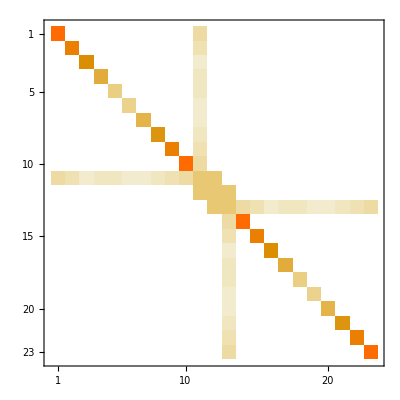

```mathematica
W//Abs//MatrixPlot
```

```mathematica
{W,F}=BDThermLeadMatrices[h,1,{0.5,0.4,0,0},Lb=150,8];
C1=ThermleadsGetSysCM[BDCovMat[W,F],Lb]//mf;
```

(0.293344 | 0.220317-0.00258 ⅈ | 0.0844028+0.00215117 ⅈ
0.220317+0.00258 ⅈ | 0.320713 | 0.223154-0.00258 ⅈ
0.0844028-0.00215117 ⅈ | 0.223154+0.00258 ⅈ | 0.298617)

```mathematica
(* Compare with the exact solution using NEGF *)
C2=NEGFCovMat[h,1,{0.5,0.4,0,0}]//mf;
C1-C2//mf;
```

(0.299931 | 0.220131-0.0026735 ⅈ | 0.08466+0.00210373 ⅈ
0.220131+0.0026735 ⅈ | 0.315236 | 0.222945-0.0026735 ⅈ
0.08466-0.00210373 ⅈ | 0.222945+0.0026735 ⅈ | 0.30545)

(-0.00658691 | 0.000185381+0.0000934955 ⅈ | -0.000257214+0.000047444 ⅈ
0.000185381-0.0000934955 ⅈ | 0.00547694 | 0.000208691+0.0000934955 ⅈ
-0.000257214-0.000047444 ⅈ | 0.000208691-0.0000934955 ⅈ | -0.00683293)

```mathematica
tab=Table[
{W,F}=BDThermLeadMatrices[h,1,{0.5,0.4,0,0},Lb,16];
C1=ThermleadsGetSysCM[BDCovMat[W,F],Lb];
{Lb,Norm[C1-C2]},{Lb,10,500,30}]
```

{{10,0.148835},{40,0.0505291},{70,0.0282825},{100,0.0193717},{130,0.0149891},{160,0.012131},{190,0.0101537},{220,0.00872215},{250,0.00764956},{280,0.00682743},{310,0.00618688},{340,0.00568212},{370,0.00528134},{400,0.0049616},{430,0.00470588},{460,0.0045012},{490,0.0043375}}

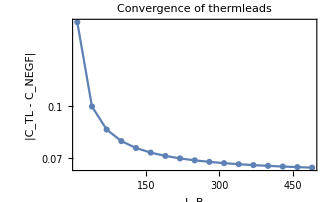

```mathematica
ListLogPlot[tab,PlotMarkers->Automatic,FrameLabel->{"L_B","|C_TL - C_NEGF|"},PlotRange->All,Joined->True,
PlotLabel->"Convergence of thermleads"
]
```

```mathematica
tab=Table[
{W,F}=BDThermLeadMatrices[h,1,{0.5,0.4,0,0},Lb,Wmax];
C1=ThermleadsGetSysCM[BDCovMat[W,F],Lb];
{Wmax,Norm[C1-C2]},{Lb,{150,300,450}},{Wmax,4,30,2}];
```

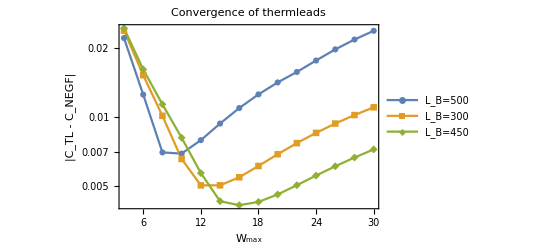

```mathematica
ListLogPlot[tab,PlotMarkers->Automatic,FrameLabel->{"W_max","|C_TL - C_NEGF|"},PlotRange->All,Joined->True,
PlotLabel->"Convergence of thermleads",
PlotLegends->legend[{"L_B=500","L_B=300","L_B=450"},{0.35,0.75}],
ImageSize->400
]
```

#### Particle current in a double quantum dot: comparison with Landauer-Büttiker

```mathematica
T = 100;
γ = 1.0;
eV = 100; 
μL = eV/2;
μR = -eV/2;
gs = linspace[0.001,4,10];
Clear[LB,Meso,g,𝒯];
𝒯[g_,γ_,ϵ_:0]:=NEGFTransmissionFunction[({{ϵ, g}, {g, ϵ}}),γ];
Do[
LB[g] = LandauerButtiker[𝒯[g,γ],{T,T,μL,μR}];
{W,F}=BDThermLeadMatrices[({{0, g}, {g, 0}}),γ,{T,T,μL,μR},Lb=100,8];
𝒞 = BDCovMat[W,F];

Meso[g] = ThermleadsParticleCurrent[𝒞,W,F,Lb]

,{g,gs}]
```

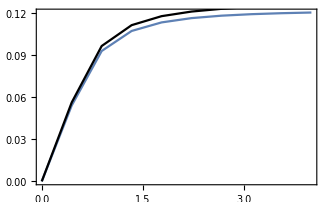

```mathematica
Show[
ListLinePlot[Table[{g,LB[g]["IN"]},{g,gs}]],
ListLinePlot[Table[{g, Meso[g]},{g,gs}],PlotStyle->Black]]
```

#### Energy current in the transient regime

```mathematica
h = TightBindingHamiltonian[1,2];
{W0,F}=BDThermLeadMatrices[h,1,{0.5,0.5,0,0},Lb=20,8];
C0=BDCovMat[W0,F];

h1 = ({{0, 0}, {0, 1}});
W1 = ⅈ ArrayFlatten[({{ConstantArray[0,{Lb,Lb}], 0, 0}, {0, h1, 0}, {0, 0, ConstantArray[0,{Lb,Lb}]}})]//Normal;
```

```mathematica
(* Pulsed field *)
σ = 5;
ω = 0.2;

ℰ[t_]:=Exp[-(t-15)^2/σ^2]Cos[ω t ]
dt = 0.02;
tf = 50;
ℰ0 = 2.0;

Clear[f];
f[t_,𝒞_]:=With[{W = W0 +ℰ0  ℰ[t]W1},-W.𝒞-𝒞.W†+F];
sol = RK4t[f,C0,dt,tf];
```

```mathematica
currLeft=Table[ThermleadsEnergyCurrent[c⟦2⟧,W0+ℰ0  ℰ[c⟦1⟧]W1,F,Lb,"left"]⟦1⟧,{c,sol}];
currRight=Table[ThermleadsEnergyCurrent[c⟦2⟧,W0+ℰ0  ℰ[c⟦1⟧]W1,F,Lb,"right"]⟦1⟧,{c,sol}];
```

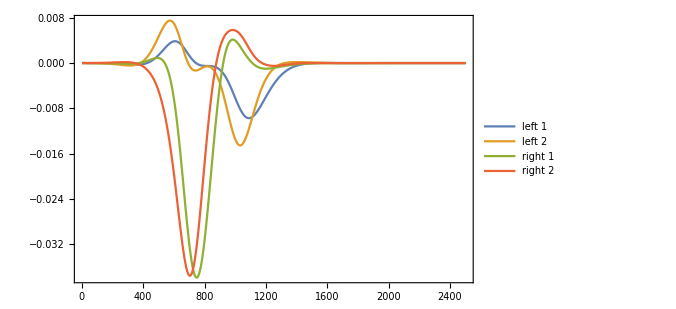

```mathematica
ListLinePlot[Flatten[{currLeftᵀ⟦1;;2⟧,currRightᵀ⟦1;;2⟧},1],PlotRange->All,
ImageSize->500,
PlotLegends->legend[{"left 1","left 2","right 1", "right 2"},{0.75,0.25}]
]
```

#### Energy current: comparison withe Landauer-Büttiker

```mathematica
Clear[TL,Lb]
TLs = Range[0.2,2,0.1];
Lbs = {100,150,200(*,250*)};
h = TightBindingHamiltonian[1,Ls=5];
γ = 0.1;
𝒯=NEGFTransmissionFunction[h,γ];
(*Clear[simsLB,simsTL,simsArchak];*)
PrettyTiming@Monitor[Do[
LB=LandauerButtiker[𝒯,{TL,TR=1.9,μL=0.,μR=0.3}]//Quiet;
simsLandauerButtiker[TL,"IE"]=LB["IE"];

Do[
{W,F}=BDThermLeadMatrices[h,γ,{TL,TR,μL,μR},Lb,8];
(*simsTL[TL,Lb,"IE"]=ThermleadsFCSAverage[W,F,{Ls,Lb},"energy","left"] ;*)
𝒞= BDCovMat[W,F];
simsMesoscopicLeads[TL,Lb,"IE"]=ThermleadsEnergyCurrent[𝒞,W,F,Lb];

,{Lb,Lbs}];
,{TL,TLs}],{TL,Lb}]
```

0h : 0m : 26s

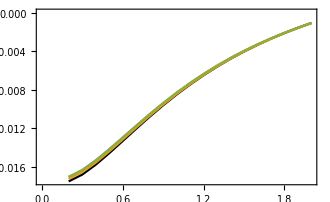

```mathematica
Show[
ListLinePlot[Table[{TL,simsLandauerButtiker[TL,"IE"]},{TL,TLs}],PlotStyle->Black],
ListLinePlot[
Table[{TL,simsMesoscopicLeads[TL,Lb,"IE"]⟦1,2⟧},{Lb,Lbs},{TL,TLs}]
]
]
```

### !! Full counting statistics for mesoscopic leads (still a mess)

```mathematica
Clear[ThermleadsFCSgenericMatrix]
ThermleadsFCSgenericMatrix[W_,F_,Lb_,func_,bath_:"left",type_:"row"]:=Module[{γ,ϵ,Λ,f,i,m,Ls = Length@W-2Lb,M},
{γ,ϵ,Λ,f}=ThermleadsDecomposeWF[W,F,Lb,bath];
m = Table[func[γ⟦i⟧,ϵ⟦i⟧,Λ⟦i⟧,f⟦i⟧],{i,Length@γ}];
M=Which[
bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>m⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>m⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}]
];

If[type=="row",M,Mᵀ]
]
```

```mathematica
Clear[ThermleadsFCSGMatrix];
ThermleadsFCSGMatrix[W_,Lb_,type_:"particle",bath_:"left",modifier_:"False"]:=Module[{γ,ϵ,Λ,G,Ls = Length@W-2Lb},
{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
G=Which[
type=="particle"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>Λ⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>(Λ(ϵ-ⅈ γ/2))⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="particle"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>Λ⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>(Λ(ϵ-ⅈ γ/2))⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}]
];
G=G-G†
]
```

```mathematica
Clear[ThermleadsFCSFMatrix];
ThermleadsFCSFMatrix[W_,F_,Lb_,bath_:"left"]:=Module[{Ls = Length@W-2Lb,γ,ϵ,Λ,f,mat},
{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
If[bath=="left",
f = Diagonal[F]⟦1;;Lb⟧/γ;
mat =SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>(-ⅈ/2 Λ γ/2 f)⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}];,
f = Diagonal[F]⟦Lb+Ls+1;;-1⟧/γ;
mat = SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>(-ⅈ/2 Λ γ/2 f)⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}];
];
mat-mat†
]

Clear[ThermleadsFCSFMatrix2];
ThermleadsFCSFMatrix2[W_,F_,Lb_,bath_:"left"]:=Module[{Ls = Length@W-2Lb,γ,ϵ,Λ,f,mat},
{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
If[bath=="left",
f = Diagonal[F]⟦1;;Lb⟧/γ;
mat =SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>(-ⅈ/2 Λ γ/2(1-2f))⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}];,
f = Diagonal[F]⟦Lb+Ls+1;;-1⟧/γ;
mat = SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>(-ⅈ/2 Λ γ/2(1-2f))⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}];
];
mat(*-mat†*)
]
```

```mathematica
Clear[ThermleadsFCSAverage];
ThermleadsFCSAverage[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{G,Ls = Length@W-2Lb},
G=ThermleadsFCSGMatrix[W,Lb,type,bath];
-ⅈ Tr[G.𝒞]//Chop
]
```

```mathematica
(*Clear[ThermleadsFCSDiffusionMatrix]
ThermleadsFCSDiffusionMatrix[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,G,G2},
𝕀 = Eye[Lb+Ls+Lb];
G=ThermleadsFCSGMatrix[W,Lb,type,bath];
If[type=="particle",
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))],

𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))+ThermleadsFCSFMatrix[W,F,Lb,bath]]];

2Tr[G.𝒞t]//Chop
]*)
```

```mathematica
Clear[ThermleadsFCSDiffusionMatrix]
ThermleadsFCSDiffusionMatrix[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,G,ψ},
𝕀 = Eye[Lb+Ls+Lb];
G=ThermleadsFCSGMatrix[W,Lb,type,bath];
If[type=="particle",
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))],
(
ψ = ThermleadsFCSFMatrix2[W,F,Lb,bath];
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))+ThermleadsFCSFMatrix[W,F,Lb,bath]+(𝒞.ψ+ ψᵀ.𝒞)]
)];

2Tr[G.𝒞t]//Chop
]
```

```mathematica
Clear[ThermleadsFCSDiffusionMatrix2]
ThermleadsFCSDiffusionMatrix2[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,G,ψ},
𝕀 = Eye[Lb+Ls+Lb];
G=ThermleadsFCSGMatrix[W,Lb,type,bath];
If[type=="particle",
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))],
(
ψ = ThermleadsFCSFMatrix2[W,F,Lb,bath];
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))]
)];

2Tr[G.𝒞t]//Chop
]
```

#### Naive & wrong G

```mathematica
Clear[ThermleadsFCSDiffusionMatrixNaive]
ThermleadsFCSDiffusionMatrixNaive[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,G,G2},
𝕀 = Eye[Lb+Ls+Lb];
G=ThermleadsFCSGMatrix[W,Lb,type,bath];
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))];
2Tr[G.𝒞t]//Chop
]
```

```mathematica
Clear[ThermleadsFCSDiffusionMatrixWrongG]
ThermleadsFCSDiffusionMatrixWrongG[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,G,G2,γ,ϵ,Λ},

{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
G2=Which[
type=="particle"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>Λ⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>(Λ(ϵ(*-ⅈ γ/2*)))⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="particle"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>Λ⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>(Λ(ϵ(*-ⅈ γ/2*)))⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}]
];
G2=G2-G2†;

𝕀 = Eye[Lb+Ls+Lb];
G=ThermleadsFCSGMatrix[W,Lb,type,bath]; 
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G2.𝒞+ 𝒞.G2.(𝕀-𝒞))];
2Tr[G.𝒞t]//Chop
]
```

```mathematica
h = TightBindingHamiltonian[1,Ls=5];
γ = 0.1;
𝒯=NEGFTransmissionFunction[h,γ];
(*LB=LandauerButtiker[𝒯,{TL=0.2,TR=1.4,μL=1.9,μR=-0.2}]//Quiet;*)
LB=LandauerButtiker[𝒯,{TL=0.2,TR=0.4,μL=-0.2,μR=-0.2}]//Quiet;
{W,F}=BDThermLeadMatrices[h,γ,{TL,TR,μL,μR},Lb=400,8];
𝒞 = BDCovMat[W,F];
{LB["ΔE"],
ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","right"]}

{ThermleadsFCSDiffusionMatrixNaive[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrixNaive[𝒞,W,F,Lb,"energy","right"]}

{ThermleadsFCSDiffusionMatrixWrongG[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrixWrongG[𝒞,W,F,Lb,"energy","right"]}
```

#### Other & old

```mathematica
Clear[ThermleadsFCSAverage];
ThermleadsFCSAverage[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{Ω,(*γp,γm,𝕀 = Eye[Length@W],Ω,𝒞t,Υ,μm,μp,ω,*),Υ,rg,Ls = Length@W-2Lb,γ,ϵ,Λ,ϕ,cb},
{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
ϕ = If[type=="particle",Λ,Λ(ϵ+ⅈ γ/2)];
cb = If[bath=="left",𝒞⟦Lb+1,1;;Lb⟧,𝒞⟦Lb+Ls,Lb+Ls+1;;-1⟧];
ⅈ (ϕ.cb-ϕ*.cb*)//Chop
]
```

```mathematica
Clear[ThermleadsFCSDiffusionMatrix]
ThermleadsFCSDiffusionMatrix[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{γp,γm,𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,rg,ϵ,γ,Λ,ϕ,ϕ2},
𝕀 = Eye[Lb+Ls+Lb];
{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
ϕ = Which[
type=="particle"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>Λ⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>(Λ(ϵ-ⅈ γ/2))⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="particle"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>Λ⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>(Λ(ϵ-ⅈ γ/2))⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}]
];
ϕ=ϕ-ϕ†;

ϕ2 = Which[
type=="particle"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>Λ⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>(Λ(ϵ))⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="particle"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>Λ⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>(Λ(ϵ))⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}]
];
ϕ2=ϕ2-ϕ2†;
(*𝒞t = BDCovMat[W,- (𝕀-𝒞).ϕ2.𝒞- 𝒞.ϕ2.(𝕀-𝒞)];*)
𝒞t = BDCovMat[W,- (𝕀-𝒞).ϕ2.𝒞- 𝒞.ϕ2.(𝕀-𝒞)];
Tr[ϕ.𝒞t]//Chop
]
```

```mathematica
Clear[ThermleadsMuMatrix];
ThermleadsMuMatrix[W_,Lb_,type_,bath_]:=Module[{Ls = Length@W-2Lb},
Which[
type=="particle" && bath=="left",
DiagonalMatrix@Join[ConstantArray[1,Lb],ConstantArray[0,Ls+Lb]],
type=="particle" && bath=="right",
DiagonalMatrix@Join[ConstantArray[0,Ls+Lb],ConstantArray[1,Lb]],
type=="particle" && bath=="mean",
1/2 DiagonalMatrix@Join[ConstantArray[1,Lb],ConstantArray[0,Ls],ConstantArray[-1,Lb]],
type=="energy" && bath=="left",
DiagonalMatrix@Join[Im[Diagonal@W]⟦1;;Lb⟧,ConstantArray[0,Ls+Lb]],
type=="energy" && bath=="right",
DiagonalMatrix@Join[ConstantArray[0,Ls+Lb],Im[Diagonal@W]⟦Lb+Ls+1;;Lb+Ls+Lb⟧],
type=="energy" && bath=="mean",
1/2(DiagonalMatrix@Join[Im[Diagonal@W]⟦1;;Lb⟧,ConstantArray[0,Ls],-Im[Diagonal@W]⟦Lb+Ls+1;;-1⟧])
]]
```

```mathematica
Clear[ThermleadsFCSAverageNaive];
ThermleadsFCSAverageNaive[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{γp,γm,𝕀 = Eye[Length@W],μm,μp,Ls = Length@W-2Lb},
γp = F;
γm = W+W†-γp;
μp = ThermleadsMuMatrix[W,Lb,type,bath];
μm = - μp;
Tr[μm.γm.𝒞 + μp.γp.(𝕀-𝒞)]//Chop
]
```

```mathematica
Clear[ThermleadsFCSDiffusionMatrixNaive];
ThermleadsFCSDiffusionMatrixNaive[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{γp,γm,𝕀 = Eye[Length@W],μm,μp,𝒞t,δ,Ls = Length@W-2Lb},
γp = F;
γm = W+W†-γp;
μp = ThermleadsMuMatrix[W,Lb,type,bath];
μm = -μp;
𝒞t = BDCovMat[W, -(*ⅈ*) 𝒞.μm.γm.𝒞+(*ⅈ*) (𝕀-𝒞).μp.γp.(𝕀-𝒞)];
Tr[(μm.μm.γm - μp.μp.γp).𝒞+μp.μp.γp]- 2 (*ⅈ*)(-1) Tr[(μm.γm-μp.γp).𝒞t]//Chop
]
```

```mathematica
Clear[ThermleadsFCSDiffusionMatrix2]
ThermleadsFCSDiffusionMatrix2[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{γp,γm,𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,rg,ϵ,γ,Λ,ϕ,ϕ2},
𝕀 = Eye[Lb+Ls+Lb];
{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
ϕ = Which[
type=="particle"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>Λ⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>(Λ(ϵ-ⅈ γ/2))⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="particle"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>Λ⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>(Λ(ϵ-ⅈ γ/2))⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}]
];
ϕ=ϕ-ϕ†;

newmat1 =If[bath=="left",
 -1/2 Total[γ Λ Diagonal[F] ⟦1;;Lb⟧] Proj[2Lb+Ls,Lb+1,Lb+1],
-1/2 Total[γ Λ Diagonal[F]⟦Lb+Ls+1;;-1⟧] Proj[2Lb+Ls,Lb+Ls,Lb+Ls]
];

newmat2 = If[bath=="left",
1/2(γ.Λ) Proj[2Lb+Ls,Lb+1,Lb+1],
1/2(γ.Λ) Proj[2Lb+Ls,Lb+Ls,Lb+Ls]
];
𝒞t = BDCovMat[W,- (𝕀-𝒞).ϕ.𝒞- 𝒞.ϕ.(𝕀-𝒞) + newmat2.𝒞-𝒞.newmat2+ⅈ newmat1];
Tr[ϕ.𝒞t]//Chop
]
```

```mathematica
ThermleadsFCSDiffusionMatrix2[𝒞,W,F,Lb,"energy","left"]
```

0.0492352

```mathematica
{W,F}=BDThermLeadMatrices[h,γ,{TL,TR,μL,μR},Lb=150,8];
𝒞 = BDCovMat[W,F];
```

#### Comparison with the Landauer-Büttiker formalism

```mathematica
(*h = TightBindingHamiltonian[1,Ls=5];*)
h = TightBindingHamiltonian[{1,-1,2},Ls=3]//mf;
γ = 0.1;
𝒯=NEGFTransmissionFunction[h,γ];
(*LB=LandauerButtiker[𝒯,{TL=1.7,TR=0.4,μL=-0.3,μR=0.3}]//Quiet;*)
LB=LandauerButtiker[𝒯,{TL=1.3,TR=0.8,μL=0.0,μR=-0.3}]//Quiet;
{W,F}=BDThermLeadMatrices[h,γ,{TL,TR,μL,μR},Lb=100,8];
𝒞 = BDCovMat[W,F];
```

(1 | -1 | 0
-1 | -1 | -1
0 | -1 | 2)

```mathematica
{ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","right"]}
{ThermleadsFCSDiffusionMatrix2[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrix2[𝒞,W,F,Lb,"energy","right"]}

LB["ΔE"]
```

{0.0137747,0.0137725}

{0.0206834,0.0205173}

0.013889

```mathematica
Chop@{ThermleadsFCSAverage[𝒞,W,F,Lb,"particle","left"] ,
ThermleadsFCSAverage[𝒞,W,F,Lb,"particle","right"] }
{LB["IN"],ThermleadsParticleCurrent[𝒞,W,F,Lb]}
```

{0.000187015,-0.000187015}

{0.000153828,0.000187015}

```mathematica
{ThermleadsFCSAverage[𝒞,W,F,Lb,"energy","left"] ,
ThermleadsFCSAverage[𝒞,W,F,Lb,"energy","right"]  }
{ LB["IE"],ThermleadsEnergyCurrent[𝒞,W,F,Lb][[1,1]]}
```

{0.000235506,-0.000235506}

{0.00020242,0.000235506}

```mathematica
{ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"particle","left"],
ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"particle","right"]}
LB["ΔN"]
```

{0.000463,0.000463}

0.000210493

```mathematica
{ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","right"]}
(*{ThermleadsFCSDiffusionMatrixWrongG[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrixWrongG[𝒞,W,F,Lb,"energy","right"]}
*)LB["ΔE"]
(*{ThermleadsFCSDiffusionMatrix2[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrix2[𝒞,W,F,Lb,"energy","right"]}*)
```

(0.-0.00501056 ⅈ | -0.0000432728-0.00472615 ⅈ | 0.00134481-0.00531193 ⅈ | -0.00139385+0.00271041 ⅈ | -0.000477704+0.000182793 ⅈ | 0.000779123+0.00137155 ⅈ | -0.0197556-0.0704278 ⅈ | 0.00274087+0.0159054 ⅈ | 0.00148209+0.00470118 ⅈ | -9.6767×10^-7+0.000190709 ⅈ | 0.000060888+0.000192249 ⅈ | 0.0000672325+0.000877358 ⅈ | 0.000363574-0.000747962 ⅈ | -0.000120908-0.0000341995 ⅈ | -0.0000771077-0.000117187 ⅈ
0.0000432728-0.00472615 ⅈ | 0.-0.00410997 ⅈ | 0.00137723-0.00371843 ⅈ | -0.000294702+0.00274155 ⅈ | 0.000229011+0.00104021 ⅈ | 0.00136868+0.00227819 ⅈ | -0.0114532-0.0431395 ⅈ | -0.00203044+0.00714284 ⅈ | 0.000170009+0.00300279 ⅈ | -0.0000317069+0.0000895528 ⅈ | -8.15796×10^-7+0.0000338886 ⅈ | 0.000153275+0.000515833 ⅈ | 0.000196348-0.000528199 ⅈ | -0.0000597772-0.0000512214 ⅈ | -0.0000364093-0.0000894527 ⅈ
-0.00134481-0.00531193 ⅈ | -0.00137723-0.00371843 ⅈ | 0.-0.00363144 ⅈ | 0.00143724+0.00217322 ⅈ | 0.00175205+0.00134638 ⅈ | 0.00350987+0.00283288 ⅈ | -0.0103366-0.0192265 ⅈ | -0.00081852+0.0096727 ⅈ | 0.000883296+0.00343849 ⅈ | -0.0000311924+0.000137113 ⅈ | -0.0000826553+0.000162646 ⅈ | -0.0000481807+0.000172615 ⅈ | -0.000112925-0.000386236 ⅈ | -0.0000892827-0.0000833531 ⅈ | -0.0000706282-0.0000946815 ⅈ
0.00139385+0.00271041 ⅈ | 0.000294702+0.00274155 ⅈ | -0.00143724+0.00217322 ⅈ | 0.+0.00508213 ⅈ | -0.00466171+0.0016256 ⅈ | -0.00421182+0.0011526 ⅈ | 0.0174936+0.00104667 ⅈ | -0.00242631-0.00843718 ⅈ | -0.00459026-0.00204348 ⅈ | -0.000104754-0.000131363 ⅈ | -0.000115277-0.000179994 ⅈ | 0.0000635732-0.000378442 ⅈ | -0.0000125893-0.000754743 ⅈ | 0.000317657-0.0000823971 ⅈ | 0.000217484-0.0000285394 ⅈ
0.000477704+0.000182793 ⅈ | -0.000229011+0.00104021 ⅈ | -0.00175205+0.00134638 ⅈ | 0.00466171+0.0016256 ⅈ | 0.+0.0048287 ⅈ | -0.000557711+0.00392275 ⅈ | 0.0139411-0.0255827 ⅈ | -0.00196849-0.00737874 ⅈ | 0.00135556+0.00068778 ⅈ | 0.000054762-6.07848×10^-6 ⅈ | 0.0000627353-0.0000475097 ⅈ | 0.00036406-0.00025393 ⅈ | -0.000731283-0.0000835917 ⅈ | -7.29341×10^-6+0.000231159 ⅈ | -0.00011431+4.40334×10^-6 ⅈ
-0.000779123+0.00137155 ⅈ | -0.00136868+0.00227819 ⅈ | -0.00350987+0.00283288 ⅈ | 0.00421182+0.0011526 ⅈ | 0.000557711+0.00392275 ⅈ | 0.+0.00308662 ⅈ | 0.0124049-0.0325377 ⅈ | 0.00269208-0.0158347 ⅈ | 0.000423688-0.00204825 ⅈ | 0.0000797851-0.000114908 ⅈ | 0.0000861918-0.000189397 ⅈ | 0.000554934-0.000588765 ⅈ | -0.000990766-8.26818×10^-6 ⅈ | 0.000221061+0.0000431737 ⅈ | -2.80739×10^-6+0.0000468863 ⅈ
0.0197556-0.0704278 ⅈ | 0.0114532-0.0431395 ⅈ | 0.0103366-0.0192265 ⅈ | -0.0174936+0.00104667 ⅈ | -0.0139411-0.0255827 ⅈ | -0.0124049-0.0325377 ⅈ | 0.+0.0241776 ⅈ | 0.0000946723-0.00947198 ⅈ | -0.000212385-0.00833778 ⅈ | 0.0000762252-0.000284456 ⅈ | 0.0000945247-0.000356556 ⅈ | 0.000240551-0.000596542 ⅈ | 0.000876662-0.000132973 ⅈ | 0.000375699+0.000591369 ⅈ | 0.00015502+0.000355737 ⅈ
-0.00274087+0.0159054 ⅈ | 0.00203044+0.00714284 ⅈ | 0.00081852+0.0096727 ⅈ | 0.00242631-0.00843718 ⅈ | 0.00196849-0.00737874 ⅈ | -0.00269208-0.0158347 ⅈ | -0.0000946723-0.00947198 ⅈ | 0.-0.00336047 ⅈ | 0.0000762657+0.000922265 ⅈ | 0.0000122363+8.13572×10^-6 ⅈ | 0.0000658165-0.0000281263 ⅈ | 0.00015966+0.000228664 ⅈ | -0.000274973+0.0000978141 ⅈ | -0.000106085-0.000115043 ⅈ | -0.0000365913-0.0000594967 ⅈ
-0.00148209+0.00470118 ⅈ | -0.000170009+0.00300279 ⅈ | -0.000883296+0.00343849 ⅈ | 0.00459026-0.00204348 ⅈ | -0.00135556+0.00068778 ⅈ | -0.000423688-0.00204825 ⅈ | 0.000212385-0.00833778 ⅈ | -0.0000762657+0.000922265 ⅈ | 0.+0.00177079 ⅈ | -0.0000121057+0.0000535828 ⅈ | 1.2107×10^-6+0.000057176 ⅈ | -7.76856×10^-6+0.000179079 ⅈ | -0.000337205+0.0000645683 ⅈ | -0.0000453229-0.000147669 ⅈ | -0.0000318789-0.000080364 ⅈ
9.6767×10^-7+0.000190709 ⅈ | 0.0000317069+0.0000895528 ⅈ | 0.0000311924+0.000137113 ⅈ | 0.000104754-0.000131363 ⅈ | -0.000054762-6.07848×10^-6 ⅈ | -0.0000797851-0.000114908 ⅈ | -0.0000762252-0.000284456 ⅈ | -0.0000122363+8.13572×10^-6 ⅈ | 0.0000121057+0.0000535828 ⅈ | 0.+1.52295×10^-6 ⅈ | 5.1966×10^-7+1.11753×10^-6 ⅈ | 2.50466×10^-6+5.5807×10^-6 ⅈ | -0.0000102332+5.33376×10^-6 ⅈ | -2.87875×10^-6-4.21111×10^-6 ⅈ | -1.67083×10^-6-2.25255×10^-6 ⅈ
-0.000060888+0.000192249 ⅈ | 8.15796×10^-7+0.0000338886 ⅈ | 0.0000826553+0.000162646 ⅈ | 0.000115277-0.000179994 ⅈ | -0.0000627353-0.0000475097 ⅈ | -0.0000861918-0.000189397 ⅈ | -0.0000945247-0.000356556 ⅈ | -0.0000658165-0.0000281263 ⅈ | -1.2107×10^-6+0.000057176 ⅈ | -5.1966×10^-7+1.11753×10^-6 ⅈ | 0.-2.65102×10^-7 ⅈ | 5.04913×10^-6+5.57278×10^-6 ⅈ | -0.0000120212+6.2995×10^-6 ⅈ | -2.93135×10^-6-5.0377×10^-6 ⅈ | -1.48757×10^-6-2.68348×10^-6 ⅈ
-0.0000672325+0.000877358 ⅈ | -0.000153275+0.000515833 ⅈ | 0.0000481807+0.000172615 ⅈ | -0.0000635732-0.000378442 ⅈ | -0.00036406-0.00025393 ⅈ | -0.000554934-0.000588765 ⅈ | -0.000240551-0.000596542 ⅈ | -0.00015966+0.000228664 ⅈ | 7.76856×10^-6+0.000179079 ⅈ | -2.50466×10^-6+5.5807×10^-6 ⅈ | -5.04913×10^-6+5.57278×10^-6 ⅈ | 0.+2.04778×10^-6 ⅈ | -0.0000207975+0.0000102792 ⅈ | -7.34058×10^-6-0.000010616 ⅈ | -3.95308×10^-6-6.77572×10^-6 ⅈ
-0.000363574-0.000747962 ⅈ | -0.000196348-0.000528199 ⅈ | 0.000112925-0.000386236 ⅈ | 0.0000125893-0.000754743 ⅈ | 0.000731283-0.0000835917 ⅈ | 0.000990766-8.26818×10^-6 ⅈ | -0.000876662-0.000132973 ⅈ | 0.000274973+0.0000978141 ⅈ | 0.000337205+0.0000645683 ⅈ | 0.0000102332+5.33376×10^-6 ⅈ | 0.0000120212+6.2995×10^-6 ⅈ | 0.0000207975+0.0000102792 ⅈ | 0.+0.0000586995 ⅈ | -0.0000270989+8.01529×10^-6 ⅈ | -0.0000161152+3.49753×10^-6 ⅈ
0.000120908-0.0000341995 ⅈ | 0.0000597772-0.0000512214 ⅈ | 0.0000892827-0.0000833531 ⅈ | -0.000317657-0.0000823971 ⅈ | 7.29341×10^-6+0.000231159 ⅈ | -0.000221061+0.0000431737 ⅈ | -0.000375699+0.000591369 ⅈ | 0.000106085-0.000115043 ⅈ | 0.0000453229-0.000147669 ⅈ | 2.87875×10^-6-4.21111×10^-6 ⅈ | 2.93135×10^-6-5.0377×10^-6 ⅈ | 7.34058×10^-6-0.000010616 ⅈ | 0.0000270989+8.01529×10^-6 ⅈ | 0.+7.85945×10^-6 ⅈ | 9.93215×10^-7+6.70382×10^-6 ⅈ
0.0000771077-0.000117187 ⅈ | 0.0000364093-0.0000894527 ⅈ | 0.0000706282-0.0000946815 ⅈ | -0.000217484-0.0000285394 ⅈ | 0.00011431+4.40334×10^-6 ⅈ | 2.80739×10^-6+0.0000468863 ⅈ | -0.00015502+0.000355737 ⅈ | 0.0000365913-0.0000594967 ⅈ | 0.0000318789-0.000080364 ⅈ | 1.67083×10^-6-2.25255×10^-6 ⅈ | 1.48757×10^-6-2.68348×10^-6 ⅈ | 3.95308×10^-6-6.77572×10^-6 ⅈ | 0.0000161152+3.49753×10^-6 ⅈ | -9.93215×10^-7+6.70382×10^-6 ⅈ | 0.+4.02522×10^-6 ⅈ)

(0.+3.39596×10^-6 ⅈ | 6.95025×10^-7+3.20658×10^-6 ⅈ | 2.48961×10^-6+9.82451×10^-6 ⅈ | -0.0000175816+0.0000112392 ⅈ | -8.19858×10^-6-7.87513×10^-6 ⅈ | -3.71555×10^-6-4.73023×10^-6 ⅈ | 0.0000269027+0.000111835 ⅈ | -0.0000394679-0.0000875534 ⅈ | -0.000011996-0.0000918749 ⅈ | -5.18251×10^-7+0.000197705 ⅈ | 0.0000310896+0.0000984949 ⅈ | 0.000026821+0.000151352 ⅈ | 0.0000668051-0.000117173 ⅈ | -0.000066147-0.0000196067 ⅈ | -0.0000840269-0.000124036 ⅈ
-6.95025×10^-7+3.20658×10^-6 ⅈ | 0.+1.9263×10^-6 ⅈ | 5.23685×10^-6+0.0000104611 ⅈ | -0.00002096+0.0000129948 ⅈ | -8.85888×10^-6-9.63245×10^-6 ⅈ | -3.68361×10^-6-5.68552×10^-6 ⅈ | 0.0000109453+0.000125277 ⅈ | -0.0000865038-0.000139422 ⅈ | -0.000018511-0.000115192 ⅈ | -0.000062721+0.000201057 ⅈ | -1.18533×10^-8+0.000045529 ⅈ | 0.0000755631+0.000180355 ⅈ | 0.0000672592-0.000165013 ⅈ | -0.0000761467-0.0000644724 ⅈ | -0.0000912327-0.000200707 ⅈ
-2.48961×10^-6+9.82451×10^-6 ⅈ | -5.23685×10^-6+0.0000104611 ⅈ | 0.+9.2813×10^-6 ⅈ | -0.0000346486+0.000023512 ⅈ | -0.0000185888-0.0000174231 ⅈ | -8.58736×10^-6-0.0000116598 ⅈ | 0.0000477638+0.000304318 ⅈ | -0.000216869+1.66914×10^-6 ⅈ | -0.0000374782-0.000221719 ⅈ | -0.0000592202+0.000884169 ⅈ | -0.000142401+0.000529709 ⅈ | 0.0000473488+0.000210651 ⅈ | -0.000149312-0.000334048 ⅈ | -0.000390714-0.000272618 ⅈ | -0.000565724-0.00059731 ⅈ
0.0000175816+0.0000112392 ⅈ | 0.00002096+0.0000129948 ⅈ | 0.0000346486+0.000023512 ⅈ | 0.+0.000106035 ⅈ | -0.0000568905+0.0000137119 ⅈ | -0.0000310787+3.28772×10^-6 ⅈ | 0.000601024+0.000181887 ⅈ | -0.000182563-0.0000260248 ⅈ | -0.000101534+0.000102764 ⅈ | -0.000242444-0.000686239 ⅈ | -0.00010889-0.000481 ⅈ | 0.000185551-0.000326171 ⅈ | 0.0000137136-0.000552404 ⅈ | 0.000576374-8.60912×10^-7 ⅈ | 0.000826276+0.0000595363 ⅈ
8.19858×10^-6-7.87513×10^-6 ⅈ | 8.85888×10^-6-9.63245×10^-6 ⅈ | 0.0000185888-0.0000174231 ⅈ | 0.0000568905+0.0000137119 ⅈ | 0.+0.0000320778 ⅈ | -2.3183×10^-6+0.0000173792 ⅈ | 0.000181047-0.000300291 ⅈ | -0.0000493587+0.000138151 ⅈ | -0.00012432+0.000119836 ⅈ | 0.000136453-0.0000427541 ⅈ | 0.0000763608-0.0000651339 ⅈ | 0.000121255-0.00010413 ⅈ | -0.000226241-0.0000408692 ⅈ | 1.03799×10^-6+0.000278112 ⅈ | -0.000232161+0.0000667869 ⅈ
3.71555×10^-6-4.73023×10^-6 ⅈ | 3.68361×10^-6-5.68552×10^-6 ⅈ | 8.58736×10^-6-0.0000116598 ⅈ | 0.0000310787+3.28772×10^-6 ⅈ | 2.3183×10^-6+0.0000173792 ⅈ | 0.+9.47775×10^-6 ⅈ | 0.0000750839-0.000172295 ⅈ | -0.0000227701+0.0000873248 ⅈ | -0.0000545141+0.0000818581 ⅈ | 0.0000850638-0.000123363 ⅈ | 0.0000446418-0.0000984893 ⅈ | 0.0000870164-0.000108012 ⅈ | -0.000163608-0.0000127803 ⅈ | 0.000115001+0.0000307428 ⅈ | -1.06607×10^-6+0.0000611935 ⅈ
-0.0000269027+0.000111835 ⅈ | -0.0000109453+0.000125277 ⅈ | -0.0000477638+0.000304318 ⅈ | -0.000601024+0.000181887 ⅈ | -0.000181047-0.000300291 ⅈ | -0.0000750839-0.000172295 ⅈ | 0.+0.00367543 ⅈ | -0.000164469-0.00218533 ⅈ | 0.000493921-0.00238962 ⅈ | -0.00158196+0.00488455 ⅈ | -0.000257149+0.00324332 ⅈ | -0.00109989+0.00381247 ⅈ | 0.00342192-0.00192258 ⅈ | -0.00157807+0.00020608 ⅈ | -0.000470117-0.00234496 ⅈ
0.0000394679-0.0000875534 ⅈ | 0.0000865038-0.000139422 ⅈ | 0.000216869+1.66914×10^-6 ⅈ | 0.000182563-0.0000260248 ⅈ | 0.0000493587+0.000138151 ⅈ | 0.0000227701+0.0000873248 ⅈ | 0.000164469-0.00218533 ⅈ | 0.-0.00270021 ⅈ | -0.000177317-0.00219177 ⅈ | -0.0012057+0.0111998 ⅈ | 0.00221704+0.00413941 ⅈ | 0.00166769+0.00612872 ⅈ | -0.00204594-0.00644074 ⅈ | 0.003359-0.00788994 ⅈ | -0.00230959-0.0136841 ⅈ
0.000011996-0.0000918749 ⅈ | 0.000018511-0.000115192 ⅈ | 0.0000374782-0.000221719 ⅈ | 0.000101534+0.000102764 ⅈ | 0.00012432+0.000119836 ⅈ | 0.0000545141+0.0000818581 ⅈ | -0.000493921-0.00238962 ⅈ | 0.000177317-0.00219177 ⅈ | 0.+0.00757067 ⅈ | 0.0179458-0.0722305 ⅈ | 0.00884918-0.0413962 ⅈ | 0.00709995-0.0189504 ⅈ | -0.00554803+0.0020281 ⅈ | -0.0197243-0.0161482 ⅈ | -0.0108686-0.0230514 ⅈ
5.18251×10^-7+0.000197705 ⅈ | 0.000062721+0.000201057 ⅈ | 0.0000592202+0.000884169 ⅈ | 0.000242444-0.000686239 ⅈ | -0.000136453-0.0000427541 ⅈ | -0.0000850638-0.000123363 ⅈ | 0.00158196+0.00488455 ⅈ | 0.0012057+0.0111998 ⅈ | -0.0179458-0.0722305 ⅈ | 0.-0.00453288 ⅈ | -0.00011276-0.00394573 ⅈ | 0.000635268-0.00429142 ⅈ | 0.000320347+0.00265761 ⅈ | -0.000781661+0.00104815 ⅈ | 0.000893764+0.00178037 ⅈ
-0.0000310896+0.0000984949 ⅈ | 1.18533×10^-8+0.000045529 ⅈ | 0.000142401+0.000529709 ⅈ | 0.00010889-0.000481 ⅈ | -0.0000763608-0.0000651339 ⅈ | -0.0000446418-0.0000984893 ⅈ | 0.000257149+0.00324332 ⅈ | -0.00221704+0.00413941 ⅈ | -0.00884918-0.0413962 ⅈ | 0.00011276-0.00394573 ⅈ | 0.-0.00315371 ⅈ | 0.000729527-0.00281059 ⅈ | 0.00081923+0.00251299 ⅈ | -0.000132678+0.00155265 ⅈ | 0.00122714+0.00241072 ⅈ
-0.000026821+0.000151352 ⅈ | -0.0000755631+0.000180355 ⅈ | -0.0000473488+0.000210651 ⅈ | -0.000185551-0.000326171 ⅈ | -0.000121255-0.00010413 ⅈ | -0.0000870164-0.000108012 ⅈ | 0.00109989+0.00381247 ⅈ | -0.00166769+0.00612872 ⅈ | -0.00709995-0.0189504 ⅈ | -0.000635268-0.00429142 ⅈ | -0.000729527-0.00281059 ⅈ | 0.-0.00245867 ⅈ | 0.00209192+0.00178604 ⅈ | 0.00107946+0.00197253 ⅈ | 0.0027585+0.0030595 ⅈ
-0.0000668051-0.000117173 ⅈ | -0.0000672592-0.000165013 ⅈ | 0.000149312-0.000334048 ⅈ | -0.0000137136-0.000552404 ⅈ | 0.000226241-0.0000408692 ⅈ | 0.000163608-0.0000127803 ⅈ | -0.00342192-0.00192258 ⅈ | 0.00204594-0.00644074 ⅈ | 0.00554803+0.0020281 ⅈ | -0.000320347+0.00265761 ⅈ | -0.00081923+0.00251299 ⅈ | -0.00209192+0.00178604 ⅈ | 0.+0.00195333 ⅈ | -0.00354294+0.000739366 ⅈ | -0.00254315-0.000326698 ⅈ
0.000066147-0.0000196067 ⅈ | 0.0000761467-0.0000644724 ⅈ | 0.000390714-0.000272618 ⅈ | -0.000576374-8.60912×10^-7 ⅈ | -1.03799×10^-6+0.000278112 ⅈ | -0.000115001+0.0000307428 ⅈ | 0.00157807+0.00020608 ⅈ | -0.003359-0.00788994 ⅈ | 0.0197243-0.0161482 ⅈ | 0.000781661+0.00104815 ⅈ | 0.000132678+0.00155265 ⅈ | -0.00107946+0.00197253 ⅈ | 0.00354294+0.000739366 ⅈ | 0.+0.00704664 ⅈ | -0.00196058+0.0039997 ⅈ
0.0000840269-0.000124036 ⅈ | 0.0000912327-0.000200707 ⅈ | 0.000565724-0.00059731 ⅈ | -0.000826276+0.0000595363 ⅈ | 0.000232161+0.0000667869 ⅈ | 1.06607×10^-6+0.0000611935 ⅈ | 0.000470117-0.00234496 ⅈ | 0.00230959-0.0136841 ⅈ | 0.0108686-0.0230514 ⅈ | -0.000893764+0.00178037 ⅈ | -0.00122714+0.00241072 ⅈ | -0.0027585+0.0030595 ⅈ | 0.00254315-0.000326698 ⅈ | 0.00196058+0.0039997 ⅈ | 0.+0.00273898 ⅈ)

{-0.000876782,-0.000783744}

0.000306928

```mathematica
h = TightBindingHamiltonian[1,Ls=1];
γ = 0.1;
𝒯=NEGFTransmissionFunction[h,γ];
LB=LandauerButtiker[𝒯,{TL=1.2,TR=1.4,μL=0.5,μR=-0.2}]//Quiet;

{W,F}=BDThermLeadMatrices[h,γ,{TL,TR,μL,μR},Lb=50,8];
𝒞 = BDCovMat[W,F];

Framed@Labeled[{ LB["IN"],ThermleadsFCSAverage[𝒞,W,F,Lb,"particle","left"]},"Average particle current",Top]

Framed@Labeled[{LB["ΔN"],ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"particle","left"]},"Variance particle current",Top]


Framed@Labeled[{ LB["IE"],ThermleadsEnergyCurrent[𝒞,W,F,Lb][[1,1]]},"Average energy",Top]
Framed@Labeled[{LB["ΔE"],
ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","right"]},"Energy variance - correct",Top]

Framed@Labeled[{ThermleadsFCSDiffusionMatrixNaive[𝒞,W,F,Lb,"energy","left"],
ThermleadsFCSDiffusionMatrixNaive[𝒞,W,F,Lb,"energy","right"]},"Energy variance - wrong", Top]
```

{0.00483672,0.00468554}Average particle current

{0.0218749,0.0220882}Variance particle current

{0.00444066,0.00434817}Average energy

{0.0243178,0.0248138,0.0266622}Energy variance - correct

{0.0654774,0.0648502}Energy variance - wrong

```mathematica
Clear[TL,Lb,simsTL]
TLs = Range[0.2,2,0.1];
Lbs = {50,100,150,200(*,250*)};
(*h = TightBindingHamiltonian[{1,-1,2},Ls=3];*)
h = TightBindingHamiltonian[1,Ls=1];
γ = 0.2;
𝒯=NEGFTransmissionFunction[h,γ];
Clear[simsLB,simsTL];
PrettyTiming@Monitor[Do[
LB=LandauerButtiker[𝒯,{TL,TR=0.6,μL=0.,μR=0.3}]//Quiet;
simsLB[TL,"IN"]=LB["IN"];
simsLB[TL,"IE"]=LB["IE"];
simsLB[TL,"ΔN"]=LB["ΔN"];
simsLB[TL,"ΔE"]=LB["ΔE"];

Do[
{W,F}=BDThermLeadMatrices[h,γ,{TL,TR,μL,μR},Lb,8];
𝒞 = BDCovMat[W,F];
simsTL[TL,Lb,"IN"]=ThermleadsFCSAverage[𝒞,W,F,Lb,"particle","left"] ;
simsTL[TL,Lb,"IE"]=ThermleadsFCSAverage[𝒞,W,F,Lb,"energy","left"] ;
simsTL[TL,Lb,"ΔN"]=ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"particle","left"];
simsTL[TL,Lb,"ΔE"]=ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","left"];

,{Lb,Lbs}];
,{TL,TLs}],{TL,Lb}]
```

0h : 0m : 53s

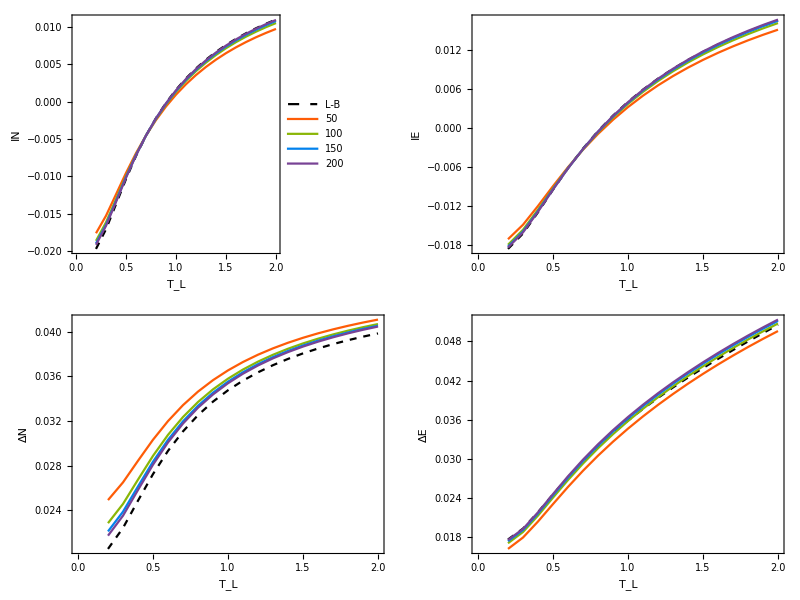
-Graphics-T_R=0.6, μ_L=0, μ_R=0.3

```mathematica
plots=Table[
ListLinePlot[Prepend[
Table[{TL,simsTL[TL,Lb,p]},{Lb,Lbs},{TL,TLs}],
Table[{TL,simsLB[TL,p]},{TL,TLs}]],

FrameLabel->{"T_L",p},
ImageSize->500,
PlotLegends->If[p=="IN",legend[Prepend[Lbs,"L-B"],{0.15,0.65}],None],
PlotStyle->Join[{Directive[Black,Dashed]},Rest@COLORLIST]
]

,{p,{"IN","IE","ΔN","ΔE"}}];
Labeled[Grid@Partition[plots,2],Style["T_R=0.6, μ_L=0, μ_R=0.3",26,FontFamily->"Times"],Top]
```

#### Comparison with the benchmarking used in Marlon’s PRX

```mathematica
Clear[simsTL,simsLB];
```

```mathematica
Clear[TL,Lb]
w = 8.;
TLs = w logspace[-3,2,50];
Lbs = {50,100,150,200};
h = TightBindingHamiltonian[w/8,Ls=1];
γ = w/8;
𝒯=NEGFTransmissionFunction[h,γ];
PrettyTiming@Monitor[Do[
LB=LandauerButtiker[𝒯,{TL,TL,μL=w/16,μR=-w/16},w]//Quiet;
simsLB[TL,"IN"]=LB["IN"];
simsLB[TL,"IE"]=LB["IE"];
simsLB[TL,"ΔN"]=LB["ΔN"];
simsLB[TL,"ΔE"]=LB["ΔE"];

Do[
{W,F}=BDThermLeadMatrices[h,γ,{TL,TL,μL,μR},Lb,8];
𝒞 = BDCovMat[W,F];
simsTL[TL,Lb,"IN"]=ThermleadsFCSAverage[𝒞,W,F,Lb,"particle","left"] ;
simsTL[TL,Lb,"IE"]=ThermleadsFCSAverage[𝒞,W,F,Lb,"energy","left"] ;
simsTL[TL,Lb,"ΔN"]=ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"particle","left"];
simsTL[TL,Lb,"ΔE"]=ThermleadsFCSDiffusionMatrix[𝒞,W,F,Lb,"energy","left"];

,{Lb,Lbs}];
,{TL,TLs}],{TL,Lb}]//Quiet
```

0h : 2m : 13s

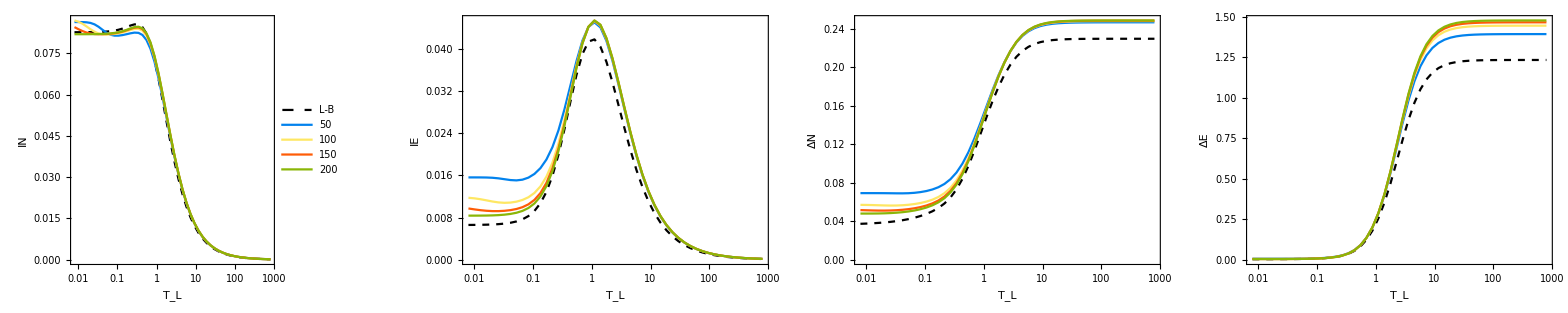
-Graphics-Same as Fig. 6,7(c) of Marlon's PRX

```mathematica
plots=Table[
ListLogLinearPlot[Prepend[
Table[{TL,simsTL[TL,Lb,p]},{Lb,Lbs},{TL,TLs}],
Table[{TL,simsLB[TL,p]},{TL,TLs}]],

FrameLabel->{"T_L",p},
Joined->True,
AspectRatio->2,
ImageSize->250,
FrameTicks->{{Automatic,Automatic},{logticks[-3,1,1],Automatic}},
PlotLegends->If[p=="IN",legend[Prepend[Lbs,"L-B"],{0.15,0.65}],None],
PlotStyle->Join[{Directive[Black,Dashed]},COLORLIST⟦{4,-3,2,3}⟧]
]
,{p,{"IN","IE","ΔN","ΔE"}}];
Labeled[Grid@{plots},Style["Same as Fig. 6,7(c) of Marlon's PRX",20,FontFamily->"Times"],Top]
```

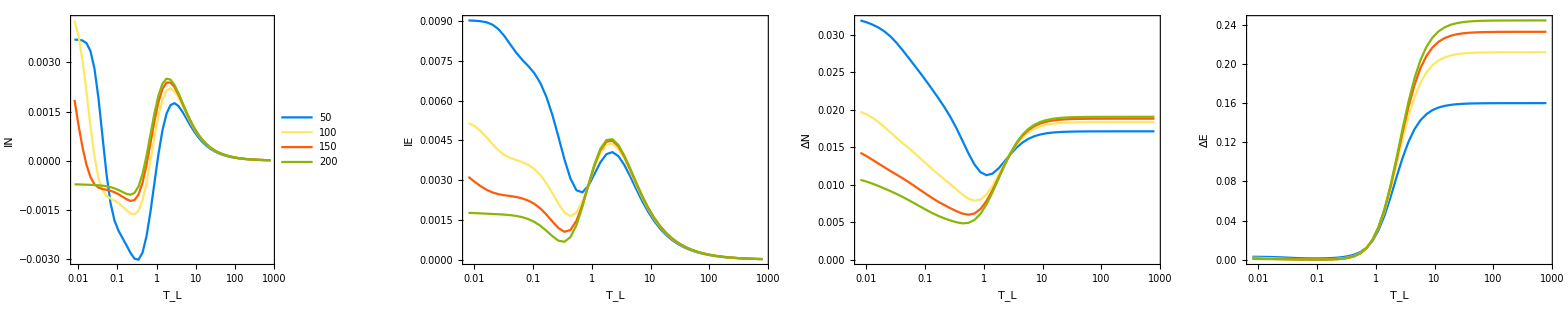
-Graphics-Same as Fig. 6,7(c) of Marlon's PRX

```mathematica
plots=Table[
ListLogLinearPlot[
Table[{TL,simsTL[TL,Lb,p]-simsLB[TL,p]},{Lb,Lbs},{TL,TLs}],

FrameLabel->{"T_L",p},
Joined->True,
AspectRatio->2,
ImageSize->250,
FrameTicks->{{Automatic,Automatic},{logticks[-3,1,1],Automatic}},
PlotLegends->If[p=="IN",legend[Lbs,{0.15,0.65}],None],
PlotStyle->COLORLIST⟦{4,-3,2,3}⟧
]
,{p,{"IN","IE","ΔN","ΔE"}}];
Labeled[Grid@{plots},Style["Same as Fig. 6,7(c) of Marlon's PRX",20,FontFamily->"Times"],Top]
```

```mathematica
simsLB[TLs⟦3⟧,"IN"]
```

0.0826459

```mathematica
LandauerButtiker[𝒯,{TLs⟦-1⟧,TLs⟦-1⟧,μL=w/16,μR=-w/16},w]["ΔN"]
```

0.229902

```mathematica
LandauerButtiker[𝒯,{TLs⟦-1⟧,TLs⟦-1⟧,μL=w/16,μR=-w/16},2w,MachinePrecision,1000]["ΔN"]
```

0.240026

```mathematica
LandauerButtiker[𝒯,{TLs⟦1⟧,TLs⟦1⟧,μL=w/16,μR=-w/16},2w,MachinePrecision,1000]["ΔN"]
```

0.0373425

```mathematica
Lb = 200;
{W,F}=BDThermLeadMatrices[h,γ,{TLs⟦3⟧,TLs⟦3⟧,μL,μR},Lb,10];
𝒞 = BDCovMat[W,F];
ThermleadsFCSAverage[𝒞,W,F,Lb,"particle","left"]
```

0.0818812

#### Verifying the expression for the energy current fluctuations

Verifying the formula 

tr(c_j^†c_i ℒ'(ρ)) - tr(c_j^†c_i ρ)tr(ℒ'(ρ)) = -1/2{(1-𝒞).G.𝒞 +𝒞.G.(1-𝒞)}

derived using Wick’s theorem.

```mathematica
h = TightBindingHamiltonian[1,Ls=2];
γ = 0.1;
𝒯=NEGFTransmissionFunction[h,γ];
{W,F}=BDThermLeadMatrices[h,γ,{TL=0.9,TR=1.2,μL=0.0,μR=0.3},Lb=3,8];
𝒞 = BDCovMat[W,F];
G=ThermleadsFCSGMatrix[W,Lb,"energy","left"]//mf;
```

(0 | 0 | 0 | 1.51388-0.504627 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-1.4273 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | -1.51388-0.504627 ⅈ | 0 | 0 | 0 | 0
-1.51388-0.504627 ⅈ | 0.-1.4273 ⅈ | 1.51388-0.504627 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* Full formula using Fermionic operators *)
L=2Lb+Ls;
M = RandomReal[{-3,3},{L,L}];
M = M + Mᵀ;
LoadFermionicOperators[L];
ρ = MatrixExp[-Sum[M⟦i,j⟧ cd[i].c[j],{i,L},{j,L}]];
ρ = ρ/Tr[ρ];
ℒ1p=-1/2 Sum[G⟦i,j⟧(cd[i].c[j].ρ+ρ.cd[i].c[j]),{i,L},{j,L}];
𝒞 = Table[Tr[cd[j].c[i].ρ],{i,L},{j,L}];

mat1=Table[Tr[cd[j].c[i].ℒ1p],{i,L},{j,L}]- 𝒞 Tr[ℒ1p]//mf;
```

(0.+0.0511396 ⅈ | -0.0373876-0.00338799 ⅈ | 0.0177422-0.0547652 ⅈ | -0.578058+0.141223 ⅈ | -0.0731729-0.0777214 ⅈ | -0.0304993+0.00426106 ⅈ | -0.0764823-0.0808712 ⅈ | -0.0054545+0.0547906 ⅈ
0.0373876-0.00338799 ⅈ | 0.-0.078929 ⅈ | -0.0667638-0.00228857 ⅈ | 0.199364+0.231291 ⅈ | 0.0963552+0.102647 ⅈ | 0.0395931-0.00621602 ⅈ | 0.0710989+0.056416 ⅈ | 0.0128986-0.0620079 ⅈ
-0.0177422-0.0547652 ⅈ | 0.0667638-0.00228857 ⅈ | 0.+0.0582056 ⅈ | 0.640271+0.100713 ⅈ | 0.0849411+0.0905196 ⅈ | 0.0356743-0.0050067 ⅈ | 0.102836+0.0904213 ⅈ | 0.00361918-0.0630389 ⅈ
0.578058+0.141223 ⅈ | -0.199364+0.231291 ⅈ | -0.640271+0.100713 ⅈ | 0.-0.191498 ⅈ | 0.124195+0.1305 ⅈ | 0.0487296-0.00808043 ⅈ | -0.0282789+0.0565065 ⅈ | 0.0397723-0.0757068 ⅈ
0.0731729-0.0777214 ⅈ | -0.0963552+0.102647 ⅈ | -0.0849411+0.0905196 ⅈ | -0.124195+0.1305 ⅈ | 0.-0.00197406 ⅈ | -0.0011132+0.000833015 ⅈ | -0.0579592+0.0600156 ⅈ | 0.0111872-0.0113624 ⅈ
0.0304993+0.00426106 ⅈ | -0.0395931-0.00621602 ⅈ | -0.0356743-0.0050067 ⅈ | -0.0487296-0.00808043 ⅈ | 0.0011132+0.000833015 ⅈ | 0.-0.0000897804 ⅈ | -0.0229945-0.00291078 ⅈ | 0.00474592+0.000188967 ⅈ
0.0764823-0.0808712 ⅈ | -0.0710989+0.056416 ⅈ | -0.102836+0.0904213 ⅈ | 0.0282789+0.0565065 ⅈ | 0.0579592+0.0600156 ⅈ | 0.0229945-0.00291078 ⅈ | 0.+0.0949528 ⅈ | 0.0160136-0.0489878 ⅈ
0.0054545+0.0547906 ⅈ | -0.0128986-0.0620079 ⅈ | -0.00361918-0.0630389 ⅈ | -0.0397723-0.0757068 ⅈ | -0.0111872-0.0113624 ⅈ | -0.00474592+0.000188967 ⅈ | -0.0160136-0.0489878 ⅈ | 0.+0.0156467 ⅈ)

```mathematica
(* Formula using Wick's theorem *)
𝕀 = Eye[L];
mat2 = -1/2((𝕀-𝒞).G.𝒞 + 𝒞.G.(𝕀-𝒞))//mf;
```

(0.-0.0104667 ⅈ | -0.0285703+0.0288796 ⅈ | 0.012606+0.0155486 ⅈ | -0.414915+0.133602 ⅈ | -0.028367-0.0580209 ⅈ | 0.02987+0.0259486 ⅈ | 0.110106+0.00299044 ⅈ | -0.012451+0.0381158 ⅈ
0.0285703+0.0288796 ⅈ | 0.-0.0246057 ⅈ | -0.0557876-0.0491884 ⅈ | 0.0571095+0.387106 ⅈ | -0.0250826-0.00517708 ⅈ | 0.00912071+0.00727131 ⅈ | -0.0103383+0.032969 ⅈ | -0.0377906-0.0543593 ⅈ
-0.012606+0.0155486 ⅈ | 0.0557876-0.0491884 ⅈ | 0.-0.0223801 ⅈ | 0.424437+0.109296 ⅈ | 0.0664579+0.105056 ⅈ | -0.0623499-0.0475499 ⅈ | -0.210437-0.00914758 ⅈ | 0.0409868-0.0624216 ⅈ
0.414915+0.133602 ⅈ | -0.0571095+0.387106 ⅈ | -0.424437+0.109296 ⅈ | 0.+0.0416017 ⅈ | -0.0886997-0.11123 ⅈ | 0.0713424+0.0543185 ⅈ | 0.206905+0.0359087 ⅈ | -0.0730959+0.0197725 ⅈ
0.028367-0.0580209 ⅈ | 0.0250826-0.00517708 ⅈ | -0.0664579+0.105056 ⅈ | 0.0886997-0.11123 ⅈ | 0.+0.174267 ⅈ | -0.0171678-0.0928082 ⅈ | -0.10693-0.107107 ⅈ | -0.0265907+0.0588329 ⅈ
-0.02987+0.0259486 ⅈ | -0.00912071+0.00727131 ⅈ | 0.0623499-0.0475499 ⅈ | -0.0713424+0.0543185 ⅈ | 0.0171678-0.0928082 ⅈ | 0.+0.0486031 ⅈ | 0.0459588+0.0516105 ⅈ | 0.035535-0.02174 ⅈ
-0.110106+0.00299044 ⅈ | 0.0103383+0.032969 ⅈ | 0.210437-0.00914758 ⅈ | -0.206905+0.0359087 ⅈ | 0.10693-0.107107 ⅈ | -0.0459588+0.0516105 ⅈ | 0.+0.0299944 ⅈ | 0.150146+0.027135 ⅈ
0.012451+0.0381158 ⅈ | 0.0377906-0.0543593 ⅈ | -0.0409868-0.0624216 ⅈ | 0.0730959+0.0197725 ⅈ | 0.0265907+0.0588329 ⅈ | -0.035535-0.02174 ⅈ | -0.150146+0.027135 ⅈ | 0.-0.0919323 ⅈ)

```mathematica
mat1-mat2//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### About including the noise term in the formula for the energy variance

b_α^χ = b_α e^(-i ν_α χ/2) + ∫_0^(χ/2) ds e^(-i ν_α(χ/2-s))ξ_α(s)

Differentiating with respect to χ we get, using Laplace’s rule,  

∂_χ b_α^χ |_(χ=0) = -i ν_α b_α+ 1/2 ξ_α(0)
∂_χ b_α^-χ |_(χ=0) = i ν_α b_α- 1/2 ξ_α(0)

where ξ_α(0) = - i ∑_j κ_j b_(α,j). Thus 

ℒ'(ρ) = - ∑_α Λ_α{ν_α c^†b_α-ν_α^*b_α^†c, ρ}  - i/2 Λ_α{c^†ξ_α(0)+ξ_α^†(0) c,ρ} 

This will therefore not appear in the average current, because throughout we assume that ξ_α(0)  and c are uncorrelated. 
But it will appear in the RHS of the 2nd moment because using d = {c,b_1,b_2,...} and 

tr(d_j^†d_i ℒ'(ρ)) = ...  -i/2 ∑_α Λ_α ⟨d_j^†d_i d_1^†ξ_α + d_j^†d_i ξ_α^†d_1 + d_1^†ξ_α d_j^†d_i + ξ_α^†d_1 d_j^†d_i⟩ 

We can use the following result: 

  ⟨b_α^†ξ_α'(0)⟩ = δ_(α,α')γ_α/2 f_α = ⟨ξ_α'^†(0)b_α⟩ 
  
  Thus 
  
  ⟨d_j^†d_i d_1^†ξ_α⟩ = ⟨d_i d_1^†⟩ δ_(α,j)γ_j/2 f_j(1-δ_(1,j))
  
  ⟨d_j^†d_i ξ_α^† d_1⟩ = ⟨d_j^†d_1⟩ δ_(α,i)γ_i/2 f_i (1-δ_(1,i))
  
  ⟨d_1^†ξ_α d_j^†d_i ⟩ = ⟨d_1^†d_i⟩ δ_(α,j)γ_j/2 f_j(1-δ_(1,j))
  
  ⟨ξ_α^†d_1 d_j^†d_i⟩ = ⟨d_1 d_j^†⟩ δ_(α,i)γ_i/2 f_i(1-δ_(1,i))

Hence  
  
  tr(d_j^†d_i ℒ'(ρ)) = ...  -i/2 Λ_j γ_j/2 f_j (⟨d_i d_1^†⟩ +⟨d_1^†d_i⟩ )(1-δ_(1,j)) - i/2 Λ_i γ_i/2 f_i (⟨d_j^†d_1⟩ +⟨d_1 d_j^†⟩)(1-δ_(1,i)) 
  
  = ... - i/2 Λ_j γ_j/2 f_j δ_(1,i)(1-δ_(1,j)) - i/2 Λ_i γ_i/2 f_i δ_(1,j)(1-δ_(1,i))

```mathematica
NewG[W_,F_,Lb_,bath_:"left"]:=Module[{Ls = Length@W-2Lb,γ,ϵ,Λ,f,newG},
{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
f = Diagonal[F]⟦1;;Lb⟧/γ;
newG =SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>(-ⅈ/2 Λ γ/2 f)⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}];
newG-newG†
]
```

```mathematica
NewG[W,F,Lb]//mf;
```

(0 | 0 | 0 | 0.-0.251993 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.356825 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.000320694 ⅈ | 0 | 0 | 0 | 0
0.-0.251993 ⅈ | 0.-0.356825 ⅈ | 0.-0.000320694 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
G=ThermleadsFCSGMatrix[W,Lb,"energy","left"]//mf;
```

(0 | 0 | 0 | 1.51388-0.504627 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-1.4273 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | -1.51388-0.504627 ⅈ | 0 | 0 | 0 | 0
-1.51388-0.504627 ⅈ | 0.-1.4273 ⅈ | 1.51388-0.504627 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Clear[ThermleadsFCSDiffusionMatrixNoiseTerm]
ThermleadsFCSDiffusionMatrixNoiseTerm[𝒞_,W_,F_,Lb_,type_:"particle",bath_:"left"]:=Module[{𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,G,G2,γ,ϵ,Λ,newG},

newG = NewG[W,F,Lb,"left"];

𝕀 = Eye[Lb+Ls+Lb];
G=ThermleadsFCSGMatrix[W,Lb,type,bath]; 
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))+newG];
2Tr[G.𝒞t]//Chop
]
```

## Landauer-Büttiker and NEGF

### NEGF transmission function

Suitable for both numeric and symbolic manipulations. 
Returns the transmission function 

𝒯(ϵ) = tr(Γ_1 GΓ_L G†), 

in the wide-band limit, of a quantum non-interacting chain with Hamiltonian h. 

Input is a L×L matrix h, and a coupling constant γ (assumed the same for both baths).
Output is a function 𝒯(ϵ), which can be called for different ϵ.

```mathematica
(* 𝒯=tr(Subscript[Γ, 1] Subscript[GΓ, L] G†) = ⟨1|S 1/(Λ-i ϵ)S^-1|L⟩⟨L| S^(-1†)1/(Λ†+i ϵ)S†|1⟩ = |∑_k Subscript[Subscript[S, 1k](S^-1), kL]/(Subscript[Λ, k]-i ϵ)|^2 *)
Clear[NEGFTransmissionFunction];
NEGFTransmissionFunction[h_,γ_]:=Module[{L=Length@h,Γ1,ΓL,W,Λ,S,Sinv},
Γ1 = γ Proj[L,1];
ΓL = γ Proj[L,L];
(*W = ⅈ h + (Γ1 + ΓL)/2;*)
W = -ⅈ/2(Γ1+ΓL)+ h;
{Λ,S}=Quiet@Eigensystem[W];
S = Sᵀ//SparseArray;
Λ = ⅈ Λ//SparseArray;
Sinv = Inverse[S]//SparseArray;

Function[With[{u = S⟦1⟧,v=Sinv⟦All,L⟧,λ = Λ},Abs[γ u.(1/(λ-ⅈ #) v)]^2]]

];

NEGFTransmissionFunction[V_,L_,γ_]:=NEGFTransmissionFunction[TightBindingHamiltonian[V,L],γ]
NEGFTransmissionFunction[V_,L_,γ_,J_]:=NEGFTransmissionFunction[TightBindingHamiltonian[V,L,J],γ]
```

#### Example usage

Transmission function for a single quantum dot.

```mathematica
𝒯=NEGFTransmissionFunction[ϵ0,1,γ][ϵ]//cf
```

γ^2/(γ^2+ϵ^2)

Transmission function for a resonant double quantum dot.

4 γ^2 Abs[Ω/((γ-ⅈ ϵ)^2+Ω^2)]^2

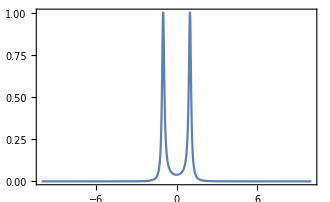

```mathematica
𝒯=FullSimplify[NEGFTransmissionFunction[0,2,2γ,Ω][ϵ],{ϵ0∈Reals,ϵ∈Reals,γ>0}]
Plot[𝒯/.{γ->0.1,Ω->1},{ϵ,-10,10}]
```

Transmission function for a homogeneous tight-binding chain

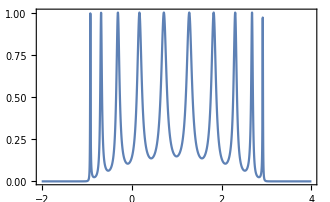

```mathematica
𝒯 = NEGFTransmissionFunction[1,10,0.4];
Plot[𝒯[ϵ],{ϵ,-2,4}]
```

Transmission function for the Aubry-André-Haper tight-binding model with 20 sites.

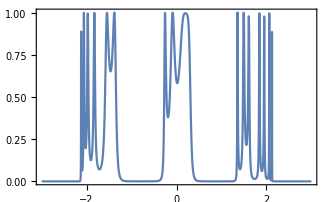

```mathematica
𝒯=NEGFTransmissionFunction[AubryAndreHarper[20],20,1];
Plot[𝒯[ϵ],{ϵ,-3,3},PlotRange->All]
```

#### Example SSH model (arxiv 1803.03609)

Based on https://arxiv.org/pdf/1803.03609.pdf

```mathematica
NEGFTransmissionFunction[SSHHamiltonian[20,1.0,0.5],0.3]
```

With[{u=S$110026⟦1⟧,v=Sinv$110026⟦All,L$110026⟧,λ=Λ$110026},Abs[u.v/(λ-ⅈ #1)]^2]&

```mathematica
δτs = linspace[-1,1,200];
𝒯 = Association[];
Do[
𝒯[δτ]=NEGFTransmissionFunction[SSHHamiltonian[20,1.0,δτ,0],0.3],{δτ,δτs}]
```

```mathematica
Quiet@ListDensityPlot[Flatten[Table[{δτ,ϵ,𝒯[δτ][ϵ]},{δτ,δτs},{ϵ,-2,2,0.0181}],1],PlotRange->All,ColorFunction->ColorData[{"PigeonTones","Reverse"}],AspectRatio->3]
```

-Graphics-

### Landauer-Büttiker & Levitov-Lesovik

```mathematica
Clear[LandauerButtiker];
LandauerButtiker[𝒯_,{TL_,TR_,μL_,μR_},em_:∞,pres_:MachinePrecision,maxrec_:Automatic]:=Module[{βL = 1/TL,βR=1/TR,δβ,δμ,δβμ,fL,fR,IN,IE,IQL,IQR,P,σ,ΔN,ΔE,𝒞,ΔP,ΔQL,ΔQR,Δσ,turN,turE,turP,turQL,turQR,a,b,Jlhyp,Δlhyp,SNRN,SNRE,SNRP,SNRQL,SNRQR,Slhyp,Shyp,hyperparameters,fcorr,turlhyp,turhyp,SNRσ,g,G},

δβ = βL-βR;
δμ = μL-μR;
δβμ = βL μL - βR μR;
fL[ϵ_]:=1/(Exp[Rationalize[βL,10^-8](ϵ-Rationalize[μL,10^-8])]+1); 
fR[ϵ_]:=1/(Exp[Rationalize[βR,10^-8](ϵ-Rationalize[μR,10^-8])]+1);  
g[ϵ_]:=fL[ϵ](1-fL[ϵ])+fR[ϵ](1-fR[ϵ]);
G[ϵ_]:=𝒯[ϵ](g[ϵ] + (fL[ϵ]-fR[ϵ])^2(1-𝒯[ϵ]));

Quiet@If[ArrayQ[em],
IN =1/(2π) NIntegrate[𝒯[ϵ](fL[ϵ]-fR[ϵ]),{ϵ,em⟦1⟧,em⟦2⟧},WorkingPrecision->pres,MaxRecursion->maxrec];
IE =1/(2π) NIntegrate[ϵ 𝒯[ϵ](fL[ϵ]-fR[ϵ]),{ϵ,em⟦1⟧,em⟦2⟧},WorkingPrecision->pres,MaxRecursion->maxrec];
ΔN =1/(2π) NIntegrate[G[ϵ],{ϵ,em⟦1⟧,em⟦2⟧},WorkingPrecision->pres,MaxRecursion->maxrec];
ΔE =1/(2π) NIntegrate[ϵ^2 G[ϵ],{ϵ,em⟦1⟧,em⟦2⟧},WorkingPrecision->pres,MaxRecursion->maxrec];
𝒞 = 1/(2π)NIntegrate[ϵ G[ϵ],{ϵ,em⟦1⟧,em⟦2⟧},WorkingPrecision->pres,MaxRecursion->maxrec] ;
Shyp = 1/(2π)NIntegrate[(𝒯[ϵ](fL[ϵ]-fR[ϵ])^2)/(fL[ϵ]+fR[ϵ]-2 fL[ϵ] fR[ϵ]-𝒯[ϵ](fL[ϵ]-fR[ϵ])^2) ,{ϵ,em⟦1⟧,em⟦2⟧},WorkingPrecision->pres,MaxRecursion->maxrec];
,
IN = 1/(2π)NIntegrate[𝒯[ϵ](fL[ϵ]-fR[ϵ]),{ϵ,-em,0},WorkingPrecision->pres,MaxRecursion->maxrec]+1/(2π)NIntegrate[𝒯[ϵ](fL[ϵ]-fR[ϵ]),{ϵ,0,em},WorkingPrecision->pres,MaxRecursion->maxrec];
IE = 1/(2π)NIntegrate[ϵ 𝒯[ϵ](fL[ϵ]-fR[ϵ]),{ϵ,-em,0},WorkingPrecision->pres,MaxRecursion->maxrec]+1/(2π)NIntegrate[ϵ 𝒯[ϵ](fL[ϵ]-fR[ϵ]),{ϵ,0,em},WorkingPrecision->pres,MaxRecursion->maxrec];
ΔN = 1/(2π)NIntegrate[G[ϵ],{ϵ,-em,em},WorkingPrecision->pres,MaxRecursion->maxrec];
ΔE = 1/(2π)NIntegrate[ϵ^2 G[ϵ],{ϵ,-em,em},WorkingPrecision->pres,MaxRecursion->maxrec];
𝒞 = 1/(2π)NIntegrate[ϵ G[ϵ],{ϵ,-em,0},WorkingPrecision->pres,MaxRecursion->maxrec]+1/(2π)NIntegrate[ϵ G[ϵ],{ϵ,0,em},WorkingPrecision->pres ,MaxRecursion->maxrec];
Shyp = 1/(2π)NIntegrate[(𝒯[ϵ](fL[ϵ]-fR[ϵ])^2)/(fL[ϵ]+fR[ϵ]-2 fL[ϵ] fR[ϵ]-𝒯[ϵ](fL[ϵ]-fR[ϵ])^2) ,{ϵ,-em,em},WorkingPrecision->pres,MaxRecursion->maxrec];
];
IQL = IE - μL IN;
IQR = IE- μR IN;
P = -δμ IN;
σ = -δβ IE + δβμ IN;

ΔP = δμ^2 ΔN;
ΔQL = ΔE - 2 μL 𝒞 + μL^2 ΔN;
ΔQR = ΔE - 2 μR 𝒞 + μR^2 ΔN;
Δσ = δβ^2 ΔE - 2 δβ δβμ 𝒞 + δβμ^2 ΔN;
turN = ΔN/IN^2 σ//Quiet;
turE = ΔE/IE^2 σ//Quiet;
turP = ΔP/P^2 σ//Quiet;
turQL = ΔQL/IQL^2 σ//Quiet;
turQR = ΔQR/IQR^2 σ//Quiet; 

fcorr = 𝒞/√(ΔN ΔE);

SNRN = IN^2/ΔN;
SNRE=IE^2/ΔE;
SNRP = P^2/ΔP;
SNRQL = IQL^2/ΔQL;
SNRQR = IQR^2/ΔQR;
SNRσ = σ^2/Δσ;

(* Hyperaccurate current *)
a = (IE ΔN - IN 𝒞) ;
b =  (IN ΔE-IE 𝒞);
Jlhyp=a IE + b IN;
Δlhyp= a^2 ΔE+b^2 ΔN+ 2 a b 𝒞;

Slhyp=Jlhyp^2/Δlhyp(*(SNRN+SNRE - 2 fcorr √(SNRN SNRE))/(1-fcorr^2); *);


turlhyp = σ/Slhyp;
turhyp = σ/Shyp;

Chop/@<|"parameters"->{TL,TR,μL,μR},
"IN"->IN,
"IE"->IE,
"IQL"->IQL,
"IQR"->IQR,
"P"->P,
"σ"->σ,
"ΔN"->ΔN,
"ΔE"->ΔE,
"𝒞"->𝒞,
"ΔP"->ΔP,
"ΔQL"->ΔQL,
"ΔQR"->ΔQR,
"Δσ"->Δσ,
"turN"->turN,
"turE"->turE,
"turP"->turP,
"turQL"->turQL,
"turQR"->turQR,
"fcorr"->fcorr,
"SNRN"->SNRN,
"SNRE"->SNRE,
"SNRP"->SNRP,
"SNRQL"->SNRQL,
"SNRQR"->SNRQR,
"SNRσ"->SNRσ,
"hyperparameters"->{a,b},
"Jlhyp"->Jlhyp,
"Δlhyp"->Δlhyp,
"Slhyp"->Slhyp,
"Shyp"->Shyp,
"turlhyp"->turlhyp,
"turhyp"->turhyp
|>

]
```

#### Usage

Transport across a single quantum dot

```mathematica
ϵ0 = 0.0;
γ = 0.1;
𝒯=NEGFTransmissionFunction[ϵ0,1,γ];
result=LandauerButtiker[𝒯,{0.1,0.3,1.1,-1.1}]
```

<|parameters→{0.1,0.3,1.1,-1.1},IN→0.286449,IE→0.00105411,IQL→-0.314039,IQR→0.316148,P→0.630187,σ→4.19422,ΔN→0.137527,ΔE→0.0178751,𝒞→0.000818081,ΔP→0.66563,ΔQL→0.182483,ΔQR→0.186082,Δσ→2.65153,turN→7.02983,turE→67472.9,turP→7.02983,turQL→7.76077,turQR→7.80866,SNRN→0.596631,SNRE→0.0000621616,SNRP→0.596631,SNRQL→0.540438,SNRQR→0.537124,hyperparameters→{-0.0000893697,0.00511945},hypercurrent→0.00146636,hypervariance→3.6038×10^-6,SNRhyper→0.596655|>

The result is an association with loads of properties already computed .

```mathematica
Dataset`$DatasetTargetRowCount=40;
Dataset[result]
```

Individual properties can be retrived as follows

```mathematica
result["IN"]
result["ΔN"]
```

0.286449

0.137527

#### Ex: TUR violations in a boxcar and a double quantum dot (Ptaszyński, PRB, 98, 085425)

```mathematica
Clear[γ,Ω,ϵ0];
FullSimplify[NEGFTransmissionFunction[ϵ0,2,γ,Ω][ϵ]]
```

16 Abs[(γ Ω)/((γ-2 ⅈ (ϵ-ϵ0))^2+4 Ω^2)]^2

```mathematica
γ = 0.1;
ϵ0 = 0.0;
Ω = 0.05; 

𝒯 =NEGFTransmissionFunction[0,2,γ,Ω];
TL = TR = 1.0;
sims = Association[];
δμs = range[0.01,8,0.1];
PrettyTiming@Monitor[Do[
sims[δμ] = LandauerButtiker[𝒯,{TL,TR,δμ/2,-δμ/2}],
{δμ,δμs}],δμ]
```

0h : 0m : 5s

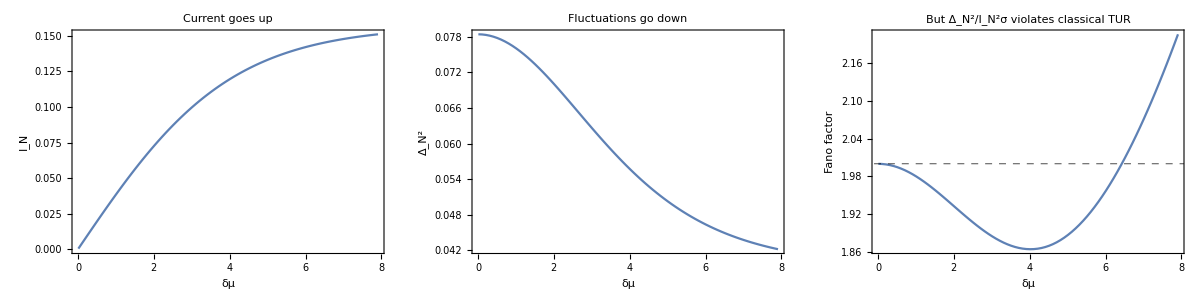

```mathematica
Grid[{{
ListLinePlot[Table[{δμ,sims[δμ]["IN"]},{δμ,δμs}],
FrameLabel->{"δμ","I_N"},AspectRatio->1,ImageSize->250,PlotLabel->Style["Current goes up",14]
],
ListLinePlot[Table[{δμ,sims[δμ]["ΔN"]},{δμ,δμs}],
FrameLabel->{"δμ","Δ_N^2"},AspectRatio->1,ImageSize->250,PlotLabel->Style["Fluctuations go down",14]
],
ListLinePlot[Table[{δμ,sims[δμ]["turN"]},{δμ,δμs}],
FrameLabel->{"δμ","Fano factor"},AspectRatio->1,ImageSize->250,GridLinesStyle->Directive[Black, Dashed],GridLines->{None,{2}},
PlotLabel->Style["But Δ_N^2/I_N^2σ violates classical TUR",14]
]
}}]
```

```mathematica
?Boxcar
```

```mathematica
𝒯 =Boxcar[-0.5,0.5];
TL = TR = 1.0;
sims2 = Association[];
δμs = range[0.01,8,0.1];
PrettyTiming@Monitor[Do[
sims2[δμ] = LandauerButtiker[𝒯,{TL,TR,δμ/2,-δμ/2},{-0.499,0.499}],
{δμ,δμs}],δμ]
```

0h : 0m : 4s

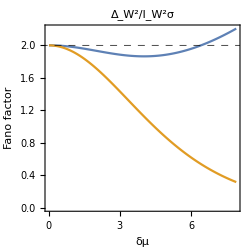

```mathematica
ListLinePlot[{
Table[{δμ,sims[δμ]["turN"]},{δμ,δμs}],
Table[{δμ,sims2[δμ]["turN"]},{δμ,δμs}]},
FrameLabel->{"δμ","Fano factor"},AspectRatio->1,ImageSize->250,GridLinesStyle->Directive[Black, Dashed],GridLines->{None,{2}},
PlotLabel->Style["Δ_W^2/I_W^2σ",14]
]
```

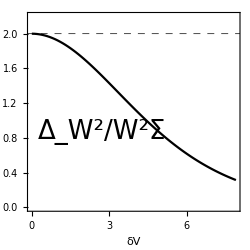

```mathematica
ListLinePlot[{
Table[{δμ,sims2[δμ]["turN"]},{δμ,δμs}]},
FrameLabel->{"δV",None},AspectRatio->1,ImageSize->250,GridLinesStyle->Directive[Black, Dashed],GridLines->{None,{2}},
PlotRange->{0,2.2},

PlotStyle->Black,
Epilog->Text[Style["Δ_W^2/W^2Σ",26],Scaled[{0.35,0.4}]]
]
```

#### Ex: Conductance quantization in a quantum point contact

Based on https://journals.aps.org/prb/abstract/10.1103/PhysRevB.103.235120 
Eqs. (B1)-(B3) and (A.14)

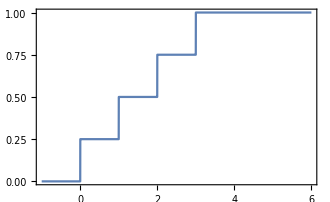

```mathematica
(* Define transmission function *)
Clear[𝒯]
𝒯= Function[1/4 Total@Table[Boxcar[n,100][#],{n,0,3,1}]];
Plot[𝒯[ϵ],{ϵ,-1,6}]
```

Simulate for different μ, with fixed T_L=T_R and fixed (small) δ_μ.

```mathematica
Clear[sims];
sims = Association[];

TL = 0.02;
TR = 0.02;
δμ = 0.005;
μs = Rest@range[0,4,0.05];
Monitor[Do[
sims[μ] = LandauerButtiker[𝒯,{TL,TR,μ+δμ/2,μ-δμ/2},{0,100}],
{μ,μs}],μ]//Quiet
```

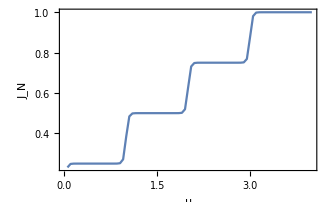

```mathematica
ListLinePlot[Table[{μ,sims[μ]["IN"] /δμ},{μ,μs}],
FrameLabel->{"μ","J_N"}
]
```

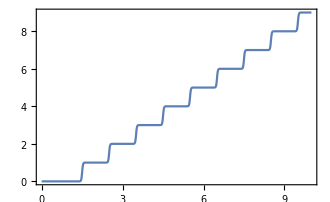

```mathematica
(* c.f. E.q. (4.53) of https://research.chalmers.se/en/publication/520374*)
(* I find this a bit weird. They call it a "transmission probability", but it can easily go beyond 1 *)
Clear[ϵ,γ,En];
En = V0 + ωy(n+1/2);
γ = ωx/(2π);
V0=1;
ωy = 1;
ωx = 0.1;
Plot[Sum[1/(1+Exp[(En-ϵ)/γ]),{n,0,10}],{ϵ,0,10}]
Clear[ωx,ωy,γ,V0,En,ϵ]
```

### NEGF full covariance matrix

Based on https://arxiv.org/pdf/1106.3207.pdf

Covariance matrix is given by Eq. (2.8)

C = ∫ dω/(2π)(GΓ_1 G† f_1 +GΓ_L G†f_L)

where (Γ_i,f_i) are the coupling matrices and Fermi-Dirac distributions of the left (i=1) and right (i=L) baths, and 

G(ω)=(W - iω)^-1 = (i h +(Γ_1+Γ_L)/2-i ω)^-1

is the NEGF. 

The function below assumes W is diagonalizable as W=SΛS^-1. 
The covariance matrix can then be written as 

C = S Y S†

where 

Y_ij=(γ_1(S^-1))_i1(S^-1)_j1^*A_ij^1 + (γ_L(S^-1))_iL(S^-1)_jL^*A_ij^L 

where 

A_ij = ∫dΩ/(2π) (f(Ω))/((Ω+i λ_i)(Ω-i λ_j^*))  = 1/(x-y)(i/2+1/(2π)ψ(1/2-i(β x)/(2π))-1/(2π)ψ(1/2+i(β y)/(2π))),  (computable using residuals)

with  f(Ω) = 1/(e^(β(Ω-μ))+1) , x = i Λ_j^*-μ, y = iΛ_i-μ and ψ(z) = Γ’(z)/Γ(z) being the digamma function. 

Below the matrices A_ij are written using a compiled function for speed.

```mathematica
(* Auxiliary function, pre-compiled for speed *)
Clear[NEGFAuxMat];
NEGFAuxMat= Compile[{{Λ,_Complex,1},{β,_Real},{μ,_Real}}, 

Module[{x,y,ψp,ψm},

x = ⅈ Λ*-μ;
y=-ⅈ Λ-μ;
ψp = Table[PolyGamma[(ⅈ β y⟦i⟧)/(2π)+1/2],{i,Length@Λ}];
ψm = Table[PolyGamma[-(ⅈ β x⟦j⟧)/(2π)+1/2],{j,Length@Λ}];

Table[1/(x⟦j⟧-y⟦i⟧)(ⅈ/2+1/(2π)(ψm⟦j⟧-ψp⟦i⟧)),{i,Length@Λ},{j,Length@Λ}]

](*,CompilationTarget->"C"*)
];
```

```mathematica
NEGFCovMat[h_,γ_,{TL_,TR_,μL_,μR_}]:=Module[{L = Length@h,Γ,W,Λ,S,Sinv,g,ppart,K,Y,ℐ,amat,Γ1,ΓL,A1,AL},

Γ1 = SparseArray[{{1,1}->γ},{L,L}];
ΓL = SparseArray[{{L,L}->γ},{L,L}];
Γ = Γ1+ΓL;
W = -ⅈ Γ/2+ h;
{Λ,S}=Quiet@Eigensystem[W];
S = Sᵀ//SparseArray;
Λ = ⅈ Λ//SparseArray;
Sinv = Inverse[S]//SparseArray;
A1 =SparseArray@NEGFAuxMat[Normal@Λ,1/TL,μL];
AL=SparseArray@NEGFAuxMat[Normal@Λ,1/TR,μR];
Y = A1 (Sinv.Γ1.Sinv†)+AL (Sinv.ΓL.Sinv†);
S.Y.S†//Chop
]
```

```mathematica
NEGFCurrents[V_,L_,γ_,βL_,βR_,μL_,μR_]:=Module[{𝒞,JN,JE,JQL,JQR,P,σ,v,i=2},

𝒞 = NEGFCovMat[V,L,γ,βL,βR,μL,μR];
JN =  -ⅈ (𝒞⟦2,1⟧-𝒞⟦1,2⟧)//Chop;
v = If[VectorQ[V],V⟦1⟧,V]//Chop;
JE = ⅈ v ((𝒞⟦i-1,i⟧-𝒞⟦i,i-1⟧)-(𝒞⟦i+1,i⟧-𝒞⟦i,i+1⟧))+ ⅈ (𝒞⟦i+1,i-1⟧-𝒞⟦i-1,i+1⟧)//Chop;
JQL = JE - μL JN//Chop;
JQR = JE - μR JN//Chop;
P = -(μL-μR) JN//Chop;
σ = -(βL-βR) JE + (βL μL - βR μR) JN//Chop;
<|"JN"->JN,"JE"->JE,"JQL"->JQL,"JQR"->JQR,"P"->P,"σ"->σ|>
]
```

#### Example usage

```mathematica
h = TightBindingHamiltonian[1,4];
𝒞=NEGFCovMat[h,1,{0.1,0.1,0,0}]//mf;
```

(0.278407 | 0.239852 | 0.157796 | 0.0452858
0.239852 | 0.350813 | 0.317098 | 0.157796
0.157796 | 0.317098 | 0.350813 | 0.239852
0.0452858 | 0.157796 | 0.239852 | 0.278407)

```mathematica
(* Compare with the thermal state when γ -> 0 *)
𝒞=NEGFCovMat[h,0.000001,{0.1,0.1,0,0}];
𝒞th=Inverse[MatrixExp[h/0.1]+Eye[4]]//Quiet;
Norm[𝒞-𝒞th]
```

8.54403×10^-6

#### Comparison with Landauer-Büttiker

```mathematica
h = TightBindingHamiltonian[V=3.0,4];
𝒞=NEGFCovMat[h,γ = 0.6,{TL=0.9,TR=0.3,μL=0.3,μR=0}]//mf;
𝒯=NEGFTransmissionFunction[h,γ];
LB=LandauerButtiker[𝒯,{TL,TR,μL,μR}];
```

(0.0783399 | 0.039106-0.0100397 ⅈ | 0.0153577-0.00854069 ⅈ | 0.0042431-0.00346205 ⅈ
0.039106+0.0100397 ⅈ | 0.0533622 | 0.037689-0.0100397 ⅈ | 0.0159656-0.00854069 ⅈ
0.0153577+0.00854069 ⅈ | 0.037689+0.0100397 ⅈ | 0.0539701 | 0.0384044-0.0100397 ⅈ
0.0042431+0.00346205 ⅈ | 0.0159656+0.00854069 ⅈ | 0.0384044+0.0100397 ⅈ | 0.0716112)

```mathematica
(* Particle current *) 
-ⅈ  (𝒞⟦2,1⟧-𝒞⟦1,2⟧)//Chop
LB["IN"]
```

0.0200794

0.0200794

```mathematica
JE = ⅈ (V(𝒞⟦i-1,i⟧-𝒞⟦i,i-1⟧) + (𝒞⟦i+1,i-1⟧-𝒞⟦i-1,i+1⟧))//Chop
LB["IE"]
```

0.0431568

0.0431568

#### Example: coherence in a double quantum dot

```mathematica
Clear[T,γ,ϵ,eV,μL,μR,g,gs,𝒞];
T = 100;
γ = 1.0;
ϵ=0;
eV = 625; 
μL = eV/2;
μR = -eV/2;
gs = linspace[0.001,4,100];

Clear[𝒞,g];
Do[
𝒞[g] = NEGFCovMat[({{ϵ, g}, {g, ϵ}}),γ,{T,T,μL,μR}],{g,gs}]
```

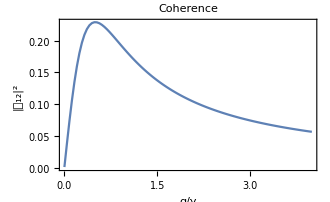

```mathematica
ListLinePlot[Table[{g,𝒞[g]⟦1,2⟧//Abs},{g,gs}],
FrameLabel->{"g/γ","|𝒞_12|^2"},
PlotLabel->"Coherence"
]
```

## TURs

### Hasegawa steady-state TUR

Based on https://link.aps.org/doi/10.1103/PhysRevLett.125.050601

In this case H_θ = (1+θ) H and L_(k,θ) = √(1+θ)L_k
Hence 

∂_θ H = H   and   ∂_θ L_(k,θ) = 1/(2 √(1+θ))L_k= L_k/2 since  we want both evaluated in the limit θ → 0.

```mathematica
Clear[HasegawaSteadyStateTUR];
HasegawaSteadyStateTUR[ρ_,ℒ_,H_,cops_]:=GammelmarkMolmerMFisher[ρ,ℒ,H,H,cops,#/2&/@cops]
```

#### Example usage

```mathematica
g = {1,0};
e = {0,1};
H = Δ out[e,e] + Ω/2(out[e,g] + out[g,e]);
L = √κ out[g,e];
ℒ = Liouvillian[H,{out[g,e]},{κ}];
ρ = AnalyticalSteadyState[ℒ]//Simplify//mf;
```

(1-Ω^2/(4 Δ^2+κ^2+2 Ω^2) | (-2 Δ Ω+ⅈ κ Ω)/(4 Δ^2+κ^2+2 Ω^2)
-((2 Δ+ⅈ κ) Ω)/(4 Δ^2+κ^2+2 Ω^2) | Ω^2/(4 Δ^2+κ^2+2 Ω^2))

```mathematica
has=HasegawaTUR[ρ,ℒ,H,{L}]//cf
```

(κ^2 (4 Δ^2+κ^2)^2 Ω^2+4 (8 Δ^4+6 Δ^2 κ^2+3 κ^4) Ω^4+4 (16 Δ^2+9 κ^2) Ω^6+32 Ω^8)/(κ (4 Δ^2+κ^2+2 Ω^2)^3)

```mathematica
𝒟 = FCSDiffusionMatrix[ρ,ℒ,{L}]//cf
J=Tr[L†.L.ρ]//cf
```

(κ Ω^2 ((4 Δ^2+κ^2)^2-2 (-12 Δ^2+κ^2) Ω^2+4 Ω^4))/((4 Δ^2+κ^2+2 Ω^2)^3)

(κ Ω^2)/(4 Δ^2+κ^2+2 Ω^2)

```mathematica
𝒟
```

(κ Ω^2 ((4 Δ^2+κ^2)^2-2 (-12 Δ^2+κ^2) Ω^2+4 Ω^4))/((4 Δ^2+κ^2+2 Ω^2)^3)

```mathematica
𝒟/J^2//Simplify
```

((4 Δ^2+κ^2)^2-2 (-12 Δ^2+κ^2) Ω^2+4 Ω^4)/(κ Ω^2 (4 Δ^2+κ^2+2 Ω^2))

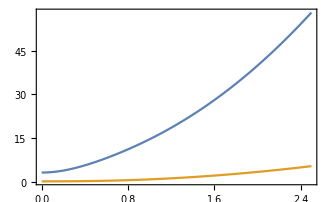

```mathematica
Plot[Evaluate[{𝒟/J^2,1/has}/.{Ω->1,κ->1/2}],{Δ,0,2.5}]
```

### Hasegawa transient TUR

Based on https://link.aps.org/doi/10.1103/PhysRevLett.126.010602

```mathematica
Clear[HasegawaTransientTUR]
HasegawaTransientTUR[t_,ρ_,H_,cops_]:=Module[{Ξ,Heff,V0},
Heff = EffectiveNonHermitianHamiltonian[H,cops];
V0 = MatrixExp[-ⅈ Heff t];
Ξ = Tr[Inverse[(V0†.V0)].ρ]- 1
]
```

#### Example usage

```mathematica
g = {1,0};
e = {0,1};
H = Δ out[e,e] + Ω/2(out[e,g] + out[g,e]);
L = √κ out[g,e];
ℒ = Liouvillian[H,{out[g,e]},{κ}];
ρ = ({{0, 0}, {0, 1}});
(*ρ = AnalyticalSteadyState[ℒ]//Simplify//mf;*)
```

```mathematica
Ξ=HasegawaTransientTUR[t,ρ,H,{L}];
ℒχ =ℒ-JumpOp[L] + ⅇ^(ⅈ χ)JumpOp[L]//cf;
𝒞 = Log@UnTr[MatrixExp[ℒχ t].Vec[ρ]];
𝒟 = (-ⅈ)^2 D[𝒞,χ,χ]/.χ->0;
J=-ⅈ D[𝒞,χ]/.χ->0;
```

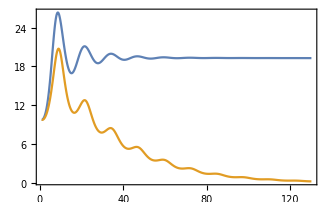

```mathematica
Plot[Evaluate[Re@{𝒟/J^2 t,t/Ξ}/.{Ω->0.5,κ->0.1,Δ->0.0}],{t,1,130},PlotRange->All]
```

### Modified Hasegawa’s bound

```mathematica
Clear[ModifiedHasegawa];
ModifiedHasegawa[ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M0,R,ℒbig,ℒα,Jα,ws,𝒟,M,ℋ,ψ},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
Jk = Table[UnTr[lop.ρv],{lop,L}];

M0 = Which[
type=="PD",Total@Jk,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

ℋ = ℒ-Sum[LindbladToVec[lop],{lop,LL}];
ws = Table[DrazinApply[ℒ,ℋ.ρv],{r,R}];

ψ = Table[1/(μ⟦r⟧.Jk)Sum[μ⟦r,k⟧ UnTr[L⟦k⟧.ws⟦r⟧],{k,d}],{r,R}]⟦1⟧;
{M0,ψ,1/M0(1+ψ)^2} 
]
```

```mathematica
(*Clear[ModifiedHasegawaOptimalDeformation];
ModifiedHasegawaOptimalDeformation[ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟μ,ℒ1,x,ℒJ},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
Jk = Table[UnTr[lop.ρv],{lop,L}];

M = Which[
type=="PD",μ.DiagonalMatrix[Jk].μᵀ,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

ℒJ = Sum[μ⟦1,k⟧ L⟦k⟧,{k,d}];
ws = Table[DrazinApply[ℒ,LindbladToVec[LL⟦q⟧].ρv],{i,R},{q,d}];
Total@Table[(μ⟦1,k⟧ Jk⟦k⟧ - UnTr[ℒJ.ws⟦1,k⟧])^2/Jk⟦k⟧,{k,d}]
];*)
```

```mathematica
(* Apparently wrong *)
Clear[ModifiedHasegawaUnitary];
ModifiedHasegawaUnitary[ρ_,ℒ_,LL_,H_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M0,R,ℒbig,ℒα,Jα,ws,𝒟,M,ℋ,ψ,wn,wd,ℒJ},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
Jk = Table[UnTr[lop.ρv],{lop,L}];

M0 = Which[
type=="PD",Total@Jk,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

wn = DrazinApply[ℒ,Vec[-ⅈ(H.ρ-ρ.H)]];
wd = DrazinApply2[ℒ, ρv,Vec[H.ρ+ρ.H]];
ℒJ = Sum[μ⟦1,k⟧ L⟦k⟧,{k,d}];

-UnTr[ℒJ.wn]^2/Tr[H.Unvec[wd]]
]
```

#### Example usage

```mathematica
Clear[γ,Ω,Δ];
H = Δ/2 σz+Ω/2 σx;
cops = {√γm σm,√γp σp};
ℒ = Liouvillian[H,cops]//cf;
ρ = AnalyticalSteadyState[ℒ]//cf//mf;
```

((γp ((γm+γp)^2+4 Δ^2)+(γm+γp) Ω^2)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2))) | -(ⅈ (γm-γp) (γm+γp-2 ⅈ Δ) Ω)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2)))
(ⅈ (γm-γp) (γm+γp+2 ⅈ Δ) Ω)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2))) | (γm ((γm+γp)^2+4 Δ^2)+(γm+γp) Ω^2)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2))))

```mathematica
J=FCSAverage[ρ,ℒ,cops,{{μ1,μ2}}]//cf
𝒟 = FCSDiffusionMatrix[ρ,ℒ,cops,{{μ1,μ2}}]//cf;
ratio = 𝒟/J^2;
```

(γm γp ((γm+γp)^2+4 Δ^2) (μ1+μ2)+(γm+γp) (γm μ1+γp μ2) Ω^2)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2)))

```mathematica
M = μ1^2 FCSAverage[ρ,ℒ,cops,{{1,0}}]+μ2^2 FCSAverage[ρ,ℒ,cops,{{0,1}}]//cf
```

(γm γp ((γm+γp)^2+4 Δ^2) (μ1^2+μ2^2)+(γm+γp) (γm μ1^2+γp μ2^2) Ω^2)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2)))

```mathematica
{M0,ψ,bound}=ModifiedHasegawa[ρ,ℒ,cops,{{μ1,μ2}}]//cf
```

{(2 γm γp ((γm+γp)^2+4 Δ^2)+(γm+γp)^2 Ω^2)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2))),-((2 (γm-γp) (γm+γp)^2 (γm μ1-γp μ2) Ω^2)/(γm γp ((γm+γp)^2+4 Δ^2)^2 (μ1+μ2)+((γm+γp)^2+4 Δ^2) (γm (γm+3 γp) μ1+γp (3 γm+γp) μ2) Ω^2+2 (γm+γp) (γm μ1+γp μ2) Ω^4)),((γm+γp) (γm γp ((γm+γp)^2+4 Δ^2)^2 (μ1+μ2)+(γm (-((γm-5 γp) (γm+γp)^2)+4 (γm+3 γp) Δ^2) μ1+γp ((5 γm-γp) (γm+γp)^2+4 (3 γm+γp) Δ^2) μ2) Ω^2+2 (γm+γp) (γm μ1+γp μ2) Ω^4)^2)/((2 γm γp ((γm+γp)^2+4 Δ^2)+(γm+γp)^2 Ω^2) (γm γp ((γm+γp)^2+4 Δ^2) (μ1+μ2)+(γm+γp) (γm μ1+γp μ2) Ω^2)^2 ((γm+γp)^2+2 (2 Δ^2+Ω^2)))}

```mathematica
Limit[ψ,Ω->0]
```

0

```mathematica
(* Apparently horrible; still to check *)
boundOpt = ModifiedHasegawaOptimalDeformation[ρ,ℒ,cops,{{μ1,μ2}}]//cf
```

ModifiedHasegawaOptimalDeformation[{{(γp ((γm+γp)^2+4 Δ^2)+(γm+γp) Ω^2)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2))),-(ⅈ (γm-γp) (γm+γp-2 ⅈ Δ) Ω)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2)))},{(ⅈ (γm-γp) (γm+γp+2 ⅈ Δ) Ω)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2))),(γm ((γm+γp)^2+4 Δ^2)+(γm+γp) Ω^2)/((γm+γp) ((γm+γp)^2+2 (2 Δ^2+Ω^2)))}},{{-γm,-(ⅈ Ω)/2,(ⅈ Ω)/2,γp},{-(ⅈ Ω)/2,1/2 (-γm-γp+2 ⅈ Δ),0,(ⅈ Ω)/2},{(ⅈ Ω)/2,0,1/2 (-γm-γp-2 ⅈ Δ),-(ⅈ Ω)/2},{γm,(ⅈ Ω)/2,-(ⅈ Ω)/2,-γp}},{{{0,0},{√γm,0}},{{0,√γp},{0,0}}},{{μ1,μ2}}]

```mathematica
hasegawaoriginal = 1/HasegawaSteadyStateTUR[ρ,ℒ,H,cops]//cf;
```

```mathematica
boundUnitary = ModifiedHasegawaOptimalDeformation[ρ,ℒ,cops,H,{{μ1,μ2}}]//cf;
```

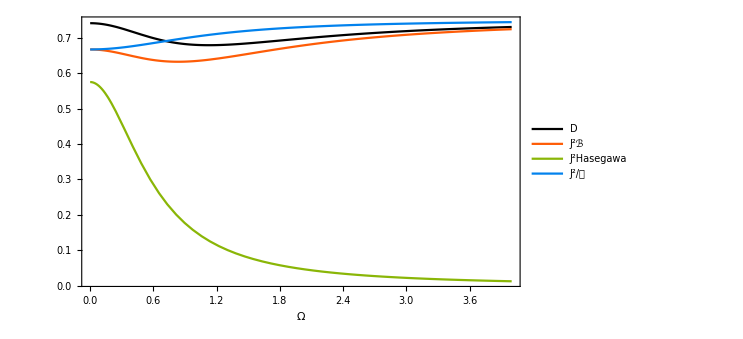
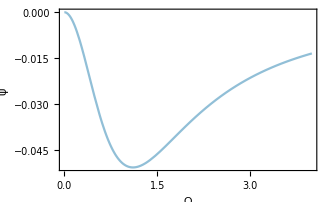

```mathematica
{Plot[Evaluate[Re@{𝒟,J^2 bound,J^2 hasegawaoriginal,J^2/M0}/.{Δ->0.3,γm->1,γp->0.5,μ1->1,μ2->1}],{Ω,0,4},
ImageSize->550,
PlotStyle->COLORLIST,
FrameLabel->{"Ω",None},
PlotLegends->legend[{"D","J^2ℬ","J^2Hasegawa","J^2/𝒦"},{0.77,0.7}]
],
Plot[Evaluate[Re@{ψ}/.{Δ->0.3,γm->1,γp->0.5,μ1->1,μ2->1}],{Ω,0,4},
PlotStyle->COLORLIST,
FrameLabel->{"Ω","ψ"},
FrameLabel->{"Ω",None}
]}
```

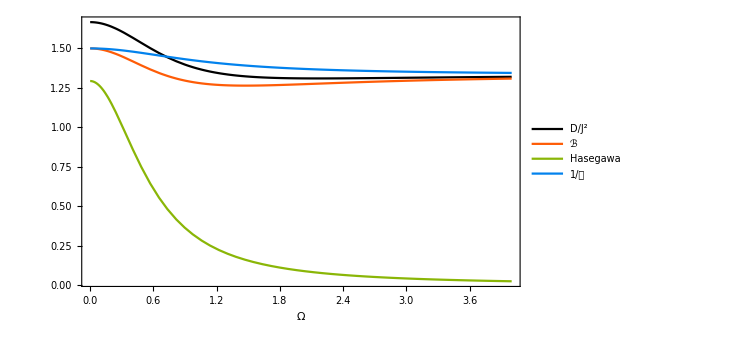

```mathematica
Plot[Evaluate[Re@{𝒟/J^2,bound,hasegawaoriginal,1/M0}/.{Δ->0.3,γm->1,γp->0.5,μ1->1,μ2->1}],{Ω,0,4},
ImageSize->550,
PlotStyle->COLORLIST,
FrameLabel->{"Ω",None},
PlotLegends->legend[{"D/J^2","ℬ","Hasegawa","1/𝒦"},{0.77,0.5}]
]
```

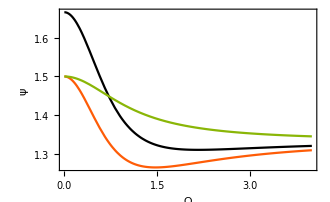

```mathematica
Plot[Evaluate[Re@{𝒟/J^2,(1+ψ)^2/M0,1/M0}/.{Δ->0.3,γm->1,γp->0.5,μ1->1,μ2->1}],{Ω,0,4},
PlotStyle->COLORLIST,
FrameLabel->{"Ω","ψ"},
FrameLabel->{"Ω",None}
]
```

```mathematica
(*Manipulate[Plot[Evaluate[Re@{𝒟,J^2 bound,J^2 hasegawaoriginal,J^2/M0}/.{Δ->ΔΔ,γm->γγm,γp->γγp,μ1->μμ1,μ2->μμ2}],{Ω,0,4},
ImageSize->600,
(*PlotRange->{0,2},*)
PlotStyle->COLORLIST,
FrameLabel->{"Ω",None},
PlotLegends->legend[{"D","J^2ℬ","J^2Hasegawa","J^2/𝒦"},{0.77,0.7}]
],
{{ΔΔ,0.3,"Δ"},-4,4},
{{γγm,1,"γ_-"},0,4},
{{γγp,0.5,"γ_+"},0,4},
{{μμ1,1,"μ_1"},-2,2},
{{μμ2,1,"μ_2"},-2,2}]*)
```

```mathematica
Manipulate[Plot[Evaluate[Re@{ψ}/.{Δ->ΔΔ,γm->γγm,γp->γγp,μ1->μμ1,μ2->μμ2}],{Ω,0,4},
ImageSize->600,
(*PlotRange->{0,2},*)
PlotStyle->COLORLIST,
FrameLabel->{"Ω",None}
],
{{ΔΔ,0.3,"Δ"},-4,4},
{{γγm,1,"γ_-"},0,4},
{{γγp,0.5,"γ_+"},0,4},
{{μμ1,1,"μ_1"},-2,2},
{{μμ2,1,"μ_2"},-2,2}]
```

```mathematica
ψ//Simplify
```

-((2 (γm-γp) (γm+γp)^2 (γm μ1-γp μ2) Ω^2)/(γm γp ((γm+γp)^2+4 Δ^2)^2 (μ1+μ2)+((γm+γp)^2+4 Δ^2) (γm (γm+3 γp) μ1+γp (3 γm+γp) μ2) Ω^2+2 (γm+γp) (γm μ1+γp μ2) Ω^4))

```mathematica
ψ/.{μ1->1,μ2->1}//cf
ψ/.{μ1->1,μ2->-1}//cf
```

-((2 (γm-γp)^2 (γm+γp)^2 Ω^2)/(2 γm γp ((γm+γp)^2+4 Δ^2)^2+(γm^2+6 γm γp+γp^2) ((γm+γp)^2+4 Δ^2) Ω^2+2 (γm+γp)^2 Ω^4))

-(2 (γm+γp)^2)/((γm+γp)^2+2 (2 Δ^2+Ω^2))

```mathematica
Length@Select[Table[ψ/.Thread[{γm,γp}->RandomReal[{0,10},2]]/.Thread[{Ω,μ1,μ2,Δ}->RandomReal[{-3,3},4]],{10^4}],#>=0&]
```

3487

```mathematica
Length@Select[Table[Re[ratio-has11]/.Thread[{γm,γp}->RandomReal[{0,10},2]]/.Thread[{Ω,μ1,μ2,Δ}->RandomReal[{-3,3},4]],{10^4}],#<0&]
```

0

```mathematica
Length@Select[Table[Re[ratio-boundUnitary]/.Thread[{γm,γp}->RandomReal[{0,10},2]]/.Thread[{Ω,μ1,μ2,Δ}->RandomReal[{-3,3},4]],{10^4}],#<0&]
```

1597

```mathematica
Length@Select[Table[Re[ratio-hasegawaoriginal]/.Thread[{γm,γp}->RandomReal[{0,10},2]]/.Thread[{Ω,μ1,μ2,Δ}->RandomReal[{-3,3},4]],{10^4}],#<0&]
```

0

```mathematica
J/.Ω->0//cf
```

(γm γp (μ1+μ2))/(γm+γp)

```mathematica
𝒟/.Ω->0//cf
```

(γm γp (γm^2+γp^2) (μ1+μ2)^2)/(γm+γp)^3

```mathematica
ratio/.Ω->0//cf
```

1/γm+1/γp-2/(γm+γp)

```mathematica
has/.Ω->0//cf
```

(γm+γp)/(2 γm γp)

```mathematica
has2/.Ω->0//cf
```

{(4 (γp μ1+γm μ2)^2)/(γm γp (γm+γp) (μ1+μ2)^2 (μ1^2+μ2^2))}

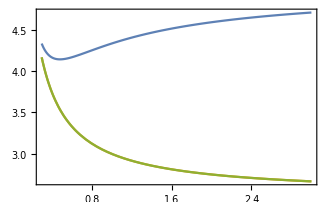

```mathematica
Plot[Evaluate[{ratio,has,has2/J^2}/.{Ω->0.0,Δ->0.1,γm->0.2,μ1->0.9,μ2->0.9}],{γp,0.3,3}(*,PlotRange->{0,4}*)]
```

## Quantum trajectories & stochastic processes

### Gillespie algorithm for classical stochastic processes

```mathematica
Gillespie[W_,x0_,njumps_]:=Module[{χ,r1,𝒲,x,λ,τ,tab},
χ = Range[1,Length@W];
r1 = RandomReal[{0,1},njumps];
𝒲 = W - DiagonalMatrix@Diagonal@W; (* Make sure the matrix has zero diagonals *)

x = x0;
τ = 0;
tab=Table[
λ = Total[𝒲⟦All,x⟧];
τ =τ -1/λ Log[1-r1⟦n⟧];
x = RandomChoice[Drop[𝒲⟦All,x⟧,{x}]/λ->Drop[χ,{x}]];

{τ,x},{n,njumps}];

Prepend[tab,{0,x0}]
];

GillespieMoment[result_,n_]:=(Differences[result⟦All,1⟧].(result⟦1;;-2,2⟧)^n)/result⟦-1,1⟧
```

#### Example: quantum harmonic oscillator

```mathematica
Clear[W];
Nb = 1.5;
γ = 1.0;
nmax = 50;
(*W = Table[KroneckerDelta[m,n+1] γ(Nb+1)(n+1)+KroneckerDelta[m,n-1] γ Nb n,{n,0,nmax},{m,0,nmax}]//mf;*)
W = DiagonalMatrix[Table[γ (Nb+1)(n+1),{n,0,nmax-1}],1] + DiagonalMatrix[Table[γ Nb n,{n,1,nmax}],-1];
result = {#⟦1⟧,#⟦2⟧-1}&/@Gillespie[W,10,550];
```

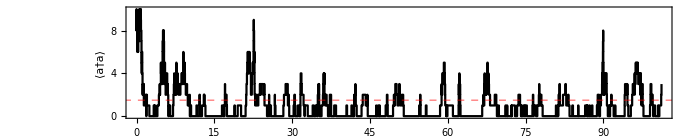

```mathematica
ListLinePlot[result,InterpolationOrder->0,
AspectRatio->1/5,
ImageSize->700,
PlotStyle->Black,
GridLines->{None,{Nb}},
GridLinesStyle->Directive[Red,Dashed,Thick],
FrameLabel->{"time","⟨a†a⟩"}
]
```

```mathematica
GillespieMoment[{#⟦1⟧,#⟦2⟧-1}&/@Gillespie[W,10,10^5],1]
```

1.49466

### Pauli master equation

Input: 
- p_up: vector (or scalar) of upward transition rates
- p_dw: vector (or scalar) of downward transition rates.

Syntax: 
- If p_(up(dw)) are vectors: PauliEquation[p_up,p_dw]
- If p_(up(dw)) are scalars: PauliEquation[d,p_up,p_dw] , where d is the dimension

```mathematica
Clear[PauliEquation];
PauliEquation[pup_?VectorQ,pdw_?VectorQ]:=Module[{W,d=Length@pup+1},
W = DiagonalMatrix[pup,-1] + DiagonalMatrix[pdw,1] - DiagonalMatrix[Append[pup,0]]-DiagonalMatrix[Prepend[pdw,0]]
]

PauliEquation[d_,pup_,pdw_]:=PauliEquation[ConstantArray[pup,{d-1}],ConstantArray[pdw,{d-1}]]
```

#### Example usage

```mathematica
(* Non-uniform rates *)
W=PauliEquation[Table[p[i],{i,5}],Table[q[i],{i,5}]]//mf;
```

(-p[1] | q[1] | 0 | 0 | 0 | 0
p[1] | -p[2]-q[1] | q[2] | 0 | 0 | 0
0 | p[2] | -p[3]-q[2] | q[3] | 0 | 0
0 | 0 | p[3] | -p[4]-q[3] | q[4] | 0
0 | 0 | 0 | p[4] | -p[5]-q[4] | q[5]
0 | 0 | 0 | 0 | p[5] | -q[5])

```mathematica
Table[Total[W⟦All,i⟧],{i,6}]
```

{0,0,0,0,0,0}

```mathematica
(* Uniform rates *)
W = PauliEquation[6,Subscript[p, up],Subscript[p, dw]]//mf;
```

(-p_up | p_dw | 0 | 0 | 0 | 0
p_up | -p_dw-p_up | p_dw | 0 | 0 | 0
0 | p_up | -p_dw-p_up | p_dw | 0 | 0
0 | 0 | p_up | -p_dw-p_up | p_dw | 0
0 | 0 | 0 | p_up | -p_dw-p_up | p_dw
0 | 0 | 0 | 0 | p_up | -p_dw)

```mathematica
Table[Total[W⟦All,i⟧],{i,6}]
```

{0,0,0,0,0,0}

### Quantum Jump unravelling with pure states

```mathematica
Clear[QuantumJumpUnravelling];
QuantumJumpUnravelling[H_,cops_,ψ0_,ts_,seed_:0]:=Module[{r,Δt,npts,ncops = Length@cops,He,ψ,𝒰,states,jump,jumpList,dyna,n,ss},
If[seed!=0,SeedRandom[seed]];
Δt = ts⟦2⟧-ts⟦1⟧;
npts=Length[ts]-1;
r = RandomReal[{0,1},npts];
He = H - ⅈ/2 Sum[c†.c,{c,cops}];
ψ = N@ψ0;
𝒰 = Eye[Length@He]-ⅈ He Δt-(He.He Δt^2)/2+1/6 ⅈ He.He.He Δt^3+(He.He.He.He Δt^4)/24; 
jumpList = {};
states = {};
n=1;
While[n<npts,
ss=NestWhileList[𝒰.#&,ψ,Norm[#]^2>r⟦n⟧&,1,npts-n+1];
AppendTo[states,ss];
ψ = ss⟦-1⟧;
n = n + Length@ss;
jump=If[ncops==1,1,RandomChoice[Table[Re[ψ*.c†.c.ψ],{c,cops}]->Range[1,ncops]]];
If[n<=npts,AppendTo[jumpList,{n (*Δt*), jump}]];
ψ = cops⟦jump⟧.ss⟦-1⟧;
ψ = ψ/Norm[ψ];

{states}];
{Flatten[states,1],jumpList}

]
```

#### Example usage

```mathematica
H=1/2(σz + 0.5 σx);
ψ0 = {1,1}/√2;
ts = Range[0,30.0,0.001];
{ψ,jumpList}=QuantumJumpUnravelling[H,{0.5σm,0.5σp},ψ0,ts,3];
jumpList
```

{{2950,1},{9271,2},{15176,1},{16905,2},{22762,1},{27355,2},{28276,1}}

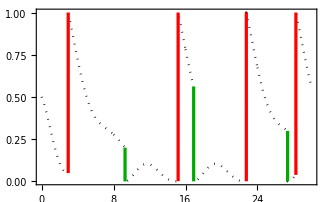

```mathematica
ups = Select[jumpList,#⟦2⟧==1&];
dws = Select[jumpList,#⟦2⟧==2&];
ListLinePlot[{ts,Abs[ψ⟦All,2⟧]^2}ᵀ,PlotRange->All,
PlotStyle->Directive[Black,Dotted],
Epilog->{
Red,Thickness[0.007],
Table[Line[{
{ts⟦ups⟦j,1⟧⟧,Abs[ψ⟦ups⟦j,1⟧-1,2⟧]^2},
{ts⟦ups⟦j,1⟧⟧,1}}],{j,Length@ups}],
Darker@Green,
Table[Line[{
{ts⟦dws⟦j,1⟧⟧,Abs[ψ⟦dws⟦j,1⟧-1,2⟧]^2},
{ts⟦dws⟦j,1⟧⟧,0}}],{j,Length@dws}]
}
]
```

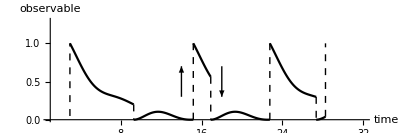

```mathematica
ups = Select[jumpList,#⟦2⟧==1&];
dws = Select[jumpList,#⟦2⟧==2&];
ListLinePlot[Table[{ts⟦jumpList⟦j,1⟧;;jumpList⟦j+1,1⟧-1⟧,Abs[ψ⟦jumpList⟦j,1⟧;;jumpList⟦j+1,1⟧-1,2⟧]^2}ᵀ,{j,Length@jumpList-1}],
PlotStyle->Black,
Epilog->{
Black,Dashed,
Table[Line[{
{ts⟦ups⟦j,1⟧⟧,Abs[ψ⟦ups⟦j,1⟧-1,2⟧]^2},
{ts⟦ups⟦j,1⟧⟧,1}}],{j,Length@ups}],
Table[Line[{
{ts⟦dws⟦j,1⟧⟧,Abs[ψ⟦dws⟦j,1⟧-1,2⟧]^2},
{ts⟦dws⟦j,1⟧⟧,0}}],{j,Length@dws}]
},
AspectRatio->1/3,
ImageSize->400,
AxesLabel->{"time","observable"},
Ticks->None,
Frame->False,
Axes->True,
AxesStyle->Directive[Arrowheads[0.05],Black],
PlotRange->{{1,32},{0,1.3}},
Prolog->{
Arrow[{{14,0.3},{14,0.7}}],
Arrow[{{18,0.7},{18,0.3}}]
}

]
```

#### Ex: Zeno effect in a 3-level system

```mathematica
LoadArbitrarySpinMatrices[1,"a"]
ψ0 = Basis[3,1];
ρ0 = out[ψ0,ψ0];
κ = 15.0;
cops = {√κ Proj[3,3,3]};
ℒ = Liouvillian[Sx,cops];

ts = Range[0,tf=30,0.005];

Clear[res];
Do[
res[i] = Table[{t,Tr[Proj[3,i,i].Unvec@MatrixExp[ℒ t,Vec[ρ0]]]},{t,0,tf,0.1}]//Chop;
,{i,1,3}]
```

```mathematica
rasta@ListLinePlot[{res[1],res[2],res[3]},PlotRange->All]
```

-Graphics-

```mathematica
ψs=QuantumJumpUnravelling[Sx,cops,ψ0,ts]⟦1⟧;
Do[
res2[i] = Table[expect[Proj[3,i,i], ψs⟦n⟧]/Norm[ψs⟦n⟧]^2,{n,1,Length@ψs}]//Chop;
,{i,1,3}]
```

```mathematica
rasta@ListLinePlot[{res2[1],res2[2],res2[3]},PlotRange->{0,1.1},DataRange->{0,tf}]
```

-Graphics-

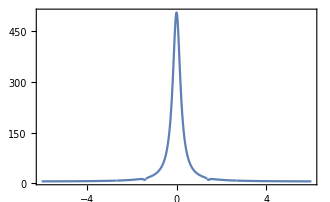

```mathematica
S=FCSPowerSpectrumLinearSys[{ω},Eye[3]/3,ℒ,cops]⟦1,2⟧;
Plot[S,{ω,-6,6}]
```

### ! Quantum Gillespie algorithm for jump unravelling

```mathematica
Clear[QuantumJumpGillespie];
QuantumJumpGillespie[H_,cops_,ψ0_,ts_,njumps_]:=Module[{He,𝒥,Qs,V,ψ,τ,Ps,norm,Vs,tr,δτr,weights,jump,cr,tab},

𝒥 = Sum[c†.c,{c,cops}];
He = H - ⅈ/2 𝒥;

tr = Range[1,Length@ts];
cr = Range[1,Length@cops];
Vs = Table[MatrixExp[-ⅈ He t],{t,ts}];
Qs = Table[ V†.𝒥.V,{V,Vs}];
norm = Norm[Qs⟦-1⟧];

ψ = ψ0;
τ= 0;
tab=Table[
Ps = Table[ψ*.Q.ψ,{Q,Qs}]//Chop;
δτr = SillySample[Ps,tr];
τ = τ + ts⟦δτr⟧;
ψ = Vs⟦δτr⟧.ψ;
weights = Table[ψ*.c†.c.ψ,{c,cops}]//Chop;
jump=RandomChoice[weights->cr];
ψ = cops⟦jump⟧.ψ;
ψ = ψ/Norm[ψ];
{τ,jump(*,ψ*)},{n,njumps}];

(*{tab,norm,He}*)
tab

]
```

```mathematica
(* Assumes it is a renewal process *)
Clear[QuantumJumpGillespieRenewal];
QuantumJumpGillespieRenewal[H_,cops_,ts_,ψ0_,njumps_]:=Module[{He,𝒥,Qs,V,ψ,τ,Ps,norm,Vs,tr,δτr,weights,jump,cr,tab,δτrs},

𝒥 = Sum[c†.c,{c,cops}];
He = H - ⅈ/2 𝒥;

tr = Range[1,Length@ts];
cr = Range[1,Length@cops];
Vs = Table[MatrixExp[-ⅈ He t],{t,ts}];
Qs = Table[ V†.𝒥.V,{V,Vs}];
norm = Norm[Qs⟦-1⟧];

Do[
ψ = cops⟦c⟧.RandomReal[{0,1},Length@ψ0];
ψ = ψ/Norm[ψ];
Ps[c] = Table[ψ*.Q.ψ,{Q,Qs}]//Chop;
δτrs[c] = SillySample[Ps[c],tr,njumps];
,{c,cr}];

τ= 0;
jump = 1;
ψ = cops⟦jump⟧.RandomReal[{0,1},Length@ψ0];
ψ = ψ/Norm[ψ];
tab=Table[
(*δτr = SillySample[Ps[jump],tr];*)
δτr = δτrs[jump]⟦n⟧;
τ = τ + ts⟦δτr⟧;
ψ = Vs⟦δτr⟧.ψ;
weights = Table[ψ*.c†.c.ψ,{c,cops}]//Chop;

jump=RandomChoice[weights->cr];
ψ = cops⟦jump⟧.ψ;
ψ = ψ/Norm[ψ];
{τ,jump},{n,njumps}];

(*{tab,norm,He}*)
tab

]
```

#### Example usage

```mathematica
H=(σz + σx);
cops = {σm};
ψ0 = {1,1}/√2;
ts = linspace[0,50.0,2000];
tab=QuantumJumpGillespie[H,cops,ψ0,ts,10^4];
tab2=QuantumJumpGillespieRenewal[H,cops,ψ0,ts,10^4];
```

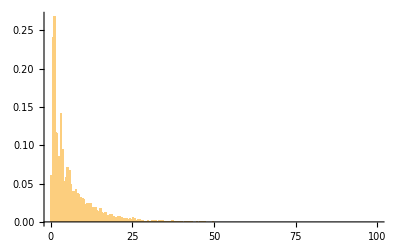

```mathematica
Histogram[Differences[tab⟦All,1⟧],{0,100,0.5},"PDF"]
```

Compare with the numerically exact waiting time distribution.
They only coincide in this case because this is a renewal process. 
In general, the stochastic method here is more general, since it allows for memory in the renewal.

```mathematica
ℒ = Liouvillian[H,cops];
ℒ1 = Sum[JumpOp[c],{c,cops}];
𝒲 = WaitingTimeDistribution[out[ψ0,ψ0],ℒ,ℒ1,#]&/@ts//Chop;
```

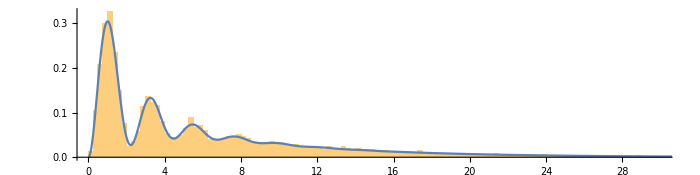

```mathematica
Show[
Histogram[Differences[tab⟦All,1⟧],{0,30,0.25},"PDF"],
ListLinePlot[𝒲,PlotRange->{{0,30},All},DataRange->{0,Last@ts}],
ImageSize->700,
AspectRatio->1/4]
```

### Homodyne/Diffusion unravelling

Based on Eqs. (4) and (7) of https://arxiv.org/pdf/1410.5345.pdf

```mathematica
Clear[HomodyneSimulatePureState];
HomodyneSimulatePureState[ψ0_,H_,c_,dt_,tf_]:=Module[{nsteps,S,ψ,dW,M,xave,dY,tab,𝕀,M0,x,c2},
nsteps = Round[tf/dt];
S= Association[];

S["dt"]=dt;
S["tf"]=tf;
S["nsteps"]=nsteps;
𝕀 = NEye[Length@H];
M0 = 𝕀 - (ⅈ H + 1/2 c†.c)dt;
dW = RandomVariate[NormalDistribution[0,√dt],nsteps];
ψ = ψ0;
x = c + c†;
c2 = c.c;
tab=Table[
xave = ψ*.(c+c†).ψ;
dY = xave dt + dW⟦n⟧; 
M = M0 + dY c + 1/2 c2 (dY^2-dt);
ψ = M.ψ//Normalize;
{ψ,dY,xave},{n,nsteps}];

S["ψ"]=tab⟦All,1⟧//Chop;
S["J"]=tab⟦All,2⟧/dt//Chop;
S["xave"]=tab⟦All,3⟧//Chop;
S
]
```

```mathematica
Clear[HomodyneSimulateMixedState];
HomodyneSimulateMixedState[ρ0_,H_,c_,dt_,tf_]:=Module[{nsteps,S,ρ,dW,M,xave,dY,tab,𝕀,M0},
nsteps = Round[tf/dt];
S= Association[];

S["dt"]=dt;
S["tf"]=tf;
S["nsteps"]=nsteps;
𝕀 = NEye[Length@ρ0];
M0 = 𝕀 - (ⅈ H + 1/2 c†.c)dt;
dW = RandomVariate[NormalDistribution[0,√dt],nsteps];
ρ = ρ0;
tab=Table[
xave = Tr[(c+c†).ρ];
dY = xave dt + dW⟦n⟧; 
M = M0 + dY c + 1/2 c.c (dY^2-dt);
ρ = M.ρ.M†;
ρ = ρ/Tr[ρ];
{ρ,dY,xave},{n,nsteps}];

S["ρ"]=tab⟦All,1⟧//Chop;
S["J"]=tab⟦All,2⟧/dt//Chop;
S["xave"]=tab⟦All,3⟧//Chop;
S
]
```

#### Example: homodyne for dephasing

dρ/dt=-i [Ωσ_x,ρ] + γ D[σ_z]

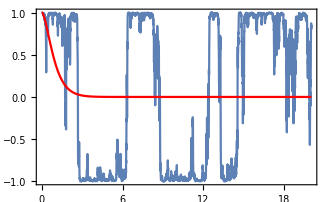

```mathematica
(* γ >> Ω: zeno-like dynamics *)
SeedRandom[1];
Ω = 1.0;
γ = 2.0;
H = Ω σx;
c = √γ σz;
ℒ = Liouvillian[H,{c}];
dt = 0.005;
tf = 20;
szExact=Tr[σz.Unvec@MatrixExp[ℒ t,Vec@out[ψ0,ψ0]]]//Chop//Simplify;
sim = HomodyneSimulatePureState[ψ0={1,0},H,c,dt,tf];

Show[
ListLinePlot[sim["xave"]/(2 √γ),PlotRange->All,DataRange->{dt,tf}],
Plot[Re@szExact,{t,0,20},PlotStyle->Red]]
```

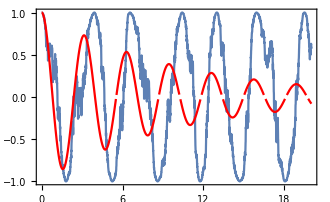

```mathematica
(* γ << Ω *)
SeedRandom[1];
Ω = 1.0;
γ = 0.1;
H = Ω σx;
c = √γ σz;
ℒ = Liouvillian[H,{c}];
dt = 0.005;
tf = 20;
szExact=Tr[σz.Unvec@MatrixExp[ℒ t,Vec@out[ψ0,ψ0]]]//Chop//Simplify;
sim = HomodyneSimulatePureState[ψ0={1,0},H,c,dt,tf];

Show[
ListLinePlot[sim["xave"]/(2 √γ),PlotRange->All,DataRange->{dt,tf}],
Plot[szExact,{t,0,20},PlotStyle->Red]]
```

#### Example: homodyne for spontaneous emission

```mathematica
γ =0.2;
Δ = 1.;
H =Δ/2 σz+ σx;
c = √γ σm;
ℒ = Liouvillian[H,{c}];
ψ0 = 1/(√2){1,1(*ⅈ*)};
dt = 0.01;
tf = 20.0;

sim =Table[HomodyneSimulatePureState[ψ0,H,c,dt,tf]["xave"],{200}];
xave=√γ Tr[σx.Unvec[MatrixExp[ℒ t,Vec[out[ψ0,ψ0]]]]]//cf//Chop;
```

```mathematica
rasta@Show[
Plot[xave,{t,0,tf},PlotStyle->Black],
ListLinePlot[Mean@sim,DataRange->{0,tf},PlotRange->All],
PlotRange->All
]
```

-Graphics-

#### Comparison with QuTIP

Comparing with the example given here: https://qutip.org/docs/latest/guide/dynamics/dynamics-stochastic.html

In the QuTIP example, if one uses a large dt (e.g. dt = 0.003), the simulations diverge. 
Instead, since algorithm implemented here always produces a valid POVM, if dt is not small enough here one will observe a phase lag in the dynamics. 

HomodyneSimulatePureState takes a similar amount of time as QuTIP.

```mathematica
LoadBosonicOperators[nmax = 20];
Δ = 5 2π;
κ = 2;
H = Δ a†.a;
c = √κ a;
intensity = 4.;
ψ0 = CoherentState[√intensity];

dt = 0.0012;
tf = 1.0;

ℒ = Liouvillian[H,{c}];
ρ0 = out[ψ0,ψ0];

(* Analytical (unconditional) Subscript[⟨x⟩, t] *)
ρ = Vec@ρ0;
ℰ = MatrixExp[ℒ dt];
ana = Table[
ρ=ℰ.ρ;
{t,1/(√κ)Tr[(c+c†).Unvec@ρ]},{t,dt,tf,dt}]//Chop;
(*sim=HomodyneSimulate[ρ0,H,c,dt,tf]["xave"];*)
PrettyTiming[
J=Mean@Table[MovingAverage[HomodyneSimulatePureState[ψ0,H,c,dt,tf]["J"],2],{800}]
];
```

0h : 0m : 12s

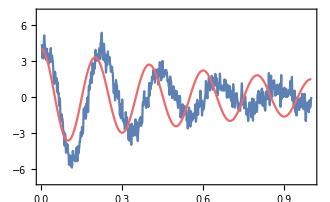

```mathematica
Show[
(*ListLinePlot[sim,Filling->Axis,DataRange->{dt,tf}],*)
ListLinePlot[J/√κ,DataRange->{dt,tf}],
ListLinePlot[ana,PlotStyle->red],
PlotRange->{-7,7}
]
```

# Corresponding QuTIP code

import numpy as np
import matplotlib.pyplot as plt
import qutip as qt

# parameters
DIM = 20             # Hilbert space dimension
DELTA = 5*2*np.pi    # cavity detuning
KAPPA = 2            # cavity decay rate
INTENSITY = 4        # intensity of initial state
NUMBER_OF_TRAJECTORIES = 500

# operators
a = qt.destroy(DIM)
x = a + a.dag()
H = DELTA*a.dag()* a

rho_0 = qt.coherent(DIM, np.sqrt(INTENSITY))
times = np.arange(0, 1, 0.0025)

stoc_solution = qt.smesolve(H, rho_0, times,
                            c_ops=[],
                            sc_ops=[np.sqrt(KAPPA) * a],
                            e_ops=[x],
                            ntraj=NUMBER_OF_TRAJECTORIES,
                            nsubsteps=2,
                            store_measurement=True,
                            dW_factors=[1],
                            method='homodyne')

fig, ax = plt.subplots()
ax.set_title('Stochastic Master Equation - Homodyne Detection')
ax.plot(times, np.array(stoc_solution.measurement).mean(axis=0)[:].real,
        'r', lw=2, label=r'$J_x$')
ax.plot(times, stoc_solution.expect[0], 'k', lw=2,
        label=r'$\langle x \rangle$')
ax.set_xlabel('Time')
ax.legend()

#### Reproducing Fig. 4.6 of Wiseman and Milburn

I think there is a typo in that figure. I think (a) is for Φ = π/2 and (b) is for Φ = 0, not the other way around.

```mathematica
γ =1;
Δ = 0;
Ω = 3 γ;
H =Δ/2 σz+ Ω/2 σy;
c = √γ σm;
ℒ = Liouvillian[H,{c}];
ψ0 = 1/(√2){1,1};
ρ0 = out[ψ0,ψ0];
dt = 0.01;
tf = 10.0;

simX =HomodyneSimulateMixedState[ρ0,H,c ,dt,tf];
simY =HomodyneSimulateMixedState[ρ0,H,c ⅇ^(ⅈ π/2),dt,tf];

xave=√γ Tr[σx.Unvec[MatrixExp[ℒ t,Vec[ρ0]]]]//cf//Chop;
yave=√γ Tr[σy.Unvec[MatrixExp[ℒ t,Vec[ρ0]]]]//cf//Chop;
Plot[{xave,yave},{t,0,tf}]
```

```mathematica
PhiTheta[sim_]:=Module[{
sx=Chop@Table[Tr[σx.ρ],{ρ,sim["ρ"]}],
sy=Chop@Table[Tr[σy.ρ],{ρ,sim["ρ"]}],
sz=Chop@Table[Tr[σz.ρ],{ρ,sim["ρ"]}]
},
{Table[ArcTan[sx⟦i⟧,sy⟦i⟧],{i,Length@sx}],ArcCos[#]&/@sz}
]
```

```mathematica
BlochSpherePlot[sim_]:=Module[{
sx=Chop@Table[Tr[σx.ρ],{ρ,sim["ρ"]}],
sy=Chop@Table[Tr[σy.ρ],{ρ,sim["ρ"]}],
sz=Chop@Table[Tr[σz.ρ],{ρ,sim["ρ"]}]
},
Show[BlochSphere[],
ListLinePlot3D[{sx,sy,sz}ᵀ,PlotStyle->Black,PlotRange->All,AspectRatio->1],PlotRange->All,AspectRatio->1,ImageSize->270]
]
```

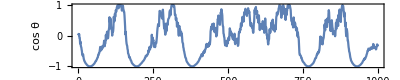

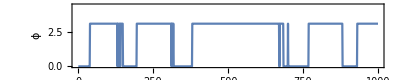

-Graphics3D-

```mathematica
{ϕx,θx}=PhiTheta[simX];
ListLinePlot[Cos@θx,AspectRatio->1/5,ImageSize->{Automatic,180},FrameLabel->{"γt","cos θ"},ImagePadding->{{60,10},{50,10}}]
ListLinePlot[ϕx,PlotRange->{0,4.5},AspectRatio->1/5,ImageSize->{Automatic,180},FrameLabel->{"γt","ϕ"},ImagePadding->{{60,10},{50,10}}]
BlochSpherePlot[simX]
```

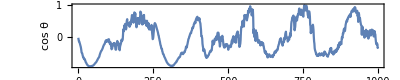

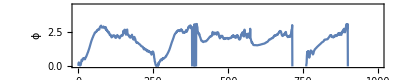

-Graphics3D-

```mathematica
{ϕy,θy}=PhiTheta[simY];
ListLinePlot[Cos@θy,AspectRatio->1/5,ImageSize->{Automatic,180},FrameLabel->{"γt","cos θ"},ImagePadding->{{60,10},{50,10}}]
ListLinePlot[ϕy,PlotRange->{0,4.5},AspectRatio->1/5,ImageSize->{Automatic,180},FrameLabel->{"γt","ϕ"},ImagePadding->{{60,10},{50,10}}]
BlochSpherePlot[simY]
```

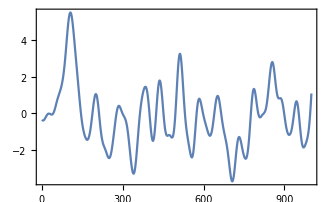
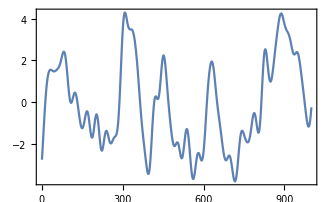

```mathematica
{ListLinePlot[LowpassFilter[simX,0.1]],ListLinePlot[LowpassFilter[simY,0.1]]}
```

```mathematica
timeseries = TimeSeries[{range[dt,tf,dt],sim}ᵀ]
```

TimeSeries[…]

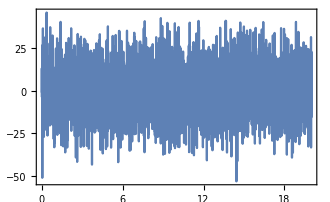

```mathematica
ListLinePlot[timeseries]
```

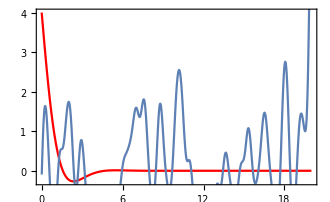

```mathematica
Show[Plot[4xave/√γ,{t,0,tf},PlotStyle->Red],
ListLinePlot[LowpassFilter[timeseries,5]]]
```

#### Two-point function & power spectrum from the stochastic homodyne current

```mathematica
Clear[ω,γ,Ω];
γ =0.7;
Δ = 0;
Ω = 5 γ;
H =Δ/2 σz+ Ω/2 σy;
c = √γ σm;
ℒ = Liouvillian[H,{c}];
ℒ = Liouvillian[H,{c}]//cf;
(*ρ = AnalyticalSteadyState[ℒ];*)
ψ0 = {1,0};
{𝒮=FCSPowerSpectrumLinearSys[{ω},ρ,ℒ,c,1,"Homodyne"]⟦1,2⟧//cf,
ℱ = FCSTwoPointFunctionMEXP[{τ},ρ,ℒ,c,1,"Homodyne"]⟦1,2⟧//cf};

dt = 0.01;
tf = 4000.0;

sim =HomodyneSimulatePureState[ψ0,H,c ,dt,tf]["J"];
```

```mathematica
{Plot[𝒮,{ω,-12,12}],Plot[ℱ,{τ,0,12}]}
```

{-Graphics-,-Graphics-}

```mathematica
PrettyTiming[F=TwoPointCorrelation[sim,Round[8/dt],dt,3];]
```

0h : 0m : 3s

```mathematica
(* Butterworth filter smooths the 2-point function *)
PrettyTiming[Ffilt=TwoPointCorrelation[butter[sim,50,dt],Round[8/dt],dt,4];]
```

0h : 0m : 5s

```mathematica
rasta@Show[
ListLinePlot[{F,Ffilt},PlotStyle->{Directive[Black,Opacity[0.25]],Black}],
Plot[ℱ,{τ,0,9},PlotStyle->red]
]
```

-Graphics-

```mathematica
Grid@PartitionIn[Table[rasta@Show[
ListLinePlot[PowerSpectrum[sim,dt,av],PlotRange->{{-10,10},All}],
Plot[𝒮,{ω,-10,10},PlotStyle->{Red,Thick}],
PlotLabel->"Averaging = " <>ToString@av
],{av,{1,5,10,20,40,80}}],2]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(* Power spectrum using Butterworth filter is no good, because it suppresses the shotnoise frequency *)
rasta@Show[
ListLinePlot[{PowerSpectrum[sim,dt,20],PowerSpectrum[butter[sim,10,dt],dt,10]},PlotRange->{{-10,10},All}],
Plot[𝒮,{ω,-10,10},PlotStyle->{Red,Thick}]
]
```

-Graphics-

```mathematica
(* More detailed simulations with 10x more points *)
```

```mathematica
sim2 =HomodyneSimulate[ρ,H,c ,dt,10tf]["J"];
```

```mathematica
Show[
ListLinePlot[PowerSpectrum[sim2,dt,500],PlotRange->{{-10,10},{0.9,2.5}}],
Plot[𝒮,{ω,-10,10},PlotStyle->{Red,Thick},PlotRange->{{-10,10},{0.9,2.5}}]
]
```

-Graphics-

### Markov order 1 Gaussian stationary process

```mathematica
Clear[Markov1Gaussian];
Markov1Gaussian[L_,μ_,σ_,ρ_]:=Module[{Σ,Q,Z},
Σ =σ^2 SparseArray[{
{i_,i_}->1,
{i_,j_}/;i!=j->ρ^Abs[i-j]},{L,L}];

(*Σ=γ0 Eye[L] + γ1 toeplitzMatrix[1,2,L];*)
Q = CholeskyDecomposition[Σ]ᵀ;
Z = RandomVariate[NormalDistribution[],L];
Q.Z + μ
]
```

```mathematica
Markov1Gaussian[5,1.,0.2,0.1]
```

{0.919965,1.08107,0.842528,1.06101,1.06177}

## Gaussian (Fermionic & Bosonic)

## Conditional Gaussian dynamics

### Waiting time distribution (PRB)

Based on https://arxiv.org/pdf/2108.11850.pdf

```mathematica
Clear[FermionicChainWaitingTimeDistributionVacuum];
FermionicChainWaitingTimeDistributionVacuum[W_,F_,trange_,{i_,diri_},j_]:=Module[{L = Length@W,𝒞,EM,EmM,Q,Γ,EX,EZ,P,γ},

Q = W - F;
Γ = Tr[F];
γ = If[diri =="-",2 Re@W⟦i,i⟧-F⟦i,i⟧,F⟦i,i⟧];

If[diri=="-",
Table[
EX = MatrixExp[-Q t];
EZ = EX†;
{t,γ ⅇ^(-Γ t) EX ⟦i,j⟧ EZ⟦j,i⟧},{t,trange}],

Table[
EX = MatrixExp[-Q t];
EZ = EX†;
{t,γ ⅇ^(-Γ t) ((EZ.EX)⟦j,j⟧ - EX ⟦i,j⟧ EZ⟦j,i⟧)},{t,trange}]]//Chop

]

Clear[FermionicChainWaitingTimeDistribution];
FermionicChainWaitingTimeDistribution[WW_,FF_,ttrange_,{i_,diri_},{j_,dirj_},CC_:"ss",pres_:MachinePrecision]:=Module[{L = Length@WW,W,F,𝒞,EM,EmM,Q,X,Γ,c,𝕀,𝒯,𝔻,γ,deno,trange,𝒵,EX,EmX,EZ,EmZ},

trange = SetPrecision[Rationalize@ttrange,pres];
W =SparseArray@SetPrecision[Rationalize@Normal@WW,pres];
F =SparseArray@SetPrecision[Rationalize@Normal@FF,pres];
𝕀 = Eye[L];

If[CC=="vac",Return[FermionicChainWaitingTimeDistributionVacuum[W,F,trange,{i,diri},j]]];

𝒞=If[CC==="ss",Chop@LyapunovSolve[W,F],CC];
EM = Inverse[𝒞]-𝕀;
EmM = Inverse[EM];

Q = W - F;
𝒵 = Det[𝕀 + EmM];
Γ = Tr[F];

γ = If[diri =="-",2 Re@W⟦i,i⟧-F⟦i,i⟧,F⟦i,i⟧];
c = If[dirj=="-",𝒞⟦j,j⟧,1-𝒞⟦j,j⟧];

Table[
X = -Q t;
(*Z = - Q† t; (* X† *)*)
EX = MatrixExp[X];
EmX = MatrixExp[-X];
EZ = EX† (* ℰ[Z]*);
EmZ=EmX†;

𝒯 = Inverse[EmZ.EM.EmX+𝕀];
𝔻 = Det[𝕀 + EX.EmM.EZ];


{t,γ/c Exp[-Γ t]/𝒵  𝔻 Which[
(* Subscript[c, i]^†Subscript[c, i] and Subscript[c, j]^†Subscript[ρc, j] *)diri=="-" && dirj=="+",  
((EM.EmX.𝒯.EX)⟦j,j⟧ 𝒯⟦i,i⟧ + (𝒯.EmZ.EM)⟦i,j⟧ (EM.EmX.𝒯)⟦j,i⟧),
(* Subscript[c, i] Subscript[c, i]^† and Subscript[c, j]^†Subscript[ρc, j] *)diri=="+" && dirj=="+", 
((EM.EmX.𝒯.EX)⟦j,j⟧ (𝕀⟦i,i⟧-𝒯⟦i,i⟧) - (𝒯.EmZ.EM)⟦i,j⟧ (EM.EmX.𝒯)⟦j,i⟧),
(* Subscript[c, i]^†Subscript[c, i] and Subscript[c, j] Subscript[ρc, j]^† *)diri=="-" && dirj=="-", 
(𝒯⟦i,i⟧ (EmM⟦j,j⟧-(EmX.𝒯.EX.EmM)⟦j,j⟧) - (𝒯.EmZ)⟦i,j⟧ (EmX.𝒯)⟦j,i⟧),
(* Subscript[c, i] Subscript[c, i]^† and Subscript[c, j] Subscript[ρc, j]^† *)diri=="+" && dirj=="-", 
((𝕀⟦i,i⟧-𝒯⟦i,i⟧) (EmM⟦j,j⟧-(EmX.𝒯.EX.EmM)⟦j,j⟧) + (𝒯.EmZ)⟦i,j⟧ (EmX.𝒯)⟦j,i⟧)
]},
{t,trange}]//Chop

]

FermionicChainWaitingTimeDistribution[V_,L_,γ_,{f1_,fL_},ttrange_,{i_,diri_},{j_,dirj_},CC_:"ss",pres_:MachinePrecision]:=Module[{W,F},
{W,F} = BDMatrices[V,L,γ,{f1,fL}];
FermionicChainWaitingTimeDistribution[W,F,ttrange,{i,diri},{j,dirj},CC,pres]]
```

#### Example usage

```mathematica
ts = linspace[0,80,200];
ϵ = 1.0;
L = 5;
γ = 0.1;
fs = {1,0};

PL=FermionicChainWaitingTimeDistribution[ϵ,L,γ,fs,ts,{L,"-"},{1,"+"}];
P1=FermionicChainWaitingTimeDistribution[ϵ,L,γ,fs,ts,{1,"+"},{1,"+"}];
```

```mathematica
ListLinePlot[{PL},PlotRange->All]
ListLinePlot[{P1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ProbChannel[wdist_]:=Module[{Δt = First@Differences@wdist⟦All,1⟧},Trapz[wdist⟦All,2⟧,Δt]]
ProbChannel[PL]+ProbChannel[P1]
```

0.999673

```mathematica
Basis[10,1]//mf;
```

(1
0
0
0
0
0
0
0
0
0)

```mathematica
MatrixForm/@Chop@BDMatricesBasic[TightBindingHamiltonianPBC[1,10],0.1 Basis[10,1],Basis[10,1]]
```

{(0.05+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ
0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ
0.-1. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ),(0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
FermionicChainWaitingTimeDistribution
```

```mathematica
L = 50;
{W,F} = BDMatricesBasic[TightBindingHamiltonianPBC[1,L],0.1 Basis[L,1],0 Basis[L,1]];
P = FermionicChainWaitingTimeDistributionVacuum[W,F,ts,{1,"-"},1];
ListLinePlot[P]
```

-Graphics-

#### SSH model

```mathematica
(* Takes around 1 minute to run *)
ts = linspace[0,70,200];
Ls = {5,8,10,20,30};
Clear[P]
P = Association[];

Do[
h = SSHHamiltonian[L,1.0,-0.5];
{W,F} = BDMatrices[h,0.1,{1,0}];
P[L]=FermionicChainWaitingTimeDistribution[W,F,ts,{L,"-"},{1,"+"},"ss",30];
,{L,Ls}]
```

```mathematica
ListLinePlot[{P[5],P[8]},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{P[8],P[10]},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{P[20],P[30]},PlotRange->All]
```

-Graphics-

```mathematica
ts = linspace[0,70,200];
Ls = {5,8,10,20,30};
Clear[Pv]
Pv = Association[];

Do[
h = SSHHamiltonian[L,1.0,-0.5];
{W,F} = BDMatrices[h,0.1,{1,0}];
Pv[L]=FermionicChainWaitingTimeDistribution[W,F,ts,{L,"-"},{1,"+"},"vac",30];
,{L,Ls}]
```

```mathematica
ListLinePlot[{Pv[5],Pv[8]},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{Pv[8],Pv[10]},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{Pv[20],Pv[30]},PlotRange->All]
```

-Graphics-

#### Aubry-André-Haper model

```mathematica
ts = linspace[0,150,300];
Ls = {(*5,8,10,20,*)30};
Clear[Pv]
Pv = Association[];
λs = {0,1.0,1.9,2.0,2.2};

Do[
h = TightBindingHamiltonian[λ AubryAndreHarper[L],L];
{W,F} = BDMatrices[h,0.1,{1,0}];
Pv[{L,λ}]=FermionicChainWaitingTimeDistribution[W,F,ts,{L,"-"},{1,"+"},"vac",30];
,{L,Ls},{λ,λs}]
```

```mathematica
Row@Evaluate@Table[ListLinePlot[{Pv[{30,λ}]},ImageSize->200,PlotRange->All,BaseStyle->{12},
ImagePadding->{{80,10},{20,10}},AspectRatio->1,
FrameTicks->{{Automatic,Automatic},{None,None}},
FrameLabel->{"time","prob 1 → L"},
(*PlotLegends->legend[{"λ = " <> ToString@λ},{0.75,0.65}],*)
Epilog->Text["λ = " <> ToString@λ,Scaled[{0.65,0.85}]],
PlotStyle->red
],{λ,λs}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

### No-jump conditional dynamics

Computes the no-jump distribution P_no = tr( e^(ℒ_0 t)ρ_0) for a fermionic chain (no pairing terms), assuming all channels are monitored.
Notation similar to https://arxiv.org/pdf/2108.11850.pdf

```mathematica
Clear[FermionicChainNoJump];
FermionicChainNoJump[WW_,FF_,ttrange_,CC_:"ss",pres_:MachinePrecision]:=Module[{L = Length@WW,trange,W,F,𝕀,𝒞,EM,EmM,Q,𝒵,Γ,EX},
trange = SetPrecision[Rationalize@ttrange,pres];
W =SparseArray@SetPrecision[Rationalize@Normal@WW,pres];
F =SparseArray@SetPrecision[Rationalize@Normal@FF,pres];
𝕀 = Eye[L];

𝒞=If[CC==="ss",Chop@LyapunovSolve[W,F],CC];
EM = Inverse[𝒞]-𝕀;
EmM = Inverse[EM];

Q = W - F;
𝒵 = Det[𝕀 + EmM];
Γ = Tr[F];

Table[
EX = MatrixExp[-Q t];
{t,ⅇ^(-Γ t)/𝒵 Det[𝕀 + EX.EmM.EX†]},{t,trange}]//Chop
]

FermionicChainNoJump[V_,L_,γ_,{f1_,fL_},ttrange_,CC_,pres_:MachinePrecision]:=Module[{W,F},
{W,F} = BDMatrices[V,L,γ,{f1,fL}];
FermionicChainNoJump[W,F,ttrange,CC,pres]]
```

#### Example usage

```mathematica
ts = linspace[0,50,100];
L = 10;
h = TightBindingHamiltonian[1,L];
{W,F} = BDMatrices[h,0.1,{1,0}];
P1=FermionicChainNoJump[W,F,ts,"ss"];
ListLogPlot[P1,PlotRange->All,Joined->True]
```

-Graphics-

```mathematica
ts = linspace[0,50,100];
L = 10;
h = SSHHamiltonian[L,1.0,-0.5];;
{W,F} = BDMatrices[h,0.1,{1,0}];
P2=FermionicChainNoJump[W,F,ts,"ss"];
ListLogPlot[{P1,P2},PlotRange->All,Joined->True]
```

-Graphics-

```mathematica
ts = linspace[0,50,100];
L = 10;
h = TightBindingHamiltonian[1,L];
{W,F} = BDMatrices[h,ConstantArray[0.1,L],ConstantArray[0.5,L]];
P1=FermionicChainNoJump[W,F,ts,"ss"];

(* SSH model *)
ts = linspace[0,50,100];
L = 10;
h = SSHHamiltonian[L,1.0,-0.5];
{W,F} = BDMatrices[h,ConstantArray[0.1,L],ConstantArray[0.5,L]];
P2=FermionicChainNoJump[W,F,ts,"ss"];
ListLogPlot[{P1,P2},PlotRange->All,Joined->True]
```

-Graphics-

### Riccati solver

Solves
a†x + x a - x b r^-1b† x + q = 0

Similar to Mathematica’s RiccatiSolve[], but you only have to pass the matrix br^-1 b†, instead of b and r individually.

```mathematica
Clear[RiccatiEigen];
RiccatiEigen[a_,q_,brb_]:=Module[{Z,U,d,U11,U21},

Z =ArrayFlatten[({{a, -brb}, {-q, -a†}})];
(*U = Eigvecs[Z,Length[Z]/2];*)
U=Transpose[(Reverse@Eigenvectors[Z + 10^5 Eye@Length@Z,-Length[Z]/2])];
d=Length[Z]/2;
U11 = U⟦1;;d,1;;d⟧;
U21 = U⟦d+1;;2d,1;;d⟧;
U21.Inverse[U11]
]
```

#### Example usage

```mathematica
{a,b,q,r}={({{-3, 2}, {1, 1}}),({{0}, {1}}),({{1., -1.}, {-1., 1.}}),({{3}})};
x=RiccatiSolve[{a,b},{q,r}]//mf;
```

(0.589517 | 1.82157
1.82157 | 8.81884)

```mathematica
RiccatiEigen[a,q,b.Inverse[r].b†]//mf;
```

(0.589517 | 1.82157
1.82157 | 8.81884)

```mathematica
RiccatiSolve[{a=({{-1, 0, 0}, {0, -4, 0}, {0, 0, -6}}),b=({{3}, {1}, {-1}})},{q=({{4, 2, 0}, {2, 4, 0}, {0, 0, 1}}),{{1.}}}]//mf;
RiccatiEigen[a,q,b.b†]//mf;
```

(0.532526 | 0.126812 | 0.0112197
0.126812 | 0.420536 | 0.0036552
0.0112197 | 0.0036552 | 0.0831582)

(0.532526 | 0.126812 | 0.0112197
0.126812 | 0.420536 | 0.0036552
0.0112197 | 0.0036552 | 0.0831582)

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

### Conditional Lyapunov dynamics for fermions

```mathematica
Clear[ConditionalFermionicDynamics];
ConditionalFermionicDynamics[H_,γ_,f_,{ηm_,ηp_},tf_,CC_:"ss",solver_:"NDSolve",dt_:0.01]:=Module[{L,W,Υ,𝒲,ℱ,γp,γm,ℂ,𝒞,𝒞0,𝒜m,𝒜p,Θ0,Θ,𝕀,Φ},

L=Length[ηm];
{W,γp} = BDMatrices[Eye[L],γ,f];
γm = W+W†-γp;
𝒜m = Normal@DiagonalMatrix[ηm];
𝒜p = Normal@DiagonalMatrix[ηp];

If[L==Length@H,
W = ⅈ H + W;
(𝒞0=Normal@If[CC==="ss",Chop@LyapunovSolve[W,γp],CC];
If[solver ==="NDSolve",
NDSolveValue[{
𝒞'[t]==-(W.𝒞[t] + 𝒞[t].W†) + γp+ 𝒞[t].γm.𝒜m.𝒞[t]-γp.𝒜p+ γp.𝒜p.𝒞[t]+ 𝒞[t].γp.𝒜p-𝒞[t].γp.𝒜p.𝒞[t] ,
𝒞[0]==𝒞0},𝒞,{t,0,tf}],
Interpolation@RK4[-(W.# + #.W†) + γp+ #.γm.𝒜m.#-γp.𝒜p+ γp.𝒜p.#+ #.γp.𝒜p-#.γp.𝒜p.#&,𝒞0,dt,tf]
]),
(
Υ = 1/4 ArrayFlatten[({{γp+γm, ⅈ(γp-γm)}, {-ⅈ (γp-γm), γp+γm}})];
𝒲 = ⅈ H + Υ+Υᵀ;
ℱ = - 2(Υ-Υᵀ);

Θ0 = Normal@If[CC==="ss",Chop@LyapunovSolve[𝒲,ℱ],CC];
 Φ=1/4 ArrayFlatten[({{γp.𝒜p+γm.𝒜m, ⅈ(γp.𝒜p-γm.𝒜m)}, {-ⅈ (γp.𝒜p-γm.𝒜m), γp.𝒜p+γm.𝒜m}})];
𝒲 = 𝒲 -( Φ+Φᵀ);
ℱ = ℱ + Φ - Φᵀ;
If[solver ==="NDSolve",
NDSolveValue[{
Θ'[t]==-(𝒲.Θ[t] + Θ[t].𝒲†) + ℱ+Θ[t].(Φ-Φᵀ).Θ[t],
Θ[0]==Θ0},Θ,{t,0,tf}],
Interpolation@RK4[-(𝒲.# + #.𝒲†) + ℱ+#.(Φ-Φᵀ).#&,Θ0,dt,tf]
]
)]
];
```

```mathematica
Clear[ConditionalFermionicNoJumpDistribution];
ConditionalFermionicNoJumpDistribution[H_,γ_,f_,{ηm_,ηp_},tf_,Δt_,𝒞_]:=Module[{λ,γp,γm,𝒜m,𝒜p,𝕀,Z0,ζ,Zt,Pno,L,W},
L=Length[ηm];
{W,γp} = BDMatrices[Eye[L],γ,f];
γm = W+W†-γp;
𝕀 = Eye[L];
𝒜m = Normal@DiagonalMatrix[ηm];
𝒜p = Normal@DiagonalMatrix[ηp];

λ=If[L==Length@H,
Table[Tr[γp.𝒜p.(𝕀-𝒞[t]) + γm.𝒜m.𝒞[t]],{t,0,tf,Δt}],Table[Tr[γp.𝒜p.(𝕀-FermionsReducedC@𝒞[t]) + γm.𝒜m.FermionsReducedC@𝒞[t]],{t,0,tf,Δt}]
];
(*{Range[Δt,tf,Δt],Table[Exp[-Trapz[λ⟦1;;j⟧,Δt]],{j,2,Length@λ}]}ᵀ//Chop*)
{Range[Δt,tf,Δt],Table[-Trapz[λ⟦1;;j⟧,Δt],{j,2,Length@λ}]}ᵀ//Chop
]
```

```mathematica
Clear[ConditionalFermionicSteadyState];
ConditionalFermionicSteadyState[H_,γ_,f_,{ηm_,ηp_},pres_:MachinePrecision]:=Module[{a,γp,γm,W,𝒜p,𝒜m,L,Υ,𝒲,ℱ,Φ},
L=Length[ηm];
{W,γp} = BDMatrices[Eye[L],γ,f];
γm = W+W†-γp;
𝒜m = Normal@DiagonalMatrix[ηm];
𝒜p = Normal@DiagonalMatrix[ηp];

If[L==Length@H,
W = ⅈ H + W;
(*RiccatiEigen[- W†+γp.𝒜p, γp-γp.𝒜p, -(γm.𝒜m-γp.𝒜p)]*)
RiccatiSolve[{- W†+γp.𝒜p,Chop@Sqrt[-(γm.𝒜m-γp.𝒜p)]},{ γp-γp.𝒜p,-NEye[L]} ]
,
Υ = 1/4 ArrayFlatten[({{γp+γm, ⅈ(γp-γm)}, {-ⅈ (γp-γm), γp+γm}})];
𝒲 = SetPrecision[ⅈ H + Υ+Υᵀ,pres];
ℱ = SetPrecision[- 2(Υ-Υᵀ),pres];
 Φ=SetPrecision[1/4 ArrayFlatten[({{γp.𝒜p+γm.𝒜m, ⅈ(γp.𝒜p-γm.𝒜m)}, {-ⅈ (γp.𝒜p-γm.𝒜m), γp.𝒜p+γm.𝒜m}})],pres];
(*RiccatiEigen[-𝒲†+(Φ+Φᵀ),ℱ+Φ-Φᵀ,-(Φ-Φᵀ)]*)
RiccatiSolve[{-𝒲†+(Φ+Φᵀ),Chop@Sqrt[-(Φ-Φᵀ)]},{ℱ+Φ-Φᵀ,kron[σx,NEye[L]]}]
]
]
```

#### Verification by comparing with full calculation

```mathematica
(* 2 sites *)
```

```mathematica
CM[ρ_]:=Chop@Table[Tr[cd[j].c[i].ρ],{i,2},{j,2}];
```

```mathematica
(* Full calculation using definitions *)
LoadFermionicOperators[2];
V = 1.;
H = cd[1].c[1] + cd[2].c[2] + V (cd[1].c[2]+cd[2].c[1]);
γ = 0.5;
f1 = 0.2;
f2 = 0.45;
ℒ = Liouvillian[H,{c[1],cd[1],c[2],cd[2]},{γ(1-f1),γ f1,γ(1-f2),γ f2}];
ρ = SteadyState[ℒ];
ηm = {0.8,0.65};
ηp = {0.4,0.9};
ℒ1 = γ(1-f1) ηm⟦1⟧ JumpOp[c[1]] + γ f1 ηp⟦1⟧ JumpOp[cd[1]]+ γ(1-f2) ηm⟦2⟧ JumpOp[c[2]] + γ f2 ηp⟦2⟧ JumpOp[cd[2]];
ℒ0 = ℒ-ℒ1;
ts = range[0,tf=20,0.1];
ρnos = Table[
tmp=Unvec@MatrixExp[ℒ0 t,Vec[ρ]];
tmp/Tr[tmp]
,{t,ts}];

Pno = Table[{t,Tr@Unvec@MatrixExp[ℒ0 t,Vec[ρ]]},{t,ts}];
𝒞 = Table[CM[ρ],{ρ,ρnos}]//Chop;
```

```mathematica
(* Result using our function implementations *)
{W,F} = BDMatrices[1,2,γ,{f1,f2}];
(*𝒞2=ConditionalLyapunov[W,F,ηm,ηp,tf];*)
𝒞2=ConditionalFermionicDynamics[TightBindingHamiltonian[2],γ,{f1,f2},{ηm,ηp},tf]
Pno2 = ConditionalFermionicNoJumpDistribution[TightBindingHamiltonian[2],γ,{f1,f2},{ηm,ηp},tf,0.1,𝒞2];
```

InterpolatingFunction[…]

```mathematica
Show[
ListLinePlot[{ts,𝒞⟦All,1,1⟧}ᵀ,PlotStyle->Red],
Plot[𝒞2[t]⟦1,1⟧,{t,0,tf},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
ListLinePlot[{Pno,Pno2},PlotStyle->{Red,Directive[Blue,Dashed]}]
```

-Graphics-

```mathematica
tmp=cd[1].cd[2].c[2].c[1](*+cd[2].c[1]+cd[1].c[2]*)//mf;
```

(1. | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* Non-Gaussian state *)
(* Full calculation using definitions *)
LoadFermionicOperators[2];
V = 1.;
H = cd[1].c[1] + cd[2].c[2] + V (cd[1].c[2]+cd[2].c[1]);
γ = 0.5;
f1 = 0.2;
f2 = 0.45;
ℒ = Liouvillian[H,{c[1],cd[1],c[2],cd[2]},{γ(1-f1),γ f1,γ(1-f2),γ f2}];
(*ρ = c[1].SteadyState[ℒ].cd[1];
ρ = ρ/Tr[ρ];
*)
ρ =SteadyState[ℒ];
ρ = MatrixExp[ⅈ tmp].ρ.MatrixExp[-ⅈ tmp];
ρ = ρ/Tr[ρ];
(*S = RandomReal[{0,10},{4,4}];
ρ = (S†.S)/Tr[S†.S];
*)
ηm = {0.8,0.65};
ηp = {0.4,0.9};
ℒ1 = γ(1-f1) ηm⟦1⟧ JumpOp[c[1]] + γ f1 ηp⟦1⟧ JumpOp[cd[1]]+ γ(1-f2) ηm⟦2⟧ JumpOp[c[2]] + γ f2 ηp⟦2⟧ JumpOp[cd[2]];
ℒ0 = ℒ-ℒ1;
ts = range[0,tf=20,0.1];
ρnos = Table[
tmp=Unvec@MatrixExp[ℒ0 t,Vec[ρ]];
tmp/Tr[tmp]
,{t,ts}];

Pno = Table[{t,Tr@Unvec@MatrixExp[ℒ0 t,Vec[ρ]]},{t,ts}];
𝒞 = Table[CM[ρ],{ρ,ρnos}]//Chop;
```

```mathematica
(* Result using our function implementations *)
{W,F} = BDMatrices[1,2,γ,{f1,f2}];
𝒞2=ConditionalLyapunov[W,F,ηm,ηp,tf,CM[ρ]];
Pno2 = GaussianNoJumpDistribution[W,F,ηm,ηp,tf,0.1,𝒞2];
```

```mathematica
Show[
ListLinePlot[{ts,𝒞⟦All,1,1⟧}ᵀ,PlotStyle->Red],
Plot[𝒞2[t]⟦1,1⟧,{t,0,tf},PlotStyle->Dashed]]
Show[
ListLinePlot[{ts,𝒞⟦All,2,2⟧}ᵀ,PlotStyle->Red],
Plot[𝒞2[t]⟦2,2⟧,{t,0,tf},PlotStyle->Dashed]]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[{Pno,Pno2},PlotStyle->{Red,Directive[Blue,Dashed]},PlotRange->All]
```

-Graphics-

#### Example usage

```mathematica
h = TightBindingHamiltonian[2.,3]/2//mf;
ηm = {1,0.5,1};
ηp = {0,0,1};
tf = 100;
𝒞=ConditionalFermionicDynamics[h,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp},tf];
𝒞ss = ConditionalFermionicSteadyState[h,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp}]
Plot[Diagonal[𝒞[t]],{t,0,tf},GridLines->{None,Re@Diagonal@𝒞ss}]
```

(1. | -0.5 | 0
-0.5 | 1. | -0.5
0 | -0.5 | 1.)

{{0.428571-1.34215×10^-10 ⅈ,-2.25297×10^-10+3.07404×10^-10 ⅈ,-1.16809×10^-10-2.97776×10^-10 ⅈ},{-3.42326×10^-10+3.06587×10^-10 ⅈ,0.428571-4.24262×10^-10 ⅈ,-1.8685×10^-10+2.8493×10^-10 ⅈ},{-1.60157×10^-12-2.12611×10^-10 ⅈ,-2.83131×10^-10+2.88983×10^-10 ⅈ,0.428571-1.63167×10^-10 ⅈ}}

-Graphics-

```mathematica
𝒞[tf]//mf;
```

(0.421593 | 0.-0.00116915 ⅈ | -0.00322485
0.+0.00116915 ⅈ | 0.418344 | 0.-0.00116436 ⅈ
-0.00322485 | 0.+0.00116436 ⅈ | 0.421629)

```mathematica
Pno = ConditionalFermionicNoJumpDistribution[h,γ,{f1,fL},{ηm,ηp},tf,0.1,𝒞];
ListLinePlot[Pno,PlotRange->All]
```

-Graphics-

#### Comparing no-pairing vs. pairing implementations

```mathematica
h = TightBindingHamiltonian[2.,3]/2;
ηm = {1,0.5,1};
ηp = {0,0,1};
tf = 100;
𝒞=ConditionalFermionicDynamics[h,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp},tf,"ss"];

𝒯 =MajoranaXY[L=3,-1.0,0.0];
tf = 100;
Θ=ConditionalFermionicDynamics[𝒯,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp},tf,"ss"];
```

```mathematica
𝒞[3.0]//mf;
```

(0.454207 | 0.-0.00382083 ⅈ | -0.000402965
0.+0.00382083 ⅈ | 0.403255 | 0.-0.0133959 ⅈ
-0.000402965 | 0.+0.0133959 ⅈ | 0.34222)

```mathematica
FermionsReducedC@Θ[3.]//mf;
```

(0.454207 | 0.-0.00382084 ⅈ | -0.000402964
0.+0.00382084 ⅈ | 0.403255 | 0.-0.0133959 ⅈ
-0.000402964 | 0.+0.0133959 ⅈ | 0.34222)

```mathematica
Plot[Diagonal[FermionsReducedC@Θ[t]],{t,0,tf}]
```

-Graphics-

```mathematica
Pno1 = ConditionalFermionicNoJumpDistribution[h,γ,{f1,fL},{ηm,ηp},tf,0.1,𝒞];
```

```mathematica
Pno2 = ConditionalFermionicNoJumpDistribution[𝒯,γ,{f1,fL},{ηm,ηp},tf,0.1,Θ];
```

```mathematica
ListLinePlot[{Pno1,Pno2},PlotRange->All,PlotStyle->{Black,Directive[Red,Dashed]}]
```

-Graphics-

```mathematica
ConditionalFermionicSteadyState[h,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp}]//mf;
ConditionalFermionicSteadyState[𝒯,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp}]//mf;
FermionsReducedC@ConditionalFermionicSteadyState[𝒯,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp}]//mf;
```

(0.428571 | 0 | 0
0 | 0.428571 | 0
0 | 0 | 0.428571)

(0 | 0 | 0 | 0.+0.142857 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0.+0.142857 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0.+0.142857 ⅈ
0.-0.142857 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.-0.142857 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0.-0.142857 ⅈ | 0 | 0 | 0)

(0.428571 | 0 | 0
0 | 0.428571 | 0
0 | 0 | 0.428571)

#### Example with pairing terms (XY model)

```mathematica
𝒯 =MajoranaXY[L=10,h0=0.0,κ=0.0];
ηm = ConstantArray[1,L];
ηp = ConstantArray[1,L];
tf = 290;
Θ1=ConditionalFermionicDynamics[𝒯,γ=0.8,{f1=0.3,fL=0.5},{ηm,ηp},tf];
Θ1ss=ConditionalFermionicSteadyState[𝒯,γ=0.1,{f1=0.3,fL=0.5},{ηm,ηp}];
(*Plot[Re@Diagonal[FermionsReducedC@Θ1[t]],{t,0,tf},PlotRange->All]*)
tab1 = Table[Re@Diagonal[FermionsReducedC@Θ1[t]],{t,0,tf,0.1}];
ListLinePlot[tab1ᵀ,GridLines->{None,Re@Diagonal@FermionsReducedC@Θ1ss}]
Pno1 = ConditionalFermionicNoJumpDistribution[𝒯,γ,{f1,fL},{ηm,ηp},tf,0.05,Θ1];
```

LyapunovSolve::meig: Matrix with multiple eigenvalues encountered. The solution may be inaccurate or may not exist.

-Graphics-

```mathematica
𝒯 =MajoranaXY[L,0.0,0.9];
Θ2=ConditionalFermionicDynamics[𝒯,γ,{f1,fL},{ηm,ηp},tf,"ss"];
(*Plot[Re@Diagonal[FermionsReducedC@Θ2[t]],{t,0,tf},PlotRange->All]*)
tab2 = Table[Re@Diagonal[FermionsReducedC@Θ2[t]],{t,0,tf,0.1}];
ListLinePlot[tab2ᵀ]
Pno2 = ConditionalFermionicNoJumpDistribution[𝒯,γ,{f1,fL},{ηm,ηp},tf,0.05,Θ2];
```

-Graphics-

```mathematica
Θ2ss=ConditionalFermionicSteadyState[𝒯,γ=0.1,{f1=0.3,fL=0.5},{ηm,ηp},40];
Re@Diagonal@FermionsReducedC@Θ2ss
```

{0.4999999999999999999999999999999999488859793083843179414,0.499999999999999999999999999999999995995105060526995491316,0.4999999999999999999999999999999999457265136904772029373,0.5000000000000000000000000000000020019910952293359109361,0.5000000000000000000000000000000002376562241078765741583,0.4999999999999999999999999999998779729561753353984265358,0.49999999999999999999999999999999965291712198339356653,0.500000000000000000000000000003571508005704941883566122,0.500000000000000000000000000000000168536478642833844751,0.499999999999999999999999999946816171228891622115276751}

```mathematica
ListLinePlot[{{#⟦1⟧,#⟦2⟧/#⟦1⟧}&/@Pno1,{#⟦1⟧,#⟦2⟧/#⟦1⟧}&/@Pno2},PlotRange->All]
```

-Graphics-

```mathematica
𝒯 =MajoranaXY[L=10,h0=1.0,κ=0.9];
Θss=ConditionalFermionicSteadyState[𝒯,γ=0.1,{f1=0.3,fL=0.5},{ηm,ηp},40];
Re@Diagonal@FermionsReducedC@Θss
```

{0.065866954327628025079000818823490575996,0.12067565359189610017177902362405091036,0.13690939901444379468875944607897590372,0.14334975234366523334519827731099312533,0.14582466737279241729626128689959573901,0.1458252720512592367398102104972349209,0.14335176822793453217542509926702186714,0.13691357960295492226717758681246744849,0.12068375709617973558108373020468024364,0.065875799807448084691816519355422062772}

#### Comparison with the full monitoring expression from the PRB

```mathematica
h = TightBindingHamiltonian[3];
ηm = {1,1,1};
ηp = {1,1,1};
tf = 150;
𝒞=ConditionalFermionicDynamics[h,γ=0.1,{f1=0.3,fL=0.5},{ηm,ηp},tf];
Pno1 = GaussianNoJumpDistribution[h,γ,{f1,fL},{ηm,ηp},tf,0.1,𝒞];
{W,F}=BDMatrices[h,γ,{f1,fL}];
Pno2 = FermionicChainNoJump[W,F,Range[0,tf,0.02]];
```

```mathematica
ListLinePlot[{Pno1,{#⟦1⟧,#⟦2⟧ 0.95}&/@Pno2},PlotRange->All]
```

-Graphics-

#### Dark states for a particle in a ring

```mathematica
L = 10;
h = TightBindingHamiltonianPBC[1,L];

(prob=Table[
{W,F} = BDMatrices[h,Basis[L,1],0];
𝒞 = ConditionalLyapunov[W,F,ηm=Basis[L,1],ηp=Basis[L,1],tf=100,𝒞0 = Proj[L,p,p]];
{p,1-GaussianNoJumpDistribution[W,F,ηm,ηp,tf,0.1,𝒞]⟦-1,2⟧},{p,2,L}])//TableForm
```

2 | 0.499964
3 | 0.499964
4 | 0.499959
5 | 0.499959
6 | 0.999957
7 | 0.499959
8 | 0.499959
9 | 0.499964
10 | 0.499964

```mathematica
ListLinePlot[prob]
```

-Graphics-

## Gaussian bosonic systems

### Syntax for the covariance matrix

All quantities are written for the operator ordering R = (q_1,p_1,q_2,p_2).
The covariance matrix is defined as 

σ = (⟨q_1^2⟩ | 1/2⟨{q_1,p_1}⟩ | ⟨q_1 q_2⟩ | ⟨q_1 p_2⟩
1/2⟨{q_1,p_1}⟩ | ⟨p_1^2⟩ | ⟨p_1 q_2⟩ | ⟨p_1 p_2⟩
⟨q_1 q_2⟩ | ⟨p_1 q_2⟩ | ⟨q_2^2⟩ | 1/2⟨{q_2,p_2}⟩
⟨q_1 p_2⟩ | ⟨p_1 p_2⟩ | 1/2⟨{q_2,p_2}⟩ | ⟨p_2^2⟩)

The vacuum is 1/2. 
If your vacuum is 1, then call the functions with σ/2 instead; that is,

function(σ/2)

and so on.

### Gaussian partial trace

Input is the list you wish to trace out

```mathematica
Clear[GPTr];
GPTr[σ_,list_]:=Module[{blist,clist,L = Length[σ]/2},

blist = Riffle[2list-1,2list];
clist = Complement[Range[1,2L],blist];
If[2Length@list==Length@σ,σ,σ⟦clist,clist⟧]
]
```

#### Example usage

```mathematica
(* CM for a 2-mode squeezed state of 1 and 2, plus an independent mode 3, with additional noise in mode 1 *)
Θ = ({{1/2+n+nth, 0, √(n (1+n)), 0, 0, 0}, {0, 1/2+n+nth, 0, -√(n (1+n)), 0, 0}, {√(n (1+n)), 0, 1/2+n, 0, 0, 0}, {0, -√(n (1+n)), 0, 1/2+n, 0, 0}, {0, 0, 0, 0, 1/2+n3, 0}, {0, 0, 0, 0, 0, 1/2+n3}});
```

```mathematica
(* Trace over mode 2 *)
GPTr[Θ,{2}]//mf;
```

(1/2+n+nth | 0 | 0 | 0
0 | 1/2+n+nth | 0 | 0
0 | 0 | 1/2+n3 | 0
0 | 0 | 0 | 1/2+n3)

```mathematica
(* Trace over mode 1 *)
GPTr[Θ,{1}]//mf;
```

(1/2+n | 0 | 0 | 0
0 | 1/2+n | 0 | 0
0 | 0 | 1/2+n3 | 0
0 | 0 | 0 | 1/2+n3)

```mathematica
(* Trace over modes 1 and 2 *)
GPTr[Θ,{1,2}]//mf;
```

(1/2+n3 | 0
0 | 1/2+n3)

### Symplectic stuff, Bona fide, purity

BonaFide has to be ≥ 0 for a real state

```mathematica
Clear[SymplecticForm];
SymplecticForm[𝒩_]:=kron[Eye[𝒩],{{0,1},{-1,0}}];
```

```mathematica
Clear[SymplecticEigenvalues];
SymplecticEigenvalues[σ_]:=Module[{𝒩 = Length[σ]/2,Ω},
Ω = SymplecticForm[𝒩];
Chop@Drop[Sort@Quiet@Eigenvalues[N[ⅈ Ω.σ]],𝒩]
]
```

```mathematica
(* Valid CM should have BonaFide ≥ 0 *)
Clear[BonaFide];
BonaFide[σ_]:=Module[{Ω,𝒩 = Length[σ]/2},
Ω = SymplecticForm[𝒩];
First@Sort@Eigenvalues[N[σ+ⅈ Ω/2]]//Chop
]
```

```mathematica
(* Transforms from (a,a†) to quadratures *)
Clear[ModeQuadratureRotation];
ModeQuadratureRotation[𝒩_]:=kron[Eye[𝒩],1/(√2)({{1, 1}, {-ⅈ, ⅈ}})];
```

```mathematica
Clear[GaussianPurity]
GaussianPurity[σ_]:=1/(√Det[2σ]);
```

#### Example usage

```mathematica
σ = 1/2({{ⅇ^(2r), 0}, {0, ⅇ^(-2r)}});
```

```mathematica
SymplecticEigenvalues[σ]
```

{0.5}

```mathematica
GaussianPurity[σ]
```

1

```mathematica
(* Symplectic form for 2 modes*)
Ω = SymplecticForm[2]//mf;
```

(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
(* CM for a 2-mode squeezed state with additional noise in one of the modes only *)
Θ = ({{1/2+n+nth, 0, √(n (1+n)), 0}, {0, 1/2+n+nth, 0, -√(n (1+n))}, {√(n (1+n)), 0, 1/2+n, 0}, {0, -√(n (1+n)), 0, 1/2+n}});
```

```mathematica
GaussianPurity[Θ]//Simplify
%/.nth->0
```

1/(√Det[2 Θ])

1/(√Det[2 Θ])

```mathematica
(* For pure states (nth = 0) the symplectic eigenvalues are 1/2, same as the vacuum *)
SymplecticEigenvalues[Θ/.{n->0.8,nth->0}]
```

{0.5,0.5}

```mathematica
SymplecticEigenvalues[Θ/.{n->0.8,nth->0.3}]
```

{0.663941,0.963941}

```mathematica
Θ/.{n->0.8,nth->0}
```

{{1.3,0,1.2,0},{0,1.3,0,-1.2},{1.2,0,1.3,0},{0,-1.2,0,1.3}}

```mathematica
(* Bona-fide is zero for pure states (nth = 0) *)
BonaFide[Θ/.{n->0.8,nth->0}]
```

0

```mathematica
(* It is positive for mixed states *)
BonaFide[Θ/.{n->0.8,nth->0.9}]
```

0.219477

```mathematica
(* Transforms the CM written in terms of quadratures into the CM written in terms of (a,a†) *)
L = ModeQuadratureRotation[2]//mf;
```

(ⅈ/(√2) | -ⅈ/(√2) | 0 | 0
1/(√2) | 1/(√2) | 0 | 0
0 | 0 | ⅈ/(√2) | -ⅈ/(√2)
0 | 0 | 1/(√2) | 1/(√2))

```mathematica
L.Θ.L†//Simplify//mf;
```

(1/2+n+nth | 0 | 0 | ⅈ √(n (1+n))
0 | 1/2+n+nth | -ⅈ √(n (1+n)) | 0
0 | ⅈ √(n (1+n)) | 1/2+n+nth | 0
-ⅈ √(n (1+n)) | 0 | 0 | 1/2+n+nth)

### Williamson’s theorem

Based on PhysRevA_79_052327
Williamson’s diagonalization: 

σ = SWSᵀ where 

-  W = diag(ν_1,ν_1,ν_2,ν_2,...,ν_N,ν_N)  contains the symplectic eigenvalues

-  S is symplectic:  SΩSᵀ = Ω

The function outputs W, S as well as error the error in (Θ - SWSᵀ) and (Ω - SΩSᵀ)

```mathematica
Williamson[σ_]:=Module[{𝒩=Length[σ]/2,Ω,W,V,vals,vecs,list,perm,X,U,γ,Γ,S,P,error1,error2},
(*PhysRevA_79_052327*)
Ω=SymplecticForm[𝒩];
Γ = ModeQuadratureRotation[𝒩];
W =DiagonalMatrix@Abs@Eigenvalues[ⅈ Ω.σ];

V = MatrixPower[σ,-1/2];
X=V.Ω.V;
{vals,vecs}=Chop@Eigensystem[X];

list=ⅈ Reverse[ Abs@vals Table[(-1)^i,{i,0,2𝒩-1}]];
perm=FindPermutation[vals,list];
U=Permute[vecs,perm]ᵀ;
S=Inverse@(√W.(Γ.U†).V);
error1 = Max@Flatten@Abs[S.W.Sᵀ-σ]//Chop;
error2 = Max@Flatten@Abs[S.Ω.Sᵀ-Ω]//Chop;
{W,Chop@S,{error1,error2}}
]
```

#### Example usage

```mathematica
σ = 1/2({{ⅇ^(2r), 0}, {0, ⅇ^(-2r)}})/.r->0.8;
{W,S,errors}=Williamson[σ];
errors
W//Diagonal
S//mf;
```

{0,0}

{0.5,0.5}

(0 | -2.22554
0.449329 | 0)

```mathematica
σ-S.W.Sᵀ//Chop//mf;
```

(0 | 0
0 | 0)

```mathematica
Θ = ({{0.6, 0.1}, {0.1, 0.99}});
(* Check if the CM is valid *)
BonaFide[Θ]
```

0.249083

```mathematica
{W,S,errors}=Williamson[Θ];
errors
W//Diagonal
S//mf;
```

{0,0}

{0.764199,0.764199}

(0.0647785 | -0.883708
1.13634 | -0.0647785)

```mathematica
(* A 3-mode CM *)
Θ = ({{1/2+n+nth, 0, √(n (1+n)), 0, 0, 0}, {0, 1/2+n+nth, 0, -√(n (1+n)), 0, 0}, {√(n (1+n)), 0, 1/2+n, 0, 0, 0}, {0, -√(n (1+n)), 0, 1/2+n, 0, 0}, {0, 0, 0, 0, 1/2+n3, 0}, {0, 0, 0, 0, 0, 1/2+n3}});
```

```mathematica
{W,S,errors}=Williamson[Θ/.{n->0.3,nth->0.9,n3->0.77}];
W//Diagonal
S//mf;
errors
```

{1.53282,1.53282,1.27,1.27,0.63282,0.63282}

(0 | 1.03788 | 0 | 0 | 0 | 0.277842
-1.03788 | 0 | 0 | 0 | 0.277842 | 0
0 | 0.277842 | 0 | 0 | 0 | 1.03788
0.277842 | 0 | 0 | 0 | -1.03788 | 0
0 | 0 | 0 | 1. | 0 | 0
0 | 0 | -1. | 0 | 0 | 0)

{0,0}

### von Neumann and Rényi entropy for Gaussian states

```mathematica
GaussianVonNeumann[σ_]:=Module[{h,g,𝒩=Length[σ]/2,Ω,νs},h[x_]:=If[x==0||x==1,0,x Log[x]];
g[x_]:=h[(x+1)/2]-h[(x-1)/2];
Ω=kron[Eye[𝒩],{{0,1},{-1,0}}];
(*νs=Chop@Drop[Sort@Quiet@Eigenvalues[I 2 Ω.σ],𝒩];*)
νs = 2 SymplecticEigenvalues[σ];
Total@Table[g[ν],{ν,νs}]//Chop
];

GaussianRenyiEntropy[σ_,α_]:=Module[{𝒩=Length[σ]/2,Ω,νs},
Ω=kron[Eye[𝒩],{{0,1},{-1,0}}];
(*νs=Chop@Drop[Sort@Quiet@Eigenvalues[I 2 Ω.σ],𝒩];*)
νs = 2 SymplecticEigenvalues[σ];
If[α==1,GaussianVonNeumann[σ],
1/(α-1)Total@Table[Log[((ν+1)/2)^α-((ν-1)/2)^α],{ν,νs}]]

]
```

#### Example usage

```mathematica
σ = 1/2({{ⅇ^(2 r), 0}, {0, ⅇ^(-2 r)}})/.r->0.5;
```

```mathematica
GaussianVonNeumann[σ]//Simplify
```

0

### Gaussian Mutual Information

```mathematica
GaussianMutualInformation[σ_,Alist_,Blist_]:=GaussianVonNeumann[GPTr[σ,Blist]]+GaussianVonNeumann[GPTr[σ,Alist]]-GaussianVonNeumann[σ]

GaussianMutualInformation[σ_,Alist_,Blist_,α_]:=GaussianRenyiEntropy[GPTr[σ,Blist],α]+GaussianRenyiEntropy[GPTr[σ,Alist],α]-GaussianRenyiEntropy[σ,α]
```

### Quantum Negentropy: Measure of non-Gaussianity using the Kullback-Leibler divergence

Given an arbitrary state ρ, this function computes S(ρ||ρ_G) where ρ_G is a Gaussian state with the same 1st and 2nd moments as ρ. 
Based on M. G. Genoni and M. G. A. Paris, Phys. Rev. A 82, 052341 (2010).

Here it is ony implemented for a single mode.

```mathematica
nGmeasure[ρ_]:=Module[{σ,𝒩,a,X,P},
𝒩= Length@ρ;
a = SparseArray@Table[√n KroneckerDelta[m,n-1],{m,0,𝒩-1},{n,0,𝒩-1}];
X = 1/(√2)(a†+a);
P = I/(√2)(a†-a);

σ = ({{Tr[ρ.X.X]-Tr[ρ.X]^2, 1/2 Tr[ρ.(X.P+P.X)]-Tr[ρ.X] Tr[ρ.P]}, {1/2 Tr[ρ.(X.P+P.X)]-Tr[ρ.X] Tr[ρ.P], Tr[ρ.P.P]-Tr[ρ.P]^2}});
GaussianVonNeumann[σ]-vonNeumann[ρ]
]
```

#### Example Usage

Here is the ground-state of a non-Gaussian Hamiltonian

```mathematica
LoadBosonicOperators[30];
(* λ = 0 is Gaussian *)
λ = 0.0;
H = a†.a + (a+a†).(a+a†)+ λ a†.a†.a.a;
ψ0 = First@Eigenvectors[H,-1];
nGmeasure[out[ψ0,ψ0]]
```

4.44089×10^-16

```mathematica
(* λ ≠ 0 is not *)
λ = 0.1;
H = a†.a + (a+a†).(a+a†)+ λ a†.a†.a.a;
ψ0 = First@Eigenvectors[H,-1];
nGmeasure[out[ψ0,ψ0]]
```

0.0018546

```mathematica
λ = 0.2;
H = a†.a + (a+a†).(a+a†)+ λ a†.a†.a.a;
ψ0 = First@Eigenvectors[H,-1];
nGmeasure[out[ψ0,ψ0]]
```

0.00371816

```mathematica
λ = 0.5;
H = a†.a + (a+a†).(a+a†)+ λ a†.a†.a.a;
ψ0 = First@Eigenvectors[H,-1];
nGmeasure[out[ψ0,ψ0]]
```

0.00631608

### Canonical form for 2-mode matrices

Any 2-mode CM of the form 

σ_AB= (σ_A | ξ
ξᵀ | σ_B)

can be put, via local operations only, in canonical form

σ_AB = (a | 0 | c_+ | 0
0 | a | 0 | c_-
c_+ | 0 | b | 0
0 | c_- | 0 | b)

where, in order for σ_AB to be bona fide, one must have a,b > 1/2 and 

(a^2-1/4)(b^2-1/4)-c_-c_+/2 - a b(c_-^2+c_+^2) + c_-^2 c_+^2 ≥ 0.

One also has the freedom to always choose c_+≥ |c_-| .

The function below returns the canonical form of a generic CM σ_AB, as well as the symplectic matrix which does the job.

```mathematica
(* vacuum is 1/2 *)
TwoModeCanonicalForm[σ_]:=Module[{σA,σB,ξ,DA,VA,ZA,DB,VB,ZB,M,Σ,UA,UB,S,σcanon},
σA = σ⟦1;;2,1;;2⟧;
σB = σ⟦3;;4,3;;4⟧;
ξ = σ⟦1;;2,3;;4⟧;

{DA,VA} = Eigensystem[σA];
VA = VAᵀ;
ZA = DiagonalMatrix[{(DA⟦2⟧/DA⟦1⟧)^(1/4),(DA⟦2⟧/DA⟦1⟧)^(-1/4)}];

{DB,VB} = Eigensystem[σB];
VB = VBᵀ;
ZB = DiagonalMatrix[{(DB⟦2⟧/DB⟦1⟧)^(1/4),(DB⟦2⟧/DB⟦1⟧)^(-1/4)}];

M= ZA.VAᵀ.ξ.VB.ZBᵀ;

(*{UA,ΣA,UB} = SingularValueDecomposition[ZA.VAᵀ.ξ.VB.ZBᵀ];*)
(*UA = UA†; *)
(*UB = UB†;*)

{Σ,UA} = Eigensystem[M.Mᵀ];
{Σ,UB} = Eigensystem[Mᵀ.M];
S = ArrayFlatten[({{UA.ZA.VAᵀ, 0}, {0, UB.ZB.VBᵀ}})];
σcanon = S.σ.Sᵀ;
{σcanon,S}//Chop
]
```

#### Theory behind the function

Local operations mean, at the level of the CM, a local symplectic 

S = (S_A | 0
0 | S_B).

The goal is to choose S_A and S_B such that 

Sσ_AB Sᵀ = σ_AB^canonical 

Due to Euler’s theorem, the symplectic matrices S_A and S_B can always be decomposed as 

S_i = U_i Z_i V_i ᵀ 

where U_i,V_i are orthogonal matrices and Z_i= (z_i | 0
0 | 1/z_i). The goal is then to choose U_A, Z_A, V_A, U_B, Z_B, V_B

Choosing Z_i and V_i:
First and foremost, S_A must be such that 

S_A σ_A S_A ᵀ = (a | 0
0 | a) 

Now consider the standard diagonalization of σ_A:

σ_A= O_A D_A O_A ᵀ,               D_A = (d_A1 | 0
0 | d_A2)

We can solve the problem if we choose V_A = O_A and z_A = (d_A2/d_A1)^(1/4).
For any choice of U_A, this will put σ_A in canonical form 

S_A σ_A S_A ᵀ = (√(d_A1 d_A2) | 0
0 | √(d_A1 d_A2)),                  so a = √(d_A1 d_A2)

Identical results hold for B.

Choosing U_i:
Next we still have the freedom to choose U_A and U_B. Note that 

Sσ_AB Sᵀ = (S_A σ_A S_A^ᵀ | S_A ξ S_B^ᵀ
S_B ξᵀ S_A^ᵀ | S_B σ_B S_B^ᵀ)

We must therefore choose U_A and U_B such that S_A ξ S_B^ᵀ = (c_+ | 0
0 | c_-) is a diagonal matrix. 
But 

S_A ξ S_B^ᵀ  = U_A (Z_A V_A^ᵀ ξ V_B Z_B^ᵀ) U_B^ᵀ

We may thus choose U_A and U_B to be the singular value matrices of  the (non-Hermitian) matrix 

M=(Z_A V_A^ᵀ ξ V_B Z_B^ᵀ).

That is, we decompose 

M = U_A^ᵀ Σ U_B

where Σ is a diagonal matrix containing the non-negative singular values. 
Note that 

MMᵀ = U_A^† Σ^2 U_A

so that U_A^ᵀ is also the eigenvector matrix of MMᵀ. Similarly, 

MᵀM = U_B^ᵀ Σ^2 U_B 

so U_B^ᵀ is the eigenvector matrix of MᵀM.

#### Example usage

```mathematica
(* Construct a random covariance matrix *)
tmp = RandomReal[{0,1},{4,4}];
σ = tmp.tmpᵀ+1.1 Eye[4]//mf;
```

(2.84866 | 1.42055 | 0.896351 | 1.50446
1.42055 | 2.76063 | 0.683591 | 1.47565
0.896351 | 0.683591 | 1.83539 | 0.707997
1.50446 | 1.47565 | 0.707997 | 2.64914)

```mathematica
mf/@({σcanon,S}=TwoModeCanonicalForm[σ]);
```

(2.41788 | 0 | -1.49335 | 0
0 | 2.41788 | 0 | -0.197051
-1.49335 | 0 | 2.08828 | 0
0 | -0.197051 | 0 | 2.08828)

(0.574638 | 0.493319 | 0 | 0
-0.90086 | 0.966851 | 0 | 0
0 | 0 | -0.362478 | -0.743746
0 | 0 | 1.06639 | -0.570735)

```mathematica
(* Local symplectics do not affect any correlations *)
{Det[σ],Det[σcanon]}
```

{14.125,14.125}

```mathematica
(* Transformation is indeed symplectic *)
ω=SymplecticForm[2];
S.ω.Sᵀ-ω//Chop//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Gaussian entanglement of formation for 2 modes

Based on “10.1103/PhysRevA.69.052320”. 
Assumes vacuum is 1/2.

Returns Rényi-2 EoF, 

 1/2 log|2 σ_A|
 
 and the optimal CM γ_p, which minimizes any EoF monotone.

```mathematica
Clear[GaussianEoF];
GaussianEoF[σbare_]:=Module[{σ,θ,na,nb,kq,kp,L,Cp,Cq,X,sol,det1,det2,tab1,tab2,opt1,opt2,x0,x,θmin,detmin,Xmin,γp},
LoadPauliMatrices[];
σ = First@TwoModeCanonicalForm[2σbare]; (* Factor of 2 because the calculations are done with vacuum being 1.*)

na = σ⟦1,1⟧;
nb = σ⟦3,3⟧;
kq = σ⟦1,3⟧;
kp = σ⟦2,4⟧;

L = ({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
Cq = ({{na, kq}, {kq, nb}});
Cp = ({{na, kp}, {kp, nb}});
X = x0 σ0 + x Cos[θ] σz + x Sin[θ] σx;

sol=Quiet@Solve[{Det[Cq-X]==0,Det[X-Inverse[Cp]]==0},{x0,x}];
{det1,det2} = X⟦1,1⟧ Inverse[X]⟦1,1⟧/.sol//Simplify;

tab1 =Select[ Table[{θ,det1},{θ,linspace[10^-5,π-10^-5,1000]}],Im[#⟦2⟧]==0.&];
opt1=First@MinimalBy[tab1,Last];

tab2 =Select[ Table[{θ,det2},{θ,linspace[10^-5,π-10^-5,1000]}],Im[#⟦2⟧]==0&];
(*Print[tab2];*)
opt2=First@MinimalBy[tab2,Last];

(*Print[{opt1,opt2}];*)
If[opt1⟦2⟧ < opt2⟦2⟧,
(
{θmin,detmin} = opt1; 
Xmin = X/.sol⟦1⟧/.θ->θmin
),
(
{θmin,detmin} = opt2; 
Xmin = X/.sol⟦2⟧/.θ->θmin
)
];

γp = Lᵀ.ArrayFlatten[({{Xmin, 0}, {0, Inverse[Xmin]}})].L//Chop;

{1/2 Log[Abs@detmin](*detmin*),γp/2}//Chop
(* 1st term has no 2 inside det because we were working with 2σ*)
(* 2nd term is divided by 1/2 to get back to vacuum being 1/2 *)

]
```

#### Example usage

```mathematica
σ = ({{na, 0, kq, 0}, {0, na, 0, kp}, {kq, 0, nb, 0}, {0, kp, 0, nb}})/.{na->.6,nb->.9,kq->0.35,kp->-0.05}//mf;
GaussianEoF[σ]
```

(0.6 | 0 | 0.35 | 0
0 | 0.6 | 0 | -0.05
0.35 | 0 | 0.9 | 0
0 | -0.05 | 0 | 0.9)

{0.00146522,{{0.42076,0,0.0188349,0},{0,0.595906,0,-0.0389534},{0.0188349,0,0.288136,0},{0,-0.0389534,0,0.870193}}}

```mathematica
σ= ({{1/2+n+nth, 0, √(n (1+n)), 0}, {0, 1/2+n+nth, 0, -√(n (1+n))}, {√(n (1+n)), 0, 1/2+n, 0}, {0, -√(n (1+n)), 0, 1/2+n}})/.{n->1.};
```

```mathematica
GaussianEoF[σ/.nth->0.1]
```

{0.696264,{{1.00541,0,0.870421,0},{0,1.00084,0,-0.868836},{0.870421,0,1.00267,0},{0,-0.868836,0,1.00357}}}

```mathematica
tab=Table[{nnth,First@GaussianEoF[σ/.nth->nnth]},{nnth,0.05,1.5,0.1}]
ListLinePlot[%,PlotMarkers->Automatic]
```

{{0.05,0.869576},{0.15,0.560552},{0.25,0.363968},{0.35,0.232872},{0.45,0.144126},{0.55,0.0843373},{0.65,0.0450031},{0.75,0.0204089},{0.85,0.00657417},{0.95,0.000657462},{1.05,0},{1.15,0},{1.25,0},{1.35,0},{1.45,0}}

-Graphics-

### Squeezed Thermal State

Squeezed thermal states are a bit tricky to implement numerically because e^((z a†a†-z* a a)/2) is not itself a trace-class operator (meaning if we take the matrix exponential, things explode).

The above implementation is both simple and numerically stable.

Input: Hilbert space size nmax, thermal occupation number 𝒩 and squeezing parameters (r,θ) (which appear in z = r e^(i θ))

```mathematica
Clear[SqueezedThermalState];
SqueezedThermalState[nmax_,𝒩_,r_,θ_:0]:=Module[{β,Z,b},
If[nmax>0,LoadBosonicOperators[nmax]];
β =Log[(1+𝒩)/𝒩];
Z=ⅇ^β/(-1+ⅇ^β);
b = a Cosh[r] + a† ⅇ^(ⅈ θ)Sinh[r];
1/Z MatrixExp[-β b†.b]
]

(* Technical note: if input is nmax<0, the function will not load the bosonic operators. *)
(*This is useful when this function is being used within other calculations, which already used LoadBosonicOperators[nmax] *)
```

#### Example usage

```mathematica
ρ = SqueezedThermalState[nmax=200,𝒩=2.0,r=1.0,θ=0.0]
```

SparseArray[…]

```mathematica
Tr[ρ.a†.a]//Chop
𝒩 Cosh[2r] + Sinh[r]^2
```

8.90392

8.90549

One has to use a sufficiently large nmax in order to ensure convergence. 
Here is the same example, with nmax = 100. In this case there is a mismatch

```mathematica
ρ = SqueezedThermalState[nmax=100,𝒩=2.0,r=1.0,θ=0.0];
Tr[ρ.a†.a]//Chop
𝒩 Cosh[2r] + Sinh[r]^2
```

8.71293

8.90549

The value of nmax that has to be used depends sensibly on 𝒩 and r.

### Classical information and discord for 2 modes (experimental)

```mathematica
(* class corr von neumann *)
GaussianClassicalCorrelations[CM_]:=Module[{I1,I2,I3,I4,Δ,dm,h,f,dp,cc=2CM},
I1=Det[cc[[1;;2,1;;2]]];
I2=Det[cc[[3;;4,3;;4]]];
I3=Det[cc[[1;;2,3;;4]]];
I4=Det[cc[[1;;4,1;;4]]];

h[x_]:=If[x==0||x==1,0,x Log[x]];
f[x_]:=h[(x+1)/2]-h[(x-1)/2];


Return[{f[√I1]-f[√If[(-I1 I2+I4)^2<(1+I2) I3^2 (I1+I4),(2 I3^2+(I2-1) (I4-I1)+2 Abs[I3] √(I3^2+(I2-1) (I4-I1)))/(I2-1)^2,(I2 I1-I3^2+I4-√(I3^4+(I4-I2 I1)^2-2 I3^2 (I4+I2 I1)))/(2 I2)]],f[√I2]-f[√If[(-I1 I2+I4)^2<(1+I1) I3^2 (I2+I4),(2 I3^2+(I1-1) (I4-I2)+2 Abs[I3] √(I3^2+(I1-1) (I4-I2)))/(I1-1)^2,(I2 I1-I3^2+I4-√(I3^4+(I4-I2 I1)^2-2 I3^2 (I4+I2 I1)))/(2 I1)]]}]]
```

```mathematica
GaussianQuantumDiscord[CM_] := GaussianMutualInformation[CM,{1},{2}] - GaussianClassicalCorrelations[CM]
```

## Gaussian fermionic systems

### C,S (L×L) ↔ Θ (2L×2L)

```mathematica
FermionicFullCM[𝒞_,S_:0]:=Module[{L = Length[𝒞],vp={1,ⅈ},vm={1,-ⅈ}},
-kron[σy,Eye[L]] + kron[out[vp,vp],𝒞ᵀ]-kron[out[vm,vm],𝒞] +If[MatrixQ[S], kron[out[vm,vp],S]+kron[out[vp,vm],S†],0]
]
```

```mathematica
(* Recovers the reduced (L×L) covariance matrix from the full (2L×2L) one *)
(* Still need to implement the local version *)
Clear[FermionsReducedC];
FermionsReducedC[Θ_,ord_:"global"]:=Module[{L=Length[Θ]/2},
If[ord==="global",
-1/4 PTr[kron[({{1, ⅈ}, {-ⅈ, 1}}),Eye[L]].(Θ+kron[σy,Eye[L]]),{1},{2,L}]]
];

Clear[FermionsReducedS];
FermionsReducedS[Θ_,ord_:"global"]:=Module[{L=Length[Θ]/2},
If[ord==="global",
1/4 PTr[kron[({{1, ⅈ}, {ⅈ, -1}}),Eye[L]].(Θ+kron[σy,Eye[L]]),{1},{2,L}]]
];
```

#### Example usage

Generate a random Fermionic state for 3 sites

```mathematica
LoadFermionicOperators[L=3,"global"];
tmp = RandomReal[{-10,10},{2^L,2^L}]+ⅈ RandomReal[{-10,10},{2^L,2^L}];
ρ = (tmp†.tmp)/Tr[tmp†.tmp];
```

```mathematica
𝒞 = Table[Tr[cd[j].c[i].ρ],{i,L},{j,L}]//Chop//mf;
𝒮 = Table[Tr[c[i].c[j].ρ] ,{i,L},{j,L}]//Chop//mf;
```

(0.535324 | 0.0171007+0.0180873 ⅈ | -0.0225405-0.0395029 ⅈ
0.0171007-0.0180873 ⅈ | 0.489721 | -0.0332443+0.00807119 ⅈ
-0.0225405+0.0395029 ⅈ | -0.0332443-0.00807119 ⅈ | 0.495029)

(0 | -0.0540092-0.016327 ⅈ | -0.010921+0.0659317 ⅈ
0.0540092+0.016327 ⅈ | 0 | 0.0247396-0.0819304 ⅈ
0.010921-0.0659317 ⅈ | -0.0247396+0.0819304 ⅈ | 0)

```mathematica
Θ = 1/2 Table[Tr[(Γ[i].Γ[j]-Γ[j].Γ[i]).ρ] ,{i,2L},{j,2L}]//Chop//mf;
```

(0 | 0.-0.0688287 ⅈ | 0.+0.210869 ⅈ | 0.-0.0706483 ⅈ | 0.+0.0738169 ⅈ | 0.+0.066923 ⅈ
0.+0.0688287 ⅈ | 0 | 0.-0.180003 ⅈ | 0.-0.14222 ⅈ | 0.+0.0205575 ⅈ | 0.+0.0170093 ⅈ
0.-0.210869 ⅈ | 0.+0.180003 ⅈ | 0 | 0.+0.0232388 ⅈ | 0.+0.115968 ⅈ | 0.+0.00994142 ⅈ
0.+0.0706483 ⅈ | 0.+0.14222 ⅈ | 0.-0.0232388 ⅈ | 0 | 0.-0.00352064 ⅈ | 0.-0.0528576 ⅈ
0.-0.0738169 ⅈ | 0.-0.0205575 ⅈ | 0.-0.115968 ⅈ | 0.+0.00352064 ⅈ | 0 | 0.+0.147719 ⅈ
0.-0.066923 ⅈ | 0.-0.0170093 ⅈ | 0.-0.00994142 ⅈ | 0.+0.0528576 ⅈ | 0.-0.147719 ⅈ | 0)

```mathematica
(* 𝒞,S -> Θ *)
Θ- FermionicFullCM[𝒞,𝒮]//mf;
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* Θ -> C,S *)
FermionsReducedC[Θ]-𝒞//mf;
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
FermionsReducedS[Θ]-𝒮//mf;
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
q[1] = out[vp,vp];
q[2] = out[vm,vm];
q[3] = out[vm,vp];
q[4] = out[vp,vm];

Table[Tr[q[i].q[j]],{i,4},{j,4}]//mf;
```

(4 | 0 | 0 | 0
0 | 4 | 0 | 0
0 | 0 | 0 | 4
0 | 0 | 4 | 0)

### Residual correlator

Σ_(l,m) = ⟨σ_l^z σ_m^z⟩ - ⟨σ_l^z⟩⟨σ_m^z⟩

```mathematica
ResidualCorrelator[Θ_]:=Module[{𝒞 = FermionsReducedC[Θ],S = FermionsReducedS[Θ],𝕀 = Eye[Length[Θ]/2]},
4 (𝒞 𝕀-𝒞 𝒞ᵀ- S S†)]

(* Used to compute the residual correlator of 0805.2878 *)
ProzenMask[L_]:=SparseArray[{{i_,j_}/;Abs[i-j]>L/2->1},{L,L}];
```

#### Example usage

```mathematica
L=3;
M =  RandomReal[{-5,5},{2L,2L}];
M = ⅈ (M - Mᵀ);
LoadFermionicOperators[L,"global"]
ρ = MatrixExp[1/4 Sum[M⟦i,j⟧ Γ[i].Γ[j],{i,2L},{j,2L}]];
ρ = ρ/Tr[ρ];
𝕀 = Eye[2L];
4Table[Tr[cd[l].c[l].cd[m].c[m].ρ]-Tr[cd[l].c[l].ρ]Tr[cd[m].c[m].ρ],{l,L},{m,L}]//mf;
```

(0.935078 | -0.716179 | 0.0111845
-0.716179 | 0.952166 | -0.0832464
0.0111845 | -0.0832464 | 0.433245)

```mathematica
Θ = 1/2 Table[Tr[(Γ[i].Γ[j]-Γ[j].Γ[i]).ρ] ,{i,2L},{j,2L}]//Chop;
ResidualCorrelator[Θ]//mf;
```

(0.935078 | -0.716179 | 0.0111845
-0.716179 | 0.952166 | -0.0832464
0.0111845 | -0.0832464 | 0.433245)

## Plotting & auxiliary functions

## Plot styling & visualization functions

### Default styling for graphs

I prefer framed plots, for instance. 
The function below loads this and other basic plot styling options for most relevant plots.

```mathematica
LoadPlotStyling[]:=Module[{},
Clear[LettList,blue,blue2,blue3,navy,yellow,purple,purple2,green,red,orange,Custom,opts];

(*LettList  = "("<>#<>")"&/@CharacterRange["a","z"];*)
blue = RGBColor[0.368417, 0.506779, 0.709798];
blue2 = RGBColor[68/256,151/256,151/256];
blue3 = RGBColor[205/256,205/256,222/256];
navy = RGBColor[{65,97,150}/255];

yellow=RGBColor[1, 0.75, 0];
purple = RGBColor[{158,137,183}/255];
purple2 = RGBColor[158/256,67/256,149/256];
green = Darker[RGBColor[{123,216,187}/255],.1];
red=RGBColor[{238,105,105}/255];
orange = RGBColor[224/256,148/256,57/256];
graphite = RGBColor[{95,95,95}/255];

(*nicePalette={Black,purple,navy,green,graphite,red};*)

opts = {
BaseStyle->{FontFamily->"Times",17},
PlotStyle->Automatic,
Axes->False,
ImageSize->330,
GridLinesStyle->Directive[Black,Dashed],
PlotRangePadding->None,
Frame->True,
FrameStyle->Black,
FrameTicksStyle->{FontFamily->"Times"(*,Black*)}
};
SetOptions[ListLinePlot,opts];
SetOptions[ListPlot,opts];
SetOptions[ListLogPlot,opts];
SetOptions[ListLogLinearPlot,opts];
SetOptions[ListLogLogPlot,opts];
SetOptions[Plot,opts];
SetOptions[LogPlot,opts];
SetOptions[LogLinearPlot,opts];
SetOptions[LogLogPlot,opts];
SetOptions[ParametricPlot,opts];
SetOptions[DiscretePlot,opts];
(*SetOptions[Graphics,opts];*)
];
```

### legend: A nicer plot legend

Easier to call and prettier.

```mathematica
Clear[legend];
legend[labels_,pos_,OptionsPattern[{
FontSize->16,
LegendMarkerSize->20,
LegendLayout->"Column",
framed->True,
BackgroundColor->Gray,
FrameColor->Gray
}]]:=Placed[LineLegend[Automatic,labels,
LabelStyle->{
FontFamily->"Times",
FontSize->OptionValue[FontSize]},
LegendLayout->OptionValue[LegendLayout],
LegendMarkerSize->{OptionValue[LegendMarkerSize],2},LegendFunction->If[OptionValue[framed],(Framed[#,RoundingRadius->4,FrameStyle->OptionValue[FrameColor],Background->Lighter[OptionValue[BackgroundColor],0.9]]&),None]],Scaled[pos]]
```

```mathematica
Clear[pointlegend];
pointlegend[labels_,pos_,OptionsPattern[{
FontSize->16,
LegendMarkerSize->10,
LegendLayout->"Column",
BackgroundColor->Gray,
FrameColor->Gray
}]]:=Placed[PointLegend[Automatic,labels,
LabelStyle->{
FontFamily->"Times",
FontSize->OptionValue[FontSize]},
Joined->False,
LegendLayout->OptionValue[LegendLayout],
LegendMarkerSize->OptionValue[LegendMarkerSize],LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->OptionValue[FrameColor],Background->Lighter[OptionValue[BackgroundColor],0.9]]&)],Scaled[pos]]
```

#### Example usage

1st argument is the list of labels.
2nd is position, in scaled coordinates; i.e., x,y ∈ [0,1]

```mathematica
Plot[{x^2,x^3,x^4},{x,-1,1},
PlotLegends->legend[{"x^2","x^3","x^4"},{0.87,0.3}]]
```

-Graphics-

Optional arguments: FontSize, LegendLayout and LegendMarkerSize.

```mathematica
Plot[{x^2,x^3,x^4},{x,-1,1},
PlotLegends->legend[{"x^2","x^3","x^4"},{0.87,0.3},FontSize->10]]
```

-Graphics-

LegendMarkerSize modifies the size of the dashed lines.

```mathematica
Plot[{x^2,x^3,x^4},{x,-1,1},
PlotLegends->legend[{"x^2","x^3","x^4"},{0.87,0.3},LegendMarkerSize->10]]
```

-Graphics-

```mathematica
Plot[{x^2,x^3,x^4},{x,-1,1},
PlotLegends->legend[{"x^2","x^3","x^4"},{0.57,0.3},LegendLayout->"Row"]]
```

-Graphics-

The specific number of rows or columns can also be specified

```mathematica
Plot[Evaluate@Table[x^n,{n,1,10}],{x,-1,1},
PlotLegends->legend[Range[1,10],{0.55,0.2},LegendLayout->{"Row",2}]]
```

-Graphics-

```mathematica
Plot[{x^2,x^3},{x,-1,1},
PlotLegends->legend[{"x^2","x^3"},{0.87,0.3}]]
```

-Graphics-

### Ticks for logscale plots (somewhat crappy)

Mathematica has horrible labels for logscale plots, because it mixes 10^5 with 10000, and so on.. 
This provides a way to build better scale and ticks.
There is a package called CustomTicks, which also does this, in a more professional way.

Syntax: logsticks[i,f,δ] makes ticks from 10^i to 10^f in steps of 10^δ

```mathematica
(* Ticks for logscale plots *)
(* Output appropriate for functions like FrameTicks or Ticks *)
(*logticks[i_,f_,δ_,log_:False]:=
Table[{k,Superscript["10",ToString[k]]},{k,i,f,δ}] *)

Clear[logticks];
logticks[i_,f_,δ_,ts_:0.8,label_:1]:=
Flatten[Table[{
{10^k,If[label==1,Superscript["10",ToString[k]],""],ts{0.026,0}},
{0.9 10^k,"",ts{0.012,0}},
{0.8 10^k,"",ts{0.011,0}},
{0.7 10^k,"",ts{0.010,0}},
{0.6 10^k,"",ts{0.009,0}},
{0.5 10^k,"",ts{0.008,0}},
{0.4 10^k,"",ts{0.007,0}},
{0.3 10^k,"",ts{0.006,0}},
{0.2 10^k,"",ts{0.005,0}}
},{k,i,f,δ}],1]
```

```mathematica
(* Experimental: does the same for linear ticks *)
Clear[linticks];
linticks[i_,f_,δ_,sub_:4,ts_:0.8,label_:1]:=
Flatten[Table[
Join[
{{k,If[label==1,ToString[k],""],ts{0.026,0}}},
Table[{N[n/sub δ +k],"",ts{0.012,0}},{n,1,sub}]
]
,{k,i,f,δ}],1]
```

#### Example usage

Notice how 10^6 is mixed with 1000. 
In scientific publications, this is often not even accepted.

```mathematica
LogLogPlot[x^2+x^3,{x,1,100}]
```

-Graphics-

logticks solves this

```mathematica
LogLogPlot[x^2+x^3,{x,1,100},FrameTicks->{{logticks[1,6,1],None},{logticks[0,2,1],None}}]
```

-Graphics-

```mathematica
LogLogPlot[x^2+x^3,{x,1,100},Ticks->{Automatic,logticks[1,6,2]}]
```

-Graphics-

The output of loglist is just an ugly list of ticks and labels

```mathematica
logticks[1,3,1]
```

{{10,10^1,{0.0208,0.}},{9.,,{0.0096,0.}},{8.,,{0.0088,0.}},{7.,,{0.008,0.}},{6.,,{0.0072,0.}},{5.,,{0.0064,0.}},{4.,,{0.0056,0.}},{3.,,{0.0048,0.}},{2.,,{0.004,0.}},{100,10^2,{0.0208,0.}},{90.,,{0.0096,0.}},{80.,,{0.0088,0.}},{70.,,{0.008,0.}},{60.,,{0.0072,0.}},{50.,,{0.0064,0.}},{40.,,{0.0056,0.}},{30.,,{0.0048,0.}},{20.,,{0.004,0.}},{1000,10^3,{0.0208,0.}},{900.,,{0.0096,0.}},{800.,,{0.0088,0.}},{700.,,{0.008,0.}},{600.,,{0.0072,0.}},{500.,,{0.0064,0.}},{400.,,{0.0056,0.}},{300.,,{0.0048,0.}},{200.,,{0.004,0.}}}

### Rasterize plots to reduce the size of the notebook

Notebooks with too many plots can become quite large. Use this to create lower definition images on the plots.

```mathematica
rasta[plot_,res_:100,sz_:400]:=Rasterize[plot,ImageResolution->res,ImageSize->sz];
```

#### Example usage

The plot below has a huge number of datapoints, and would be quite heavy without “rasta”

```mathematica
plot=ArrayPlot[Table[Sin[x y],{x,-400,400},{y,-400,400}]];
```

```mathematica
ByteCount[plot]
```

15606848

```mathematica
rasta@plot
```

-Graphics-

```mathematica
(* Takes only 5% of the space *)
ByteCount[rasta@plot]/ByteCount[plot]//N
```

0.0479948

### Drawing Bloch’s Sphere

```mathematica
BlochSphere[labels_:True]:=Module[{splineCircle,pointsAndConnection,surroundingCircles,texKet},
(*Needs["MaTeX`"];*)

splineCircle[m_List,r_,angles_List: {0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[angles//N,2 π];
If[end≤start,end+=2 π];
seg=Quotient[end-start//N,π/2];
ϕ=Mod[end-start//N,π/2];
If[seg==4,seg=3;ϕ=π/2];
pts=r RotationMatrix[start].#&/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],RotationMatrix[seg π/2].#&/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];
If[Length[m]==2,pts=m+#&/@pts,pts=m+#&/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];
w=Join[Take[{1,1/Sqrt[2],1,1/Sqrt[2],1,1/Sqrt[2],1},2 seg+1],{Cos[ϕ/2],1}];
k=Join[{0,0,0},Riffle[#,#]&@Range[seg+1],{seg+1}];
BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3;

pointsAndConnection[points_]:=Sequence@@{Sequence@@Point/@#,Line@#}&@points;

surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{0,1,0}],{0,0,0}}}];

texKet[n_]:=Text@Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString@n] ,FontFamily->"Times",20];

Graphics3D[{White,Opacity@0.3,Sphere[{0,0,0},1],Opacity@1,Thickness@0.004,PointSize@0.02,Red,pointsAndConnection@{{0,0,1},{0,0,-1}},Blue,pointsAndConnection@{{1,0,0},{-1,0,0}},Darker@Green,pointsAndConnection@{{0,1,0},{0,-1,0}},Black,Point[{0,0,0}],
If[labels==True,
{Text[texKet[0],{0,0,1.2}],Text[texKet[1],{0,0,-1.2}],Text[texKet["+"],{1.2,0,0}],Text[texKet["-"],{-1.2,0,0}],Text[texKet["L"],{0,1.2,0}],Text[texKet["R"],{0,-1.2,0}]}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1.2,1.2},3],ImageSize->500,RotationAction->"Clip"]
]
```

#### Example usage

```mathematica
BlochSphere[]
```

-Graphics3D-

```mathematica
BlochSphere[False]
```

-Graphics3D-

```mathematica
Clear[ψ0,ρ,γ,f];
ψ0={Cos[π/8],Exp[ⅈ π/4]Sin[π/8]};
γ=0.1;
f=0.3;
sol=First@NDSolve[
{D[ρ[t],t]==-ⅈ/2(σz.ρ[t]-ρ[t].σz)+ γ(1-f)Lindbladian[σm][ρ[t]]+γ f Lindbladian[σp][ρ[t]],ρ[0]==out[ψ0,ψ0]},ρ,{t,0,tf=1000}];
```

```mathematica
s[ρ_]:=Chop@2{(ρ⟦2,1⟧+ρ⟦1,2⟧)/2,(ρ⟦2,1⟧-ρ⟦1,2⟧)/(2ⅈ), ρ⟦1,1⟧-1/2}
Show[BlochSphere[],Graphics3D[{Black,Thickness[Medium],Line[Chop@Table[s[(ρ/.sol)[t]],{t,0,100,0.1}]]}]]
```

-Graphics3D-

```mathematica
Clear[s,ψ0,ρ,γ,n,f,sol]
```

#### Original code also containing tools for drawing angles and states (not as initialization cells)

```mathematica
Needs["MaTeX`"]
ClearAll[splineCircle];
splineCircle[m_List,r_,angles_List: {0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[angles//N,2 π];
If[end≤start,end+=2 π];
seg=Quotient[end-start//N,π/2];
ϕ=Mod[end-start//N,π/2];
If[seg==4,seg=3;ϕ=π/2];
pts=r RotationMatrix[start].#&/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],RotationMatrix[seg π/2].#&/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];
If[Length[m]==2,pts=m+#&/@pts,pts=m+#&/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];
w=Join[Take[{1,1/Sqrt[2],1,1/Sqrt[2],1,1/Sqrt[2],1},2 seg+1],{Cos[ϕ/2],1}];
k=Join[{0,0,0},Riffle[#,#]&@Range[seg+1],{seg+1}];
BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3

ClearAll@qubitPrettyPrint;
Options[qubitPrettyPrint]={normalized->False,magnification->2,prefix->""};

qubitPrettyPrint[c1_,c2_,OptionsPattern[]]:=If[!TrueQ@OptionValue@normalized,MaTeX[StringTemplate["`3`\\left(`1`\\right)\\left|0\\right\\rangle + \\left(`2`\\right)\\left|1\\right\\rangle"][ToString@TeXForm[c1],ToString@TeXForm[c2],ToString@OptionValue@prefix],Magnification->OptionValue@magnification],With[{nCoefficients=Normalize[{c1,c2}]},MaTeX[StringTemplate["`3`\\left(`1`\\right)\\left|0\\right\\rangle + \\left(`2`\\right)\\left|1\\right\\rangle"][Sequence@@(ToString@*TeXForm/@nCoefficients),ToString@OptionValue@prefix],Magnification->OptionValue@magnification]]]

printStateFromPoint[pt_,useMatex_: True]:=If[TrueQ@useMatex,Panel@qubitPrettyPrint[With[{θ=ArcCos[pt[[3]]],ϕ=ArcTan[If[pt[[1]]==0,0,pt[[2]]/pt[[1]]]]},Sequence@@{Cos[θ/2],Exp[I ϕ] Sin[θ/2]}],prefix->"\\left| \\psi \\right\\rangle = ",magnification->1.6],Panel@With[{θ=ArcCos[pt[[3]]],ϕ=ArcTan[If[pt[[1]]==0,0,pt[[2]]/pt[[1]]]]},Style["\!\(\*TemplateBox[{\"ψ\"},\n\"Ket\"]\) = "~~ToString@Cos[θ/2]~~"\!\(\*TemplateBox[{\"0\"},\n\"Ket\"]\) + ("~~ToString[Exp[I ϕ] Sin[θ/2]]~~") \!\(\*TemplateBox[{\"1\"},\n\"Ket\"]\)",texStyle]]]

pointsAndConnection[points_]:=Sequence@@{Sequence@@Point/@#,Line@#}&@points

surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{0,1,0}],{0,0,0}}}];

ClearAll@texKet;
texKet[n_,magnification_: 2,useMatex_: True]:=If[TrueQ@useMatex,MaTeX["\\left|"~~ToString@n~~"\\right\\rangle",Magnification->magnification],Text@Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString@n] ,texStyle]]


blochSphere=Graphics3D[{White,Opacity@0.3,Sphere[{0,0,0},1],Opacity@1,Thickness@0.004,PointSize@0.02,Red,pointsAndConnection@{{0,0,1},{0,0,-1}},Blue,pointsAndConnection@{{1,0,0},{-1,0,0}},Darker@Green,pointsAndConnection@{{0,1,0},{0,-1,0}},Black,Point[{0,0,0}],Text[texKet[0],{0,0,1.2}],Text[texKet[1],{0,0,-1.2}],Text[texKet["+"],{1.2,0,0}],Text[texKet["-"],{-1.2,0,0}],Text[texKet["L"],{0,1.2,0}],Text[texKet["R"],{0,-1.2,0}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1,1},3],ImageSize->500,RotationAction->"Clip"];

ClearAll@intersectionsWithSphere
intersectionsWithSphere[pt1_,pt2_]:=With[{p=Norm[pt1],q=Norm[pt2],c=Cos@VectorAngle[pt1,pt2]},{(-p^2+c p q-Sqrt[p^2-2 c p q+q^2-p^2 q^2+c^2 p^2 q^2])/(-p^2+2 c p q-q^2),(-p^2+c p q+Sqrt[p^2-2 c p q+q^2-p^2 q^2+c^2 p^2 q^2])/(-p^2+2 c p q-q^2)}]
intersectionsWithSphere[{pt1_,pt2_}]:=intersectionsWithSphere[pt1,pt2]

drawThetaAngle[pt_]:=With[{θ=VectorAngle[{0,0,1},pt],θ2=VectorAngle[{pt[[1]],pt[[2]],0},pt],ϕ=VectorAngle[{1,0,0},{pt[[1]],pt[[2]],0}]},Function[plot,GeometricTransformation[plot,RotationMatrix[#,{0,0,1}]&@If[pt[[2]]>0,ϕ,-ϕ].RotationMatrix[Pi/2,{1,0,0}].RotationMatrix[#,{0,0,1}]&@If[pt[[3]]<0,-θ2,θ2,0]]]/@{splineCircle[{0,0,0},.2,{0,θ}],RevolutionPlot3D[0,{t,0,.2},{theta,0,θ},Mesh->None,PlotStyle->Directive[Yellow]][[1]]}]
drawPhiAngle[pt_]:=With[{ϕ=VectorAngle[{1,0,0},{pt[[1]],pt[[2]],0}]},{splineCircle[{0,0,0},.2,{0,#}],RevolutionPlot3D[0,{t,0,.2},{θ,0,#},Mesh->None,PlotStyle->Directive[Cyan]][[1]]}&@If[pt[[2]]>0,ϕ,2 Pi-ϕ]]

DynamicModule[{pt={0,1/Sqrt[2]//N,1/Sqrt[2]//N}},Row[{EventHandler[Show[blochSphere,Graphics3D[Dynamic@{Opacity@1,PointSize@0.02,Point@pt,Dashed,Thin,Purple,Line@{{0,0,0},pt,{pt[[1]],pt[[2]],0},{0,0,0}},Dashing[{}],Thickness@0.004,Red,drawThetaAngle[pt],Dashing[{}],Thickness@0.004,Blue,Sequence@@drawPhiAngle[pt]}](*,RotationAction->"Clip"*)],{"MouseClicked":>(Module[{p1,p2},{p1,p2}=MousePosition["Graphics3DBoxIntercepts"];
With[{newPt=(1-λ) p1+λ p2/.λ->intersectionsWithSphere[p1,p2][[2]]},If[Norm[newPt]==1,pt=newPt]]])},PassEventsDown->True],Dynamic@printStateFromPoint[pt]}]]
```

### Colors

```mathematica
ColorData[12,"ColorList"]
```

{RGBColor[0.6235294117647059, 0.1450980392156863, 0.12549019607843137],RGBColor[0.6588235294117647, 0.3058823529411765, 0.17254901960784313],RGBColor[0.24313725490196078, 0.11764705882352941, 0.058823529411764705],RGBColor[0.9450980392156862, 0.7529411764705882, 0.6352941176470588],RGBColor[0.8392156862745098, 0.4745098039215686, 0.21176470588235294],RGBColor[0.8274509803921568, 0.7254901960784313, 0.43529411764705883],RGBColor[0.44313725490196076, 0.4980392156862745, 0.5490196078431373],RGBColor[0.24705882352941178, 0.30980392156862746, 0.37254901960784315],RGBColor[0.16862745098039217, 0.23921568627450981, 0.3803921568627451],RGBColor[0.2980392156862745, 0.17647058823529413, 0.19607843137254902]}

```mathematica
Table[ColorData[n,"ColorList"],{n,1,30}]//TableForm
```

RGBColor[0.24720000000000014, 0.24, 0.6] | RGBColor[0.6, 0.24, 0.4428931686004542] | RGBColor[0.6, 0.5470136627990908, 0.24] | RGBColor[0.24, 0.6, 0.33692049419863584] | RGBColor[0.24, 0.3531726744018182, 0.6] | RGBColor[0.6, 0.24, 0.5632658430022722] | RGBColor[0.6, 0.42664098839727194, 0.24] | RGBColor[0.2634521802031821, 0.6, 0.24] | RGBColor[0.24, 0.47354534880363613, 0.6] | RGBColor[0.5163614825959097, 0.24, 0.6] | RGBColor[0.6, 0.3062683139954558, 0.24] | RGBColor[0.3838248546049982, 0.6, 0.24] | RGBColor[0.24, 0.5939180232054561, 0.6] | RGBColor[0.39598880819409377, 0.24, 0.6] | RGBColor[0.6, 0.24, 0.2941043604063603]
RGBColor[0.8588235294117647, 0.00784313725490196, 0.00784313725490196] | RGBColor[1., 0.26666666666666666, 0.] | RGBColor[1., 0.4549019607843137, 0.2549019607843137] | RGBColor[0.4823529411764706, 0.18823529411764706, 0.03529411764705882] | RGBColor[1., 0.8784313725490196, 0.5058823529411764] | RGBColor[0.7019607843137254, 0.7450980392156863, 0.8235294117647058] | RGBColor[0.20784313725490197, 0.23921568627450981, 0.3215686274509804] | RGBColor[0.08627450980392157, 0.1411764705882353, 0.28627450980392155] | RGBColor[0.33725490196078434, 0.403921568627451, 0.6235294117647059] |  |  |  |  |  | 
RGBColor[0., 0., 0.] | RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862] | RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882] | RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862] | RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961] | RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824] | RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253] | RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961] | RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253] | RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237] |  |  |  |  | 
RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059] | RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843] | RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137] | RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197] | RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451] | RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707] | RGBColor[0.6235294117647059, 0.592156862745098, 0.4] | RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922] | RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941] | RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726] |  |  |  |  | 
RGBColor[0.4588235294117647, 0.1411764705882353, 0.1411764705882353] | RGBColor[0.6274509803921569, 0.23137254901960785, 0.23137254901960785] | RGBColor[0.3803921568627451, 0.2784313725490196, 0.20784313725490197] | RGBColor[0.5882352941176471, 0.44313725490196076, 0.33725490196078434] | RGBColor[0.592156862745098, 0.4196078431372549, 0.2823529411764706] | RGBColor[0.8235294117647058, 0.5019607843137255, 0.09411764705882353] | RGBColor[0.9764705882352941, 0.6901960784313725, 0.3215686274509804] | RGBColor[0.396078431372549, 0.396078431372549, 0.17647058823529413] | RGBColor[0.41568627450980394, 0.41568627450980394, 0.3058823529411765] | RGBColor[0.6313725490196078, 0.6313725490196078, 0.24705882352941178] |  |  |  |  | 
RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353] | RGBColor[0.6431372549019608, 0.10588235294117647, 0.043137254901960784] | RGBColor[0.19215686274509805, 0.10588235294117647, 0.06274509803921569] | RGBColor[0.792156862745098, 0.7333333333333333, 0.611764705882353] | RGBColor[0.8117647058823529, 0.596078431372549, 0.027450980392156862] | RGBColor[0.10588235294117647, 0.2549019607843137, 0.1607843137254902] | RGBColor[0.12549019607843137, 0.30980392156862746, 0.42745098039215684] | RGBColor[0.0784313725490196, 0.1450980392156863, 0.3176470588235294] | RGBColor[0.6588235294117647, 0.6039215686274509, 0.7019607843137254] | RGBColor[0.5215686274509804, 0.4196078431372549, 0.4549019607843137] | RGBColor[0.48627450980392156, 0.03137254901960784, 0.09411764705882353] |  |  |  | 
RGBColor[0.5019607843137255, 0.4980392156862745, 0.4980392156862745] | RGBColor[0.796078431372549, 0.5137254901960784, 0.4980392156862745] | RGBColor[0.40784313725490196, 0.24313725490196078, 0.20784313725490197] | RGBColor[0.803921568627451, 0.6862745098039216, 0.6039215686274509] | RGBColor[0.28627450980392155, 0.23921568627450981, 0.2] | RGBColor[0.7568627450980392, 0.7058823529411765, 0.5764705882352941] | RGBColor[0.6980392156862745, 0.7254901960784313, 0.5647058823529412] | RGBColor[0.4588235294117647, 0.5764705882352941, 0.5058823529411764] | RGBColor[0.5725490196078431, 0.6313725490196078, 0.6705882352941176] | RGBColor[0.3411764705882353, 0.34509803921568627, 0.34901960784313724] | RGBColor[0.2627450980392157, 0.3411764705882353, 0.4470588235294118] |  |  |  | 
RGBColor[0.611764705882353, 0.2980392156862745, 0.29411764705882354] | RGBColor[1., 0.8549019607843137, 0.8274509803921568] | RGBColor[0.8588235294117647, 0.5607843137254902, 0.4588235294117647] | RGBColor[0.6549019607843137, 0.2980392156862745, 0.08235294117647059] | RGBColor[0.8705882352941177, 0.9254901960784314, 0.21568627450980393] | RGBColor[0.5019607843137255, 0.6862745098039216, 0.03529411764705882] | RGBColor[0.21568627450980393, 0.36470588235294116, 0.16470588235294117] | RGBColor[0.24313725490196078, 0.3176470588235294, 0.30980392156862746] | RGBColor[0.6862745098039216, 0.19215686274509805, 0.24705882352941178] |  |  |  |  |  | 
RGBColor[0.9372549019607843, 0.6470588235294118, 0.6431372549019608] | RGBColor[0.6745098039215687, 0.07450980392156863, 0.043137254901960784] | RGBColor[0.8627450980392157, 0.5215686274509804, 0.34509803921568627] | RGBColor[0.9686274509803922, 0.6039215686274509, 0.] | RGBColor[0.38823529411764707, 0.42745098039215684, 0.396078431372549] | RGBColor[0.11764705882352941, 0.10588235294117647, 0.3843137254901961] | RGBColor[0.09411764705882353, 0.08235294117647059, 0.2901960784313726] | RGBColor[0.2823529411764706, 0.21176470588235294, 0.27450980392156865] | RGBColor[0.6470588235294118, 0.5686274509803921, 0.611764705882353] |  |  |  |  |  | 
RGBColor[0.6980392156862745, 0.01568627450980392, 0.] | RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786] | RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217] | RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253] | RGBColor[0.7254901960784313, 0.8, 0.07058823529411765] | RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196] | RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765] | RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333] | RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275] | RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274] | RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412] |  |  |  | 
RGBColor[0.6588235294117647, 0.3411764705882353, 0.32941176470588235] | RGBColor[0.8823529411764706, 0.28627450980392155, 0.20392156862745098] | RGBColor[0.8901960784313725, 0.788235294117647, 0.6509803921568628] | RGBColor[0.6666666666666666, 0.5058823529411764, 0.19607843137254902] | RGBColor[0.6666666666666666, 0.6980392156862745, 0.403921568627451] | RGBColor[0.5843137254901961, 0.7725490196078432, 0.3411764705882353] | RGBColor[0.7137254901960784, 0.7607843137254902, 0.9176470588235294] | RGBColor[0.6549019607843137, 0.6509803921568628, 0.8156862745098039] |  |  |  |  |  |  | 
RGBColor[0.6235294117647059, 0.1450980392156863, 0.12549019607843137] | RGBColor[0.6588235294117647, 0.3058823529411765, 0.17254901960784313] | RGBColor[0.24313725490196078, 0.11764705882352941, 0.058823529411764705] | RGBColor[0.9450980392156862, 0.7529411764705882, 0.6352941176470588] | RGBColor[0.8392156862745098, 0.4745098039215686, 0.21176470588235294] | RGBColor[0.8274509803921568, 0.7254901960784313, 0.43529411764705883] | RGBColor[0.44313725490196076, 0.4980392156862745, 0.5490196078431373] | RGBColor[0.24705882352941178, 0.30980392156862746, 0.37254901960784315] | RGBColor[0.16862745098039217, 0.23921568627450981, 0.3803921568627451] | RGBColor[0.2980392156862745, 0.17647058823529413, 0.19607843137254902] |  |  |  |  | 
RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253] | RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744] | RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647] | RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078] | RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294] | RGBColor[0.3803921568627451, 0.3843137254901961, 0.6352941176470588] | RGBColor[0.23137254901960785, 0.20784313725490197, 0.5529411764705883] | RGBColor[0.5843137254901961, 0.5607843137254902, 0.6627450980392157] | RGBColor[0.4666666666666667, 0.27450980392156865, 0.34901960784313724] | RGBColor[0.596078431372549, 0.27450980392156865, 0.36470588235294116] |  |  |  |  | 
RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902] | RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744] | RGBColor[1., 0.7333333333333333, 0.2] | RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076] | RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547] | RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039] | RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157] | RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529] | RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392] | RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865] |  |  |  |  | 
RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433] | RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333] | RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237] | RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411] | RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784] | RGBColor[0.23921568627450981, 0.27058823529411763, 0.4627450980392157] | RGBColor[0.23529411764705882, 0.1450980392156863, 0.4588235294117647] | RGBColor[0.36470588235294116, 0.23921568627450981, 0.43137254901960786] | RGBColor[0.2196078431372549, 0.12549019607843137, 0.18823529411764706] | RGBColor[0.5529411764705883, 0.12941176470588237, 0.2235294117647059] | RGBColor[0.7058823529411765, 0.2627450980392157, 0.27058823529411763] |  |  |  | 
RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882] | RGBColor[0.6784313725490196, 0.3137254901960784, 0.] | RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765] | RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941] | RGBColor[0.8549019607843137, 0.9607843137254902, 1.] | RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333] | RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882] | RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117] | RGBColor[0.9411764705882353, 0., 0.00784313725490196] |  |  |  |  |  | 
RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059] | RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825] | RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333] | RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157] | RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314] | RGBColor[0.4588235294117647, 0.592156862745098, 0.4627450980392157] | RGBColor[0.23921568627450981, 0.45098039215686275, 0.24705882352941178] | RGBColor[0.34509803921568627, 0.5803921568627451, 0.6901960784313725] | RGBColor[0.1843137254901961, 0.39215686274509803, 0.49019607843137253] | RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608] |  |  |  |  | 
RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353] | RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392] | RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647] | RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805] | RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706] | RGBColor[0.7098039215686275, 0.6980392156862745, 0.5058823529411764] | RGBColor[0.8705882352941177, 0.8784313725490196, 0.6901960784313725] | RGBColor[0.27058823529411763, 0.33725490196078434, 0.28627450980392155] | RGBColor[0.6980392156862745, 0.43529411764705883, 0.4470588235294118] |  |  |  |  |  | 
RGBColor[0.5686274509803921, 0.043137254901960784, 0.] | RGBColor[0.5607843137254902, 0.22745098039215686, 0.2] | RGBColor[0.6627450980392157, 0.3333333333333333, 0.] | RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684] | RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725] | RGBColor[0.01568627450980392, 0.19215686274509805, 0.09803921568627451] | RGBColor[0.19215686274509805, 0.3686274509803922, 0.27450980392156865] | RGBColor[0.4, 0.5254901960784314, 0.4588235294117647] | RGBColor[0.06666666666666667, 0.15294117647058825, 0.20784313725490197] |  |  |  |  |  | 
RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098] | RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237] | RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392] | RGBColor[0.6823529411764706, 0.41568627450980394, 0.] | RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157] | RGBColor[0.9803921568627451, 0.7803921568627451, 0.25882352941176473] | RGBColor[1., 0.9058823529411765, 0.6549019607843137] | RGBColor[0.3843137254901961, 0.6, 0.8784313725490196] | RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784] | RGBColor[0.12549019607843137, 0.36470588235294116, 0.6784313725490196] |  |  |  |  | 
RGBColor[0.9411764705882353, 0.49411764705882355, 0.45098039215686275] | RGBColor[0.8745098039215686, 0.4666666666666667, 0.32941176470588235] | RGBColor[1., 0.35294117647058826, 0.12156862745098039] | RGBColor[0.9725490196078431, 0.8, 0.5450980392156862] | RGBColor[0.9137254901960784, 0.803921568627451, 0.6078431372549019] | RGBColor[0.7843137254901961, 0.6901960784313725, 0.5176470588235295] | RGBColor[0.4588235294117647, 0.37254901960784315, 0.18823529411764706] | RGBColor[0.6941176470588235, 0.6235294117647059, 0.3803921568627451] | RGBColor[0.43529411764705883, 0.30980392156862746, 0.3764705882352941] | RGBColor[0.20392156862745098, 0.0784313725490196, 0.12156862745098039] |  |  |  |  | 
RGBColor[0.40784313725490196, 0.06666666666666667, 0.03137254901960784] | RGBColor[0.8627450980392157, 0.403921568627451, 0.027450980392156862] | RGBColor[0.9372549019607843, 0.7764705882352941, 0.] | RGBColor[0.6392156862745098, 0.7568627450980392, 0.8980392156862745] | RGBColor[0.3137254901960784, 0.3686274509803922, 0.6470588235294118] | RGBColor[0.596078431372549, 0.5529411764705883, 0.8117647058823529] | RGBColor[0.15294117647058825, 0.050980392156862744, 0.10196078431372549] | RGBColor[0.8705882352941177, 0.5333333333333333, 0.6392156862745098] | RGBColor[0.7215686274509804, 0.13333333333333333, 0.24705882352941178] |  |  |  |  |  | 
RGBColor[0.35294117647058826, 0.043137254901960784, 0.] | RGBColor[0.44313725490196076, 0.17254901960784313, 0.0196078431372549] | RGBColor[0.42745098039215684, 0.2, 0.054901960784313725] | RGBColor[0.8509803921568627, 0.5568627450980392, 0.32941176470588235] | RGBColor[0.9607843137254902, 0.7529411764705882, 0.5568627450980392] | RGBColor[0.7725490196078432, 0.5568627450980392, 0.24313725490196078] | RGBColor[0.803921568627451, 0.5333333333333333, 0.13725490196078433] | RGBColor[0.9333333333333333, 0.7215686274509804, 0.34509803921568627] |  |  |  |  |  |  | 
RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786] | RGBColor[1., 0.7215686274509804, 0.2196078431372549] | RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883] | RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843] | RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882] | RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078] | RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355] | RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862] | RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765] | RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373] |  |  |  |  | 
RGBColor[0.20392156862745098, 0.03529411764705882, 0.00392156862745098] | RGBColor[0.6, 0.16470588235294117, 0.07450980392156863] | RGBColor[0.3411764705882353, 0.06274509803921569, 0.00392156862745098] | RGBColor[0.796078431372549, 0.4, 0.09019607843137255] | RGBColor[0.796078431372549, 0.4823529411764706, 0.19215686274509805] | RGBColor[0.6705882352941176, 0.4666666666666667, 0.24705882352941178] | RGBColor[0.3843137254901961, 0.24313725490196078, 0.027450980392156862] | RGBColor[0.49411764705882355, 0.3607843137254902, 0.023529411764705882] | RGBColor[0.14901960784313725, 0.2, 0.043137254901960784] |  |  |  |  |  | 
RGBColor[0.47058823529411764, 0.14901960784313725, 0.08627450980392157] | RGBColor[0.9098039215686274, 0.3607843137254902, 0.21568627450980393] | RGBColor[0.8705882352941177, 0.3607843137254902, 0.050980392156862744] | RGBColor[0.803921568627451, 0.7254901960784313, 0.6313725490196078] | RGBColor[0.4392156862745098, 0.27450980392156865, 0.06666666666666667] | RGBColor[0.9254901960784314, 0.8549019607843137, 0.7529411764705882] | RGBColor[0.9176470588235294, 0.6862745098039216, 0.32941176470588235] | RGBColor[0.3254901960784314, 0.4549019607843137, 0.4745098039215686] |  |  |  |  |  |  | 
RGBColor[0.6549019607843137, 0.10980392156862745, 0.] | RGBColor[0.9803921568627451, 0.7294117647058823, 0.5490196078431373] | RGBColor[0.9490196078431372, 0.596078431372549, 0.2196078431372549] | RGBColor[0.996078431372549, 1., 0.8588235294117647] | RGBColor[0.37254901960784315, 0.5333333333333333, 0.3686274509803922] | RGBColor[0.8666666666666667, 0.9294117647058824, 0.8901960784313725] | RGBColor[0.49019607843137253, 0.7176470588235294, 0.6235294117647059] | RGBColor[0.49019607843137253, 0.6627450980392157, 0.6745098039215687] | RGBColor[0.6235294117647059, 0.807843137254902, 0.8705882352941177] | RGBColor[0.8, 0.43529411764705883, 0.5176470588235295] |  |  |  |  | 
RGBColor[0.9058823529411765, 0.3803921568627451, 0.27450980392156865] | RGBColor[0.8392156862745098, 0.5529411764705883, 0.47843137254901963] | RGBColor[0.6549019607843137, 0.4392156862745098, 0.3607843137254902] | RGBColor[0.9647058823529412, 0.7058823529411765, 0.17254901960784313] | RGBColor[0.8196078431372549, 0.7411764705882353, 0.2980392156862745] | RGBColor[0.03529411764705882, 0.49411764705882355, 0.7058823529411765] | RGBColor[0.24705882352941178, 0.44313725490196076, 0.5803921568627451] | RGBColor[0., 0.4745098039215686, 0.8549019607843137] | RGBColor[0.6431372549019608, 0.4196078431372549, 0.47843137254901963] |  |  |  |  |  | 
RGBColor[0.7568627450980392, 0.28627450980392155, 0.18823529411764706] | RGBColor[0.7372549019607844, 0.37254901960784315, 0.2] | RGBColor[0.7843137254901961, 0.6274509803921569, 0.49019607843137253] | RGBColor[0.8509803921568627, 0.6862745098039216, 0.15294117647058825] | RGBColor[0.3333333333333333, 0.2980392156862745, 0.17647058823529413] | RGBColor[0.6784313725490196, 0.7176470588235294, 0.6196078431372549] | RGBColor[0.21176470588235294, 0.3215686274509804, 0.5686274509803921] | RGBColor[0., 0.09019607843137255, 0.3411764705882353] | RGBColor[0.4549019607843137, 0.30196078431372547, 0.3137254901960784] | RGBColor[0.49019607843137253, 0.27058823529411763, 0.2823529411764706] |  |  |  |  | 
RGBColor[0.23137254901960785, 0.17647058823529413, 0.16470588235294117] | RGBColor[0.36470588235294116, 0.1843137254901961, 0.12549019607843137] | RGBColor[0.5333333333333333, 0.26666666666666666, 0.11372549019607843] | RGBColor[0.6431372549019608, 0.5215686274509804, 0.2] | RGBColor[0.8705882352941177, 0.8901960784313725, 0.6784313725490196] | RGBColor[0.6784313725490196, 0.7725490196078432, 0.6705882352941176] | RGBColor[0.4117647058823529, 0.5254901960784314, 0.5490196078431373] | RGBColor[0.4, 0.403921568627451, 0.4117647058823529] | RGBColor[0.5176470588235295, 0.5098039215686274, 0.5137254901960784] |  |  |  |  |  |

```mathematica
Clear[COLORLIST];
COLORLIST=Join[ColorData[3,"ColorList"]⟦{1,2,4,6,8,9}⟧,ColorData[7,"ColorList"]⟦{-1}⟧,ColorData[4,"ColorList"]⟦{6}⟧,ColorData[3,"ColorList"]⟦{5}⟧,ColorData[17,"ColorList"]⟦{-1}⟧]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.2627450980392157, 0.3411764705882353, 0.4470588235294118],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]}

```mathematica
Length@COLORLIST
```

10

```mathematica
Plot[Evaluate@Table[Sin[n x],{n,1,Length@COLORLIST}],{x,0,π/2},PlotStyle->COLORLIST]
```

-Graphics-

## Auxiliary functions

### Print all variables defined in a given Kernel (excluding functions)

```mathematica
(* Can also be adapted to show all defined functions *)
Clear[ListAllVariables]
ListAllVariables[]:=Module[{names = Names["Global`*"],variables,functions},
variables = Select[names,ToExpression[#,StandardForm,Function[sym,OwnValues[sym]=!={},HoldAll]]&];
functions = Complement[names,variables];
(*{variables,functions}*)
variables
]
```

```mathematica
ListAllVariables[]
```

### matchString: matches two strings even if they are a bit different

```mathematica
(* Matches two strings even if they are just a little bit different *)
```

```mathematica
matchString[str1_,str2_]:=StringMatchQ[str1,str2,SpellingCorrection->True]
```

#### Example usage

```mathematica
matchString["Homodyne","homodyne"]
```

True

```mathematica
matchString["Homodyne","Hmodyne"]
```

True

```mathematica
matchString["Homodyne","Homodne"]
```

True

```mathematica
matchString["Homodyne","Homodyn"]
```

True

```mathematica
matchString["Homodyne","Hmodyn"]
```

False

## Cheat sheet

### Plot axes with arrows

```mathematica
Ticks->None,
Frame->False,
Axes->True,
AxesStyle->Directive[Arrowheads[0.05],Black],
PlotRangePadding->Scaled[.05]
```

### Inset plot

```mathematica
ImageSize->110,
AspectRatio->1,
PlotStyle->Black,
(*Ticks->None,*)
Frame->False,
Axes->True,
AxesStyle->Directive[Arrowheads[0.08],Black],
AxesLabel->{"x","y"},
PlotRangePadding->Scaled[.05]
```

### ExponentialSearch: roots of monotonic functions

ExponentialSearch is a very good algorithm for finding the root of functions which are known to be monotonically increasing.

Since it is not compiled, it is not necessarily faster than FindRoot. 
But I put it here since it is not difficult to make a Compiled version for specific applications.

```mathematica
(* Algorithm for finding the roots of a function which is monotonically increasing in x *)
ExponentialSearch[f_,xx0_,tol_:10^-3.0,ΔΔx_:0.1]:=Module[{x0=xx0,Δx=ΔΔx,x1,f0,f1,c,fc,entrou=False},
f0 = f[x0];
x1 = x0-Sign[f0] Δx;
f1 = f[x1];
While[f0 f1>0,(Δx=2Δx;entrou = True;x1 = x0-Sign[f0] Δx;f1 = f[x1])];

x0=If[entrou==True,x1+Sign[f0] Δx/2,x0];
f0 = f[x0];
While[
Abs[f1-f0]>tol,(
c = (x0+x1)/2.0;
fc = f[c];
If[f0 fc <0,(x1=c; f1=fc),(x0=c; f0=fc)];
)];
c
]
```

#### Example usage

```mathematica
Clear[f];
f[x_]:=Exp[x]-3;
Plot[f[x],{x,0,2}]
```

-Graphics-

```mathematica
AbsoluteTiming[FindRoot[f[x],{x,1}]]
```

{0.000551,{x→1.09861}}

```mathematica
AbsoluteTiming[ExponentialSearch[f,1]]
```

{0.000167,1.09863}

### TwoAxes plot

This functionality is now built-in version 13. 
But I still prefer this more rudimentary way. 
One can also change ListLinePlot to Plot, and configure the whole thing at will.

```mathematica
TwoAxisListLinePlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListLinePlot[#,Axes->True,PlotStyle->COLORLIST⟦#2[[1]]⟧]&,{f,g}];{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{COLORLIST⟦{1,2}⟧(*ColorData[1]/@{1,2}*),{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

### Density plot with control over negative and positive values

First define zmax and zmin. Then

```mathematica
func=Function[z,If[z>0,
ColorData["TemperatureMap"][Rescale[z,{0,zmax},{1/2,1}]],
ColorData["TemperatureMap"][Rescale[z,{zmin,0},{0,0.5}]]]]
```

```mathematica
ListDensityPlot[tab,
ColorFunction->func,
ColorFunctionScaling->False,
PlotLegends->Automatic
]
```

### xkcd plots

```mathematica
xkcdStyle={FontFamily->"Comic Sans MS",16};

xkcdLabel[{str_,{x1_,y1_},{xo_,yo_}}]:=Module[{x2,y2},x2=x1+xo;y2=y1+yo;
{Inset[Style[str,xkcdStyle],{x2,y2},{1.2 Sign[x1-x2],Sign[y1-y2] Boole[x1==x2]}],Thick,BezierCurve[{{0.9 x1+0.1 x2,0.9 y1+0.1 y2},{x1,y2},{x2,y2}}]}];

xkcdRules={EdgeForm[ef:Except[None]]:>EdgeForm[Flatten@{ef,Thick,Black}],Style[x_,st_]:>Style[x,xkcdStyle],Pane[s_String]:>Pane[Style[s,xkcdStyle]],{h_Hue,l_Line}:>{Thickness[0.02],White,l,Thick,h,l},Grid[{{g_Graphics,s_String}}]:>Grid[{{g,Style[s,xkcdStyle]}}],Rule[PlotLabel,lab_]:>Rule[PlotLabel,Style[lab,xkcdStyle]]};

xkcdShow[p_]:=Show[p,AxesStyle->Thick,LabelStyle->xkcdStyle]/.xkcdRules

xkcdShow[Labeled[p_,rest__]]:=Labeled[Show[p,AxesStyle->Thick,LabelStyle->xkcdStyle],rest]/.xkcdRules

xkcdDistort[p_]:=Module[{r,ix,iy},r=ImagePad[Rasterize@p,10,Padding->White];
{ix,iy}=Table[RandomImage[{-1,1},ImageDimensions@r]~ImageConvolve~GaussianMatrix[10],{2}];
ImagePad[ImageTransformation[r,#+15 {ImageValue[ix,#],ImageValue[iy,#]}&,DataRange->Full],-5]];

xkcdConvert[x_]:=xkcdDistort[xkcdShow[x]]
```

### Filling styles

```mathematica
(* Filling from A to B with different directives for positive and negative *)
Filling->{1->{{3},{Directive[COLORLIST⟦3⟧,Opacity[0.0]],Directive[COLORLIST⟦3⟧,Opacity[0.4]]}}}
```

### Distribute

```mathematica
Distribute[{{1,2,3},{4,5,6}},List]
```

{{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}}

### Rescale[] function; so confusing!

```mathematica
tmp=Rescale[x,{a,b},{ym,yp}]//cf
```

(-b ym+x (ym-yp)+a yp)/(a-b)

```mathematica
tmp/.x->a//cf
tmp/.x->b//cf
```

ym

yp

### MaTeX cheat sheet

```mathematica
(* Automatically install *)
ResourceFunction["MaTeXInstall"][]
```

```mathematica
(* Load MaTeX *)
Needs["MaTeX`"]
```

```mathematica
MaTeX["\\bm{\\zeta/\\Delta}",FontSize->18,"Preamble"->{"\\usepackage{bm}"}]
```

```mathematica
MaTeX["N_{\\rm th}",FontSize->18]
```

```mathematica
matex[symbol_]:=MaTeX[symbol,FontSize->18,"Preamble"->{"\\usepackage{bm}"}];
```

### Automatically open init.m

```mathematica
NotebookOpen[$UserBaseDirectory<>"/Kernel/init.m"]
```

fug24_shm32FrontEndObject[LinkObject["fug24_shm", 3, 1]]32init.m/Users/gtlandi/Library/Mathematica/Kernel/init.m

### Testing Wick’s theorem for fermions

```mathematica
L=3;
M =  RandomReal[{-5,5},{2L,2L}];
M = ⅈ (M - Mᵀ);
LoadFermionicOperators[L,"global"]
ρ = MatrixExp[1/4 Sum[M⟦i,j⟧ Γ[i].Γ[j],{i,2L},{j,2L}]];
ρ = ρ/Tr[ρ];
𝕀 = Eye[2L];
```

```mathematica
Chop@Tr[cd[2].c[2].cd[1].c[1].ρ]
Tr[cd[2].c[2].ρ] Tr[cd[1].c[1].ρ]-Tr[cd[2].cd[1].ρ] Tr[c[2].c[1].ρ]+ Tr[cd[2].c[1].ρ] Tr[c[2].cd[1].ρ]//Chop
```

0.191274

0.191274

```mathematica
L=6;
M = RandomReal[{-3,3},{L,L}];
M = M + Mᵀ;
LoadFermionicOperators[L];
ρ = MatrixExp[-Sum[M⟦i,j⟧ cd[i].c[j],{i,L},{j,L}]];
ρ = ρ/Tr[ρ];
(*{i,j,k,l} = RandomInteger[{1,4},4];*)
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[cd[i].cd[j].c[k].c[l].ρ]
-Tr[cd[i].c[k].ρ] Tr[cd[j].c[l].ρ] + Tr[cd[i].c[l].ρ] Tr[cd[j].c[k].ρ]//Chop
```

0.0062143

0.0062143

```mathematica
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[cd[i].c[j].cd[k].c[l].ρ]
Tr[cd[i].c[j].ρ] Tr[cd[k].c[l].ρ] + Tr[cd[i].c[l].ρ] Tr[c[j].cd[k].ρ]//Chop
```

-0.0673283

-0.0673283

```mathematica
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[c[i].cd[j].c[k].cd[l].ρ]
Tr[c[i].cd[j].ρ] Tr[c[k].cd[l].ρ] + Tr[c[i].cd[l].ρ] Tr[cd[j].c[k].ρ]//Chop
```

0.0117651

0.0117651

```mathematica
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[cd[i].c[j].c[k].cd[l].ρ]
Tr[cd[i].c[j].ρ] Tr[c[k].cd[l].ρ] - Tr[cd[i].c[k].ρ] Tr[c[j].cd[l].ρ]//Chop
```

0.00341295

0.00341295

```mathematica
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[c[i].cd[j].cd[k].c[l].ρ]
Tr[c[i].cd[j].ρ] Tr[cd[k].c[l].ρ] - Tr[c[i].cd[k].ρ] Tr[cd[j].c[l].ρ]//Chop
```

0.00552108

0.00552108

### Implementing a stochastic master equation using Mathematica’s ItoProcess

```mathematica
Clear[DiffusionUnravelling];
DiffusionUnravelling[H_,c_,ψ0_,seed_:0]:=Module[{L,variables,X,wVariables,w,xave,afunc,bfunc,wiener,system,process,𝕀,Y},
Clear[t];
If[seed!=0,SeedRandom[seed]];
L=Length@H;
variables=Table[Unique["x"],{L}];
X[t_]=#[t]&/@variables;
(*wVariables=Table[Unique["w"],{1}];*)
wVariables=Table[Unique["w"],{2}];
w[t_]=#[t]&/@wVariables;
xave = X[t]*.(c+c†).X[t];
𝕀 = NEye[L];
afunc = - ⅈ H.X[t]-1/2(c†.c-2(xave/2) c+(xave/2)^2 𝕀).X[t];
bfunc = (c-(xave/2) 𝕀).X[t];
wiener=#\[Distributed]WienerProcess[]&/@(wVariables);
system= ⅆX[t][[#]]==(afunc[[#]] ⅆt+bfunc⟦#⟧ ⅆ(w[t])[[1]])&/@Range[L];
(*process = ItoProcess[system, X[t], {variables, ψ0}, t, wiener]*)
process = ItoProcess[system, xave, {variables, ψ0}, t, wiener]
(*process = ItoProcess[Append[system,ⅆY[t]== xave ⅆt+ⅆ(w[t])[[2]]], Y[t], {Append[variables,Y], Append[ψ0,0]}, t, wiener]*)
]

HomodyneCurrent[sim_,bundle_:1]:=Module[{dt,newTimes,newX},
dt = sim["Path"]⟦2,1⟧-sim["Path"]⟦1,1⟧;
newTimes = Mean/@Partition[sim["Path"]⟦All,1⟧,bundle];
newX = Mean/@Partition[sim["Path"]⟦All,2⟧,bundle];
{newTimes,+1/(√(bundle dt))RandomVariate[NormalDistribution[0,1],Length@newTimes]}ᵀ//Chop
]
```

### Plotting in Bloch’s sphere

```mathematica
BlochSpherePlot[sim_]:=Module[{
sx=Chop@Table[Tr[σx.ρ],{ρ,sim["ρ"]}],
sy=Chop@Table[Tr[σy.ρ],{ρ,sim["ρ"]}],
sz=Chop@Table[Tr[σz.ρ],{ρ,sim["ρ"]}]
},
Show[BlochSphere[],
ListLinePlot3D[{sx,sy,sz}ᵀ,PlotStyle->Black,PlotRange->All,AspectRatio->1],PlotRange->All,AspectRatio->1,ImageSize->270]
]
```

## Random functions that don’t have a place yet

### Order/rev

order/rev is based on the response from SquareOne in 
https://mathematica.stackexchange.com/questions/243776/combine-sortby-with-reversesortby/243815#243815

```mathematica
LoadDataScienceFunctions[]:=Module[{},

(* Allows combining SortBy and ReverseSortBy in the same search entry *)
Clear[order,rev];
order[rev[x_],rev[y_]]:=-Order[x,y];
order[x_,y_]:=Order[x,y];

]
```

#### Example usage

```mathematica
ds=Dataset[{
<|"a"->1,"b"->"x","c"->{1}|>,
<|"a"->2,"b"->"y","c"->{2,3}|>,
<|"a"->3,"b"->"z","c"->{3}|>,
<|"a"->4,"b"->"x","c"->{4,5}|>,
<|"a"->5,"b"->"y","c"->{5,6,7}|>,
<|"a"->6,"b"->"z","c"->{}|>}]
```

```mathematica
(* Sort in ascending order, first on "b", then using "a" to untie *)
SortBy[ds,{#b&,#a&}]
```

```mathematica
(* Descending order *)
ReverseSortBy[ds,{#b&,#a&}]
```

```mathematica
(* Mathematica currently has no functionality for mixing the two *)
(* This is where rev/order comes from *)
```

```mathematica
LoadDataScienceFunctions[]
```

```mathematica
SortBy[ds,{rev[#b]&,#a&},order]
```

### Linear difference equations

```mathematica
LinearDifferenceEquation[α_,g_,ψi_,n_,m_:0]:=α^(n-m)ψi + Sum[α^(n-r-1)g[r],{r,m,n-1}]
```

```mathematica
ψs=Table[LinearDifferenceEquation[α,g,ψi,n,1],{n,1,4}]
```

{ψi,α ψi+g[1],α^2 ψi+α g[1]+g[2],α^3 ψi+α^2 g[1]+α g[2]+g[3]}

```mathematica
ψs⟦2;;-1⟧ - α ψs⟦1;;-2⟧ //Simplify
```

{g[1],g[2],g[3]}

### Cross product matrix

https://en.wikipedia.org/wiki/Cross_product#Conversion_to_matrix_multiplication

```mathematica
CrossProductMatrix[u_]:=Sum[Normal@out[Cross[u,Basis[3,i]] ,Basis[3,i]],{i,3}]
```

```mathematica
CrossProductMatrix[{ux_,uy_,uz_}]:=({{0, -uz, uy}, {uz, 0, -ux}, {-uy, ux, 0}})
```

### General rotation around an axis

https://en.wikipedia.org/wiki/Rotation_matrix

```mathematica
Clear[R]
R[{nx_,ny_,nz_},θ_]:=({{Cos[θ] + nx^2(1-Cos[θ]), nx ny (1-Cos[θ])-nz Sin[θ], nx nz (1-Cos[θ])+ny Sin[θ]}, {ny nx (1-Cos[θ]) + nz Sin[θ], Cos[θ] + ny^2(1-Cos[θ]), ny nz (1-Cos[θ]) -nx Sin[θ]}, {nz nx (1-Cos[θ]) - ny Sin[θ], nz ny (1-Cos[θ]) + nx Sin[θ], Cos[θ] + nz^2(1-Cos[θ])}})
```

```mathematica
r = R[{nx,ny,nz},θ]
```

{{nx^2 (1-Cos[θ])+Cos[θ],nx ny (1-Cos[θ])-nz Sin[θ],nx nz (1-Cos[θ])+ny Sin[θ]},{nx ny (1-Cos[θ])+nz Sin[θ],ny^2 (1-Cos[θ])+Cos[θ],ny nz (1-Cos[θ])-nx Sin[θ]},{nx nz (1-Cos[θ])-ny Sin[θ],ny nz (1-Cos[θ])+nx Sin[θ],nz^2 (1-Cos[θ])+Cos[θ]}}

```mathematica
FullSimplify[rᵀ.r,{0<θ<π,nx^2+ny^2+nz^2==1}]//mf;
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
R2[n_,θ_]:=Cos[θ] Eye[3] + Sin[θ] CrossProductMatrix[n]+ (1-Cos[θ])out[n,n]
```

```mathematica
R2[{nx,ny,nz},θ]-r//cf//mf;
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

#### Application to a spin S system

```mathematica
LoadArbitrarySpinMatrices[2,"a"]
```

```mathematica
λx = 0.3;
λy = 0.9;
λz = -0.2;
G = λx Sx + λy Sy+λz Sz;
λ = √(λx^2+λy^2+λz^2);
nx = λx/λ;
ny = λy/λ;
nz = λz/λ;

ϕ = ArcTan[nx,ny];
θ = ArcTan[nz,√(nx^2+ny^2)];
(*{nx,ny,nz}-{Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}//Chop*)
```

```mathematica
r = R[{nx,ny,nz},-ⅈ λ];
SS[1] = Sx;
SS[2] = Sy;
SS[3] = Sz;
tmp1 = Table[MatrixExp[G].SS[i].MatrixExp[-G],{i,3}];

tmp2 = Table[Sum[r⟦i,j⟧ SS[j],{j,3}],{i,3}];
tmp2-tmp1//ChopCheck
```

{0}

{-0.442036,-1.32611,0.294691}

```mathematica
r2 =R[{0,1,0},-θ].R[{0,0,1},-ϕ]//Inverse;
SSs = Table[Sum[r2⟦i,j⟧ SS[j],{j,3}],{i,3}];
exp2=Chop@Table[Tr[SSs⟦i⟧.ρ0],{i,3}]
```

{-0.442036,-1.32611,0.294691}

```mathematica
exp1-exp2//Chop
```

```mathematica
ρ = MatrixExp[-G]/Tr@MatrixExp[-G];
exp1=Chop@Table[Tr[SS[i].SS[j].ρ],{i,3},{j,3}];

r2 =R[{0,0,1},ϕ].R[{0,1,0},θ];
SSs = Table[Sum[r2⟦i,j⟧ SS[j],{j,3}],{i,3}];
exp2=Chop@Table[Tr[SSs⟦i⟧.SSs⟦j⟧.ρ0],{i,3},{j,3}];
exp1-exp2//Chop
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Clear[𝒩,S]
```

```mathematica
expr=Sum[m^2 Exp[-μ m],{m,S,-S,-1}]/Sum[Exp[-μ m],{m,S,-S,-1}]//cf
```

(ⅇ^(S μ) (-1+ⅇ^μ) Floor[2 S] (-2-2 (-1+ⅇ^μ) S+(-1+ⅇ^μ) Floor[2 S])+4 ⅇ^(1/2 μ (1+2 S-Floor[2 S])) (Cosh[μ/2] Sinh[1/2 μ Floor[2 S]]+S (Cosh[1/2 μ (1+Floor[2 S])]-Cosh[1/2 (μ-μ Floor[2 S])]+2 S Sinh[μ/2]^2 Sinh[1/2 μ (1+Floor[2 S])])))/((-1+ⅇ^μ)^2 (ⅇ^(S μ)-ⅇ^(μ (-1+S-Floor[2 S]))))

```mathematica
FullSimplify[expr,S∈Integers]
```

(4 ⅇ^((3/2+S) μ) (S (-((2+S) Cosh[S μ])+S Cosh[μ+S μ]) Sinh[μ/2]+Cosh[μ/2] Sinh[S μ]))/((-1+ⅇ^μ)^2 (-1+ⅇ^(μ+2 S μ)))

## Cemetery

Here we list other functions which are more specific, but may nonetheless be useful for some people. 
These functions will not be loaded in qulib.

```mathematica
(* Decomissioned mf functions *)
mmf[A_]:=Map[MatrixForm,A];
mf2[A_]:=(Print[mf@A];A)
```

```mathematica
(* Minors of a determinant in the correct order *)
minors[mat_]:=Map[Reverse,Minors[Transpose[mat],Length[mat]-1],{0,1}];
```

```mathematica
(* Other popular matrices *)
StiffnessMatrix[n_] := SparseArray[{Band[{1,1}]->2,Band[{1,2}]->-1,Band[{2,1}]->-1},{n,n},0];
CirculantMatrix[n_]:=Block[{K = StiffnessMatrix[n]},ReplacePart[K,{{1,n}->-1,{n,1}->-1}]];
TopMatrix[n_]:=Block[{K = StiffnessMatrix[n]},ReplacePart[K,{{1,1}->1}]];
BottomMatrix[n_]:=Block[{K = StiffnessMatrix[n]},ReplacePart[K,{{n,n}->1}]];
FreeFreeMatrix[n_]:=Block[{K = StiffnessMatrix[n]},ReplacePart[K,{{1,1}->1,{n,n}->1}]];
```

```mathematica
(* How to generate random matrices with some structure *)
RandomMatrix[n_,type_:"Normal"]:=Module[{A},
A=RandomReal[{-1,1},{n,n}];
Which[
type=="Normal",A,
type=="Symmetric",(A+Aᵀ)/2.0,
type=="AntiSymmetric",(A-Aᵀ)/2.0,
type=="PositiveDefinite",(A.Aᵀ)
]]
```

```mathematica
(* This function is for analytically finding te steady-state. Not very good *)
Clear[SteadyState2]
SteadyState2[A_,U_]:=Module[{ρ,x,u,v,d1,d2,j,i0,P,ℒ,i,eig},
{u,v}=Eigensystem[U];
v = Normalize/@v;
v=vᵀ;
eig=Tally[SetPrecision[u,10]];
{d1,d2}=Dimensions@eig;
j=1;
i0=eig[[1]][[2]];
Do[
P[i]=v⟦All,j;;i0⟧;
ℒ[i]=kron[P[i]*,P[i]]†.(A).kron[P[i]*,P[i]];
If[i==d1,Break[]];
j=j+eig[[i]][[2]];
i0=i0+eig[[i+1]][[2]];
,{i,1,d1}];
Table[{eig⟦i,1⟧,P[i].SteadyState[ℒ[i]].P[i]†//SparseArray},{i,1,d1}]
];
```

This function gives the Lyapunov matrix for a Hamiltonian of the form 

H = ∑_(i, j) A_(i,j) a_i^†a_j + 1/2∑_(i, j) (B_(i,j)a_i a_j + B_(i,j)^* a_j^†a_i^†)

Please note that the last term is divided by two because the sum is unrestricted, so we have (i,j) and (j,i). 
The matrices A and B should satisfy A† = A and Bᵀ = B

```mathematica
BosonicLyapunovMatrices[A_,B_]:=-ⅈ (kron[A,{{1,0},{0,0}}] - kron[Aᵀ,{{0,0},{0,1}}] + kron[Conjugate[B],{{0,1},{0,0}}]-kron[B,{{0,0},{1,0}}])
```

```mathematica
(* Nakajima-Zwanzig projection operator *)
NakaZProj[ρb_,ρ_]:=Module[{db,da,eyeA,p,v},
db = Length@ρb;
da = Length[ρ]/db;
eyeA = Eye[da];
{p,v} = Eigensystem[ρb];
v = Normalize/@v;
Sum[kron[eyeA, out[v⟦k⟧,v⟦i⟧]].ρ.kron[eyeA,out[v⟦i⟧,v⟦k⟧]] p⟦k⟧,{i,Length@v},{k,Length@v}]
]
```

```mathematica
(* If you want a linear interpolation ax+b that goes through the points (Subscript[x, 1],Subscript[y, 1]) to (Subscript[x, 2],Subscript[y, 2]) *)
InterEffingPol[{{x1_,y1_},{x2_,y2_}}]:=Module[{a,b},
Clear[x];
a x +b/.First@Solve[{a x1 + b ==y1,a x2 +b == y2},{a,b}]//Simplify
]
```

```mathematica
(* Older functon to compute the partial trace when all local dimensions are the same. Now instead we just call the function for inhomogeneous local dimensions, to make the code cleaner *)
PTr[ρ_,list_,locdim_?NumberQ]:=Module[{i,eye,v,L,n,tups,tab},
eye = Eye[locdim];
L = Length@ρ; (* Total dimension of Hilbert space *)
n = Log[locdim,L]; (* Number of sub-systems *)
Do[v[i] = {eye⟦i⟧}ᵀ,{i,locdim}];
tups = Tuples[Range[1,locdim],Length@list];
tab = Table[
kron@@Table[If[MemberQ[list,i],v[j⟦Position[list,i]⟦1,1⟧⟧],eye],{i,n}],{j,tups}];
Total@Table[(tab⟦i⟧)ᵀ.ρ.tab⟦i⟧,{i,Length@tab}]
]
```

```mathematica
Clear[GaussianVonNeumann];
GaussianVonNeumann[Θ_]:=Module[{Σ,νs,h,g,i},

h[x_]:=If[x==0||x==1,0,x Log[x]];
g[x_]:=h[(x+1)/2]-h[(x-1)/2];

(*Σ = SparseArray[{{i_,i_}->(-1)^(i+1)},{Length@Θ,Length@Θ}];*)
Σ = kron[Eye[Length[Θ]/2],σz];
νs=Drop[Sort@Quiet@Eigenvalues[2Σ.Θ],Length[Θ]/2];

Total@Table[g[ν],{ν,νs}]//Chop

]
```

```mathematica
(*Clear[ConditionalZeta];
ConditionalZeta[W_,F_,A_,B_,tf_,Δt_,𝒞_]:=Module[{γp,γm,𝒜,ℬ,𝕀,Z0,f,ζ,Zt,Pno},

γp = F;
γm = W+W†-γp;
𝒜 = DiagonalMatrix[A];
ℬ = DiagonalMatrix[B];
𝕀 = Eye[Length@F];

Z0 = 1/Det[𝕀 - 𝒞[0]];
f = Table[Tr[γm.(𝕀-𝒜).𝒞[t].Inverse[𝕀-𝒞[t]]-γp],{t,0,tf,Δt}];

ζ = Table[{Δt (j-1), Z0 Exp[-Trapz[f⟦1;;j⟧,Δt]]},{j,2,Length@f}]//Chop;

Zt = Table[{t,1/Det[𝕀 - 𝒞[t]]},{t,0,tf,Δt}]//Chop; 

Pno ={ ζ⟦All,1⟧,Zt⟦2;;-1,2⟧/ζ⟦All,2⟧}ᵀ//Chop;
(*{f,ζ,Zt,Pno}//Chop*)
Pno
]*)
```

```mathematica
KronEye[A_,M_,m_]:=Module[{perms,a,b},
perms = ReplacePart[Table[a,{M}],m->b];
perms = perms /.{a->Eye[Length@A],b->A};
kron@@perms
];
```

```mathematica
FCSEmissionSpectrum[ρ_,ωs_,L_,c_,type_:"PD"]:=Module[{one,J,α,β,tab},

tab = Table[
α = LinearSolve[L-ⅈ ω Eye[Length@L], Vec[c.ρ]];
β = LinearSolve[L+ⅈ ω Eye[Length@L], Vec[ρ.c†]];
 Tr[c†.Unvec[α]]+Tr[c.Unvec[β]]
,{ω,ωs}];

tab//Chop
]
```

```mathematica
TiltedLindbladToVec[χ_,L_]:=With[{ℐ = Eye[Length@L]},Exp[ⅈ χ] kron[Conjugate[L],L]-1/2 kron[(L†.L)ᵀ,ℐ]-1/2 kron[ℐ,L†.L] ]
```

```mathematica
(*Module[{ℒ1},
ℒ1 = If[type==="PD",
γm JumpOp[c] - γp JumpOp[c†],
γm HomoOp[c] + γp HomoOp[c†]
];
UnTr[ℒ1.Vec[ρ]]//Chop
]*)
```

```mathematica
(*JumpOp[c_]:= kron[c*,c] (* cρc† *)
HomoOp[c_]:=kron[Eye[Length@c],c] + kron[c*,Eye[Length@c]] (* cρ + ρc†*)*)
```

```mathematica
HomodyneToVec[L_]:=With[{ℐ = Eye[Length@L]}, kron[ℐ,L]+kron[L*,ℐ]]

FCSAverage[ρ_,ℒp_,eye_:"quantum"]:=If[eye==="quantum",
-ⅈ Tr[Unvec[ℒp.Vec[ρ]]],
-ⅈ eye.ℒp.Vec[ρ]//Chop]

FCSVariance[ρ_,ℒ_,ℒp_,ℒpp_,eye_:"quantum"]:=Module[{ℐ,d,ℒ2,b,σ,S1,S2},
ℐ = FCSAverage[ρ,ℒp,eye];
d = Length@ℒ;
ℒ2 = If[eye==="quantum",Join[ℒ,{Vec@Eye[√d]}],Join[ℒ,{eye}]];
b = Join[ⅈ ℐ Vec[ρ] - ℒp.Vec[ρ],{0}];
σ = LinearSolve[ℒ2,b];
S1 = If[eye==="quantum",-Tr[Unvec[ℒpp.Vec[ρ]]], - eye.ℒpp.Vec[ρ]];

S2 = If[eye==="quantum",-2Tr[Unvec[ℒp.σ]], - 2eye.ℒp.σ];
S1+S2//Chop
]


FCSPowerSpectrum[ρ_,ωs_,L_,L1_,type_:"PD"]:=Module[{one,J,α,tab},

one = Vec@Eye[Length@ρ];
J = UnTr[L1.Vec[ρ]];

tab = Table[
α = LinearSolve[L.L+ω^2 Eye[Length@L], L1.Vec[ρ]];
-2 UnTr[L1.L.α]
,{ω,ωs}];

tab = Which[
type=="PD",tab + J, 
type=="hom",tab+1]//Chop;
{ωs,tab}ᵀ
]
```

```mathematica
Clear[FCSAverageCurrent]
FCSAverageCurrent[ρ_,c_,{γm_,γp_},type_:"PD"]:=Which[
type==="PD",γm Tr[c†.c.ρ] - γp Tr[c.c†.ρ],
type==="Homodyne" ||True,γm Tr[c.ρ + ρ.c†] - γp Tr[c†.ρ+ρ.c]
]//Chop;
```

```mathematica
Clear[FCSDiffusionCoefficient]
FCSDiffusionCoefficient[ρ_,ℒ_,c_,{γm_,γp_},type_:"PD"]:=Module[{J,d=Length@ℒ,ℒbig,b,σ,S,ℒ1,M},
ℒ1 = γm JumpOp[c,type] - γp JumpOp[c†,type];
J = UnTr[ℒ1.Vec[ρ]];
M =  γm UnTr[JumpOp[c,type].Vec[ρ]] + γp UnTr[JumpOp[c†,type].Vec[ρ]];

ℒbig =Join[ℒ,{Vec@NEye[√d]}];
b =Join[ℒ1.Vec[ρ]-J Vec[ρ] ,{0}];
σ = LinearSolve[ℒbig,b];
S=-2UnTr[ℒ1.σ];
S + M//Chop
]
```

#### Generalized FCS

```mathematica
Clear[FCSGeneralizedDiffusionCoefficient]
FCSGeneralizedDiffusionCoefficient[ρ_,ℒ_,c_,γ_,μ_,type_:"PD"]:=Module[{J,d=Length@ℒ,ℒbig,b,σ,S,ℒ1,M},

ℒ1 = Total@Table[μ⟦i⟧ γ⟦i⟧ JumpOp[c⟦i⟧,type],{i,Length@γ}];
J = UnTr[ℒ1.Vec[ρ]];
M = Total@Table[μ⟦i⟧^2 γ⟦i⟧ UnTr[JumpOp[c⟦i⟧,type].Vec[ρ]],{i,Length@γ}];
ℒbig =Join[ℒ,{Vec@NEye[√d]}];
b =Join[ℒ1.Vec[ρ]-J Vec[ρ] ,{0}];
σ = LinearSolve[ℒbig,b];
S=-2UnTr[ℒ1.σ];
S + M//Chop
]
```

```mathematica
Clear[γu,γl,nu,nl,Δ,ϵ,σ,c];
γu = 2.0;
γl = 0.1;
nl = 5.0;
nu = 0.027; 
Δ = 0.0;
ϵ = 0.2;
Do[σ[i,j] = Proj[3,i+1,j+1],{i,0,2},{j,0,2}];
H =  -Δ σ[1,1] + ϵ(σ[1,0] + σ[0,1]);
ℒ = Liouvillian[H,{σ[0,2],σ[2,0],σ[1,2],σ[2,1]},{γl (nl+1),γl nl, γu (nu+1),γu nu}];
ρ = SteadyState[ℒ];
FCSDiffusionCoefficient[ρ,ℒ,σ[0,2],{γl(nl+1),γl nl}]
```

0.0508426

```mathematica
c = σ[0,2];
FCSGeneralizedDiffusionCoefficient[ρ,ℒ,{c,c†},{γl (nl+1),γl nl},{1,-1}]
```

0.0508426

```mathematica
c = σ[0,2];
FCSGeneralizedDiffusionCoefficient[ρ,ℒ,{c,c†},{γl (nl+1),γl nl},{1,-1},"Homodyne"]
```

-0.14673

#### Example: Reproducing Fig. 2(a) of arXiv 2103.07791

```mathematica
Clear[γu,γl,nu,nl,Δ,ϵ,σ];
Do[σ[i,j] = Proj[3,i+1,j+1],{i,0,2},{j,0,2}];
H =  -Δ σ[1,1] + ϵ(σ[1,0] + σ[0,1]);
ℒ = Liouvillian[H,{σ[0,2],σ[2,0],σ[1,2],σ[2,1]},{γl (nl+1),γl nl, γu (nu+1),γu nu}];
ρ = AnalyticalSteadyState[ℒ]//mf;
```

(-(nu γu)/(nl γl-nu γu)-((-γl-nl γl-γu-2 nu γu) (nl^3 nu γl^3 γu+2 nl^2 nu^2 γl^2 γu^2+nl nu^3 γl γu^3+4 nl nu γl γu Δ^2+4 nl^2 γl^2 ϵ^2+8 nl nu γl γu ϵ^2+4 nu^2 γu^2 ϵ^2))/((nl γl-nu γu) (nl^3 γl^3 γu+nl^2 nu γl^3 γu+3 nl^3 nu γl^3 γu+2 nl^2 nu γl^2 γu^2+2 nl nu^2 γl^2 γu^2+6 nl^2 nu^2 γl^2 γu^2+nl nu^2 γl γu^3+nu^3 γl γu^3+3 nl nu^3 γl γu^3+4 nl γl γu Δ^2+4 nu γl γu Δ^2+12 nl nu γl γu Δ^2+8 nl γl^2 ϵ^2+12 nl^2 γl^2 ϵ^2+8 nl γl γu ϵ^2+8 nu γl γu ϵ^2+24 nl nu γl γu ϵ^2+8 nu γu^2 ϵ^2+12 nu^2 γu^2 ϵ^2)) | (2 (-ⅈ nl^2 γl^2 γu+ⅈ nl nu γl^2 γu-ⅈ nl nu γl γu^2+ⅈ nu^2 γl γu^2-2 nl γl γu Δ+2 nu γl γu Δ) ϵ)/(nl^3 γl^3 γu+nl^2 nu γl^3 γu+3 nl^3 nu γl^3 γu+2 nl^2 nu γl^2 γu^2+2 nl nu^2 γl^2 γu^2+6 nl^2 nu^2 γl^2 γu^2+nl nu^2 γl γu^3+nu^3 γl γu^3+3 nl nu^3 γl γu^3+4 nl γl γu Δ^2+4 nu γl γu Δ^2+12 nl nu γl γu Δ^2+8 nl γl^2 ϵ^2+12 nl^2 γl^2 ϵ^2+8 nl γl γu ϵ^2+8 nu γl γu ϵ^2+24 nl nu γl γu ϵ^2+8 nu γu^2 ϵ^2+12 nu^2 γu^2 ϵ^2) | 0
(2 ⅈ (nl γl γu-nu γl γu) (nl γl+nu γu+2 ⅈ Δ) ϵ)/(nl^3 γl^3 γu+nl^2 nu γl^3 γu+3 nl^3 nu γl^3 γu+2 nl^2 nu γl^2 γu^2+2 nl nu^2 γl^2 γu^2+6 nl^2 nu^2 γl^2 γu^2+nl nu^2 γl γu^3+nu^3 γl γu^3+3 nl nu^3 γl γu^3+4 nl γl γu Δ^2+4 nu γl γu Δ^2+12 nl nu γl γu Δ^2+8 nl γl^2 ϵ^2+12 nl^2 γl^2 ϵ^2+8 nl γl γu ϵ^2+8 nu γl γu ϵ^2+24 nl nu γl γu ϵ^2+8 nu γu^2 ϵ^2+12 nu^2 γu^2 ϵ^2) | (nl γl)/(nl γl-nu γu)-((γl+2 nl γl+γu+nu γu) (nl^3 nu γl^3 γu+2 nl^2 nu^2 γl^2 γu^2+nl nu^3 γl γu^3+4 nl nu γl γu Δ^2+4 nl^2 γl^2 ϵ^2+8 nl nu γl γu ϵ^2+4 nu^2 γu^2 ϵ^2))/((nl γl-nu γu) (nl^3 γl^3 γu+nl^2 nu γl^3 γu+3 nl^3 nu γl^3 γu+2 nl^2 nu γl^2 γu^2+2 nl nu^2 γl^2 γu^2+6 nl^2 nu^2 γl^2 γu^2+nl nu^2 γl γu^3+nu^3 γl γu^3+3 nl nu^3 γl γu^3+4 nl γl γu Δ^2+4 nu γl γu Δ^2+12 nl nu γl γu Δ^2+8 nl γl^2 ϵ^2+12 nl^2 γl^2 ϵ^2+8 nl γl γu ϵ^2+8 nu γl γu ϵ^2+24 nl nu γl γu ϵ^2+8 nu γu^2 ϵ^2+12 nu^2 γu^2 ϵ^2)) | 0
0 | 0 | (nl^3 nu γl^3 γu+2 nl^2 nu^2 γl^2 γu^2+nl nu^3 γl γu^3+4 nl nu γl γu Δ^2+4 nl^2 γl^2 ϵ^2+8 nl nu γl γu ϵ^2+4 nu^2 γu^2 ϵ^2)/(nl^3 γl^3 γu+nl^2 nu γl^3 γu+3 nl^3 nu γl^3 γu+2 nl^2 nu γl^2 γu^2+2 nl nu^2 γl^2 γu^2+6 nl^2 nu^2 γl^2 γu^2+nl nu^2 γl γu^3+nu^3 γl γu^3+3 nl nu^3 γl γu^3+4 nl γl γu Δ^2+4 nu γl γu Δ^2+12 nl nu γl γu Δ^2+8 nl γl^2 ϵ^2+12 nl^2 γl^2 ϵ^2+8 nl γl γu ϵ^2+8 nu γl γu ϵ^2+24 nl nu γl γu ϵ^2+8 nu γu^2 ϵ^2+12 nu^2 γu^2 ϵ^2))

```mathematica
ℒp = -ⅈ γl( (nl+1) JumpOp[σ[0,2]]-nl JumpOp[σ[2,0]]);
ℒpp = -γl( (nl+1) JumpOp[σ[0,2]]+nl JumpOp[σ[2,0]]);
ave=FCSAverage[ρ,ℒp]//Simplify
```

(4 (nl-nu) γl γu (nl γl+nu γu) ϵ^2)/(nl^3 (1+3 nu) γl^3 γu+nl^2 γl^2 (6 nu^2 γu^2+nu γu (γl+2 γu)+12 ϵ^2)+nu γu (nu^2 γl γu^2+4 γl Δ^2+8 γl ϵ^2+8 γu ϵ^2+12 nu γu ϵ^2)+nl γl (3 nu^3 γu^3+nu^2 γu^2 (2 γl+γu)+4 γu Δ^2+8 γl ϵ^2+8 γu ϵ^2+12 nu γu (Δ^2+2 ϵ^2)))

```mathematica
γu = 2.0;
γl = 0.1;
nl = 5.0;
nu = 0.027; 
Δ = 0.0;
𝒬=Table[
(*var = FCSVariance[ρ,ℒ,ℒp,ℒpp];*)
ave = -Chop@FCSAverageCurrent[ρ,σ[0,2],{γl(nl+1),γl nl}];
var=FCSDiffusionCoefficient[ρ,ℒ,σ[0,2],{γl(nl+1),γl nl}];
{ϵ,Log[(nl(nu+1))/(nu(nl+1))] var/ave},{ϵ,0.001,0.8,0.01}];
```

```mathematica
ListLinePlot[𝒬,PlotRange->{0,4},GridLines->{None,{2}}]
```

-Graphics-

```mathematica
ϵ = 0.3;
FCSVariance[ρ,ℒ,ℒp,ℒpp]
```

0.080599

```mathematica
FCSDiffusionCoefficient[ρ,ℒ,σ[0,2],{γl(nl+1),γl nl}]
```

0.080599

```mathematica
FCSPowerSpectrum[ρ_,ωs_,L_,L1_,type_:"PD"]:=Module[{one,J,α,tab},

one = Vec@Eye[Length@ρ];
J = UnTr[L1.Vec[ρ]];

tab = Table[
α = LinearSolve[L.L+ω^2 Eye[Length@L], L1.Vec[ρ]];
-2 UnTr[L1.L.α]
,{ω,ωs}];

tab = Which[
type=="PD",tab + J, 
type=="hom",tab+1]//Chop;
{ωs,tab}ᵀ
]
```

```mathematica
Clear[NoJumpDistribution];
NoJumpDistribution[H_,cops_]:=Module[{He,λ,Q,x,y},
He = H - ⅈ/2 Sum[c†.c,{c,cops}];
{λ,Q} = Eigsys[He];
x = Qᵀ;
y = Inverse[Q]*;
Function[{ρ,t},-Total@Flatten@Table[Exp[-ⅈ(λ⟦n⟧-λ⟦m⟧*)t] x⟦m⟧*.x⟦n⟧ y⟦n⟧*.ρ.y⟦m⟧,{n,Length@λ},{m,Length@λ}]]
]
NoJumpDistribution[H_,cops_,ρ_]:=Function[t,NoJumpDistribution
```

```mathematica
Clear[cmf];
cmf[A_]:=(Print[MatrixForm@A]A)
```

```mathematica
kron[mats__]:=KroneckerProduct[mats];
```

```mathematica
kronV[vecs__]:=Flatten@kron[vecs];
```

```mathematica
Clear[PrettyTime];
PrettyTime[ttime_]:=Module[{h,m,s,time = Flatten[{ttime}]⟦1⟧},
h = Floor[time/3600];
m = Floor[Mod[time,3600]/60];
s = Round@Mod[time,60];
ToString[h]<>"h : "<>ToString[m]<>"m : "<>ToString[s]<>"s"
]

PrettyTime::usage = "Prints the output of AbsoluteTiming[] in a way that is more easily readable.";
```

```mathematica
(*Eigsys[A_,trans_:"TranspVecs", neigs_:"all",Δ_:10^5]:=Module[{tmp},
tmp=Eigensystem[N@A + Δ Eye@Length@A,If[neigs=="all",Length@A,-neigs]];
 {Reverse@First@tmp-Δ,If[trans=="TranspVecs",(Reverse@Last@tmp)ᵀ,(Reverse@Last@tmp)]}];*)
```

```mathematica
Clear[BracketRoot];
BracketRoot[f_,xmin_,xmax_,npts_:1000]:=Module[{xrange,tab,par,roots,pos,xtab,x},
xrange=linspace[xmin,xmax,npts];
tab = f/@xrange;
par = Partition[tab,2,1];
roots = Flatten@Select[par,NonPositive[Times@@#]&];
pos = Flatten[Position[tab,#]&/@roots];
xtab=Partition[xrange⟦pos⟧,2]
]
```

```mathematica
Clear[ThetaPhiQuadrature];
ThetaPhiQuadrature[nθ_,nϕ_,prec_:20]:=Module[{pθ,wθ,pϕ,wϕ,p,w},
{pθ,wθ} = LegendreGauss[nθ,prec];
pϕ = linspace[0,2π,nϕ];
wϕ = ConstantArray[(2π)/(nϕ-1),{nϕ}];  
p = Tuples[{pθ,pϕ}];
w = Times@@#&/@Tuples[{wθ,wϕ}];
{p,w}

]
```

```mathematica
Clear[ModifiedHasegawa2];
ModifiedHasegawa2[ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟μ,ℒ1,x},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
Jk = Table[UnTr[lop.ρv],{lop,L}];

M = Which[
type=="PD",μ.DiagonalMatrix[Jk].μᵀ,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

(*ℒbig =Join[ℒ,{Vec@Eye[√(Length@ℒ)]}];*)
𝒟μ = Sum[μ⟦1,q⟧LindbladToVec[LL⟦q⟧],{q,d}];
(*x = 𝒟μ.ρv;
ws = Table[LinearSolve[ℒbig, Join[x- ρv UnTr[x] ,{0}]],{i,R}];*)
ws = Table[DrazinApply[ℒ,𝒟μ.ρv],{i,R}];
ℒ1 = μ⟦1⟧.L;
(*{M,1/M Table[(1-1/(μ⟦r⟧.Jk)Sum[ (*μ⟦r,k⟧*) UnTr[L⟦k⟧.ws⟦r⟧],{k,d}])^2,{r,R}]}*)
{M,Table[M⟦r⟧(1-1/M⟦r⟧UnTr[ℒ1.ws⟦r⟧])^2,{r,R}]} 
];
(*{M02,has2}=ModifiedHasegawa2[ρ,ℒ,cops,{{μ1,μ2}}]*)
```

```mathematica
Clear[ModifiedHasegawa1];
ModifiedHasegawa1[ρ_,ℒ_,LL_,μμ_:1,type_:"PD"]:=Module[{L,μ,ρv,d,Jk,M0,R,ℒbig,ℒα,Jα,ws,𝒟,M,ℋ,ψ},

L = If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *)
d = Length@L;
μ = Which[
Dimensions[μμ]==={d},{μμ},
Dimensions[μμ]==={},{μμ ConstantArray[1,d]},
True,μμ]; (* R×d matrix *)
R = Length@μ;
ρv = Vec[ρ];
Jk = Table[UnTr[lop.ρv],{lop,L}];

M0 = Which[
type=="PD",Total@Jk,
type=="Homodyne"||True,μ.μᵀ
]//Chop;

ℒbig =Join[ℒ,{Vec@Eye[√(Length@ℒ)]}];
𝒟 = Sum[LindbladToVec[lop],{lop,LL}];
ws = Table[LinearSolve[ℒbig, Join[𝒟.ρv ,{0}]],{i,R}];

{M0,1/M0 Table[(1-1/(μ⟦r⟧.Jk)Sum[μ⟦r,k⟧ UnTr[L⟦k⟧.ws⟦r⟧],{k,d}])^2,{r,R}]} 
];
```

### Third quantization (not great)

Based on https://arxiv.org/pdf/0801.1257.pdf
Eq. (23): 

Jump operators L_μ = ∑_j l_(μ,j) Γ_j
Dissipator matrix: 

M_jk = ∑_μ l_(μ,j) l_(μ,k)^*

For a single site:   M = ((γm+γp)/4 | -1/4 ⅈ (γm-γp)
1/4 ⅈ (γm-γp) | (γm+γp)/4)  = (γ/4 | 1/4 ⅈ (-1+2 f) γ
-1/4 ⅈ (-1+2 f) γ | γ/4)

A is defined in Eq. (27).

```mathematica
Clear[ThirdQuantizationMMatrix];
ThirdQuantizationMMatrixBasic[γm_,γp_,site_,L_]:=1/4 SparseArray[{
{2site-1,2site-1}->γm+γp,
{2site,2site}->γm+γp,
{2site-1,2site}->-ⅈ (γm-γp),
{2site,2site-1}->ⅈ (γm-γp)
},
{2L,2L}]

ThirdQuantizationMMatrix[γ_,f1_,fL_,L_]:=1/4 SparseArray[{
{1,1}->γ,
{2,2}->γ,
{1,2}->ⅈ γ(2f1-1),
{2,1}->-ⅈ γ(2f1-1),
{2L,2L}->γ,
{2L-1,2L-1}->γ,
{2L-1,2L}->ⅈ γ(2fL-1),
{2L,2L-1}->-ⅈ γ (2fL-1)},
{2L,2L}];

Clear[ThirdQuantizationAMatrix]

Clear[ThirdQuantizationAMatrix];
ThirdQuantizationAMatrix[h_,M_]:= kron[-4ⅈ h -M + Mᵀ,σp.σm] + kron[-4ⅈ h+M - Mᵀ,σm.σp] + kron[2ⅈ Mᵀ,σp] + kron[-2ⅈ M, σm];

ThirdQuantizationAMatrix[h_,γ_,f1_,fL_]:=ThirdQuantizationAMatrix[h,ThirdQuantizationMMatrix[γ,f1,fL,Length[h]/2]]
```

#### Example usage

```mathematica
M=ThirdQuantizationMMatrix[γ,f1,fL,3]//mf;
```

(γ/4 | 1/4 ⅈ (-1+2 f1) γ | 0 | 0 | 0 | 0
-1/4 ⅈ (-1+2 f1) γ | γ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | γ/4 | 1/4 ⅈ (-1+2 fL) γ
0 | 0 | 0 | 0 | -1/4 ⅈ (-1+2 fL) γ | γ/4)

```mathematica
h = MajoranaTightBinding[ϵ,3]//mf;
```

(0 | (ⅈ ϵ)/4 | 0 | -ⅈ/4 | 0 | 0
-(ⅈ ϵ)/4 | 0 | ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/4 | 0 | (ⅈ ϵ)/4 | 0 | -ⅈ/4
ⅈ/4 | 0 | -(ⅈ ϵ)/4 | 0 | ⅈ/4 | 0
0 | 0 | 0 | -ⅈ/4 | 0 | (ⅈ ϵ)/4
0 | 0 | ⅈ/4 | 0 | -(ⅈ ϵ)/4 | 0)

```mathematica
A = ThirdQuantizationAMatrix[h,M]//mf;
```

(0 | (ⅈ γ)/2 | -1/2 ⅈ (-1+2 f1) γ+ϵ/2 | 1/2 (-1+2 f1) γ | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0
-(ⅈ γ)/2 | 0 | 1/2 (-1+2 f1) γ | 1/2 ⅈ (-1+2 f1) γ+ϵ/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0
1/2 ⅈ (-1+2 f1) γ-ϵ/2 | -1/2 (-1+2 f1) γ | 0 | (ⅈ γ)/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 (-1+2 f1) γ | -1/2 ⅈ (-1+2 f1) γ-ϵ/2 | -(ⅈ γ)/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | 0 | ϵ/2 | 0 | 0 | 0 | -1/2 | 0
0 | 0 | 0 | -1/2 | 0 | 0 | 0 | ϵ/2 | 0 | 0 | 0 | -1/2
1/2 | 0 | 0 | 0 | -ϵ/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | -ϵ/2 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | (ⅈ γ)/2 | -1/2 ⅈ (-1+2 fL) γ+ϵ/2 | 1/2 (-1+2 fL) γ
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -(ⅈ γ)/2 | 0 | 1/2 (-1+2 fL) γ | 1/2 ⅈ (-1+2 fL) γ+ϵ/2
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 ⅈ (-1+2 fL) γ-ϵ/2 | -1/2 (-1+2 fL) γ | 0 | (ⅈ γ)/2
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 (-1+2 fL) γ | -1/2 ⅈ (-1+2 fL) γ-ϵ/2 | -(ⅈ γ)/2 | 0)

```mathematica
(* Sanity checks: Eq (27) of Prozen *)
Table[A⟦2j-1,2k-1⟧-(-2ⅈ h⟦j,k⟧ - M⟦j,k⟧ + M⟦k,j⟧),{j,3},{k,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[A⟦2j-1,2k⟧-(2ⅈ  M⟦k,j⟧),{j,3},{k,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[A⟦2j,2k-1⟧-(-2ⅈ  M⟦j,k⟧),{j,3},{k,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[A⟦2j,2k⟧-(-2ⅈ h⟦j,k⟧ + M⟦j,k⟧ - M⟦k,j⟧),{j,3},{k,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Dimensions[h]
```

{10,10}

#### Fermionic representation of the Liouvillian (bunch of factors of 2 to watch out for!)

```mathematica
L = 4;
γ = 0.8;
f1 = 0.78;
fL =0.25;
ϵ = 0.5;
LoadFermionicOperators[L];
h = TightBindingHamiltonian[ϵ,L];
H = Sum[h⟦i,j⟧ cd[i].c[j],{i,L},{j,L}];

ℒ1 = Liouvillian[H,{c[1],cd[1],c[L],cd[L]},{γ(1-f1),γ f1,γ(1-fL),γ fL}];
eigs1 = Eigvals[ℒ1]//Quiet;

(* Now using the A matrix *)
LoadFermionicOperators[2L]
h = MajoranaTightBinding[ϵ,L];
A = ThirdQuantizationAMatrix[h,γ,f1,fL];

ℒ2 =1/4 Sum[A⟦i,j⟧ Γ[i].Γ[j],{i,4L},{j,4L}]- 1/2 Eye[Length@Γ[1]] 2 Tr[ThirdQuantizationMMatrix[γ,f1,fL,L]];
eigs2 = Eigvals[ℒ2]//Quiet;

Chop[eigs1⟦1;;10⟧,10^-8]
Chop[eigs2⟦1;;10⟧,10^-8]
Chop[Abs@eigs1-Abs@eigs2,10^-8]
```

{-1.6,-1.4906-1.10372 ⅈ,-1.4906+1.10372 ⅈ,-1.4906+2.10372 ⅈ,-1.4906-2.10372 ⅈ,-1.3812,-1.3812,-1.3812+1. ⅈ,-1.3812-1. ⅈ,-1.3812+3.20745 ⅈ}

{-1.6,-1.4906+1.10372 ⅈ,-1.4906-1.10372 ⅈ,-1.4906+2.10372 ⅈ,-1.4906-2.10372 ⅈ,-1.3812,-1.3812,-1.3812+1. ⅈ,-1.3812-1. ⅈ,-1.3812-3.20745 ⅈ}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ρ1 = SteadyState[ℒ1]//mf;
```

(0.0634268 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0739526 | 0.-0.0251932 ⅈ | 0 | -0.00460556 | 0 | 0 | 0 | 0.+0.000763034 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.+0.0251932 ⅈ | 0.0684809 | 0 | 0.-0.024114 ⅈ | 0 | 0 | 0 | -0.00399513 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0698387 | 0 | 0.-0.0262864 ⅈ | -0.00460556 | 0 | 0 | -0.00435505 | 0.+0.000763034 ⅈ | 0 | 0 | 0 | 0 | 0
0 | -0.00460556 | 0.+0.024114 ⅈ | 0 | 0.0678705 | 0 | 0 | 0 | 0.-0.0217529 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.+0.0262864 ⅈ | 0 | 0.0787993 | 0.-0.0252072 ⅈ | 0 | 0 | 0.-0.0253074 ⅈ | -0.00835018 | 0 | 0.+0.000763034 ⅈ | 0 | 0 | 0
0 | 0 | 0 | -0.00460556 | 0 | 0.+0.0252072 ⅈ | 0.0641108 | 0 | 0 | 0.00835018 | 0.-0.0219674 ⅈ | 0 | -0.00399513 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0650722 | 0 | 0 | 0 | 0.-0.0223516 ⅈ | 0 | -0.00435505 | 0.+0.000763034 ⅈ | 0
0 | 0.-0.000763034 ⅈ | -0.00399513 | 0 | 0.+0.0217529 ⅈ | 0 | 0 | 0 | 0.0551742 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.00435505 | 0 | 0.+0.0253074 ⅈ | 0.00835018 | 0 | 0 | 0.0643212 | 0.-0.0218672 ⅈ | 0 | -0.00374462 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.000763034 ⅈ | 0 | -0.00835018 | 0.+0.0219674 ⅈ | 0 | 0 | 0.+0.0218672 ⅈ | 0.059319 | 0 | 0.-0.0196063 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.0223516 ⅈ | 0 | 0 | 0 | 0.0604866 | 0 | 0.-0.0213726 ⅈ | -0.00374462 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.000763034 ⅈ | -0.00399513 | 0 | 0 | -0.00374462 | 0.+0.0196063 ⅈ | 0 | 0.0515793 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00435505 | 0 | 0 | 0 | 0.+0.0213726 ⅈ | 0 | 0.0598762 | 0.-0.0191117 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.000763034 ⅈ | 0 | 0 | 0 | -0.00374462 | 0 | 0.+0.0191117 ⅈ | 0.0484869 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0492049)

```mathematica
LoadFermionicOperators[L];
ρ2tmp = SparseArray@First@Eigenvectors[ℒ2,-1]//Normal;
basis = Tuples[{0,1},2L];
ρ2 = Sum[
{α1,α2,α3,α4,α5,α6,α7,α8} = basis⟦i⟧;
ρ2tmp⟦i⟧ matrixpower[Γ[1],α1].matrixpower[Γ[2],α2].matrixpower[Γ[3],α3].matrixpower[Γ[4],α4].matrixpower[Γ[5],α5].matrixpower[Γ[6],α6].matrixpower[Γ[7],α7].matrixpower[Γ[8],α8],{i,Length@basis}]//Chop;
ρ2=(ρ2/Tr[ρ2])ᵀ//Chop//mf;
```

(0.0634268 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0739526 | 0.-0.0251932 ⅈ | 0 | -0.00460556 | 0 | 0 | 0 | 0.+0.000763034 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.+0.0251932 ⅈ | 0.0684809 | 0 | 0.-0.024114 ⅈ | 0 | 0 | 0 | -0.00399513 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0698387 | 0 | 0.-0.0262864 ⅈ | -0.00460556 | 0 | 0 | -0.00435505 | 0.+0.000763034 ⅈ | 0 | 0 | 0 | 0 | 0
0 | -0.00460556 | 0.+0.024114 ⅈ | 0 | 0.0678705 | 0 | 0 | 0 | 0.-0.0217529 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.+0.0262864 ⅈ | 0 | 0.0787993 | 0.-0.0252072 ⅈ | 0 | 0 | 0.-0.0253074 ⅈ | -0.00835018 | 0 | 0.+0.000763034 ⅈ | 0 | 0 | 0
0 | 0 | 0 | -0.00460556 | 0 | 0.+0.0252072 ⅈ | 0.0641108 | 0 | 0 | 0.00835018 | 0.-0.0219674 ⅈ | 0 | -0.00399513 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0650722 | 0 | 0 | 0 | 0.-0.0223516 ⅈ | 0 | -0.00435505 | 0.+0.000763034 ⅈ | 0
0 | 0.-0.000763034 ⅈ | -0.00399513 | 0 | 0.+0.0217529 ⅈ | 0 | 0 | 0 | 0.0551742 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.00435505 | 0 | 0.+0.0253074 ⅈ | 0.00835018 | 0 | 0 | 0.0643212 | 0.-0.0218672 ⅈ | 0 | -0.00374462 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.000763034 ⅈ | 0 | -0.00835018 | 0.+0.0219674 ⅈ | 0 | 0 | 0.+0.0218672 ⅈ | 0.059319 | 0 | 0.-0.0196063 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.0223516 ⅈ | 0 | 0 | 0 | 0.0604866 | 0 | 0.-0.0213726 ⅈ | -0.00374462 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.000763034 ⅈ | -0.00399513 | 0 | 0 | -0.00374462 | 0.+0.0196063 ⅈ | 0 | 0.0515793 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00435505 | 0 | 0 | 0 | 0.+0.0213726 ⅈ | 0 | 0.0598762 | 0.-0.0191117 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.000763034 ⅈ | 0 | 0 | 0 | -0.00374462 | 0 | 0.+0.0191117 ⅈ | 0.0484869 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0492049)

```mathematica
ρ1-ρ2//Chop//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* In terms of "a-fermions" *)
LoadFermionicOperators[2L]
h = MajoranaTightBinding[ϵ,L];
M = ThirdQuantizationMMatrix[γ,f1,fL,L];
T =  4ⅈ h + M + Mᵀ;
R = M-Mᵀ;
ℒ3 =- Sum[T⟦i,j⟧ cd[i].c[j],{i,2L},{j,2L}] + Sum[R⟦i,j⟧ cd[i].cd[j],{i,2L},{j,2L}]//Chop;

Chop[eigs1⟦1;;10⟧,10^-8]
Chop[Eigvals[ℒ3]⟦1;;10⟧,10^-8]//Quiet
```

{-1.6,-1.4906-1.10372 ⅈ,-1.4906+1.10372 ⅈ,-1.4906+2.10372 ⅈ,-1.4906-2.10372 ⅈ,-1.3812,-1.3812,-1.3812+1. ⅈ,-1.3812-1. ⅈ,-1.3812+3.20745 ⅈ}

{-1.6,-1.4906+1.10372 ⅈ,-1.4906-1.10372 ⅈ,-1.4906-2.10372 ⅈ,-1.4906+2.10372 ⅈ,-1.3812,-1.3812,-1.3812-1. ⅈ,-1.3812+1. ⅈ,-1.3812-3.20745 ⅈ}

```mathematica
ℒ3-ℒ2//ChopCheck
```

{-1.6,0,0.-0.4 ⅈ,0.+0.448 ⅈ,-0.8,0.+0.4 ⅈ,0.8,0.-0.448 ⅈ,1.6}

```mathematica
(* In terms of "a-majoranas but in my representation" *)
LoadFermionicOperators[2L]
h = MajoranaTightBinding[ϵ,L];
M = ThirdQuantizationMMatrix[γ,f1,fL,L];
T =  4ⅈ h + M + Mᵀ;
R = M-Mᵀ;
A = 1/4 kron[T,σy] - ⅈ/2 kron[R,σp];
ℒ4 =Sum[A⟦i,j⟧ Γ[i].Γ[j],{i,4L},{j,4L}]//Chop
```

SparseArray[…]

```mathematica
ℒ4⟦1;;20,1;;20⟧//mf;
```

(-0.8 | 0 | 0 | 0.-0.2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.8 | 0 | 0 | 0.-0.2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.8 | 0 | 0 | 0.-0.2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.8 | 0 | 0 | 0.-0.2 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.8 | 0 | 0 | 0.-0.2 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.2 ⅈ | 0 | 0 | 0)

```mathematica
ℒ3⟦1;;20,1;;20⟧//mf;
```

(-1.6 | 0 | 0 | 0.-0.4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1.2 | 0.5 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.5 | -1.2 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.8 | 0 | 1. | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1. | 0 | -1.6 | 0 | 0 | 0.-0.4 ⅈ | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1. | 0 | -1.2 | 0.5 | 0 | 0 | 0.5 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.5 | -1.2 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.8 | 0 | 0 | 0 | 0.5 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | -0.5 | 0 | 0 | 0 | -1.6 | 0 | 0 | 0.-0.4 ⅈ | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.5 | 0 | 0 | 0 | -1.2 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | -1. | 0 | 0 | -0.5 | 0 | 0 | -0.5 | -1.2 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.5 | 0 | 0 | 0 | -0.8 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | -1. | 0 | -1.6 | 0 | 0 | 0.-0.4 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | -1.2 | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | -0.5 | -1.2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.6 | 0 | 0 | 0.-0.4 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.2 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | -0.5 | -1.2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.8)

```mathematica
ℒ4-ℒ3//ChopCheck
```

{0,0.4,-0.5,1.,0.5,-1.,0.-0.4 ⅈ,0.8,1.2,0.+0.448 ⅈ,1.6}

#### Computation of the steady-state (half way there) (Prozen defines majoranas with the oposite signs)

```mathematica
(* Tight-binding model with 5 sites *)
L = 5;
γ = 1;
f1 = 0.2;
fL =0.45;
𝒞=BDCovMat[1.,L,γ,{f1,fL}]//mf;
(*𝒲 = 1/2 kron[𝒞+1/2 Eye[L],σy]//Chop//mf;*)
```

(0.3 | 0.+0.05 ⅈ | 0 | 0 | 0
0.-0.05 ⅈ | 0.325 | 0.+0.05 ⅈ | 0 | 0
0 | 0.-0.05 ⅈ | 0.325 | 0.+0.05 ⅈ | 0
0 | 0 | 0.-0.05 ⅈ | 0.325 | 0.+0.05 ⅈ
0 | 0 | 0 | 0.-0.05 ⅈ | 0.35)

```mathematica
(* Finding the steady-state and comparing with the usual Lyapunov method *)
L = 5;
h = MajoranaTightBinding[1,L];
A = ThirdQuantizationAMatrix[h,γ,f1,fL];
{𝒟,S}=Eigsys[A];

βs=Reverse@𝒟⟦2L+1;;4L⟧;
pairs = Table[{First@Ordering[Abs[βs⟦i⟧ - 𝒟],1],First@Ordering[Abs[βs⟦i⟧ + 𝒟],1]},{i,1,2L}];
(*Table[𝒟⟦pairs⟦j,1⟧⟧+𝒟⟦pairs⟦j,2⟧⟧,{j,1,2L}]//Abs//Max*)

v = ConstantArray[0,{4L,4L}];
Do[
{k,q} = pairs⟦j⟧;
v⟦All,2j-1⟧ =S⟦All,k⟧;
v⟦All,2j⟧ =S⟦All,q⟧;

norm=v⟦All,2j-1⟧.v⟦All,2j⟧;

v⟦All,2j-1⟧ = v⟦All,2j-1⟧/√norm;
v⟦All,2j⟧ = v⟦All,2j⟧/√norm;

,{j,1,2L}];
V = vᵀ;

(* Typoe on def of J in Eq. (30) of Prozen. It is the other way around *)
Λ =DiagonalMatrix[Riffle[βs,-βs]].kron[Eye[2L],σx]//Chop;

(*Chop[A-Vᵀ.Λ.V,10^-9]//mf;*)

Chop[kron[Eye[2L],σx]-Table[v⟦All,i⟧.v⟦All,j⟧,{i,4L},{j,4L}],10^-8]//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
𝒲ness = Chop[Eye[2L] + 1/2 Table[Sum[V⟦2m,2j-1⟧ V⟦2m-1,2k-1⟧ - V⟦2m,2j⟧ V⟦2m-1,2k⟧- ⅈ V⟦2m,2j⟧ V⟦2m-1,2k-1⟧ - ⅈ V⟦2m,2j-1⟧ V⟦2m-1,2k⟧,{m,1,2L}],{j,2L},{k,2L}],10^-8]//mf;
```

(1. | 0.-0.4 ⅈ | 0.+0.1 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.+0.4 ⅈ | 1. | 0 | 0.+0.1 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0.-0.1 ⅈ | 0 | 1. | 0.-0.35 ⅈ | 0.+0.1 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.-0.1 ⅈ | 0.+0.35 ⅈ | 1. | 0 | 0.+0.1 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0.-0.1 ⅈ | 0 | 1. | 0.-0.35 ⅈ | 0.+0.1 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0.-0.1 ⅈ | 0.+0.35 ⅈ | 1. | 0 | 0.+0.1 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0.-0.1 ⅈ | 0 | 1. | 0.-0.35 ⅈ | 0.+0.1 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0.-0.1 ⅈ | 0.+0.35 ⅈ | 1. | 0 | 0.+0.1 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0.-0.1 ⅈ | 0 | 1. | 0.-0.3 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.1 ⅈ | 0.+0.3 ⅈ | 1.)

```mathematica
1/2-ⅈ/2 𝒲ness⟦1,2⟧
1/2-ⅈ/2 𝒲ness⟦3,4⟧
1/2-ⅈ/2 𝒲ness⟦9,10⟧
```

0.3+0. ⅈ

0.325+0. ⅈ

0.35+0. ⅈ

```mathematica
𝒞⟦1,1⟧
𝒞⟦2,2⟧
𝒞⟦L,L⟧
```

0.3

0.325

0.35

```mathematica
ⅈ/2 (𝒲ness -𝒲nessᵀ)//Chop//mf;
```

(0 | 0.4 | -0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.4 | 0 | 0 | -0.1 | 0 | 0 | 0 | 0 | 0 | 0
0.1 | 0 | 0 | 0.35 | -0.1 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | -0.35 | 0 | 0 | -0.1 | 0 | 0 | 0 | 0
0 | 0 | 0.1 | 0 | 0 | 0.35 | -0.1 | 0 | 0 | 0
0 | 0 | 0 | 0.1 | -0.35 | 0 | 0 | -0.1 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | 0 | 0 | 0.35 | -0.1 | 0
0 | 0 | 0 | 0 | 0 | 0.1 | -0.35 | 0 | 0 | -0.1
0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0 | 0.3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | -0.3 | 0)

```mathematica
(* Maybe this will be a more stable implementation of Eigvals. Only differs when one wishes to compute all eigenvalues *)
Eigvals[A_,neigs_:"all",Δ_:10^5]:=If[neigs=="all",
Sort@Eigenvalues[N@A],
Reverse@Eigenvalues[A + Δ NEye@Length@A,-neigs]-Δ
]
```

```mathematica
Clear[UnitaryDynamicsTrotter];
```

```mathematica
Clear[UnitaryDynamicsTrotter];
UnitaryDynamicsTrotter[Hs_,fs_,Δt_,τ_,y0_:"id",output_:"reduced"]:=Module[{d=Length@fs,F,t,Y0,res,ntrotter},
ntrotter = Round[τ/Δt];
res=If[y0==="id",
If[output==="reduced",
Nest[{#⟦1⟧+Δt,MatrixExp[-ⅈ Δt Total@Table[fs⟦i⟧[#⟦1⟧+Δt/2]Hs⟦i⟧,{i,d}]].#⟦2⟧}&,{0,Eye[Length@Hs⟦1⟧]},ntrotter],
NestList[{#⟦1⟧+Δt,MatrixExp[-ⅈ Δt Total@Table[fs⟦i⟧[#⟦1⟧+Δt/2]Hs⟦i⟧,{i,d}]].#⟦2⟧}&,{0,Eye[Length@Hs⟦1⟧]},ntrotter]
],
If[output==="reduced",
Nest[{#⟦1⟧+Δt,MatrixExp[-ⅈ Δt Total@Table[fs⟦i⟧[#⟦1⟧+Δt/2]Hs⟦i⟧,{i,d}],#⟦2⟧]}&,{0,y0},ntrotter],
NestList[{#⟦1⟧+Δt,MatrixExp[-ⅈ Δt Total@Table[fs⟦i⟧[#⟦1⟧+Δt/2]Hs⟦i⟧,{i,d}],#⟦2⟧]}&,{0,y0},ntrotter]
]];

If[output==="reduced",Last@res,res]
]
```

### Time-dependent Hamiltonians

Given a time-dependent Hamiltonian, computes U(t,t+δt) =  𝒯 e^(-i ∫_t^(t+δt) H(t')) using 4-th order Runge-Kutta

```mathematica
Clear[SchroRKstep]
SchroRKstep[H1_?ArrayQ,H2_?ArrayQ,H3_?ArrayQ,δt_]:=Module[{H22 = H2.H2},
IdentityMatrix[Length@H1,SparseArray] - (ⅈ δt)/6(H1 + 4 H2 + H3) - δt^2/6(H3.H2 + H22 + H2.H1)+ (ⅈ δt^3)/12(H3.H22 + H22.H1) + δt^4/24 H3.H22.H1
];

SchroRKstep[H_,t_,δt_]:=SchroRKstep[H[t],H[t+δt/2],H[t+δt],δt]

SchroRKIntegrate[H_,ti_,tf_,δt_]:=Module[{
U = IdentityMatrix[Length@H[ti],SparseArray]},
Do[U = SchroRKstep[H[t],H[t+δt/2],H[t+δt],δt].U,{t,ti,tf-δt,δt}];
U
]
```

#### Example usage

```mathematica
(* This computes the time-evolution operator between times 0 and 10.0 *)
H[t_]:=σz + 0.3 Cos[t] σx
sol=NDSolveValue[{x'[t]==-ⅈ H[t].x[t],x[0]==IdentityMatrix[2]},x,{t,0,10.0}][10.]//mf;
```

(-0.588628+0.762155 ⅈ | -0.262697+0.060235 ⅈ
0.262697+0.060235 ⅈ | -0.588628-0.762155 ⅈ)

```mathematica
(* Verify it is indeed unitary *)
sol†.sol//mf;
```

(1.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.+0. ⅈ)

```mathematica
(* SchroRKIntegrate can do the same thing, without the need to use NDSolve *)
(* Simplest syntax: provide function H, t and δt *)
sol2=SchroRKIntegrate[H,0,10,0.05]//mf;
```

(-0.588628+0.762154 ⅈ | -0.262697+0.060235 ⅈ
0.262697+0.060235 ⅈ | -0.588628-0.762154 ⅈ)

```mathematica
sol2†.sol2//mf;
```

(1.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.+0. ⅈ)

```mathematica
Clear[WaitingTimeDistribution];
WaitingTimeDistribution[ρ_?MatrixQ,ℒ0_,ℒ1_,t_,reset_:True]:=If[reset==True,
UnTr[ℒ1.MatrixExp[ℒ0 t,ℒ1.Vec[ρ]]]/UnTr[ℒ1.Vec[ρ]] , 
UnTr[ℒ1.MatrixExp[ℒ0 t,Vec[ρ]]] ]

(*WaitingTimeDistribution[ρ_?VectorQ,ℒ_,ℒ1_,t_,reset_:True]:=If[reset==True,
Total[ℒ1.MatrixExp[(ℒ-ℒ1) t,ℒ1.ρ]]/Total[ℒ1.ρ] ,
Total[ℒ1.MatrixExp[(ℒ-ℒ1) t,ρ]] ] 

*)
```